```mathematica
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]);
t=3;ℏ=1;m=1;α=1;

NIntegrate[Table[Table[(ψ),{x,-2,2,0.2}],{y,-2,2,0.2}],{px,-2,0,2},{py,-2,2},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

{{-0.0921176-0.727819 ⅈ,-0.124539-0.634208 ⅈ,-0.125451-0.481549 ⅈ,-0.0949043-0.27627 ⅈ,-0.0370454-0.0316944 ⅈ,0.0403273+0.233159 ⅈ,0.12675+0.49556 ⅈ,0.210485+0.73158 ⅈ,0.280113+0.918846 ⅈ,0.326112+1.03915 ⅈ,0.34218+1.08063 ⅈ,0.326112+1.03915 ⅈ,0.280113+0.918846 ⅈ,0.210485+0.73158 ⅈ,0.12675+0.49556 ⅈ,0.0403273+0.233159 ⅈ,-0.0370454-0.0316944 ⅈ,-0.0949043-0.27627 ⅈ,-0.125451-0.481549 ⅈ,-0.124539-0.634208 ⅈ,-0.0921176-0.727819 ⅈ},{-0.181963-0.716903 ⅈ,-0.212924-0.600146 ⅈ,-0.202695-0.421164 ⅈ,-0.151911-0.18761 ⅈ,-0.0664694+0.0857618 ⅈ,0.0430977+0.378406 ⅈ,0.162925+0.666066 ⅈ,0.277612+0.923401 ⅈ,0.372273+1.12683 ⅈ,0.434541+1.25722 ⅈ,0.456248+1.30212 ⅈ,0.434541+1.25722 ⅈ,0.372273+1.12683 ⅈ,0.277612+0.923401 ⅈ,0.162925+0.666066 ⅈ,0.0430977+0.378406 ⅈ,-0.0664694+0.0857618 ⅈ,-0.151911-0.18761 ⅈ,-0.202695-0.421164 ⅈ,-0.212924-0.600146 ⅈ,-0.181963-0.716903 ⅈ},{-0.272242-0.696224 ⅈ,-0.30008-0.555682 ⅈ,-0.276855-0.350548 ⅈ,-0.203893-0.0896769 ⅈ,-0.0889534+0.210874 ⅈ,0.0545978+0.529236 ⅈ,0.209407+0.839895 ⅈ,0.356343+1.11639 ⅈ,0.477+1.3342 ⅈ,0.556128+1.47351 ⅈ,0.583674+1.52143 ⅈ,0.556128+1.47351 ⅈ,0.477+1.3342 ⅈ,0.356343+1.11639 ⅈ,0.209407+0.839895 ⅈ,0.0545978+0.529236 ⅈ,-0.0889534+0.210874 ⅈ,-0.203893-0.0896769 ⅈ,-0.276855-0.350548 ⅈ,-0.30008-0.555682 ⅈ,-0.272242-0.696224 ⅈ},{-0.360323-0.667597 ⅈ,-0.383633-0.503413 ⅈ,-0.346129-0.27303 ⅈ,-0.249912+0.0135499 ⅈ,-0.104638+0.339111 ⅈ,0.0734875+0.680678 ⅈ,0.263649+1.01174 ⅈ,0.443036+1.305 ⅈ,0.589776+1.53527 ⅈ,0.685791+1.68224 ⅈ,0.71918+1.73275 ⅈ,0.685791+1.68224 ⅈ,0.589776+1.53527 ⅈ,0.443036+1.305 ⅈ,0.263649+1.01174 ⅈ,0.0734875+0.680678 ⅈ,-0.104638+0.339111 ⅈ,-0.249912+0.0135499 ⅈ,-0.346129-0.27303 ⅈ,-0.383633-0.503413 ⅈ,-0.360323-0.667597 ⅈ},{-0.443514-0.633514 ⅈ,-0.461284-0.446649 ⅈ,-0.408946-0.192648 ⅈ,-0.289405+0.117434 ⅈ,-0.114183+0.465378 ⅈ,0.0977737+0.827317 ⅈ,0.322337+1.17599 ⅈ,0.533185+1.48351 ⅈ,0.705153+1.72426 ⅈ,0.817478+1.87763 ⅈ,0.856507+1.93029 ⅈ,0.817478+1.87763 ⅈ,0.705153+1.72426 ⅈ,0.533185+1.48351 ⅈ,0.322337+1.17599 ⅈ,0.0977737+0.827317 ⅈ,-0.114183+0.465378 ⅈ,-0.289405+0.117434 ⅈ,-0.408946-0.192648 ⅈ,-0.461284-0.446649 ⅈ,-0.443514-0.633514 ⅈ},{-0.51918-0.596956 ⅈ,-0.530899-0.389194 ⅈ,-0.463995-0.113892 ⅈ,-0.322164+0.216956 ⅈ,-0.118679+0.584294 ⅈ,0.124976+0.963563 ⅈ,0.381624+1.32697 ⅈ,0.621725+1.64625 ⅈ,0.817102+1.89552 ⅈ,0.944543+2.05406 ⅈ,0.988795+2.10845 ⅈ,0.944543+2.05406 ⅈ,0.817102+1.89552 ⅈ,0.621725+1.64625 ⅈ,0.381624+1.32697 ⅈ,0.124976+0.963563 ⅈ,-0.118679+0.584294 ⅈ,-0.322164+0.216956 ⅈ,-0.463995-0.113892 ⅈ,-0.530899-0.389194 ⅈ,-0.51918-0.596956 ⅈ},{-0.584863-0.561147 ⅈ,-0.590581-0.335056 ⅈ,-0.51024-0.0413976 ⅈ,-0.348268+0.307035 ⅈ,-0.119498+0.690513 ⅈ,0.152352+1.08396 ⅈ,0.437431+1.45923 ⅈ,0.70339+1.78783 ⅈ,0.919426+2.04379 ⅈ,1.06019+2.20634 ⅈ,1.10905+2.26207 ⅈ,1.06019+2.20634 ⅈ,0.919426+2.04379 ⅈ,0.70339+1.78783 ⅈ,0.437431+1.45923 ⅈ,0.152352+1.08396 ⅈ,-0.119498+0.690513 ⅈ,-0.348268+0.307035 ⅈ,-0.51024-0.0413976 ⅈ,-0.590581-0.335056 ⅈ,-0.584863-0.561147 ⅈ},{-0.638392-0.529277 ⅈ,-0.638721-0.288124 ⅈ,-0.546904+0.0204049 ⅈ,-0.367995+0.382878 ⅈ,-0.118123+0.779054 ⅈ,0.177153+1.18349 ⅈ,0.485784+1.56782 ⅈ,0.773121+1.90345 ⅈ,1.00622+2.1644 ⅈ,1.15798+2.32991 ⅈ,1.21063+2.38663 ⅈ,1.15798+2.32991 ⅈ,1.00622+2.1644 ⅈ,0.773121+1.90345 ⅈ,0.485784+1.56782 ⅈ,0.177153+1.18349 ⅈ,-0.118123+0.779054 ⅈ,-0.367995+0.382878 ⅈ,-0.546904+0.0204049 ⅈ,-0.638721-0.288124 ⅈ,-0.638392-0.529277 ⅈ},{-0.677974-0.504202 ⅈ,-0.674038-0.251844 ⅈ,-0.573439+0.0676302 ⅈ,-0.381712+0.440324 ⅈ,-0.115957+0.845637 ⅈ,0.19689+1.25789 ⅈ,0.523151+1.64858 ⅈ,0.826468+1.98909 ⅈ,1.0723+2.25346 ⅈ,1.23227+2.42101 ⅈ,1.28775+2.47839 ⅈ,1.23227+2.42101 ⅈ,1.0723+2.25346 ⅈ,0.826468+1.98909 ⅈ,0.523151+1.64858 ⅈ,0.19689+1.25789 ⅈ,-0.115957+0.845637 ⅈ,-0.381712+0.440324 ⅈ,-0.573439+0.0676302 ⅈ,-0.674038-0.251844 ⅈ,-0.677974-0.504202 ⅈ},{-0.702273-0.488187 ⅈ,-0.695602-0.228923 ⅈ,-0.589491+0.0972509 ⅈ,-0.389773+0.476153 ⅈ,-0.114153+0.886972 ⅈ,0.209585+1.30389 ⅈ,0.546757+1.69835 ⅈ,0.859954+2.04173 ⅈ,1.11366+2.3081 ⅈ,1.27869+2.47682 ⅈ,1.33593+2.53459 ⅈ,1.27869+2.47682 ⅈ,1.11366+2.3081 ⅈ,0.859954+2.04173 ⅈ,0.546757+1.69835 ⅈ,0.209585+1.30389 ⅈ,-0.114153+0.886972 ⅈ,-0.389773+0.476153 ⅈ,-0.589491+0.0972509 ⅈ,-0.695602-0.228923 ⅈ,-0.702273-0.488187 ⅈ},{-0.710466-0.482682 ⅈ,-0.702853-0.221085 ⅈ,-0.594862+0.107344 ⅈ,-0.392429+0.488329 ⅈ,-0.113464+0.900986 ⅈ,0.213963+1.31945 ⅈ,0.554829+1.71516 ⅈ,0.871369+2.05949 ⅈ,1.12773+2.32652 ⅈ,1.29448+2.49562 ⅈ,1.35231+2.55351 ⅈ,1.29448+2.49562 ⅈ,1.12773+2.32652 ⅈ,0.871369+2.05949 ⅈ,0.554829+1.71516 ⅈ,0.213963+1.31945 ⅈ,-0.113464+0.900986 ⅈ,-0.392429+0.488329 ⅈ,-0.594862+0.107344 ⅈ,-0.702853-0.221085 ⅈ,-0.710466-0.482682 ⅈ},{-0.702273-0.488187 ⅈ,-0.695602-0.228923 ⅈ,-0.589491+0.0972509 ⅈ,-0.389773+0.476153 ⅈ,-0.114153+0.886972 ⅈ,0.209585+1.30389 ⅈ,0.546757+1.69835 ⅈ,0.859954+2.04173 ⅈ,1.11366+2.3081 ⅈ,1.27869+2.47682 ⅈ,1.33593+2.53459 ⅈ,1.27869+2.47682 ⅈ,1.11366+2.3081 ⅈ,0.859954+2.04173 ⅈ,0.546757+1.69835 ⅈ,0.209585+1.30389 ⅈ,-0.114153+0.886972 ⅈ,-0.389773+0.476153 ⅈ,-0.589491+0.0972509 ⅈ,-0.695602-0.228923 ⅈ,-0.702273-0.488187 ⅈ},{-0.677974-0.504202 ⅈ,-0.674038-0.251844 ⅈ,-0.573439+0.0676302 ⅈ,-0.381712+0.440324 ⅈ,-0.115957+0.845637 ⅈ,0.19689+1.25789 ⅈ,0.523151+1.64858 ⅈ,0.826468+1.98909 ⅈ,1.0723+2.25346 ⅈ,1.23227+2.42101 ⅈ,1.28775+2.47839 ⅈ,1.23227+2.42101 ⅈ,1.0723+2.25346 ⅈ,0.826468+1.98909 ⅈ,0.523151+1.64858 ⅈ,0.19689+1.25789 ⅈ,-0.115957+0.845637 ⅈ,-0.381712+0.440324 ⅈ,-0.573439+0.0676302 ⅈ,-0.674038-0.251844 ⅈ,-0.677974-0.504202 ⅈ},{-0.638392-0.529277 ⅈ,-0.638721-0.288124 ⅈ,-0.546904+0.0204049 ⅈ,-0.367995+0.382878 ⅈ,-0.118123+0.779054 ⅈ,0.177153+1.18349 ⅈ,0.485784+1.56782 ⅈ,0.773121+1.90345 ⅈ,1.00622+2.1644 ⅈ,1.15798+2.32991 ⅈ,1.21063+2.38663 ⅈ,1.15798+2.32991 ⅈ,1.00622+2.1644 ⅈ,0.773121+1.90345 ⅈ,0.485784+1.56782 ⅈ,0.177153+1.18349 ⅈ,-0.118123+0.779054 ⅈ,-0.367995+0.382878 ⅈ,-0.546904+0.0204049 ⅈ,-0.638721-0.288124 ⅈ,-0.638392-0.529277 ⅈ},{-0.584863-0.561147 ⅈ,-0.590581-0.335056 ⅈ,-0.51024-0.0413976 ⅈ,-0.348268+0.307035 ⅈ,-0.119498+0.690513 ⅈ,0.152352+1.08396 ⅈ,0.437431+1.45923 ⅈ,0.70339+1.78783 ⅈ,0.919426+2.04379 ⅈ,1.06019+2.20634 ⅈ,1.10905+2.26207 ⅈ,1.06019+2.20634 ⅈ,0.919426+2.04379 ⅈ,0.70339+1.78783 ⅈ,0.437431+1.45923 ⅈ,0.152352+1.08396 ⅈ,-0.119498+0.690513 ⅈ,-0.348268+0.307035 ⅈ,-0.51024-0.0413976 ⅈ,-0.590581-0.335056 ⅈ,-0.584863-0.561147 ⅈ},{-0.51918-0.596956 ⅈ,-0.530899-0.389194 ⅈ,-0.463995-0.113892 ⅈ,-0.322164+0.216956 ⅈ,-0.118679+0.584294 ⅈ,0.124976+0.963563 ⅈ,0.381624+1.32697 ⅈ,0.621725+1.64625 ⅈ,0.817102+1.89552 ⅈ,0.944543+2.05406 ⅈ,0.988795+2.10845 ⅈ,0.944543+2.05406 ⅈ,0.817102+1.89552 ⅈ,0.621725+1.64625 ⅈ,0.381624+1.32697 ⅈ,0.124976+0.963563 ⅈ,-0.118679+0.584294 ⅈ,-0.322164+0.216956 ⅈ,-0.463995-0.113892 ⅈ,-0.530899-0.389194 ⅈ,-0.51918-0.596956 ⅈ},{-0.443514-0.633514 ⅈ,-0.461284-0.446649 ⅈ,-0.408946-0.192648 ⅈ,-0.289405+0.117434 ⅈ,-0.114183+0.465378 ⅈ,0.0977737+0.827317 ⅈ,0.322337+1.17599 ⅈ,0.533185+1.48351 ⅈ,0.705153+1.72426 ⅈ,0.817478+1.87763 ⅈ,0.856507+1.93029 ⅈ,0.817478+1.87763 ⅈ,0.705153+1.72426 ⅈ,0.533185+1.48351 ⅈ,0.322337+1.17599 ⅈ,0.0977737+0.827317 ⅈ,-0.114183+0.465378 ⅈ,-0.289405+0.117434 ⅈ,-0.408946-0.192648 ⅈ,-0.461284-0.446649 ⅈ,-0.443514-0.633514 ⅈ},{-0.360323-0.667597 ⅈ,-0.383633-0.503413 ⅈ,-0.346129-0.27303 ⅈ,-0.249912+0.0135499 ⅈ,-0.104638+0.339111 ⅈ,0.0734875+0.680678 ⅈ,0.263649+1.01174 ⅈ,0.443036+1.305 ⅈ,0.589776+1.53527 ⅈ,0.685791+1.68224 ⅈ,0.71918+1.73275 ⅈ,0.685791+1.68224 ⅈ,0.589776+1.53527 ⅈ,0.443036+1.305 ⅈ,0.263649+1.01174 ⅈ,0.0734875+0.680678 ⅈ,-0.104638+0.339111 ⅈ,-0.249912+0.0135499 ⅈ,-0.346129-0.27303 ⅈ,-0.383633-0.503413 ⅈ,-0.360323-0.667597 ⅈ},{-0.272242-0.696224 ⅈ,-0.30008-0.555682 ⅈ,-0.276855-0.350548 ⅈ,-0.203893-0.0896769 ⅈ,-0.0889534+0.210874 ⅈ,0.0545978+0.529236 ⅈ,0.209407+0.839895 ⅈ,0.356343+1.11639 ⅈ,0.477+1.3342 ⅈ,0.556128+1.47351 ⅈ,0.583674+1.52143 ⅈ,0.556128+1.47351 ⅈ,0.477+1.3342 ⅈ,0.356343+1.11639 ⅈ,0.209407+0.839895 ⅈ,0.0545978+0.529236 ⅈ,-0.0889534+0.210874 ⅈ,-0.203893-0.0896769 ⅈ,-0.276855-0.350548 ⅈ,-0.30008-0.555682 ⅈ,-0.272242-0.696224 ⅈ},{-0.181963-0.716903 ⅈ,-0.212924-0.600146 ⅈ,-0.202695-0.421164 ⅈ,-0.151911-0.18761 ⅈ,-0.0664694+0.0857618 ⅈ,0.0430977+0.378406 ⅈ,0.162925+0.666066 ⅈ,0.277612+0.923401 ⅈ,0.372273+1.12683 ⅈ,0.434541+1.25722 ⅈ,0.456248+1.30212 ⅈ,0.434541+1.25722 ⅈ,0.372273+1.12683 ⅈ,0.277612+0.923401 ⅈ,0.162925+0.666066 ⅈ,0.0430977+0.378406 ⅈ,-0.0664694+0.0857618 ⅈ,-0.151911-0.18761 ⅈ,-0.202695-0.421164 ⅈ,-0.212924-0.600146 ⅈ,-0.181963-0.716903 ⅈ},{-0.0921176-0.727819 ⅈ,-0.124539-0.634208 ⅈ,-0.125451-0.481549 ⅈ,-0.0949043-0.27627 ⅈ,-0.0370454-0.0316944 ⅈ,0.0403273+0.233159 ⅈ,0.12675+0.49556 ⅈ,0.210485+0.73158 ⅈ,0.280113+0.918846 ⅈ,0.326112+1.03915 ⅈ,0.34218+1.08063 ⅈ,0.326112+1.03915 ⅈ,0.280113+0.918846 ⅈ,0.210485+0.73158 ⅈ,0.12675+0.49556 ⅈ,0.0403273+0.233159 ⅈ,-0.0370454-0.0316944 ⅈ,-0.0949043-0.27627 ⅈ,-0.125451-0.481549 ⅈ,-0.124539-0.634208 ⅈ,-0.0921176-0.727819 ⅈ}}

{{0.538206,0.41773,0.247627,0.0853317,0.00237689,0.0559896,0.261645,0.579514,0.922742,1.18619,1.28485,1.18619,0.922742,0.579514,0.261645,0.0559896,0.00237689,0.0853317,0.247627,0.41773,0.538206},{0.54706,0.405512,0.218464,0.0582747,0.0117733,0.145049,0.470188,0.929738,1.40833,1.76943,1.90369,1.76943,1.40833,0.929738,0.470188,0.145049,0.0117733,0.0582747,0.218464,0.405512,0.54706},{0.558843,0.398831,0.199532,0.0496143,0.0523806,0.283072,0.749275,1.3733,2.00762,2.4805,2.65543,2.4805,2.00762,1.3733,0.749275,0.283072,0.0523806,0.0496143,0.199532,0.398831,0.558843},{0.575519,0.400599,0.194351,0.0626394,0.125945,0.468723,1.09314,1.89931,2.70489,3.30025,3.51965,3.30025,2.70489,1.89931,1.09314,0.468723,0.125945,0.0626394,0.194351,0.400599,0.575519},{0.598045,0.412278,0.20435,0.097546,0.229614,0.694012,1.48686,2.4851,3.4703,4.19376,4.45962,4.19376,3.4703,2.4851,1.48686,0.694012,0.229614,0.097546,0.20435,0.412278,0.598045},{0.625904,0.433326,0.228263,0.15086,0.355485,0.944073,1.90649,3.09667,4.26066,5.11132,5.42328,5.11132,4.26066,3.09667,1.90649,0.944073,0.355485,0.15086,0.228263,0.433326,0.625904},{0.656951,0.461049,0.262059,0.215561,0.491087,1.19818,2.32069,3.69108,5.02243,5.99196,6.34696,5.99196,5.02243,3.69108,2.32069,1.19818,0.491087,0.215561,0.262059,0.461049,0.656951},{0.687678,0.49098,0.29952,0.282016,0.620877,1.43203,2.69404,4.22083,5.69708,6.76942,7.16161,6.76942,5.69708,4.22083,2.69404,1.43203,0.620877,0.282016,0.29952,0.49098,0.687678},{0.713868,0.517752,0.333406,0.339589,0.728548,1.62104,2.99149,4.63952,6.22793,7.37976,7.80072,7.37976,6.22793,4.63952,2.99149,1.62104,0.728548,0.339589,0.333406,0.517752,0.713868},{0.731514,0.536268,0.356957,0.378645,0.79975,1.74405,3.18333,4.90817,6.56756,7.76969,8.20883,7.76969,6.56756,4.90817,3.18333,1.74405,0.79975,0.378645,0.356957,0.536268,0.731514},{0.737744,0.542881,0.365384,0.392466,0.82465,1.78674,3.24962,5.00077,6.68446,7.90379,8.34916,7.90379,6.68446,5.00077,3.24962,1.78674,0.82465,0.392466,0.365384,0.542881,0.737744},{0.731514,0.536268,0.356957,0.378645,0.79975,1.74405,3.18333,4.90817,6.56756,7.76969,8.20883,7.76969,6.56756,4.90817,3.18333,1.74405,0.79975,0.378645,0.356957,0.536268,0.731514},{0.713868,0.517752,0.333406,0.339589,0.728548,1.62104,2.99149,4.63952,6.22793,7.37976,7.80072,7.37976,6.22793,4.63952,2.99149,1.62104,0.728548,0.339589,0.333406,0.517752,0.713868},{0.687678,0.49098,0.29952,0.282016,0.620877,1.43203,2.69404,4.22083,5.69708,6.76942,7.16161,6.76942,5.69708,4.22083,2.69404,1.43203,0.620877,0.282016,0.29952,0.49098,0.687678},{0.656951,0.461049,0.262059,0.215561,0.491087,1.19818,2.32069,3.69108,5.02243,5.99196,6.34696,5.99196,5.02243,3.69108,2.32069,1.19818,0.491087,0.215561,0.262059,0.461049,0.656951},{0.625904,0.433326,0.228263,0.15086,0.355485,0.944073,1.90649,3.09667,4.26066,5.11132,5.42328,5.11132,4.26066,3.09667,1.90649,0.944073,0.355485,0.15086,0.228263,0.433326,0.625904},{0.598045,0.412278,0.20435,0.097546,0.229614,0.694012,1.48686,2.4851,3.4703,4.19376,4.45962,4.19376,3.4703,2.4851,1.48686,0.694012,0.229614,0.097546,0.20435,0.412278,0.598045},{0.575519,0.400599,0.194351,0.0626394,0.125945,0.468723,1.09314,1.89931,2.70489,3.30025,3.51965,3.30025,2.70489,1.89931,1.09314,0.468723,0.125945,0.0626394,0.194351,0.400599,0.575519},{0.558843,0.398831,0.199532,0.0496143,0.0523806,0.283072,0.749275,1.3733,2.00762,2.4805,2.65543,2.4805,2.00762,1.3733,0.749275,0.283072,0.0523806,0.0496143,0.199532,0.398831,0.558843},{0.54706,0.405512,0.218464,0.0582747,0.0117733,0.145049,0.470188,0.929738,1.40833,1.76943,1.90369,1.76943,1.40833,0.929738,0.470188,0.145049,0.0117733,0.0582747,0.218464,0.405512,0.54706},{0.538206,0.41773,0.247627,0.0853317,0.00237689,0.0559896,0.261645,0.579514,0.922742,1.18619,1.28485,1.18619,0.922742,0.579514,0.261645,0.0559896,0.00237689,0.0853317,0.247627,0.41773,0.538206}}

{{0.538206,0.41773,0.247627,0.0853317,0.00237689,0.0559896,0.261645,0.579514,0.922742,1.18619,1.28485,1.18619,0.922742,0.579514,0.261645,0.0559896,0.00237689,0.0853317,0.247627,0.41773,0.538206},{0.54706,0.405512,0.218464,0.0582747,0.0117733,0.145049,0.470188,0.929738,1.40833,1.76943,1.90369,1.76943,1.40833,0.929738,0.470188,0.145049,0.0117733,0.0582747,0.218464,0.405512,0.54706},{0.558843,0.398831,0.199532,0.0496143,0.0523806,0.283072,0.749275,1.3733,2.00762,2.4805,2.65543,2.4805,2.00762,1.3733,0.749275,0.283072,0.0523806,0.0496143,0.199532,0.398831,0.558843},{0.575519,0.400599,0.194351,0.0626394,0.125945,0.468723,1.09314,1.89931,2.70489,3.30025,3.51965,3.30025,2.70489,1.89931,1.09314,0.468723,0.125945,0.0626394,0.194351,0.400599,0.575519},{0.598045,0.412278,0.20435,0.097546,0.229614,0.694012,1.48686,2.4851,3.4703,4.19376,4.45962,4.19376,3.4703,2.4851,1.48686,0.694012,0.229614,0.097546,0.20435,0.412278,0.598045},{0.625904,0.433326,0.228263,0.15086,0.355485,0.944073,1.90649,3.09667,4.26066,5.11132,5.42328,5.11132,4.26066,3.09667,1.90649,0.944073,0.355485,0.15086,0.228263,0.433326,0.625904},{0.656951,0.461049,0.262059,0.215561,0.491087,1.19818,2.32069,3.69108,5.02243,5.99196,6.34696,5.99196,5.02243,3.69108,2.32069,1.19818,0.491087,0.215561,0.262059,0.461049,0.656951},{0.687678,0.49098,0.29952,0.282016,0.620877,1.43203,2.69404,4.22083,5.69708,6.76942,7.16161,6.76942,5.69708,4.22083,2.69404,1.43203,0.620877,0.282016,0.29952,0.49098,0.687678},{0.713868,0.517752,0.333406,0.339589,0.728548,1.62104,2.99149,4.63952,6.22793,7.37976,7.80072,7.37976,6.22793,4.63952,2.99149,1.62104,0.728548,0.339589,0.333406,0.517752,0.713868},{0.731514,0.536268,0.356957,0.378645,0.79975,1.74405,3.18333,4.90817,6.56756,7.76969,8.20883,7.76969,6.56756,4.90817,3.18333,1.74405,0.79975,0.378645,0.356957,0.536268,0.731514},{0.737744,0.542881,0.365384,0.392466,0.82465,1.78674,3.24962,5.00077,6.68446,7.90379,8.34916,7.90379,6.68446,5.00077,3.24962,1.78674,0.82465,0.392466,0.365384,0.542881,0.737744},{0.731514,0.536268,0.356957,0.378645,0.79975,1.74405,3.18333,4.90817,6.56756,7.76969,8.20883,7.76969,6.56756,4.90817,3.18333,1.74405,0.79975,0.378645,0.356957,0.536268,0.731514},{0.713868,0.517752,0.333406,0.339589,0.728548,1.62104,2.99149,4.63952,6.22793,7.37976,7.80072,7.37976,6.22793,4.63952,2.99149,1.62104,0.728548,0.339589,0.333406,0.517752,0.713868},{0.687678,0.49098,0.29952,0.282016,0.620877,1.43203,2.69404,4.22083,5.69708,6.76942,7.16161,6.76942,5.69708,4.22083,2.69404,1.43203,0.620877,0.282016,0.29952,0.49098,0.687678},{0.656951,0.461049,0.262059,0.215561,0.491087,1.19818,2.32069,3.69108,5.02243,5.99196,6.34696,5.99196,5.02243,3.69108,2.32069,1.19818,0.491087,0.215561,0.262059,0.461049,0.656951},{0.625904,0.433326,0.228263,0.15086,0.355485,0.944073,1.90649,3.09667,4.26066,5.11132,5.42328,5.11132,4.26066,3.09667,1.90649,0.944073,0.355485,0.15086,0.228263,0.433326,0.625904},{0.598045,0.412278,0.20435,0.097546,0.229614,0.694012,1.48686,2.4851,3.4703,4.19376,4.45962,4.19376,3.4703,2.4851,1.48686,0.694012,0.229614,0.097546,0.20435,0.412278,0.598045},{0.575519,0.400599,0.194351,0.0626394,0.125945,0.468723,1.09314,1.89931,2.70489,3.30025,3.51965,3.30025,2.70489,1.89931,1.09314,0.468723,0.125945,0.0626394,0.194351,0.400599,0.575519},{0.558843,0.398831,0.199532,0.0496143,0.0523806,0.283072,0.749275,1.3733,2.00762,2.4805,2.65543,2.4805,2.00762,1.3733,0.749275,0.283072,0.0523806,0.0496143,0.199532,0.398831,0.558843},{0.54706,0.405512,0.218464,0.0582747,0.0117733,0.145049,0.470188,0.929738,1.40833,1.76943,1.90369,1.76943,1.40833,0.929738,0.470188,0.145049,0.0117733,0.0582747,0.218464,0.405512,0.54706},{0.538206,0.41773,0.247627,0.0853317,0.00237689,0.0559896,0.261645,0.579514,0.922742,1.18619,1.28485,1.18619,0.922742,0.579514,0.261645,0.0559896,0.00237689,0.0853317,0.247627,0.41773,0.538206}}

{{-2.,-2.,0.538206},{-2.,-1.8,0.54706},{-2.,-1.6,0.558843},{-2.,-1.4,0.575519},{-2.,-1.2,0.598045},{-2.,-1.,0.625904},{-2.,-0.8,0.656951},{-2.,-0.6,0.687678},{-2.,-0.4,0.713868},{-2.,-0.2,0.731514},{-2.,0.,0.737744},{-2.,0.2,0.731514},{-2.,0.4,0.713868},{-2.,0.6,0.687678},{-2.,0.8,0.656951},{-2.,1.,0.625904},{-2.,1.2,0.598045},{-2.,1.4,0.575519},{-2.,1.6,0.558843},{-2.,1.8,0.54706},{-2.,2.,0.538206},{-1.8,-2.,0.41773},{-1.8,-1.8,0.405512},{-1.8,-1.6,0.398831},{-1.8,-1.4,0.400599},{-1.8,-1.2,0.412278},{-1.8,-1.,0.433326},{-1.8,-0.8,0.461049},{-1.8,-0.6,0.49098},{-1.8,-0.4,0.517752},{-1.8,-0.2,0.536268},{-1.8,0.,0.542881},{-1.8,0.2,0.536268},{-1.8,0.4,0.517752},{-1.8,0.6,0.49098},{-1.8,0.8,0.461049},{-1.8,1.,0.433326},{-1.8,1.2,0.412278},{-1.8,1.4,0.400599},{-1.8,1.6,0.398831},{-1.8,1.8,0.405512},{-1.8,2.,0.41773},{-1.6,-2.,0.247627},{-1.6,-1.8,0.218464},{-1.6,-1.6,0.199532},{-1.6,-1.4,0.194351},{-1.6,-1.2,0.20435},{-1.6,-1.,0.228263},{-1.6,-0.8,0.262059},{-1.6,-0.6,0.29952},{-1.6,-0.4,0.333406},{-1.6,-0.2,0.356957},{-1.6,0.,0.365384},{-1.6,0.2,0.356957},{-1.6,0.4,0.333406},{-1.6,0.6,0.29952},{-1.6,0.8,0.262059},{-1.6,1.,0.228263},{-1.6,1.2,0.20435},{-1.6,1.4,0.194351},{-1.6,1.6,0.199532},{-1.6,1.8,0.218464},{-1.6,2.,0.247627},{-1.4,-2.,0.0853317},{-1.4,-1.8,0.0582747},{-1.4,-1.6,0.0496143},{-1.4,-1.4,0.0626394},{-1.4,-1.2,0.097546},{-1.4,-1.,0.15086},{-1.4,-0.8,0.215561},{-1.4,-0.6,0.282016},{-1.4,-0.4,0.339589},{-1.4,-0.2,0.378645},{-1.4,0.,0.392466},{-1.4,0.2,0.378645},{-1.4,0.4,0.339589},{-1.4,0.6,0.282016},{-1.4,0.8,0.215561},{-1.4,1.,0.15086},{-1.4,1.2,0.097546},{-1.4,1.4,0.0626394},{-1.4,1.6,0.0496143},{-1.4,1.8,0.0582747},{-1.4,2.,0.0853317},{-1.2,-2.,0.00237689},{-1.2,-1.8,0.0117733},{-1.2,-1.6,0.0523806},{-1.2,-1.4,0.125945},{-1.2,-1.2,0.229614},{-1.2,-1.,0.355485},{-1.2,-0.8,0.491087},{-1.2,-0.6,0.620877},{-1.2,-0.4,0.728548},{-1.2,-0.2,0.79975},{-1.2,0.,0.82465},{-1.2,0.2,0.79975},{-1.2,0.4,0.728548},{-1.2,0.6,0.620877},{-1.2,0.8,0.491087},{-1.2,1.,0.355485},{-1.2,1.2,0.229614},{-1.2,1.4,0.125945},{-1.2,1.6,0.0523806},{-1.2,1.8,0.0117733},{-1.2,2.,0.00237689},{-1.,-2.,0.0559896},{-1.,-1.8,0.145049},{-1.,-1.6,0.283072},{-1.,-1.4,0.468723},{-1.,-1.2,0.694012},{-1.,-1.,0.944073},{-1.,-0.8,1.19818},{-1.,-0.6,1.43203},{-1.,-0.4,1.62104},{-1.,-0.2,1.74405},{-1.,0.,1.78674},{-1.,0.2,1.74405},{-1.,0.4,1.62104},{-1.,0.6,1.43203},{-1.,0.8,1.19818},{-1.,1.,0.944073},{-1.,1.2,0.694012},{-1.,1.4,0.468723},{-1.,1.6,0.283072},{-1.,1.8,0.145049},{-1.,2.,0.0559896},{-0.8,-2.,0.261645},{-0.8,-1.8,0.470188},{-0.8,-1.6,0.749275},{-0.8,-1.4,1.09314},{-0.8,-1.2,1.48686},{-0.8,-1.,1.90649},{-0.8,-0.8,2.32069},{-0.8,-0.6,2.69404},{-0.8,-0.4,2.99149},{-0.8,-0.2,3.18333},{-0.8,0.,3.24962},{-0.8,0.2,3.18333},{-0.8,0.4,2.99149},{-0.8,0.6,2.69404},{-0.8,0.8,2.32069},{-0.8,1.,1.90649},{-0.8,1.2,1.48686},{-0.8,1.4,1.09314},{-0.8,1.6,0.749275},{-0.8,1.8,0.470188},{-0.8,2.,0.261645},{-0.6,-2.,0.579514},{-0.6,-1.8,0.929738},{-0.6,-1.6,1.3733},{-0.6,-1.4,1.89931},{-0.6,-1.2,2.4851},{-0.6,-1.,3.09667},{-0.6,-0.8,3.69108},{-0.6,-0.6,4.22083},{-0.6,-0.4,4.63952},{-0.6,-0.2,4.90817},{-0.6,0.,5.00077},{-0.6,0.2,4.90817},{-0.6,0.4,4.63952},{-0.6,0.6,4.22083},{-0.6,0.8,3.69108},{-0.6,1.,3.09667},{-0.6,1.2,2.4851},{-0.6,1.4,1.89931},{-0.6,1.6,1.3733},{-0.6,1.8,0.929738},{-0.6,2.,0.579514},{-0.4,-2.,0.922742},{-0.4,-1.8,1.40833},{-0.4,-1.6,2.00762},{-0.4,-1.4,2.70489},{-0.4,-1.2,3.4703},{-0.4,-1.,4.26066},{-0.4,-0.8,5.02243},{-0.4,-0.6,5.69708},{-0.4,-0.4,6.22793},{-0.4,-0.2,6.56756},{-0.4,0.,6.68446},{-0.4,0.2,6.56756},{-0.4,0.4,6.22793},{-0.4,0.6,5.69708},{-0.4,0.8,5.02243},{-0.4,1.,4.26066},{-0.4,1.2,3.4703},{-0.4,1.4,2.70489},{-0.4,1.6,2.00762},{-0.4,1.8,1.40833},{-0.4,2.,0.922742},{-0.2,-2.,1.18619},{-0.2,-1.8,1.76943},{-0.2,-1.6,2.4805},{-0.2,-1.4,3.30025},{-0.2,-1.2,4.19376},{-0.2,-1.,5.11132},{-0.2,-0.8,5.99196},{-0.2,-0.6,6.76942},{-0.2,-0.4,7.37976},{-0.2,-0.2,7.76969},{-0.2,0.,7.90379},{-0.2,0.2,7.76969},{-0.2,0.4,7.37976},{-0.2,0.6,6.76942},{-0.2,0.8,5.99196},{-0.2,1.,5.11132},{-0.2,1.2,4.19376},{-0.2,1.4,3.30025},{-0.2,1.6,2.4805},{-0.2,1.8,1.76943},{-0.2,2.,1.18619},{0.,-2.,1.28485},{0.,-1.8,1.90369},{0.,-1.6,2.65543},{0.,-1.4,3.51965},{0.,-1.2,4.45962},{0.,-1.,5.42328},{0.,-0.8,6.34696},{0.,-0.6,7.16161},{0.,-0.4,7.80072},{0.,-0.2,8.20883},{0.,0.,8.34916},{0.,0.2,8.20883},{0.,0.4,7.80072},{0.,0.6,7.16161},{0.,0.8,6.34696},{0.,1.,5.42328},{0.,1.2,4.45962},{0.,1.4,3.51965},{0.,1.6,2.65543},{0.,1.8,1.90369},{0.,2.,1.28485},{0.2,-2.,1.18619},{0.2,-1.8,1.76943},{0.2,-1.6,2.4805},{0.2,-1.4,3.30025},{0.2,-1.2,4.19376},{0.2,-1.,5.11132},{0.2,-0.8,5.99196},{0.2,-0.6,6.76942},{0.2,-0.4,7.37976},{0.2,-0.2,7.76969},{0.2,0.,7.90379},{0.2,0.2,7.76969},{0.2,0.4,7.37976},{0.2,0.6,6.76942},{0.2,0.8,5.99196},{0.2,1.,5.11132},{0.2,1.2,4.19376},{0.2,1.4,3.30025},{0.2,1.6,2.4805},{0.2,1.8,1.76943},{0.2,2.,1.18619},{0.4,-2.,0.922742},{0.4,-1.8,1.40833},{0.4,-1.6,2.00762},{0.4,-1.4,2.70489},{0.4,-1.2,3.4703},{0.4,-1.,4.26066},{0.4,-0.8,5.02243},{0.4,-0.6,5.69708},{0.4,-0.4,6.22793},{0.4,-0.2,6.56756},{0.4,0.,6.68446},{0.4,0.2,6.56756},{0.4,0.4,6.22793},{0.4,0.6,5.69708},{0.4,0.8,5.02243},{0.4,1.,4.26066},{0.4,1.2,3.4703},{0.4,1.4,2.70489},{0.4,1.6,2.00762},{0.4,1.8,1.40833},{0.4,2.,0.922742},{0.6,-2.,0.579514},{0.6,-1.8,0.929738},{0.6,-1.6,1.3733},{0.6,-1.4,1.89931},{0.6,-1.2,2.4851},{0.6,-1.,3.09667},{0.6,-0.8,3.69108},{0.6,-0.6,4.22083},{0.6,-0.4,4.63952},{0.6,-0.2,4.90817},{0.6,0.,5.00077},{0.6,0.2,4.90817},{0.6,0.4,4.63952},{0.6,0.6,4.22083},{0.6,0.8,3.69108},{0.6,1.,3.09667},{0.6,1.2,2.4851},{0.6,1.4,1.89931},{0.6,1.6,1.3733},{0.6,1.8,0.929738},{0.6,2.,0.579514},{0.8,-2.,0.261645},{0.8,-1.8,0.470188},{0.8,-1.6,0.749275},{0.8,-1.4,1.09314},{0.8,-1.2,1.48686},{0.8,-1.,1.90649},{0.8,-0.8,2.32069},{0.8,-0.6,2.69404},{0.8,-0.4,2.99149},{0.8,-0.2,3.18333},{0.8,0.,3.24962},{0.8,0.2,3.18333},{0.8,0.4,2.99149},{0.8,0.6,2.69404},{0.8,0.8,2.32069},{0.8,1.,1.90649},{0.8,1.2,1.48686},{0.8,1.4,1.09314},{0.8,1.6,0.749275},{0.8,1.8,0.470188},{0.8,2.,0.261645},{1.,-2.,0.0559896},{1.,-1.8,0.145049},{1.,-1.6,0.283072},{1.,-1.4,0.468723},{1.,-1.2,0.694012},{1.,-1.,0.944073},{1.,-0.8,1.19818},{1.,-0.6,1.43203},{1.,-0.4,1.62104},{1.,-0.2,1.74405},{1.,0.,1.78674},{1.,0.2,1.74405},{1.,0.4,1.62104},{1.,0.6,1.43203},{1.,0.8,1.19818},{1.,1.,0.944073},{1.,1.2,0.694012},{1.,1.4,0.468723},{1.,1.6,0.283072},{1.,1.8,0.145049},{1.,2.,0.0559896},{1.2,-2.,0.00237689},{1.2,-1.8,0.0117733},{1.2,-1.6,0.0523806},{1.2,-1.4,0.125945},{1.2,-1.2,0.229614},{1.2,-1.,0.355485},{1.2,-0.8,0.491087},{1.2,-0.6,0.620877},{1.2,-0.4,0.728548},{1.2,-0.2,0.79975},{1.2,0.,0.82465},{1.2,0.2,0.79975},{1.2,0.4,0.728548},{1.2,0.6,0.620877},{1.2,0.8,0.491087},{1.2,1.,0.355485},{1.2,1.2,0.229614},{1.2,1.4,0.125945},{1.2,1.6,0.0523806},{1.2,1.8,0.0117733},{1.2,2.,0.00237689},{1.4,-2.,0.0853317},{1.4,-1.8,0.0582747},{1.4,-1.6,0.0496143},{1.4,-1.4,0.0626394},{1.4,-1.2,0.097546},{1.4,-1.,0.15086},{1.4,-0.8,0.215561},{1.4,-0.6,0.282016},{1.4,-0.4,0.339589},{1.4,-0.2,0.378645},{1.4,0.,0.392466},{1.4,0.2,0.378645},{1.4,0.4,0.339589},{1.4,0.6,0.282016},{1.4,0.8,0.215561},{1.4,1.,0.15086},{1.4,1.2,0.097546},{1.4,1.4,0.0626394},{1.4,1.6,0.0496143},{1.4,1.8,0.0582747},{1.4,2.,0.0853317},{1.6,-2.,0.247627},{1.6,-1.8,0.218464},{1.6,-1.6,0.199532},{1.6,-1.4,0.194351},{1.6,-1.2,0.20435},{1.6,-1.,0.228263},{1.6,-0.8,0.262059},{1.6,-0.6,0.29952},{1.6,-0.4,0.333406},{1.6,-0.2,0.356957},{1.6,0.,0.365384},{1.6,0.2,0.356957},{1.6,0.4,0.333406},{1.6,0.6,0.29952},{1.6,0.8,0.262059},{1.6,1.,0.228263},{1.6,1.2,0.20435},{1.6,1.4,0.194351},{1.6,1.6,0.199532},{1.6,1.8,0.218464},{1.6,2.,0.247627},{1.8,-2.,0.41773},{1.8,-1.8,0.405512},{1.8,-1.6,0.398831},{1.8,-1.4,0.400599},{1.8,-1.2,0.412278},{1.8,-1.,0.433326},{1.8,-0.8,0.461049},{1.8,-0.6,0.49098},{1.8,-0.4,0.517752},{1.8,-0.2,0.536268},{1.8,0.,0.542881},{1.8,0.2,0.536268},{1.8,0.4,0.517752},{1.8,0.6,0.49098},{1.8,0.8,0.461049},{1.8,1.,0.433326},{1.8,1.2,0.412278},{1.8,1.4,0.400599},{1.8,1.6,0.398831},{1.8,1.8,0.405512},{1.8,2.,0.41773},{2.,-2.,0.538206},{2.,-1.8,0.54706},{2.,-1.6,0.558843},{2.,-1.4,0.575519},{2.,-1.2,0.598045},{2.,-1.,0.625904},{2.,-0.8,0.656951},{2.,-0.6,0.687678},{2.,-0.4,0.713868},{2.,-0.2,0.731514},{2.,0.,0.737744},{2.,0.2,0.731514},{2.,0.4,0.713868},{2.,0.6,0.687678},{2.,0.8,0.656951},{2.,1.,0.625904},{2.,1.2,0.598045},{2.,1.4,0.575519},{2.,1.6,0.558843},{2.,1.8,0.54706},{2.,2.,0.538206}}

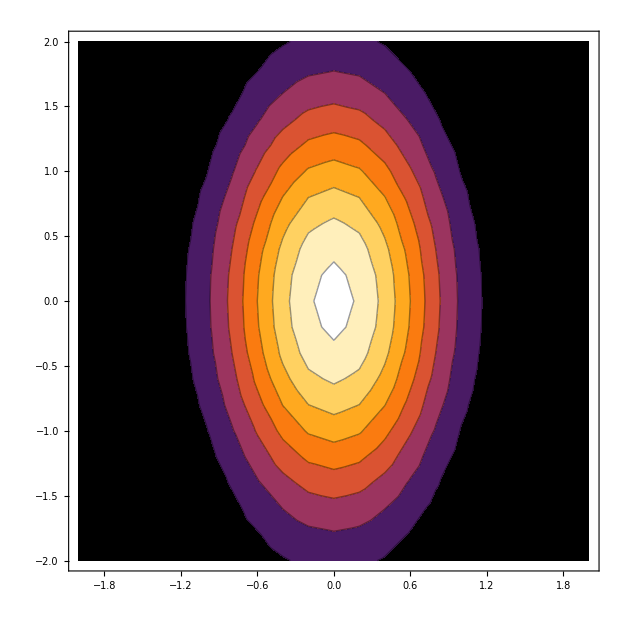

```mathematica
Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-2,2,0.2},{Z,-2,2,0.2}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,21,1},{j,1,21,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]],data3[[18]],data3[[19]],data3[[20]],data3[[21]]]
 
ListContourPlot[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

```mathematica
t=3;ℏ=1;m=1;α=2;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]+(ⅈ*py)/(√(px^2+py^2))*Sin[(ω t)/2]);
```

```mathematica
NIntegrate[Table[Table[(ψ),{x,-2,2,0.2}],{y,-2,2,0.2}],{px,-2,0,2},{py,-2,2},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

{{-0.703604+0.135112 ⅈ,-0.70447+0.0540549 ⅈ,-0.654451-0.0182919 ⅈ,-0.557926-0.0777742 ⅈ,-0.424611-0.122422 ⅈ,-0.268598-0.152432 ⅈ,-0.106818-0.169817 ⅈ,0.0428662-0.177793 ⅈ,0.163741-0.180022 ⅈ,0.242205-0.179818 ⅈ,0.269386-0.179477 ⅈ,0.242205-0.179818 ⅈ,0.163741-0.180022 ⅈ,0.0428662-0.177793 ⅈ,-0.106818-0.169817 ⅈ,-0.268598-0.152432 ⅈ,-0.424611-0.122422 ⅈ,-0.557926-0.0777742 ⅈ,-0.654451-0.0182919 ⅈ,-0.70447+0.0540549 ⅈ,-0.703604+0.135112 ⅈ},{-0.814942+0.161951 ⅈ,-0.812124+0.0708068 ⅈ,-0.747369-0.0135892 ⅈ,-0.626016-0.0865103 ⅈ,-0.459956-0.145265 ⅈ,-0.266453-0.189227 ⅈ,-0.0662662-0.219548 ⅈ,0.1187-0.238613 ⅈ,0.267943-0.249347 ⅈ,0.364775-0.254492 ⅈ,0.398312-0.255976 ⅈ,0.364775-0.254492 ⅈ,0.267943-0.249347 ⅈ,0.1187-0.238613 ⅈ,-0.0662662-0.219548 ⅈ,-0.266453-0.189227 ⅈ,-0.459956-0.145265 ⅈ,-0.626016-0.0865103 ⅈ,-0.747369-0.0135892 ⅈ,-0.812124+0.0708068 ⅈ,-0.814942+0.161951 ⅈ},{-0.930568+0.198138 ⅈ,-0.924047+0.0957969 ⅈ,-0.844249-0.00291908 ⅈ,-0.697504-0.0925879 ⅈ,-0.497936-0.169546 ⅈ,-0.266065-0.231991 ⅈ,-0.0265711-0.279794 ⅈ,0.194503-0.314067 ⅈ,0.372776-0.336591 ⅈ,0.488406-0.349199 ⅈ,0.528447-0.353238 ⅈ,0.488406-0.349199 ⅈ,0.372776-0.336591 ⅈ,0.194503-0.314067 ⅈ,-0.0265711-0.279794 ⅈ,-0.266065-0.231991 ⅈ,-0.497936-0.169546 ⅈ,-0.697504-0.0925879 ⅈ,-0.844249-0.00291908 ⅈ,-0.924047+0.0957969 ⅈ,-0.930568+0.198138 ⅈ},{-1.04702+0.24404 ⅈ,-1.03725+0.129456 ⅈ,-0.943007+0.01421 ⅈ,-0.771603-0.0954583 ⅈ,-0.53936-0.194663 ⅈ,-0.269996-0.280073 ⅈ,0.0079551-0.349857 ⅈ,0.264381-0.40342 ⅈ,0.471089-0.44099 ⅈ,0.605134-0.463159 ⅈ,0.651548-0.470477 ⅈ,0.605134-0.463159 ⅈ,0.471089-0.44099 ⅈ,0.264381-0.40342 ⅈ,0.0079551-0.349857 ⅈ,-0.269996-0.280073 ⅈ,-0.53936-0.194663 ⅈ,-0.771603-0.0954583 ⅈ,-0.943007+0.01421 ⅈ,-1.03725+0.129456 ⅈ,-1.04702+0.24404 ⅈ},{-1.16042+0.299486 ⅈ,-1.14834+0.171802 ⅈ,-1.04124+0.0380812 ⅈ,-0.847327-0.0945043 ⅈ,-0.584966-0.219614 ⅈ,-0.280879-0.332061 ⅈ,0.0327851-0.42793 ⅈ,0.322095-0.504509 ⅈ,0.555281-0.560097 ⅈ,0.706485-0.593746 ⅈ,0.758839-0.605004 ⅈ,0.706485-0.593746 ⅈ,0.555281-0.560097 ⅈ,0.322095-0.504509 ⅈ,0.0327851-0.42793 ⅈ,-0.280879-0.332061 ⅈ,-0.584966-0.219614 ⅈ,-0.847327-0.0945043 ⅈ,-1.04124+0.0380812 ⅈ,-1.14834+0.171802 ⅈ,-1.16042+0.299486 ⅈ},{-1.2666+0.363758 ⅈ,-1.25369+0.222432 ⅈ,-1.13632+0.0687686 ⅈ,-0.923447-0.0890316 ⅈ,-0.635265-0.242982 ⅈ,-0.301135-0.385767 ⅈ,0.0435916-0.511063 ⅈ,0.361597-0.613706 ⅈ,0.617935-0.689752 ⅈ,0.78416-0.736452 ⅈ,0.841717-0.752196 ⅈ,0.78416-0.736452 ⅈ,0.617935-0.689752 ⅈ,0.361597-0.613706 ⅈ,0.0435916-0.511063 ⅈ,-0.301135-0.385767 ⅈ,-0.635265-0.242982 ⅈ,-0.923447-0.0890316 ⅈ,-1.13632+0.0687686 ⅈ,-1.25369+0.222432 ⅈ,-1.2666+0.363758 ⅈ},{-1.36139+0.435611 ⅈ,-1.34958+0.280543 ⅈ,-1.22542+0.106149 ⅈ,-0.998476-0.0782766 ⅈ,-0.690387-0.262965 ⅈ,-0.332674-0.43828 ⅈ,0.0366865-0.595257 ⅈ,0.37759-0.726038 ⅈ,0.652474-0.824211 ⅈ,0.83076-0.885046 ⅈ,0.892499-0.905649 ⅈ,0.83076-0.885046 ⅈ,0.652474-0.824211 ⅈ,0.37759-0.726038 ⅈ,0.0366865-0.595257 ⅈ,-0.332674-0.43828 ⅈ,-0.690387-0.262965 ⅈ,-0.998476-0.0782766 ⅈ,-1.22542+0.106149 ⅈ,-1.34958+0.280543 ⅈ,-1.36139+0.435611 ⅈ},{-1.44083+0.513345 ⅈ,-1.4324+0.344983 ⅈ,-1.3057+0.14992 ⅈ,-1.07066-0.0614333 ⅈ,-0.749946-0.277462 ⅈ,-0.376621-0.486114 ⅈ,0.00942919-0.675666 ⅈ,0.366063-0.835446 ⅈ,0.653796-0.956457 ⅈ,0.84048-1.03189 ⅈ,0.905136-1.05752 ⅈ,0.84048-1.03189 ⅈ,0.653796-0.956457 ⅈ,0.366063-0.835446 ⅈ,0.00942919-0.675666 ⅈ,-0.376621-0.486114 ⅈ,-0.749946-0.277462 ⅈ,-1.07066-0.0614333 ⅈ,-1.3057+0.14992 ⅈ,-1.4324+0.344983 ⅈ,-1.44083+0.513345 ⅈ},{-1.50138+0.594896 ⅈ,-1.49883+0.414317 ⅈ,-1.37435+0.199614 ⅈ,-1.13801-0.0377067 ⅈ,-0.812948-0.284205 ⅈ,-0.4331-0.525428 ⅈ,-0.0394319-0.746911 ⅈ,0.324739-0.935176 ⅈ,0.618806-1.07865 ⅈ,0.809695-1.16846 ⅈ,0.875824-1.19903 ⅈ,0.809695-1.16846 ⅈ,0.618806-1.07865 ⅈ,0.324739-0.935176 ⅈ,-0.0394319-0.746911 ⅈ,-0.4331-0.525428 ⅈ,-0.812948-0.284205 ⅈ,-1.13801-0.0377067 ⅈ,-1.37435+0.199614 ⅈ,-1.49883+0.414317 ⅈ,-1.50138+0.594896 ⅈ},{-1.54013+0.677959 ⅈ,-1.54601+0.486903 ⅈ,-1.42877+0.254612 ⅈ,-1.19831-0.00638744 ⅈ,-0.87774-0.280937 ⅈ,-0.501094-0.552317 ⅈ,-0.109528-0.803473 ⅈ,0.253391-1.01827 ⅈ,0.546797-1.1827 ⅈ,0.737391-1.28594 ⅈ,0.803439-1.32113 ⅈ,0.737391-1.28594 ⅈ,0.546797-1.1827 ⅈ,0.253391-1.01827 ⅈ,-0.109528-0.803473 ⅈ,-0.501094-0.552317 ⅈ,-0.87774-0.280937 ⅈ,-1.19831-0.00638744 ⅈ,-1.42877+0.254612 ⅈ,-1.54601+0.486903 ⅈ,-1.54013+0.677959 ⅈ},{-1.55502+0.760108 ⅈ,-1.57172+0.560972 ⅈ,-1.46664+0.314148 ⅈ,-1.24924+0.0330568 ⅈ,-0.942042-0.265617 ⅈ,-0.578408-0.563138 ⅈ,-0.198776-0.84014 ⅈ,0.153987-1.07812 ⅈ,0.439639-1.26091 ⅈ,0.625371-1.37591 ⅈ,0.689762-1.41515 ⅈ,0.625371-1.37591 ⅈ,0.439639-1.26091 ⅈ,0.153987-1.07812 ⅈ,-0.198776-0.84014 ⅈ,-0.578408-0.563138 ⅈ,-0.942042-0.265617 ⅈ,-1.24924+0.0330568 ⅈ,-1.46664+0.314148 ⅈ,-1.57172+0.560972 ⅈ,-1.55502+0.760108 ⅈ},{-1.54489+0.838927 ⅈ,-1.57445+0.634703 ⅈ,-1.48606+0.377305 ⅈ,-1.28844+0.0808796 ⅈ,-1.00303-0.236636 ⅈ,-0.661746-0.554842 ⅈ,-0.303439-0.852463 ⅈ,0.0306435-1.10904 ⅈ,0.30174-1.30658 ⅈ,0.478228-1.43107 ⅈ,0.539449-1.47358 ⅈ,0.478228-1.43107 ⅈ,0.30174-1.30658 ⅈ,0.0306435-1.10904 ⅈ,-0.303439-0.852463 ⅈ,-0.661746-0.554842 ⅈ,-1.00303-0.236636 ⅈ,-1.28844+0.0808796 ⅈ,-1.48606+0.377305 ⅈ,-1.57445+0.634703 ⅈ,-1.54489+0.838927 ⅈ},{-1.5096+0.91212 ⅈ,-1.55354+0.706284 ⅈ,-1.48565+0.443009 ⅈ,-1.31368+0.136956 ⅈ,-1.05749-0.193022 ⅈ,-0.746895-0.525297 ⅈ,-0.418343-0.837175 ⅈ,-0.110615-1.10674 ⅈ,0.13979-1.31467 ⅈ,0.303073-1.44585 ⅈ,0.359756-1.49067 ⅈ,0.303073-1.44585 ⅈ,0.13979-1.31467 ⅈ,-0.110615-1.10674 ⅈ,-0.418343-0.837175 ⅈ,-0.746895-0.525297 ⅈ,-1.05749-0.193022 ⅈ,-1.31368+0.136956 ⅈ,-1.48565+0.443009 ⅈ,-1.55354+0.706284 ⅈ,-1.5096+0.91212 ⅈ},{-1.44998+0.977604 ⅈ,-1.50916+0.773964 ⅈ,-1.4646+0.510016 ⅈ,-1.32295+0.200697 ⅈ,-1.10203-0.134609 ⅈ,-0.829004-0.473538 ⅈ,-0.53722-0.79254 ⅈ,-0.262269-1.06881 ⅈ,-0.0377056-1.2822 ⅈ,0.109042-1.41695 ⅈ,0.160036-1.46301 ⅈ,0.109042-1.41695 ⅈ,-0.0377056-1.2822 ⅈ,-0.262269-1.06881 ⅈ,-0.53722-0.79254 ⅈ,-0.829004-0.473538 ⅈ,-1.10203-0.134609 ⅈ,-1.32295+0.200697 ⅈ,-1.4646+0.510016 ⅈ,-1.50916+0.773964 ⅈ,-1.44998+0.977604 ⅈ},{-1.36782+1.03358 ⅈ,-1.4423+0.836087 ⅈ,-1.42279+0.576908 ⅈ,-1.31461+0.27099 ⅈ,-1.13332-0.0621537 ⅈ,-0.902937-0.39995 ⅈ,-0.653171-0.718577 ⅈ,-0.41585-0.994941 ⅈ,-0.221046-1.20863 ⅈ,-0.0933764-1.34365 ⅈ,-0.0489522-1.38982 ⅈ,-0.0933764-1.34365 ⅈ,-0.221046-1.20863 ⅈ,-0.41585-0.994941 ⅈ,-0.653171-0.718577 ⅈ,-0.902937-0.39995 ⅈ,-1.13332-0.0621537 ⅈ,-1.31461+0.27099 ⅈ,-1.42279+0.576908 ⅈ,-1.4423+0.836087 ⅈ,-1.36782+1.03358 ⅈ},{-1.2657+1.07857 ⅈ,-1.35476+0.891124 ⅈ,-1.36072+0.642091 ⅈ,-1.28757+0.346178 ⅈ,-1.14835+0.022615 ⅈ,-0.963662-0.306333 ⅈ,-0.759185-0.617161 ⅈ,-0.562582-0.887083 ⅈ,-0.400064-1.09595 ⅈ,-0.293125-1.22799 ⅈ,-0.255845-1.27316 ⅈ,-0.293125-1.22799 ⅈ,-0.400064-1.09595 ⅈ,-0.562582-0.887083 ⅈ,-0.759185-0.617161 ⅈ,-0.963662-0.306333 ⅈ,-1.14835+0.022615 ⅈ,-1.28757+0.346178 ⅈ,-1.36072+0.642091 ⅈ,-1.35476+0.891124 ⅈ,-1.2657+1.07857 ⅈ},{-1.14688+1.11145 ⅈ,-1.24898+0.937675 ⅈ,-1.27958+0.703817 ⅈ,-1.24134+0.424082 ⅈ,-1.14469+0.117033 ⅈ,-1.00665-0.195862 ⅈ,-0.848676-0.491963 ⅈ,-0.694046-0.74934 ⅈ,-0.564892-0.948623 ⅈ,-0.479407-1.07465 ⅈ,-0.449527-1.11776 ⅈ,-0.479407-1.07465 ⅈ,-0.564892-0.948623 ⅈ,-0.694046-0.74934 ⅈ,-0.848676-0.491963 ⅈ,-1.00665-0.195862 ⅈ,-1.14469+0.117033 ⅈ,-1.24134+0.424082 ⅈ,-1.27958+0.703817 ⅈ,-1.24898+0.937675 ⅈ,-1.14688+1.11145 ⅈ},{-1.01506+1.13142 ⅈ,-1.12794+0.974499 ⅈ,-1.18118+0.76022 ⅈ,-1.17614+0.502074 ⅈ,-1.12068+0.217612 ⅈ,-1.02822-0.0729236 ⅈ,-0.915987-0.348237 ⅈ,-0.802807-0.58774 ⅈ,-0.70669-0.77327 ⅈ,-0.642483-0.890627 ⅈ,-0.619947-0.93078 ⅈ,-0.642483-0.890627 ⅈ,-0.70669-0.77327 ⅈ,-0.802807-0.58774 ⅈ,-0.915987-0.348237 ⅈ,-1.02822-0.0729236 ⅈ,-1.12068+0.217612 ⅈ,-1.17614+0.502074 ⅈ,-1.18118+0.76022 ⅈ,-1.12794+0.974499 ⅈ,-1.01506+1.13142 ⅈ},{-0.874209+1.13804 ⅈ,-0.995022+1.00051 ⅈ,-1.06788+0.809378 ⅈ,-1.09293+0.577199 ⅈ,-1.07561+0.320237 ⅈ,-1.02587+0.0571539 ⅈ,-0.956813-0.192484 ⅈ,-0.882952-0.409815 ⅈ,-0.818272-0.578239 ⅈ,-0.774353-0.684799 ⅈ,-0.758826-0.721259 ⅈ,-0.774353-0.684799 ⅈ,-0.818272-0.578239 ⅈ,-0.882952-0.409815 ⅈ,-0.956813-0.192484 ⅈ,-1.02587+0.0571539 ⅈ,-1.07561+0.320237 ⅈ,-1.09293+0.577199 ⅈ,-1.06788+0.809378 ⅈ,-0.995022+1.00051 ⅈ,-0.874209+1.13804 ⅈ},{-0.728336+1.13115 ⅈ,-0.853832+1.01483 ⅈ,-0.942483+0.849391 ⅈ,-0.993412+0.646334 ⅈ,-1.00982+0.42041 ⅈ,-0.998433+0.188447 ⅈ,-0.968506-0.0320014 ⅈ,-0.930495-0.224078 ⅈ,-0.894589-0.372994 ⅈ,-0.869281-0.467229 ⅈ,-0.86019-0.499475 ⅈ,-0.869281-0.467229 ⅈ,-0.894589-0.372994 ⅈ,-0.930495-0.224078 ⅈ,-0.968506-0.0320014 ⅈ,-0.998433+0.188447 ⅈ,-1.00982+0.42041 ⅈ,-0.993412+0.646334 ⅈ,-0.942483+0.849391 ⅈ,-0.853832+1.01483 ⅈ,-0.728336+1.13115 ⅈ},{-0.581324+1.11087 ⅈ,-0.708035+1.01676 ⅈ,-0.808151+0.878483 ⅈ,-0.879954+0.706379 ⅈ,-0.924684+0.513554 ⅈ,-0.946189+0.314842 ⅈ,-0.950239+0.12562 ⅈ,-0.9436-0.0394197 ⅈ,-0.932999-0.167439 ⅈ,-0.924107-0.248471 ⅈ,-0.920702-0.276201 ⅈ,-0.924107-0.248471 ⅈ,-0.932999-0.167439 ⅈ,-0.9436-0.0394197 ⅈ,-0.950239+0.12562 ⅈ,-0.946189+0.314842 ⅈ,-0.924684+0.513554 ⅈ,-0.879954+0.706379 ⅈ,-0.808151+0.878483 ⅈ,-0.708035+1.01676 ⅈ,-0.581324+1.11087 ⅈ}}

{{0.513314,0.4992,0.428641,0.31733,0.195282,0.0953803,0.0402479,0.033448,0.059219,0.0909977,0.104781,0.0909977,0.059219,0.033448,0.0402479,0.0953803,0.195282,0.31733,0.428641,0.4992,0.513314},{0.690359,0.664559,0.558745,0.39938,0.232662,0.106804,0.0525927,0.071026,0.133968,0.197827,0.224176,0.197827,0.133968,0.071026,0.0525927,0.106804,0.232662,0.39938,0.558745,0.664559,0.690359},{0.905215,0.86304,0.712765,0.495084,0.276686,0.124611,0.0789906,0.136469,0.252256,0.36048,0.404033,0.36048,0.252256,0.136469,0.0789906,0.124611,0.276686,0.495084,0.712765,0.86304,0.905215},{1.15582,1.09264,0.889464,0.604484,0.328803,0.151338,0.122463,0.232645,0.416396,0.580703,0.645863,0.580703,0.416396,0.232645,0.122463,0.151338,0.328803,0.604484,0.889464,1.09264,1.15582},{1.43626,1.34821,1.08564,0.726894,0.390415,0.189158,0.184199,0.358274,0.622046,0.851655,0.941866,0.851655,0.622046,0.358274,0.184199,0.189158,0.390415,0.726894,1.08564,1.34821,1.43626},{1.73659,1.62122,1.29594,0.860681,0.462601,0.239499,0.263086,0.507387,0.857601,1.15727,1.27429,1.15727,0.857601,0.507387,0.263086,0.239499,0.462601,0.860681,1.29594,1.62122,1.73659},{2.04315,1.90008,1.51292,1.00308,0.545784,0.302761,0.355677,0.669705,1.10505,1.47347,1.61675,1.47347,1.10505,0.669705,0.355677,0.302761,0.545784,1.00308,1.51292,1.90008,2.04315},{2.33952,2.17078,1.72732,1.15009,0.639404,0.37815,0.456614,0.831972,1.34226,1.77121,1.93762,1.77121,1.34226,0.831972,0.456614,0.37815,0.639404,1.15009,1.72732,2.17078,2.33952},{2.60803,2.41814,1.92869,1.29648,0.741656,0.46365,0.559431,0.980009,1.54641,2.02091,2.20475,2.02091,1.54641,0.980009,0.559431,0.46365,0.741656,1.29648,1.92869,2.41814,2.60803},{2.83164,2.62722,2.10622,1.43598,0.849353,0.556149,0.657565,1.10108,1.69777,2.19738,2.39089,2.19738,1.69777,1.10108,0.657565,0.556149,0.849353,1.43598,2.10622,2.62722,2.83164},{2.99585,2.78498,2.24973,1.56168,0.957995,0.65168,0.745347,1.18606,1.78316,2.28421,2.47842,2.28421,1.78316,1.18606,0.745347,0.65168,0.957995,1.56168,2.24973,2.78498,2.99585},{3.09049,2.88175,2.35074,1.66663,1.06206,0.745758,0.818768,1.2309,1.7982,2.27665,2.46244,2.27665,1.7982,1.2309,0.818768,0.745758,1.06206,1.66663,2.35074,2.88175,3.09049},{3.11084,2.91233,2.4034,1.74452,1.15554,0.833789,0.875874,1.23711,1.74789,2.18233,2.35153,2.18233,1.74789,1.23711,0.875874,0.833789,1.15554,1.74452,2.4034,2.91233,3.11084},{3.05815,2.87658,2.40518,1.79046,1.23259,0.911487,0.916724,1.21113,1.64545,2.01963,2.16601,2.01963,1.64545,1.21113,0.916724,0.911487,1.23259,1.79046,2.40518,2.87658,3.05815},{2.93921,2.77928,2.35714,1.80164,1.28828,0.975255,0.942985,1.16284,1.50965,1.81412,1.93401,1.81412,1.50965,1.16284,0.942985,0.975255,1.28828,1.80164,2.35714,2.77928,2.93921},{2.76532,2.62948,2.26383,1.77767,1.31923,1.02248,0.95725,1.10341,1.36116,1.59389,1.68639,1.59389,1.36116,1.10341,0.95725,1.02248,1.31923,1.77767,2.26383,2.62948,2.76532},{2.55066,2.43918,2.13268,1.72076,1.32402,1.0517,0.962279,1.04321,1.21899,1.3847,1.45146,1.3847,1.21899,1.04321,0.962279,1.0517,1.32402,1.72076,2.13268,2.43918,2.55066},{2.31047,2.22189,1.97312,1.63537,1.30328,1.06256,0.960301,0.989936,1.09736,1.206,1.25069,1.206,1.09736,0.989936,0.960301,1.06256,1.30328,1.63537,1.97312,2.22189,2.31047},{2.05938,1.9911,1.79545,1.52765,1.25949,1.05568,0.95254,0.947553,1.00393,1.06857,1.09603,1.06857,1.00393,0.947553,0.95254,1.05568,1.25949,1.52765,1.79545,1.9911,2.05938},{1.80997,1.75891,1.60974,1.40462,1.19648,1.03238,0.939028,0.916033,0.939414,0.973952,0.989402,0.973952,0.939414,0.916033,0.939028,1.03238,1.19648,1.40462,1.60974,1.75891,1.80997},{1.57197,1.53511,1.42484,1.27329,1.11878,0.994399,0.918734,0.891935,0.898522,0.915711,0.923979,0.915711,0.898522,0.891935,0.918734,0.994399,1.11878,1.27329,1.42484,1.53511,1.57197}}

{{0.513314,0.4992,0.428641,0.31733,0.195282,0.0953803,0.0402479,0.033448,0.059219,0.0909977,0.104781,0.0909977,0.059219,0.033448,0.0402479,0.0953803,0.195282,0.31733,0.428641,0.4992,0.513314},{0.690359,0.664559,0.558745,0.39938,0.232662,0.106804,0.0525927,0.071026,0.133968,0.197827,0.224176,0.197827,0.133968,0.071026,0.0525927,0.106804,0.232662,0.39938,0.558745,0.664559,0.690359},{0.905215,0.86304,0.712765,0.495084,0.276686,0.124611,0.0789906,0.136469,0.252256,0.36048,0.404033,0.36048,0.252256,0.136469,0.0789906,0.124611,0.276686,0.495084,0.712765,0.86304,0.905215},{1.15582,1.09264,0.889464,0.604484,0.328803,0.151338,0.122463,0.232645,0.416396,0.580703,0.645863,0.580703,0.416396,0.232645,0.122463,0.151338,0.328803,0.604484,0.889464,1.09264,1.15582},{1.43626,1.34821,1.08564,0.726894,0.390415,0.189158,0.184199,0.358274,0.622046,0.851655,0.941866,0.851655,0.622046,0.358274,0.184199,0.189158,0.390415,0.726894,1.08564,1.34821,1.43626},{1.73659,1.62122,1.29594,0.860681,0.462601,0.239499,0.263086,0.507387,0.857601,1.15727,1.27429,1.15727,0.857601,0.507387,0.263086,0.239499,0.462601,0.860681,1.29594,1.62122,1.73659},{2.04315,1.90008,1.51292,1.00308,0.545784,0.302761,0.355677,0.669705,1.10505,1.47347,1.61675,1.47347,1.10505,0.669705,0.355677,0.302761,0.545784,1.00308,1.51292,1.90008,2.04315},{2.33952,2.17078,1.72732,1.15009,0.639404,0.37815,0.456614,0.831972,1.34226,1.77121,1.93762,1.77121,1.34226,0.831972,0.456614,0.37815,0.639404,1.15009,1.72732,2.17078,2.33952},{2.60803,2.41814,1.92869,1.29648,0.741656,0.46365,0.559431,0.980009,1.54641,2.02091,2.20475,2.02091,1.54641,0.980009,0.559431,0.46365,0.741656,1.29648,1.92869,2.41814,2.60803},{2.83164,2.62722,2.10622,1.43598,0.849353,0.556149,0.657565,1.10108,1.69777,2.19738,2.39089,2.19738,1.69777,1.10108,0.657565,0.556149,0.849353,1.43598,2.10622,2.62722,2.83164},{2.99585,2.78498,2.24973,1.56168,0.957995,0.65168,0.745347,1.18606,1.78316,2.28421,2.47842,2.28421,1.78316,1.18606,0.745347,0.65168,0.957995,1.56168,2.24973,2.78498,2.99585},{3.09049,2.88175,2.35074,1.66663,1.06206,0.745758,0.818768,1.2309,1.7982,2.27665,2.46244,2.27665,1.7982,1.2309,0.818768,0.745758,1.06206,1.66663,2.35074,2.88175,3.09049},{3.11084,2.91233,2.4034,1.74452,1.15554,0.833789,0.875874,1.23711,1.74789,2.18233,2.35153,2.18233,1.74789,1.23711,0.875874,0.833789,1.15554,1.74452,2.4034,2.91233,3.11084},{3.05815,2.87658,2.40518,1.79046,1.23259,0.911487,0.916724,1.21113,1.64545,2.01963,2.16601,2.01963,1.64545,1.21113,0.916724,0.911487,1.23259,1.79046,2.40518,2.87658,3.05815},{2.93921,2.77928,2.35714,1.80164,1.28828,0.975255,0.942985,1.16284,1.50965,1.81412,1.93401,1.81412,1.50965,1.16284,0.942985,0.975255,1.28828,1.80164,2.35714,2.77928,2.93921},{2.76532,2.62948,2.26383,1.77767,1.31923,1.02248,0.95725,1.10341,1.36116,1.59389,1.68639,1.59389,1.36116,1.10341,0.95725,1.02248,1.31923,1.77767,2.26383,2.62948,2.76532},{2.55066,2.43918,2.13268,1.72076,1.32402,1.0517,0.962279,1.04321,1.21899,1.3847,1.45146,1.3847,1.21899,1.04321,0.962279,1.0517,1.32402,1.72076,2.13268,2.43918,2.55066},{2.31047,2.22189,1.97312,1.63537,1.30328,1.06256,0.960301,0.989936,1.09736,1.206,1.25069,1.206,1.09736,0.989936,0.960301,1.06256,1.30328,1.63537,1.97312,2.22189,2.31047},{2.05938,1.9911,1.79545,1.52765,1.25949,1.05568,0.95254,0.947553,1.00393,1.06857,1.09603,1.06857,1.00393,0.947553,0.95254,1.05568,1.25949,1.52765,1.79545,1.9911,2.05938},{1.80997,1.75891,1.60974,1.40462,1.19648,1.03238,0.939028,0.916033,0.939414,0.973952,0.989402,0.973952,0.939414,0.916033,0.939028,1.03238,1.19648,1.40462,1.60974,1.75891,1.80997},{1.57197,1.53511,1.42484,1.27329,1.11878,0.994399,0.918734,0.891935,0.898522,0.915711,0.923979,0.915711,0.898522,0.891935,0.918734,0.994399,1.11878,1.27329,1.42484,1.53511,1.57197}}

{{-2.,-2.,0.513314},{-2.,-1.8,0.690359},{-2.,-1.6,0.905215},{-2.,-1.4,1.15582},{-2.,-1.2,1.43626},{-2.,-1.,1.73659},{-2.,-0.8,2.04315},{-2.,-0.6,2.33952},{-2.,-0.4,2.60803},{-2.,-0.2,2.83164},{-2.,0.,2.99585},{-2.,0.2,3.09049},{-2.,0.4,3.11084},{-2.,0.6,3.05815},{-2.,0.8,2.93921},{-2.,1.,2.76532},{-2.,1.2,2.55066},{-2.,1.4,2.31047},{-2.,1.6,2.05938},{-2.,1.8,1.80997},{-2.,2.,1.57197},{-1.8,-2.,0.4992},{-1.8,-1.8,0.664559},{-1.8,-1.6,0.86304},{-1.8,-1.4,1.09264},{-1.8,-1.2,1.34821},{-1.8,-1.,1.62122},{-1.8,-0.8,1.90008},{-1.8,-0.6,2.17078},{-1.8,-0.4,2.41814},{-1.8,-0.2,2.62722},{-1.8,0.,2.78498},{-1.8,0.2,2.88175},{-1.8,0.4,2.91233},{-1.8,0.6,2.87658},{-1.8,0.8,2.77928},{-1.8,1.,2.62948},{-1.8,1.2,2.43918},{-1.8,1.4,2.22189},{-1.8,1.6,1.9911},{-1.8,1.8,1.75891},{-1.8,2.,1.53511},{-1.6,-2.,0.428641},{-1.6,-1.8,0.558745},{-1.6,-1.6,0.712765},{-1.6,-1.4,0.889464},{-1.6,-1.2,1.08564},{-1.6,-1.,1.29594},{-1.6,-0.8,1.51292},{-1.6,-0.6,1.72732},{-1.6,-0.4,1.92869},{-1.6,-0.2,2.10622},{-1.6,0.,2.24973},{-1.6,0.2,2.35074},{-1.6,0.4,2.4034},{-1.6,0.6,2.40518},{-1.6,0.8,2.35714},{-1.6,1.,2.26383},{-1.6,1.2,2.13268},{-1.6,1.4,1.97312},{-1.6,1.6,1.79545},{-1.6,1.8,1.60974},{-1.6,2.,1.42484},{-1.4,-2.,0.31733},{-1.4,-1.8,0.39938},{-1.4,-1.6,0.495084},{-1.4,-1.4,0.604484},{-1.4,-1.2,0.726894},{-1.4,-1.,0.860681},{-1.4,-0.8,1.00308},{-1.4,-0.6,1.15009},{-1.4,-0.4,1.29648},{-1.4,-0.2,1.43598},{-1.4,0.,1.56168},{-1.4,0.2,1.66663},{-1.4,0.4,1.74452},{-1.4,0.6,1.79046},{-1.4,0.8,1.80164},{-1.4,1.,1.77767},{-1.4,1.2,1.72076},{-1.4,1.4,1.63537},{-1.4,1.6,1.52765},{-1.4,1.8,1.40462},{-1.4,2.,1.27329},{-1.2,-2.,0.195282},{-1.2,-1.8,0.232662},{-1.2,-1.6,0.276686},{-1.2,-1.4,0.328803},{-1.2,-1.2,0.390415},{-1.2,-1.,0.462601},{-1.2,-0.8,0.545784},{-1.2,-0.6,0.639404},{-1.2,-0.4,0.741656},{-1.2,-0.2,0.849353},{-1.2,0.,0.957995},{-1.2,0.2,1.06206},{-1.2,0.4,1.15554},{-1.2,0.6,1.23259},{-1.2,0.8,1.28828},{-1.2,1.,1.31923},{-1.2,1.2,1.32402},{-1.2,1.4,1.30328},{-1.2,1.6,1.25949},{-1.2,1.8,1.19648},{-1.2,2.,1.11878},{-1.,-2.,0.0953803},{-1.,-1.8,0.106804},{-1.,-1.6,0.124611},{-1.,-1.4,0.151338},{-1.,-1.2,0.189158},{-1.,-1.,0.239499},{-1.,-0.8,0.302761},{-1.,-0.6,0.37815},{-1.,-0.4,0.46365},{-1.,-0.2,0.556149},{-1.,0.,0.65168},{-1.,0.2,0.745758},{-1.,0.4,0.833789},{-1.,0.6,0.911487},{-1.,0.8,0.975255},{-1.,1.,1.02248},{-1.,1.2,1.0517},{-1.,1.4,1.06256},{-1.,1.6,1.05568},{-1.,1.8,1.03238},{-1.,2.,0.994399},{-0.8,-2.,0.0402479},{-0.8,-1.8,0.0525927},{-0.8,-1.6,0.0789906},{-0.8,-1.4,0.122463},{-0.8,-1.2,0.184199},{-0.8,-1.,0.263086},{-0.8,-0.8,0.355677},{-0.8,-0.6,0.456614},{-0.8,-0.4,0.559431},{-0.8,-0.2,0.657565},{-0.8,0.,0.745347},{-0.8,0.2,0.818768},{-0.8,0.4,0.875874},{-0.8,0.6,0.916724},{-0.8,0.8,0.942985},{-0.8,1.,0.95725},{-0.8,1.2,0.962279},{-0.8,1.4,0.960301},{-0.8,1.6,0.95254},{-0.8,1.8,0.939028},{-0.8,2.,0.918734},{-0.6,-2.,0.033448},{-0.6,-1.8,0.071026},{-0.6,-1.6,0.136469},{-0.6,-1.4,0.232645},{-0.6,-1.2,0.358274},{-0.6,-1.,0.507387},{-0.6,-0.8,0.669705},{-0.6,-0.6,0.831972},{-0.6,-0.4,0.980009},{-0.6,-0.2,1.10108},{-0.6,0.,1.18606},{-0.6,0.2,1.2309},{-0.6,0.4,1.23711},{-0.6,0.6,1.21113},{-0.6,0.8,1.16284},{-0.6,1.,1.10341},{-0.6,1.2,1.04321},{-0.6,1.4,0.989936},{-0.6,1.6,0.947553},{-0.6,1.8,0.916033},{-0.6,2.,0.891935},{-0.4,-2.,0.059219},{-0.4,-1.8,0.133968},{-0.4,-1.6,0.252256},{-0.4,-1.4,0.416396},{-0.4,-1.2,0.622046},{-0.4,-1.,0.857601},{-0.4,-0.8,1.10505},{-0.4,-0.6,1.34226},{-0.4,-0.4,1.54641},{-0.4,-0.2,1.69777},{-0.4,0.,1.78316},{-0.4,0.2,1.7982},{-0.4,0.4,1.74789},{-0.4,0.6,1.64545},{-0.4,0.8,1.50965},{-0.4,1.,1.36116},{-0.4,1.2,1.21899},{-0.4,1.4,1.09736},{-0.4,1.6,1.00393},{-0.4,1.8,0.939414},{-0.4,2.,0.898522},{-0.2,-2.,0.0909977},{-0.2,-1.8,0.197827},{-0.2,-1.6,0.36048},{-0.2,-1.4,0.580703},{-0.2,-1.2,0.851655},{-0.2,-1.,1.15727},{-0.2,-0.8,1.47347},{-0.2,-0.6,1.77121},{-0.2,-0.4,2.02091},{-0.2,-0.2,2.19738},{-0.2,0.,2.28421},{-0.2,0.2,2.27665},{-0.2,0.4,2.18233},{-0.2,0.6,2.01963},{-0.2,0.8,1.81412},{-0.2,1.,1.59389},{-0.2,1.2,1.3847},{-0.2,1.4,1.206},{-0.2,1.6,1.06857},{-0.2,1.8,0.973952},{-0.2,2.,0.915711},{0.,-2.,0.104781},{0.,-1.8,0.224176},{0.,-1.6,0.404033},{0.,-1.4,0.645863},{0.,-1.2,0.941866},{0.,-1.,1.27429},{0.,-0.8,1.61675},{0.,-0.6,1.93762},{0.,-0.4,2.20475},{0.,-0.2,2.39089},{0.,0.,2.47842},{0.,0.2,2.46244},{0.,0.4,2.35153},{0.,0.6,2.16601},{0.,0.8,1.93401},{0.,1.,1.68639},{0.,1.2,1.45146},{0.,1.4,1.25069},{0.,1.6,1.09603},{0.,1.8,0.989402},{0.,2.,0.923979},{0.2,-2.,0.0909977},{0.2,-1.8,0.197827},{0.2,-1.6,0.36048},{0.2,-1.4,0.580703},{0.2,-1.2,0.851655},{0.2,-1.,1.15727},{0.2,-0.8,1.47347},{0.2,-0.6,1.77121},{0.2,-0.4,2.02091},{0.2,-0.2,2.19738},{0.2,0.,2.28421},{0.2,0.2,2.27665},{0.2,0.4,2.18233},{0.2,0.6,2.01963},{0.2,0.8,1.81412},{0.2,1.,1.59389},{0.2,1.2,1.3847},{0.2,1.4,1.206},{0.2,1.6,1.06857},{0.2,1.8,0.973952},{0.2,2.,0.915711},{0.4,-2.,0.059219},{0.4,-1.8,0.133968},{0.4,-1.6,0.252256},{0.4,-1.4,0.416396},{0.4,-1.2,0.622046},{0.4,-1.,0.857601},{0.4,-0.8,1.10505},{0.4,-0.6,1.34226},{0.4,-0.4,1.54641},{0.4,-0.2,1.69777},{0.4,0.,1.78316},{0.4,0.2,1.7982},{0.4,0.4,1.74789},{0.4,0.6,1.64545},{0.4,0.8,1.50965},{0.4,1.,1.36116},{0.4,1.2,1.21899},{0.4,1.4,1.09736},{0.4,1.6,1.00393},{0.4,1.8,0.939414},{0.4,2.,0.898522},{0.6,-2.,0.033448},{0.6,-1.8,0.071026},{0.6,-1.6,0.136469},{0.6,-1.4,0.232645},{0.6,-1.2,0.358274},{0.6,-1.,0.507387},{0.6,-0.8,0.669705},{0.6,-0.6,0.831972},{0.6,-0.4,0.980009},{0.6,-0.2,1.10108},{0.6,0.,1.18606},{0.6,0.2,1.2309},{0.6,0.4,1.23711},{0.6,0.6,1.21113},{0.6,0.8,1.16284},{0.6,1.,1.10341},{0.6,1.2,1.04321},{0.6,1.4,0.989936},{0.6,1.6,0.947553},{0.6,1.8,0.916033},{0.6,2.,0.891935},{0.8,-2.,0.0402479},{0.8,-1.8,0.0525927},{0.8,-1.6,0.0789906},{0.8,-1.4,0.122463},{0.8,-1.2,0.184199},{0.8,-1.,0.263086},{0.8,-0.8,0.355677},{0.8,-0.6,0.456614},{0.8,-0.4,0.559431},{0.8,-0.2,0.657565},{0.8,0.,0.745347},{0.8,0.2,0.818768},{0.8,0.4,0.875874},{0.8,0.6,0.916724},{0.8,0.8,0.942985},{0.8,1.,0.95725},{0.8,1.2,0.962279},{0.8,1.4,0.960301},{0.8,1.6,0.95254},{0.8,1.8,0.939028},{0.8,2.,0.918734},{1.,-2.,0.0953803},{1.,-1.8,0.106804},{1.,-1.6,0.124611},{1.,-1.4,0.151338},{1.,-1.2,0.189158},{1.,-1.,0.239499},{1.,-0.8,0.302761},{1.,-0.6,0.37815},{1.,-0.4,0.46365},{1.,-0.2,0.556149},{1.,0.,0.65168},{1.,0.2,0.745758},{1.,0.4,0.833789},{1.,0.6,0.911487},{1.,0.8,0.975255},{1.,1.,1.02248},{1.,1.2,1.0517},{1.,1.4,1.06256},{1.,1.6,1.05568},{1.,1.8,1.03238},{1.,2.,0.994399},{1.2,-2.,0.195282},{1.2,-1.8,0.232662},{1.2,-1.6,0.276686},{1.2,-1.4,0.328803},{1.2,-1.2,0.390415},{1.2,-1.,0.462601},{1.2,-0.8,0.545784},{1.2,-0.6,0.639404},{1.2,-0.4,0.741656},{1.2,-0.2,0.849353},{1.2,0.,0.957995},{1.2,0.2,1.06206},{1.2,0.4,1.15554},{1.2,0.6,1.23259},{1.2,0.8,1.28828},{1.2,1.,1.31923},{1.2,1.2,1.32402},{1.2,1.4,1.30328},{1.2,1.6,1.25949},{1.2,1.8,1.19648},{1.2,2.,1.11878},{1.4,-2.,0.31733},{1.4,-1.8,0.39938},{1.4,-1.6,0.495084},{1.4,-1.4,0.604484},{1.4,-1.2,0.726894},{1.4,-1.,0.860681},{1.4,-0.8,1.00308},{1.4,-0.6,1.15009},{1.4,-0.4,1.29648},{1.4,-0.2,1.43598},{1.4,0.,1.56168},{1.4,0.2,1.66663},{1.4,0.4,1.74452},{1.4,0.6,1.79046},{1.4,0.8,1.80164},{1.4,1.,1.77767},{1.4,1.2,1.72076},{1.4,1.4,1.63537},{1.4,1.6,1.52765},{1.4,1.8,1.40462},{1.4,2.,1.27329},{1.6,-2.,0.428641},{1.6,-1.8,0.558745},{1.6,-1.6,0.712765},{1.6,-1.4,0.889464},{1.6,-1.2,1.08564},{1.6,-1.,1.29594},{1.6,-0.8,1.51292},{1.6,-0.6,1.72732},{1.6,-0.4,1.92869},{1.6,-0.2,2.10622},{1.6,0.,2.24973},{1.6,0.2,2.35074},{1.6,0.4,2.4034},{1.6,0.6,2.40518},{1.6,0.8,2.35714},{1.6,1.,2.26383},{1.6,1.2,2.13268},{1.6,1.4,1.97312},{1.6,1.6,1.79545},{1.6,1.8,1.60974},{1.6,2.,1.42484},{1.8,-2.,0.4992},{1.8,-1.8,0.664559},{1.8,-1.6,0.86304},{1.8,-1.4,1.09264},{1.8,-1.2,1.34821},{1.8,-1.,1.62122},{1.8,-0.8,1.90008},{1.8,-0.6,2.17078},{1.8,-0.4,2.41814},{1.8,-0.2,2.62722},{1.8,0.,2.78498},{1.8,0.2,2.88175},{1.8,0.4,2.91233},{1.8,0.6,2.87658},{1.8,0.8,2.77928},{1.8,1.,2.62948},{1.8,1.2,2.43918},{1.8,1.4,2.22189},{1.8,1.6,1.9911},{1.8,1.8,1.75891},{1.8,2.,1.53511},{2.,-2.,0.513314},{2.,-1.8,0.690359},{2.,-1.6,0.905215},{2.,-1.4,1.15582},{2.,-1.2,1.43626},{2.,-1.,1.73659},{2.,-0.8,2.04315},{2.,-0.6,2.33952},{2.,-0.4,2.60803},{2.,-0.2,2.83164},{2.,0.,2.99585},{2.,0.2,3.09049},{2.,0.4,3.11084},{2.,0.6,3.05815},{2.,0.8,2.93921},{2.,1.,2.76532},{2.,1.2,2.55066},{2.,1.4,2.31047},{2.,1.6,2.05938},{2.,1.8,1.80997},{2.,2.,1.57197}}

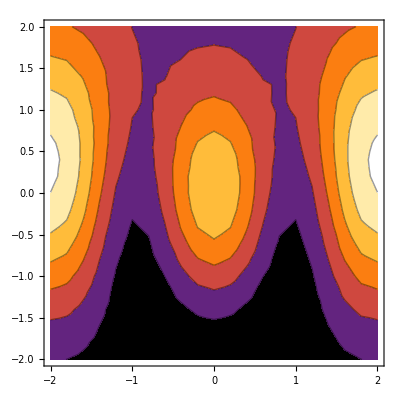

```mathematica
Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-2,2,0.2},{Z,-2,2,0.2}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,21,1},{j,1,21,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]],data3[[18]],data3[[19]],data3[[20]],data3[[21]]]
 
ListContourPlot[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

```mathematica
t=4;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]+(ⅈ*py)/(√(px^2+py^2))*Sin[(ω t)/2]);
```

```mathematica
NIntegrate[Table[Table[(ψ),{x,-2,2,0.4}],{y,-2,2,0.4}],{px,-2,0,2},{py,-2,2},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

{{-0.216099-0.594922 ⅈ,-0.53459-0.351994 ⅈ,-0.791604+0.0949712 ⅈ,-0.963167+0.609814 ⅈ,-1.05462+1.01715 ⅈ,-1.08238+1.17164 ⅈ,-1.05462+1.01715 ⅈ,-0.963167+0.609814 ⅈ,-0.791604+0.0949712 ⅈ,-0.53459-0.351994 ⅈ,-0.216099-0.594922 ⅈ},{-0.398254-0.609011 ⅈ,-0.720464-0.245122 ⅈ,-0.919647+0.332422 ⅈ,-1.00033+0.96252 ⅈ,-1.01128+1.44842 ⅈ,-1.00717+1.63073 ⅈ,-1.01128+1.44842 ⅈ,-1.00033+0.96252 ⅈ,-0.919647+0.332422 ⅈ,-0.720464-0.245122 ⅈ,-0.398254-0.609011 ⅈ},{-0.549408-0.560262 ⅈ,-0.841487-0.0830399 ⅈ,-0.954685+0.600299 ⅈ,-0.925034+1.31326 ⅈ,-0.844742+1.8508 ⅈ,-0.805408+2.05051 ⅈ,-0.844742+1.8508 ⅈ,-0.925034+1.31326 ⅈ,-0.954685+0.600299 ⅈ,-0.841487-0.0830399 ⅈ,-0.549408-0.560262 ⅈ},{-0.637847-0.468797 ⅈ,-0.872403+0.0976612 ⅈ,-0.885797+0.849954 ⅈ,-0.743652+1.60642 ⅈ,-0.57529+2.1656 ⅈ,-0.502703+2.37152 ⅈ,-0.57529+2.1656 ⅈ,-0.743652+1.60642 ⅈ,-0.885797+0.849954 ⅈ,-0.872403+0.0976612 ⅈ,-0.637847-0.468797 ⅈ},{-0.64712-0.363425 ⅈ,-0.808466+0.256763 ⅈ,-0.72466+1.03592 ⅈ,-0.484735+1.79636 ⅈ,-0.244068+2.34915 ⅈ,-0.14485+2.55115 ⅈ,-0.244068+2.34915 ⅈ,-0.484735+1.79636 ⅈ,-0.72466+1.03592 ⅈ,-0.808466+0.256763 ⅈ,-0.64712-0.363425 ⅈ},{-0.579055-0.272291 ⅈ,-0.664869+0.361799 ⅈ,-0.500935+1.12728 ⅈ,-0.190749+1.85743 ⅈ,0.0977093+2.38113 ⅈ,0.213836+2.57132 ⅈ,0.0977093+2.38113 ⅈ,-0.190749+1.85743 ⅈ,-0.500935+1.12728 ⅈ,-0.664869+0.361799 ⅈ,-0.579055-0.272291 ⅈ},{-0.451066-0.215034 ⅈ,-0.470467+0.395801 ⅈ,-0.252916+1.11375 ⅈ,0.0934753+1.78755 ⅈ,0.401565+2.26617 ⅈ,0.523733+2.43918 ⅈ,0.401565+2.26617 ⅈ,0.0934753+1.78755 ⅈ,-0.252916+1.11375 ⅈ,-0.470467+0.395801 ⅈ,-0.451066-0.215034 ⅈ},{-0.289384-0.198939 ⅈ,-0.258603+0.35931 ⅈ,-0.0170227+1.00516 ⅈ,0.331626+1.60528 ⅈ,0.632547+2.02894 ⅈ,0.750602+2.18163 ⅈ,0.632547+2.02894 ⅈ,0.331626+1.60528 ⅈ,-0.0170227+1.00516 ⅈ,-0.258603+0.35931 ⅈ,-0.289384-0.198939 ⅈ},{-0.121072-0.219732 ⅈ,-0.0584628+0.266923 ⅈ,0.180321+0.825691 ⅈ,0.502855+1.34223 ⅈ,0.775035+1.70569 ⅈ,0.880929+1.83646 ⅈ,0.775035+1.70569 ⅈ,0.502855+1.34223 ⅈ,0.180321+0.825691 ⅈ,-0.0584628+0.266923 ⅈ,-0.121072-0.219732 ⅈ},{0.0323658-0.265822 ⅈ,0.110346+0.140536 ⅈ,0.326275+0.605588 ⅈ,0.603258+1.03428 ⅈ,0.832574+1.33529 ⅈ,0.921144+1.44347 ⅈ,0.832574+1.33529 ⅈ,0.603258+1.03428 ⅈ,0.326275+0.605588 ⅈ,0.110346+0.140536 ⅈ,0.0323658-0.265822 ⅈ},{0.158121-0.323727 ⅈ,0.239061+0.0022163 ⅈ,0.420477+0.373525 ⅈ,0.642489+0.714253 ⅈ,0.822863+0.952653 ⅈ,0.892013+1.03817 ⅈ,0.822863+0.952653 ⅈ,0.642489+0.714253 ⅈ,0.420477+0.373525 ⅈ,0.239061+0.0022163 ⅈ,0.158121-0.323727 ⅈ}}

{{0.400631,0.409686,0.635656,1.29956,2.14681,2.54429,2.14681,1.29956,0.635656,0.409686,0.400631},{0.5295,0.579153,0.956255,1.9271,3.12062,3.67368,3.12062,1.9271,0.956255,0.579153,0.5295},{0.615743,0.714996,1.27178,2.58034,4.13905,4.85327,4.13905,2.58034,1.27178,0.714996,0.615743},{0.62662,0.770625,1.50706,3.1336,5.0208,5.87684,5.0208,3.1336,1.50706,0.770625,0.62662},{0.550842,0.719545,1.59826,3.46188,5.57806,6.52936,5.57806,3.46188,1.59826,0.719545,0.550842},{0.409447,0.572949,1.52171,3.48641,5.67935,6.65739,5.67935,3.48641,1.52171,0.572949,0.409447},{0.2497,0.377998,1.30441,3.20408,5.29679,6.22387,5.29679,3.20408,1.30441,0.377998,0.2497},{0.12332,0.195979,1.01064,2.6869,4.51673,5.32291,4.51673,2.6869,1.01064,0.195979,0.12332},{0.0629404,0.0746656,0.714281,2.05446,3.51005,4.1486,3.51005,2.05446,0.714281,0.0746656,0.0629404},{0.0717091,0.0319266,0.473192,1.43365,2.47617,2.9321,2.47617,1.43365,0.473192,0.0319266,0.0717091},{0.129801,0.0571552,0.316322,0.92295,1.58465,1.87348,1.58465,0.92295,0.316322,0.0571552,0.129801}}

{{0.400631,0.409686,0.635656,1.29956,2.14681,2.54429,2.14681,1.29956,0.635656,0.409686,0.400631},{0.5295,0.579153,0.956255,1.9271,3.12062,3.67368,3.12062,1.9271,0.956255,0.579153,0.5295},{0.615743,0.714996,1.27178,2.58034,4.13905,4.85327,4.13905,2.58034,1.27178,0.714996,0.615743},{0.62662,0.770625,1.50706,3.1336,5.0208,5.87684,5.0208,3.1336,1.50706,0.770625,0.62662},{0.550842,0.719545,1.59826,3.46188,5.57806,6.52936,5.57806,3.46188,1.59826,0.719545,0.550842},{0.409447,0.572949,1.52171,3.48641,5.67935,6.65739,5.67935,3.48641,1.52171,0.572949,0.409447},{0.2497,0.377998,1.30441,3.20408,5.29679,6.22387,5.29679,3.20408,1.30441,0.377998,0.2497},{0.12332,0.195979,1.01064,2.6869,4.51673,5.32291,4.51673,2.6869,1.01064,0.195979,0.12332},{0.0629404,0.0746656,0.714281,2.05446,3.51005,4.1486,3.51005,2.05446,0.714281,0.0746656,0.0629404},{0.0717091,0.0319266,0.473192,1.43365,2.47617,2.9321,2.47617,1.43365,0.473192,0.0319266,0.0717091},{0.129801,0.0571552,0.316322,0.92295,1.58465,1.87348,1.58465,0.92295,0.316322,0.0571552,0.129801}}

{{-2.,-2.,0.400631},{-2.,-1.6,0.5295},{-2.,-1.2,0.615743},{-2.,-0.8,0.62662},{-2.,-0.4,0.550842},{-2.,1.11022×10^-16,0.409447},{-2.,0.4,0.2497},{-2.,0.8,0.12332},{-2.,1.2,0.0629404},{-2.,1.6,0.0717091},{-2.,2.,0.129801},{-1.6,-2.,0.409686},{-1.6,-1.6,0.579153},{-1.6,-1.2,0.714996},{-1.6,-0.8,0.770625},{-1.6,-0.4,0.719545},{-1.6,1.11022×10^-16,0.572949},{-1.6,0.4,0.377998},{-1.6,0.8,0.195979},{-1.6,1.2,0.0746656},{-1.6,1.6,0.0319266},{-1.6,2.,0.0571552},{-1.2,-2.,0.635656},{-1.2,-1.6,0.956255},{-1.2,-1.2,1.27178},{-1.2,-0.8,1.50706},{-1.2,-0.4,1.59826},{-1.2,1.11022×10^-16,1.52171},{-1.2,0.4,1.30441},{-1.2,0.8,1.01064},{-1.2,1.2,0.714281},{-1.2,1.6,0.473192},{-1.2,2.,0.316322},{-0.8,-2.,1.29956},{-0.8,-1.6,1.9271},{-0.8,-1.2,2.58034},{-0.8,-0.8,3.1336},{-0.8,-0.4,3.46188},{-0.8,1.11022×10^-16,3.48641},{-0.8,0.4,3.20408},{-0.8,0.8,2.6869},{-0.8,1.2,2.05446},{-0.8,1.6,1.43365},{-0.8,2.,0.92295},{-0.4,-2.,2.14681},{-0.4,-1.6,3.12062},{-0.4,-1.2,4.13905},{-0.4,-0.8,5.0208},{-0.4,-0.4,5.57806},{-0.4,1.11022×10^-16,5.67935},{-0.4,0.4,5.29679},{-0.4,0.8,4.51673},{-0.4,1.2,3.51005},{-0.4,1.6,2.47617},{-0.4,2.,1.58465},{1.11022×10^-16,-2.,2.54429},{1.11022×10^-16,-1.6,3.67368},{1.11022×10^-16,-1.2,4.85327},{1.11022×10^-16,-0.8,5.87684},{1.11022×10^-16,-0.4,6.52936},{1.11022×10^-16,1.11022×10^-16,6.65739},{1.11022×10^-16,0.4,6.22387},{1.11022×10^-16,0.8,5.32291},{1.11022×10^-16,1.2,4.1486},{1.11022×10^-16,1.6,2.9321},{1.11022×10^-16,2.,1.87348},{0.4,-2.,2.14681},{0.4,-1.6,3.12062},{0.4,-1.2,4.13905},{0.4,-0.8,5.0208},{0.4,-0.4,5.57806},{0.4,1.11022×10^-16,5.67935},{0.4,0.4,5.29679},{0.4,0.8,4.51673},{0.4,1.2,3.51005},{0.4,1.6,2.47617},{0.4,2.,1.58465},{0.8,-2.,1.29956},{0.8,-1.6,1.9271},{0.8,-1.2,2.58034},{0.8,-0.8,3.1336},{0.8,-0.4,3.46188},{0.8,1.11022×10^-16,3.48641},{0.8,0.4,3.20408},{0.8,0.8,2.6869},{0.8,1.2,2.05446},{0.8,1.6,1.43365},{0.8,2.,0.92295},{1.2,-2.,0.635656},{1.2,-1.6,0.956255},{1.2,-1.2,1.27178},{1.2,-0.8,1.50706},{1.2,-0.4,1.59826},{1.2,1.11022×10^-16,1.52171},{1.2,0.4,1.30441},{1.2,0.8,1.01064},{1.2,1.2,0.714281},{1.2,1.6,0.473192},{1.2,2.,0.316322},{1.6,-2.,0.409686},{1.6,-1.6,0.579153},{1.6,-1.2,0.714996},{1.6,-0.8,0.770625},{1.6,-0.4,0.719545},{1.6,1.11022×10^-16,0.572949},{1.6,0.4,0.377998},{1.6,0.8,0.195979},{1.6,1.2,0.0746656},{1.6,1.6,0.0319266},{1.6,2.,0.0571552},{2.,-2.,0.400631},{2.,-1.6,0.5295},{2.,-1.2,0.615743},{2.,-0.8,0.62662},{2.,-0.4,0.550842},{2.,1.11022×10^-16,0.409447},{2.,0.4,0.2497},{2.,0.8,0.12332},{2.,1.2,0.0629404},{2.,1.6,0.0717091},{2.,2.,0.129801}}

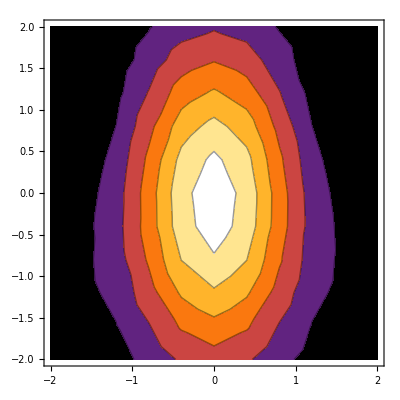

```mathematica
Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-2,2,0.4},{Z,-2,2,0.4}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,11,1},{j,1,11,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]]]
 
ListContourPlot[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

```mathematica
t=2;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]);
```

```mathematica
NIntegrate[Table[Table[(ψ),{x,-2,2,0.4}],{y,-2,2,0.4}],{px,-3,0,3},{py,-3,3},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

{{-0.0852095-1.14717 ⅈ,-0.262565-0.401611 ⅈ,-0.0217932+0.278598 ⅈ,0.491716+0.41139 ⅈ,0.980345+0.116367 ⅈ,1.17763-0.079294 ⅈ,0.980345+0.116367 ⅈ,0.491716+0.41139 ⅈ,-0.0217932+0.278598 ⅈ,-0.262565-0.401611 ⅈ,-0.0852095-1.14717 ⅈ},{-0.417836-1.21158 ⅈ,-0.467249-0.198342 ⅈ,0.00295681+0.646365 ⅈ,0.696544+0.753375 ⅈ,1.25906+0.325018 ⅈ,1.46859+0.0567605 ⅈ,1.25906+0.325018 ⅈ,0.696544+0.753375 ⅈ,0.00295681+0.646365 ⅈ,-0.467249-0.198342 ⅈ,-0.417836-1.21158 ⅈ},{-0.739025-1.20963 ⅈ,-0.629415+0.0454327 ⅈ,0.0843351+1.02013 ⅈ,0.950438+1.08404 ⅈ,1.5698+0.524593 ⅈ,1.7831+0.188108 ⅈ,1.5698+0.524593 ⅈ,0.950438+1.08404 ⅈ,0.0843351+1.02013 ⅈ,-0.629415+0.0454327 ⅈ,-0.739025-1.20963 ⅈ},{-1.00416-1.16946 ⅈ,-0.74024+0.275774 ⅈ,0.189543+1.34008 ⅈ,1.19844+1.35637 ⅈ,1.85656+0.686128 ⅈ,2.06827+0.293949 ⅈ,1.85656+0.686128 ⅈ,1.19844+1.35637 ⅈ,0.189543+1.34008 ⅈ,-0.74024+0.275774 ⅈ,-1.00416-1.16946 ⅈ},{-1.17791-1.12612 ⅈ,-0.802172+0.439732 ⅈ,0.276327+1.55483 ⅈ,1.37933+1.53425 ⅈ,2.05941+0.789894 ⅈ,2.26805+0.361336 ⅈ,2.05941+0.789894 ⅈ,1.37933+1.53425 ⅈ,0.276327+1.55483 ⅈ,-0.802172+0.439732 ⅈ,-1.17791-1.12612 ⅈ},{-1.23829-1.10805 ⅈ,-0.821746+0.499025 ⅈ,0.309749+1.63035 ⅈ,1.44559+1.59593 ⅈ,2.13271+0.825509 ⅈ,2.33991+0.384314 ⅈ,2.13271+0.825509 ⅈ,1.44559+1.59593 ⅈ,0.309749+1.63035 ⅈ,-0.821746+0.499025 ⅈ,-1.23829-1.10805 ⅈ},{-1.17791-1.12612 ⅈ,-0.802172+0.439732 ⅈ,0.276327+1.55483 ⅈ,1.37933+1.53425 ⅈ,2.05941+0.789894 ⅈ,2.26805+0.361336 ⅈ,2.05941+0.789894 ⅈ,1.37933+1.53425 ⅈ,0.276327+1.55483 ⅈ,-0.802172+0.439732 ⅈ,-1.17791-1.12612 ⅈ},{-1.00416-1.16946 ⅈ,-0.74024+0.275774 ⅈ,0.189543+1.34008 ⅈ,1.19844+1.35637 ⅈ,1.85656+0.686128 ⅈ,2.06827+0.293949 ⅈ,1.85656+0.686128 ⅈ,1.19844+1.35637 ⅈ,0.189543+1.34008 ⅈ,-0.74024+0.275774 ⅈ,-1.00416-1.16946 ⅈ},{-0.739025-1.20963 ⅈ,-0.629415+0.0454327 ⅈ,0.0843351+1.02013 ⅈ,0.950438+1.08404 ⅈ,1.5698+0.524593 ⅈ,1.7831+0.188108 ⅈ,1.5698+0.524593 ⅈ,0.950438+1.08404 ⅈ,0.0843351+1.02013 ⅈ,-0.629415+0.0454327 ⅈ,-0.739025-1.20963 ⅈ},{-0.417836-1.21158 ⅈ,-0.467249-0.198342 ⅈ,0.00295681+0.646365 ⅈ,0.696544+0.753375 ⅈ,1.25906+0.325018 ⅈ,1.46859+0.0567605 ⅈ,1.25906+0.325018 ⅈ,0.696544+0.753375 ⅈ,0.00295681+0.646365 ⅈ,-0.467249-0.198342 ⅈ,-0.417836-1.21158 ⅈ},{-0.0852095-1.14717 ⅈ,-0.262565-0.401611 ⅈ,-0.0217932+0.278598 ⅈ,0.491716+0.41139 ⅈ,0.980345+0.116367 ⅈ,1.17763-0.079294 ⅈ,0.980345+0.116367 ⅈ,0.491716+0.41139 ⅈ,-0.0217932+0.278598 ⅈ,-0.262565-0.401611 ⅈ,-0.0852095-1.14717 ⅈ}}

{{1.32326,0.230232,0.078092,0.411026,0.974617,1.39309,0.974617,0.411026,0.078092,0.230232,1.32326},{1.64252,0.257661,0.417796,1.05275,1.69086,2.15996,1.69086,1.05275,0.417796,0.257661,1.64252},{2.00936,0.398228,1.04779,2.07848,2.73946,3.21482,2.73946,2.07848,1.04779,0.398228,2.00936},{2.37599,0.624007,1.83174,3.276,3.91757,4.36414,3.91757,3.276,1.83174,0.624007,2.37599},{2.65563,0.836845,2.49384,4.25649,4.86511,5.2746,4.86511,4.25649,2.49384,0.836845,2.65563},{2.76112,0.924291,2.75399,4.6367,5.22991,5.6229,5.22991,4.6367,2.75399,0.924291,2.76112},{2.65563,0.836845,2.49384,4.25649,4.86511,5.2746,4.86511,4.25649,2.49384,0.836845,2.65563},{2.37599,0.624007,1.83174,3.276,3.91757,4.36414,3.91757,3.276,1.83174,0.624007,2.37599},{2.00936,0.398228,1.04779,2.07848,2.73946,3.21482,2.73946,2.07848,1.04779,0.398228,2.00936},{1.64252,0.257661,0.417796,1.05275,1.69086,2.15996,1.69086,1.05275,0.417796,0.257661,1.64252},{1.32326,0.230232,0.078092,0.411026,0.974617,1.39309,0.974617,0.411026,0.078092,0.230232,1.32326}}

{{1.32326,0.230232,0.078092,0.411026,0.974617,1.39309,0.974617,0.411026,0.078092,0.230232,1.32326},{1.64252,0.257661,0.417796,1.05275,1.69086,2.15996,1.69086,1.05275,0.417796,0.257661,1.64252},{2.00936,0.398228,1.04779,2.07848,2.73946,3.21482,2.73946,2.07848,1.04779,0.398228,2.00936},{2.37599,0.624007,1.83174,3.276,3.91757,4.36414,3.91757,3.276,1.83174,0.624007,2.37599},{2.65563,0.836845,2.49384,4.25649,4.86511,5.2746,4.86511,4.25649,2.49384,0.836845,2.65563},{2.76112,0.924291,2.75399,4.6367,5.22991,5.6229,5.22991,4.6367,2.75399,0.924291,2.76112},{2.65563,0.836845,2.49384,4.25649,4.86511,5.2746,4.86511,4.25649,2.49384,0.836845,2.65563},{2.37599,0.624007,1.83174,3.276,3.91757,4.36414,3.91757,3.276,1.83174,0.624007,2.37599},{2.00936,0.398228,1.04779,2.07848,2.73946,3.21482,2.73946,2.07848,1.04779,0.398228,2.00936},{1.64252,0.257661,0.417796,1.05275,1.69086,2.15996,1.69086,1.05275,0.417796,0.257661,1.64252},{1.32326,0.230232,0.078092,0.411026,0.974617,1.39309,0.974617,0.411026,0.078092,0.230232,1.32326}}

{{-2.,-2.,1.32326},{-2.,-1.6,1.64252},{-2.,-1.2,2.00936},{-2.,-0.8,2.37599},{-2.,-0.4,2.65563},{-2.,1.11022×10^-16,2.76112},{-2.,0.4,2.65563},{-2.,0.8,2.37599},{-2.,1.2,2.00936},{-2.,1.6,1.64252},{-2.,2.,1.32326},{-1.6,-2.,0.230232},{-1.6,-1.6,0.257661},{-1.6,-1.2,0.398228},{-1.6,-0.8,0.624007},{-1.6,-0.4,0.836845},{-1.6,1.11022×10^-16,0.924291},{-1.6,0.4,0.836845},{-1.6,0.8,0.624007},{-1.6,1.2,0.398228},{-1.6,1.6,0.257661},{-1.6,2.,0.230232},{-1.2,-2.,0.078092},{-1.2,-1.6,0.417796},{-1.2,-1.2,1.04779},{-1.2,-0.8,1.83174},{-1.2,-0.4,2.49384},{-1.2,1.11022×10^-16,2.75399},{-1.2,0.4,2.49384},{-1.2,0.8,1.83174},{-1.2,1.2,1.04779},{-1.2,1.6,0.417796},{-1.2,2.,0.078092},{-0.8,-2.,0.411026},{-0.8,-1.6,1.05275},{-0.8,-1.2,2.07848},{-0.8,-0.8,3.276},{-0.8,-0.4,4.25649},{-0.8,1.11022×10^-16,4.6367},{-0.8,0.4,4.25649},{-0.8,0.8,3.276},{-0.8,1.2,2.07848},{-0.8,1.6,1.05275},{-0.8,2.,0.411026},{-0.4,-2.,0.974617},{-0.4,-1.6,1.69086},{-0.4,-1.2,2.73946},{-0.4,-0.8,3.91757},{-0.4,-0.4,4.86511},{-0.4,1.11022×10^-16,5.22991},{-0.4,0.4,4.86511},{-0.4,0.8,3.91757},{-0.4,1.2,2.73946},{-0.4,1.6,1.69086},{-0.4,2.,0.974617},{1.11022×10^-16,-2.,1.39309},{1.11022×10^-16,-1.6,2.15996},{1.11022×10^-16,-1.2,3.21482},{1.11022×10^-16,-0.8,4.36414},{1.11022×10^-16,-0.4,5.2746},{1.11022×10^-16,1.11022×10^-16,5.6229},{1.11022×10^-16,0.4,5.2746},{1.11022×10^-16,0.8,4.36414},{1.11022×10^-16,1.2,3.21482},{1.11022×10^-16,1.6,2.15996},{1.11022×10^-16,2.,1.39309},{0.4,-2.,0.974617},{0.4,-1.6,1.69086},{0.4,-1.2,2.73946},{0.4,-0.8,3.91757},{0.4,-0.4,4.86511},{0.4,1.11022×10^-16,5.22991},{0.4,0.4,4.86511},{0.4,0.8,3.91757},{0.4,1.2,2.73946},{0.4,1.6,1.69086},{0.4,2.,0.974617},{0.8,-2.,0.411026},{0.8,-1.6,1.05275},{0.8,-1.2,2.07848},{0.8,-0.8,3.276},{0.8,-0.4,4.25649},{0.8,1.11022×10^-16,4.6367},{0.8,0.4,4.25649},{0.8,0.8,3.276},{0.8,1.2,2.07848},{0.8,1.6,1.05275},{0.8,2.,0.411026},{1.2,-2.,0.078092},{1.2,-1.6,0.417796},{1.2,-1.2,1.04779},{1.2,-0.8,1.83174},{1.2,-0.4,2.49384},{1.2,1.11022×10^-16,2.75399},{1.2,0.4,2.49384},{1.2,0.8,1.83174},{1.2,1.2,1.04779},{1.2,1.6,0.417796},{1.2,2.,0.078092},{1.6,-2.,0.230232},{1.6,-1.6,0.257661},{1.6,-1.2,0.398228},{1.6,-0.8,0.624007},{1.6,-0.4,0.836845},{1.6,1.11022×10^-16,0.924291},{1.6,0.4,0.836845},{1.6,0.8,0.624007},{1.6,1.2,0.398228},{1.6,1.6,0.257661},{1.6,2.,0.230232},{2.,-2.,1.32326},{2.,-1.6,1.64252},{2.,-1.2,2.00936},{2.,-0.8,2.37599},{2.,-0.4,2.65563},{2.,1.11022×10^-16,2.76112},{2.,0.4,2.65563},{2.,0.8,2.37599},{2.,1.2,2.00936},{2.,1.6,1.64252},{2.,2.,1.32326}}

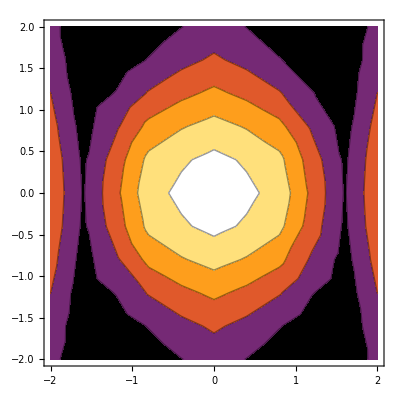

```mathematica
Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-2,2,0.4},{Z,-2,2,0.4}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,11,1},{j,1,11,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

```mathematica
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

-Graphics3D-

```mathematica
t=4;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]);
```

```mathematica
NIntegrate[Table[Table[(ψ),{x,-2,2,0.4}],{y,-2,2,0.4}],{px,-3,0,3},{py,-3,3},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.25046-0.263665 ⅈ,-0.251974+0.00310838 ⅈ,-0.145393+0.249131 ⅈ,-0.0772+0.58357 ⅈ,-0.0807752+0.940425 ⅈ,-0.0956468+1.10023 ⅈ,-0.0807752+0.940425 ⅈ,-0.0772+0.58357 ⅈ,-0.145393+0.249131 ⅈ,-0.251974+0.00310838 ⅈ,-0.25046-0.263665 ⅈ},{-0.391283-0.17404 ⅈ,-0.383531+0.178785 ⅈ,-0.246492+0.493116 ⅈ,-0.121285+0.901161 ⅈ,-0.0617811+1.32753 ⅈ,-0.0484592+1.51713 ⅈ,-0.0617811+1.32753 ⅈ,-0.121285+0.901161 ⅈ,-0.246492+0.493116 ⅈ,-0.383531+0.178785 ⅈ,-0.391283-0.17404 ⅈ},{-0.520841-0.0709451 ⅈ,-0.496185+0.364076 ⅈ,-0.324247+0.74215 ⅈ,-0.139908+1.21302 ⅈ,-0.0167536+1.69515 ⅈ,0.0247796+1.90807 ⅈ,-0.0167536+1.69515 ⅈ,-0.139908+1.21302 ⅈ,-0.324247+0.74215 ⅈ,-0.496185+0.364076 ⅈ,-0.520841-0.0709451 ⅈ},{-0.62418+0.025312 ⅈ,-0.580406+0.528002 ⅈ,-0.375837+0.95759 ⅈ,-0.139862+1.47594 ⅈ,0.0376381+1.99808 ⅈ,0.103084+2.22737 ⅈ,0.0376381+1.99808 ⅈ,-0.139862+1.47594 ⅈ,-0.375837+0.95759 ⅈ,-0.580406+0.528002 ⅈ,-0.62418+0.025312 ⅈ},{-0.690399+0.0936646 ⅈ,-0.631715+0.640737 ⅈ,-0.403929+1.10368 ⅈ,-0.132752+1.6514 ⅈ,0.0812254+2.19736 ⅈ,0.162638+2.43624 ⅈ,0.0812254+2.19736 ⅈ,-0.132752+1.6514 ⅈ,-0.403929+1.10368 ⅈ,-0.631715+0.640737 ⅈ,-0.690399+0.0936646 ⅈ},{-0.713154+0.118385 ⅈ,-0.648858+0.680899 ⅈ,-0.412667+1.15536 ⅈ,-0.129003+1.71301 ⅈ,0.097811+2.26684 ⅈ,0.184827+2.50886 ⅈ,0.097811+2.26684 ⅈ,-0.129003+1.71301 ⅈ,-0.412667+1.15536 ⅈ,-0.648858+0.680899 ⅈ,-0.713154+0.118385 ⅈ},{-0.690399+0.0936646 ⅈ,-0.631715+0.640737 ⅈ,-0.403929+1.10368 ⅈ,-0.132752+1.6514 ⅈ,0.0812254+2.19736 ⅈ,0.162638+2.43624 ⅈ,0.0812254+2.19736 ⅈ,-0.132752+1.6514 ⅈ,-0.403929+1.10368 ⅈ,-0.631715+0.640737 ⅈ,-0.690399+0.0936646 ⅈ},{-0.62418+0.025312 ⅈ,-0.580406+0.528002 ⅈ,-0.375837+0.95759 ⅈ,-0.139862+1.47594 ⅈ,0.0376381+1.99808 ⅈ,0.103084+2.22737 ⅈ,0.0376381+1.99808 ⅈ,-0.139862+1.47594 ⅈ,-0.375837+0.95759 ⅈ,-0.580406+0.528002 ⅈ,-0.62418+0.025312 ⅈ},{-0.520841-0.0709451 ⅈ,-0.496185+0.364076 ⅈ,-0.324247+0.74215 ⅈ,-0.139908+1.21302 ⅈ,-0.0167536+1.69515 ⅈ,0.0247796+1.90807 ⅈ,-0.0167536+1.69515 ⅈ,-0.139908+1.21302 ⅈ,-0.324247+0.74215 ⅈ,-0.496185+0.364076 ⅈ,-0.520841-0.0709451 ⅈ},{-0.391283-0.17404 ⅈ,-0.383531+0.178785 ⅈ,-0.246492+0.493116 ⅈ,-0.121285+0.901161 ⅈ,-0.0617811+1.32753 ⅈ,-0.0484592+1.51713 ⅈ,-0.0617811+1.32753 ⅈ,-0.121285+0.901161 ⅈ,-0.246492+0.493116 ⅈ,-0.383531+0.178785 ⅈ,-0.391283-0.17404 ⅈ},{-0.25046-0.263665 ⅈ,-0.251974+0.00310838 ⅈ,-0.145393+0.249131 ⅈ,-0.0772+0.58357 ⅈ,-0.0807752+0.940425 ⅈ,-0.0956468+1.10023 ⅈ,-0.0807752+0.940425 ⅈ,-0.0772+0.58357 ⅈ,-0.145393+0.249131 ⅈ,-0.251974+0.00310838 ⅈ,-0.25046-0.263665 ⅈ}}

```mathematica
Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-2,2,0.4},{Z,-2,2,0.4}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,11,1},{j,1,11,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

{{0.132249,0.0635004,0.0832055,0.346514,0.890923,1.21966,0.890923,0.346514,0.0832055,0.0635004,0.132249},{0.183393,0.17906,0.303922,0.826801,1.76615,2.30404,1.76615,0.826801,0.303922,0.17906,0.183393},{0.276308,0.378751,0.655923,1.49099,2.8738,3.64135,2.8738,1.49099,0.655923,0.378751,0.276308},{0.390241,0.615657,1.05823,2.19796,3.99373,4.97181,3.99373,2.19796,1.05823,0.615657,0.390241},{0.485424,0.809607,1.38126,2.74475,4.83497,5.9617,4.83497,2.74475,1.38126,0.809607,0.485424},{0.522604,0.88464,1.50516,2.95104,5.14815,6.32856,5.14815,2.95104,1.50516,0.88464,0.522604},{0.485424,0.809607,1.38126,2.74475,4.83497,5.9617,4.83497,2.74475,1.38126,0.809607,0.485424},{0.390241,0.615657,1.05823,2.19796,3.99373,4.97181,3.99373,2.19796,1.05823,0.615657,0.390241},{0.276308,0.378751,0.655923,1.49099,2.8738,3.64135,2.8738,1.49099,0.655923,0.378751,0.276308},{0.183393,0.17906,0.303922,0.826801,1.76615,2.30404,1.76615,0.826801,0.303922,0.17906,0.183393},{0.132249,0.0635004,0.0832055,0.346514,0.890923,1.21966,0.890923,0.346514,0.0832055,0.0635004,0.132249}}

{{0.132249,0.0635004,0.0832055,0.346514,0.890923,1.21966,0.890923,0.346514,0.0832055,0.0635004,0.132249},{0.183393,0.17906,0.303922,0.826801,1.76615,2.30404,1.76615,0.826801,0.303922,0.17906,0.183393},{0.276308,0.378751,0.655923,1.49099,2.8738,3.64135,2.8738,1.49099,0.655923,0.378751,0.276308},{0.390241,0.615657,1.05823,2.19796,3.99373,4.97181,3.99373,2.19796,1.05823,0.615657,0.390241},{0.485424,0.809607,1.38126,2.74475,4.83497,5.9617,4.83497,2.74475,1.38126,0.809607,0.485424},{0.522604,0.88464,1.50516,2.95104,5.14815,6.32856,5.14815,2.95104,1.50516,0.88464,0.522604},{0.485424,0.809607,1.38126,2.74475,4.83497,5.9617,4.83497,2.74475,1.38126,0.809607,0.485424},{0.390241,0.615657,1.05823,2.19796,3.99373,4.97181,3.99373,2.19796,1.05823,0.615657,0.390241},{0.276308,0.378751,0.655923,1.49099,2.8738,3.64135,2.8738,1.49099,0.655923,0.378751,0.276308},{0.183393,0.17906,0.303922,0.826801,1.76615,2.30404,1.76615,0.826801,0.303922,0.17906,0.183393},{0.132249,0.0635004,0.0832055,0.346514,0.890923,1.21966,0.890923,0.346514,0.0832055,0.0635004,0.132249}}

{{-2.,-2.,0.132249},{-2.,-1.6,0.183393},{-2.,-1.2,0.276308},{-2.,-0.8,0.390241},{-2.,-0.4,0.485424},{-2.,1.11022×10^-16,0.522604},{-2.,0.4,0.485424},{-2.,0.8,0.390241},{-2.,1.2,0.276308},{-2.,1.6,0.183393},{-2.,2.,0.132249},{-1.6,-2.,0.0635004},{-1.6,-1.6,0.17906},{-1.6,-1.2,0.378751},{-1.6,-0.8,0.615657},{-1.6,-0.4,0.809607},{-1.6,1.11022×10^-16,0.88464},{-1.6,0.4,0.809607},{-1.6,0.8,0.615657},{-1.6,1.2,0.378751},{-1.6,1.6,0.17906},{-1.6,2.,0.0635004},{-1.2,-2.,0.0832055},{-1.2,-1.6,0.303922},{-1.2,-1.2,0.655923},{-1.2,-0.8,1.05823},{-1.2,-0.4,1.38126},{-1.2,1.11022×10^-16,1.50516},{-1.2,0.4,1.38126},{-1.2,0.8,1.05823},{-1.2,1.2,0.655923},{-1.2,1.6,0.303922},{-1.2,2.,0.0832055},{-0.8,-2.,0.346514},{-0.8,-1.6,0.826801},{-0.8,-1.2,1.49099},{-0.8,-0.8,2.19796},{-0.8,-0.4,2.74475},{-0.8,1.11022×10^-16,2.95104},{-0.8,0.4,2.74475},{-0.8,0.8,2.19796},{-0.8,1.2,1.49099},{-0.8,1.6,0.826801},{-0.8,2.,0.346514},{-0.4,-2.,0.890923},{-0.4,-1.6,1.76615},{-0.4,-1.2,2.8738},{-0.4,-0.8,3.99373},{-0.4,-0.4,4.83497},{-0.4,1.11022×10^-16,5.14815},{-0.4,0.4,4.83497},{-0.4,0.8,3.99373},{-0.4,1.2,2.8738},{-0.4,1.6,1.76615},{-0.4,2.,0.890923},{1.11022×10^-16,-2.,1.21966},{1.11022×10^-16,-1.6,2.30404},{1.11022×10^-16,-1.2,3.64135},{1.11022×10^-16,-0.8,4.97181},{1.11022×10^-16,-0.4,5.9617},{1.11022×10^-16,1.11022×10^-16,6.32856},{1.11022×10^-16,0.4,5.9617},{1.11022×10^-16,0.8,4.97181},{1.11022×10^-16,1.2,3.64135},{1.11022×10^-16,1.6,2.30404},{1.11022×10^-16,2.,1.21966},{0.4,-2.,0.890923},{0.4,-1.6,1.76615},{0.4,-1.2,2.8738},{0.4,-0.8,3.99373},{0.4,-0.4,4.83497},{0.4,1.11022×10^-16,5.14815},{0.4,0.4,4.83497},{0.4,0.8,3.99373},{0.4,1.2,2.8738},{0.4,1.6,1.76615},{0.4,2.,0.890923},{0.8,-2.,0.346514},{0.8,-1.6,0.826801},{0.8,-1.2,1.49099},{0.8,-0.8,2.19796},{0.8,-0.4,2.74475},{0.8,1.11022×10^-16,2.95104},{0.8,0.4,2.74475},{0.8,0.8,2.19796},{0.8,1.2,1.49099},{0.8,1.6,0.826801},{0.8,2.,0.346514},{1.2,-2.,0.0832055},{1.2,-1.6,0.303922},{1.2,-1.2,0.655923},{1.2,-0.8,1.05823},{1.2,-0.4,1.38126},{1.2,1.11022×10^-16,1.50516},{1.2,0.4,1.38126},{1.2,0.8,1.05823},{1.2,1.2,0.655923},{1.2,1.6,0.303922},{1.2,2.,0.0832055},{1.6,-2.,0.0635004},{1.6,-1.6,0.17906},{1.6,-1.2,0.378751},{1.6,-0.8,0.615657},{1.6,-0.4,0.809607},{1.6,1.11022×10^-16,0.88464},{1.6,0.4,0.809607},{1.6,0.8,0.615657},{1.6,1.2,0.378751},{1.6,1.6,0.17906},{1.6,2.,0.0635004},{2.,-2.,0.132249},{2.,-1.6,0.183393},{2.,-1.2,0.276308},{2.,-0.8,0.390241},{2.,-0.4,0.485424},{2.,1.11022×10^-16,0.522604},{2.,0.4,0.485424},{2.,0.8,0.390241},{2.,1.2,0.276308},{2.,1.6,0.183393},{2.,2.,0.132249}}

-Graphics3D-

```mathematica
t=4;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]);
```

```mathematica
NIntegrate[Table[Table[(ψ),{x,-5,5,1}],{y,-5,5,1}],{px,-5,0,5},{py,-5,5},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0957916-0.0257819 ⅈ,0.0602854-0.0584816 ⅈ,0.0507708-0.0566181 ⅈ,0.0517183-0.0602453 ⅈ,0.0483169-0.0597182 ⅈ,0.0466836-0.0573967 ⅈ,0.0483169-0.0597182 ⅈ,0.0517183-0.0602453 ⅈ,0.0507708-0.0566181 ⅈ,0.0602854-0.0584816 ⅈ,0.0957916-0.0257819 ⅈ},{0.0696822-0.094081 ⅈ,0.0214545-0.0578717 ⅈ,0.0570895-0.0521131 ⅈ,0.0553156-0.070596 ⅈ,0.0393175-0.0548276 ⅈ,0.0360279-0.0406982 ⅈ,0.0393175-0.0548276 ⅈ,0.0553156-0.070596 ⅈ,0.0570895-0.0521131 ⅈ,0.0214545-0.0578717 ⅈ,0.0696822-0.094081 ⅈ},{-0.0132693-0.120953 ⅈ,0.0225718-0.00756546 ⅈ,0.0987199-0.0756939 ⅈ,0.0383743-0.094642 ⅈ,0.00395025-0.00818786 ⅈ,0.00835161+0.0406335 ⅈ,0.00395025-0.00818786 ⅈ,0.0383743-0.094642 ⅈ,0.0987199-0.0756939 ⅈ,0.0225718-0.00756546 ⅈ,-0.0132693-0.120953 ⅈ},{-0.100274-0.0771054 ⅈ,0.0867206+0.0371612 ⅈ,0.124214-0.149283 ⅈ,-0.0318376-0.0960728 ⅈ,-0.0447205+0.123897 ⅈ,-0.00588211+0.223988 ⅈ,-0.0447205+0.123897 ⅈ,-0.0318376-0.0960728 ⅈ,0.124214-0.149283 ⅈ,0.0867206+0.0371612 ⅈ,-0.100274-0.0771054 ⅈ},{-0.146293-0.00640258 ⅈ,0.164389+0.0444956 ⅈ,0.110202-0.226275 ⅈ,-0.116063-0.0575502 ⅈ,-0.0664096+0.292892 ⅈ,0.0211177+0.434951 ⅈ,-0.0664096+0.292892 ⅈ,-0.116063-0.0575502 ⅈ,0.110202-0.226275 ⅈ,0.164389+0.0444956 ⅈ,-0.146293-0.00640258 ⅈ},{-0.157069+0.0261613 ⅈ,0.197243+0.0395648 ⅈ,0.0957644-0.257022 ⅈ,-0.152261-0.0315316 ⅈ,-0.0671118+0.371681 ⅈ,0.0438763+0.52891 ⅈ,-0.0671118+0.371681 ⅈ,-0.152261-0.0315316 ⅈ,0.0957644-0.257022 ⅈ,0.197243+0.0395648 ⅈ,-0.157069+0.0261613 ⅈ},{-0.146293-0.00640258 ⅈ,0.164389+0.0444956 ⅈ,0.110202-0.226275 ⅈ,-0.116063-0.0575502 ⅈ,-0.0664096+0.292892 ⅈ,0.0211177+0.434951 ⅈ,-0.0664096+0.292892 ⅈ,-0.116063-0.0575502 ⅈ,0.110202-0.226275 ⅈ,0.164389+0.0444956 ⅈ,-0.146293-0.00640258 ⅈ},{-0.100274-0.0771054 ⅈ,0.0867206+0.0371612 ⅈ,0.124214-0.149283 ⅈ,-0.0318376-0.0960728 ⅈ,-0.0447205+0.123897 ⅈ,-0.00588211+0.223988 ⅈ,-0.0447205+0.123897 ⅈ,-0.0318376-0.0960728 ⅈ,0.124214-0.149283 ⅈ,0.0867206+0.0371612 ⅈ,-0.100274-0.0771054 ⅈ},{-0.0132693-0.120953 ⅈ,0.0225718-0.00756546 ⅈ,0.0987199-0.0756939 ⅈ,0.0383743-0.094642 ⅈ,0.00395025-0.00818786 ⅈ,0.00835161+0.0406335 ⅈ,0.00395025-0.00818786 ⅈ,0.0383743-0.094642 ⅈ,0.0987199-0.0756939 ⅈ,0.0225718-0.00756546 ⅈ,-0.0132693-0.120953 ⅈ},{0.0696822-0.094081 ⅈ,0.0214545-0.0578717 ⅈ,0.0570895-0.0521131 ⅈ,0.0553156-0.070596 ⅈ,0.0393175-0.0548276 ⅈ,0.0360279-0.0406982 ⅈ,0.0393175-0.0548276 ⅈ,0.0553156-0.070596 ⅈ,0.0570895-0.0521131 ⅈ,0.0214545-0.0578717 ⅈ,0.0696822-0.094081 ⅈ},{0.0957916-0.0257819 ⅈ,0.0602854-0.0584816 ⅈ,0.0507708-0.0566181 ⅈ,0.0517183-0.0602453 ⅈ,0.0483169-0.0597182 ⅈ,0.0466836-0.0573967 ⅈ,0.0483169-0.0597182 ⅈ,0.0517183-0.0602453 ⅈ,0.0507708-0.0566181 ⅈ,0.0602854-0.0584816 ⅈ,0.0957916-0.0257819 ⅈ}}

{{0.00984073,0.00705443,0.00578328,0.00630429,0.00590079,0.00547374,0.00590079,0.00630429,0.00578328,0.00705443,0.00984073},{0.0137068,0.00380943,0.00597499,0.0080436,0.00455193,0.00295436,0.00455193,0.0080436,0.00597499,0.00380943,0.0137068},{0.0148058,0.000566724,0.0154752,0.0104297,0.0000826455,0.00172083,0.0000826455,0.0104297,0.0154752,0.000566724,0.0148058},{0.0160001,0.00890141,0.0377146,0.0102436,0.0173503,0.050205,0.0173503,0.0102436,0.0377146,0.00890141,0.0160001},{0.0214426,0.0290035,0.063345,0.0167826,0.0901958,0.189629,0.0901958,0.0167826,0.063345,0.0290035,0.0214426},{0.0253549,0.0404703,0.0752313,0.0241776,0.14265,0.281671,0.14265,0.0241776,0.0752313,0.0404703,0.0253549},{0.0214426,0.0290035,0.063345,0.0167826,0.0901958,0.189629,0.0901958,0.0167826,0.063345,0.0290035,0.0214426},{0.0160001,0.00890141,0.0377146,0.0102436,0.0173503,0.050205,0.0173503,0.0102436,0.0377146,0.00890141,0.0160001},{0.0148058,0.000566724,0.0154752,0.0104297,0.0000826455,0.00172083,0.0000826455,0.0104297,0.0154752,0.000566724,0.0148058},{0.0137068,0.00380943,0.00597499,0.0080436,0.00455193,0.00295436,0.00455193,0.0080436,0.00597499,0.00380943,0.0137068},{0.00984073,0.00705443,0.00578328,0.00630429,0.00590079,0.00547374,0.00590079,0.00630429,0.00578328,0.00705443,0.00984073}}

{{0.00984073,0.00705443,0.00578328,0.00630429,0.00590079,0.00547374,0.00590079,0.00630429,0.00578328,0.00705443,0.00984073},{0.0137068,0.00380943,0.00597499,0.0080436,0.00455193,0.00295436,0.00455193,0.0080436,0.00597499,0.00380943,0.0137068},{0.0148058,0.000566724,0.0154752,0.0104297,0.0000826455,0.00172083,0.0000826455,0.0104297,0.0154752,0.000566724,0.0148058},{0.0160001,0.00890141,0.0377146,0.0102436,0.0173503,0.050205,0.0173503,0.0102436,0.0377146,0.00890141,0.0160001},{0.0214426,0.0290035,0.063345,0.0167826,0.0901958,0.189629,0.0901958,0.0167826,0.063345,0.0290035,0.0214426},{0.0253549,0.0404703,0.0752313,0.0241776,0.14265,0.281671,0.14265,0.0241776,0.0752313,0.0404703,0.0253549},{0.0214426,0.0290035,0.063345,0.0167826,0.0901958,0.189629,0.0901958,0.0167826,0.063345,0.0290035,0.0214426},{0.0160001,0.00890141,0.0377146,0.0102436,0.0173503,0.050205,0.0173503,0.0102436,0.0377146,0.00890141,0.0160001},{0.0148058,0.000566724,0.0154752,0.0104297,0.0000826455,0.00172083,0.0000826455,0.0104297,0.0154752,0.000566724,0.0148058},{0.0137068,0.00380943,0.00597499,0.0080436,0.00455193,0.00295436,0.00455193,0.0080436,0.00597499,0.00380943,0.0137068},{0.00984073,0.00705443,0.00578328,0.00630429,0.00590079,0.00547374,0.00590079,0.00630429,0.00578328,0.00705443,0.00984073}}

{{-2.,-2.,0.00984073},{-2.,-1.6,0.0137068},{-2.,-1.2,0.0148058},{-2.,-0.8,0.0160001},{-2.,-0.4,0.0214426},{-2.,1.11022×10^-16,0.0253549},{-2.,0.4,0.0214426},{-2.,0.8,0.0160001},{-2.,1.2,0.0148058},{-2.,1.6,0.0137068},{-2.,2.,0.00984073},{-1.6,-2.,0.00705443},{-1.6,-1.6,0.00380943},{-1.6,-1.2,0.000566724},{-1.6,-0.8,0.00890141},{-1.6,-0.4,0.0290035},{-1.6,1.11022×10^-16,0.0404703},{-1.6,0.4,0.0290035},{-1.6,0.8,0.00890141},{-1.6,1.2,0.000566724},{-1.6,1.6,0.00380943},{-1.6,2.,0.00705443},{-1.2,-2.,0.00578328},{-1.2,-1.6,0.00597499},{-1.2,-1.2,0.0154752},{-1.2,-0.8,0.0377146},{-1.2,-0.4,0.063345},{-1.2,1.11022×10^-16,0.0752313},{-1.2,0.4,0.063345},{-1.2,0.8,0.0377146},{-1.2,1.2,0.0154752},{-1.2,1.6,0.00597499},{-1.2,2.,0.00578328},{-0.8,-2.,0.00630429},{-0.8,-1.6,0.0080436},{-0.8,-1.2,0.0104297},{-0.8,-0.8,0.0102436},{-0.8,-0.4,0.0167826},{-0.8,1.11022×10^-16,0.0241776},{-0.8,0.4,0.0167826},{-0.8,0.8,0.0102436},{-0.8,1.2,0.0104297},{-0.8,1.6,0.0080436},{-0.8,2.,0.00630429},{-0.4,-2.,0.00590079},{-0.4,-1.6,0.00455193},{-0.4,-1.2,0.0000826455},{-0.4,-0.8,0.0173503},{-0.4,-0.4,0.0901958},{-0.4,1.11022×10^-16,0.14265},{-0.4,0.4,0.0901958},{-0.4,0.8,0.0173503},{-0.4,1.2,0.0000826455},{-0.4,1.6,0.00455193},{-0.4,2.,0.00590079},{1.11022×10^-16,-2.,0.00547374},{1.11022×10^-16,-1.6,0.00295436},{1.11022×10^-16,-1.2,0.00172083},{1.11022×10^-16,-0.8,0.050205},{1.11022×10^-16,-0.4,0.189629},{1.11022×10^-16,1.11022×10^-16,0.281671},{1.11022×10^-16,0.4,0.189629},{1.11022×10^-16,0.8,0.050205},{1.11022×10^-16,1.2,0.00172083},{1.11022×10^-16,1.6,0.00295436},{1.11022×10^-16,2.,0.00547374},{0.4,-2.,0.00590079},{0.4,-1.6,0.00455193},{0.4,-1.2,0.0000826455},{0.4,-0.8,0.0173503},{0.4,-0.4,0.0901958},{0.4,1.11022×10^-16,0.14265},{0.4,0.4,0.0901958},{0.4,0.8,0.0173503},{0.4,1.2,0.0000826455},{0.4,1.6,0.00455193},{0.4,2.,0.00590079},{0.8,-2.,0.00630429},{0.8,-1.6,0.0080436},{0.8,-1.2,0.0104297},{0.8,-0.8,0.0102436},{0.8,-0.4,0.0167826},{0.8,1.11022×10^-16,0.0241776},{0.8,0.4,0.0167826},{0.8,0.8,0.0102436},{0.8,1.2,0.0104297},{0.8,1.6,0.0080436},{0.8,2.,0.00630429},{1.2,-2.,0.00578328},{1.2,-1.6,0.00597499},{1.2,-1.2,0.0154752},{1.2,-0.8,0.0377146},{1.2,-0.4,0.063345},{1.2,1.11022×10^-16,0.0752313},{1.2,0.4,0.063345},{1.2,0.8,0.0377146},{1.2,1.2,0.0154752},{1.2,1.6,0.00597499},{1.2,2.,0.00578328},{1.6,-2.,0.00705443},{1.6,-1.6,0.00380943},{1.6,-1.2,0.000566724},{1.6,-0.8,0.00890141},{1.6,-0.4,0.0290035},{1.6,1.11022×10^-16,0.0404703},{1.6,0.4,0.0290035},{1.6,0.8,0.00890141},{1.6,1.2,0.000566724},{1.6,1.6,0.00380943},{1.6,2.,0.00705443},{2.,-2.,0.00984073},{2.,-1.6,0.0137068},{2.,-1.2,0.0148058},{2.,-0.8,0.0160001},{2.,-0.4,0.0214426},{2.,1.11022×10^-16,0.0253549},{2.,0.4,0.0214426},{2.,0.8,0.0160001},{2.,1.2,0.0148058},{2.,1.6,0.0137068},{2.,2.,0.00984073}}

-Graphics3D-

```mathematica
t=4.5;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-5,5,1}],{y,-5,5,1}],{px,-5,0,5},{py,-5,5},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-5,5,1},{Z,-5,5,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,11,1},{j,1,11,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0832166-0.0548128 ⅈ,0.0384621-0.0686881 ⅈ,0.0262905-0.0561865 ⅈ,0.0328962-0.0525571 ⅈ,0.0391521-0.0468762 ⅈ,0.0420478-0.0423904 ⅈ,0.0391521-0.0468762 ⅈ,0.0328962-0.0525571 ⅈ,0.0262905-0.0561865 ⅈ,0.0384621-0.0686881 ⅈ,0.0832166-0.0548128 ⅈ},{0.048297-0.107913 ⅈ,0.00507989-0.0498243 ⅈ,0.0375967-0.0318795 ⅈ,0.0446093-0.0475603 ⅈ,0.0409096-0.0364739 ⅈ,0.04268-0.0245089 ⅈ,0.0409096-0.0364739 ⅈ,0.0446093-0.0475603 ⅈ,0.0375967-0.0318795 ⅈ,0.00507989-0.0498243 ⅈ,0.048297-0.107913 ⅈ},{-0.028432-0.119658 ⅈ,0.0192313+0.00633237 ⅈ,0.0889479-0.0370224 ⅈ,0.0379414-0.0616181 ⅈ,0.00488668+0.00159809 ⅈ,0.00740194+0.0412192 ⅈ,0.00488668+0.00159809 ⅈ,0.0379414-0.0616181 ⅈ,0.0889479-0.0370224 ⅈ,0.0192313+0.00633237 ⅈ,-0.028432-0.119658 ⅈ},{-0.0997014-0.0721225 ⅈ,0.0892397+0.0467598 ⅈ,0.128187-0.092838 ⅈ,-0.0222462-0.0616192 ⅈ,-0.0654891+0.115438 ⅈ,-0.0455424+0.201669 ⅈ,-0.0654891+0.115438 ⅈ,-0.0222462-0.0616192 ⅈ,0.128187-0.092838 ⅈ,0.0892397+0.0467598 ⅈ,-0.0997014-0.0721225 ⅈ},{-0.133005-0.0076586 ⅈ,0.164392+0.0500362 ⅈ,0.129048-0.157106 ⅈ,-0.100578-0.0294064 ⅈ,-0.120328+0.267402 ⅈ,-0.0708511+0.396338 ⅈ,-0.120328+0.267402 ⅈ,-0.100578-0.0294064 ⅈ,0.129048-0.157106 ⅈ,0.164392+0.0500362 ⅈ,-0.133005-0.0076586 ⅈ},{-0.139574+0.0206956 ⅈ,0.194918+0.0441607 ⅈ,0.121374-0.18353 ⅈ,-0.135365-0.00761423 ⅈ,-0.137532+0.339622 ⅈ,-0.0729895+0.485292 ⅈ,-0.137532+0.339622 ⅈ,-0.135365-0.00761423 ⅈ,0.121374-0.18353 ⅈ,0.194918+0.0441607 ⅈ,-0.139574+0.0206956 ⅈ},{-0.133005-0.0076586 ⅈ,0.164392+0.0500362 ⅈ,0.129048-0.157106 ⅈ,-0.100578-0.0294064 ⅈ,-0.120328+0.267402 ⅈ,-0.0708511+0.396338 ⅈ,-0.120328+0.267402 ⅈ,-0.100578-0.0294064 ⅈ,0.129048-0.157106 ⅈ,0.164392+0.0500362 ⅈ,-0.133005-0.0076586 ⅈ},{-0.0997014-0.0721225 ⅈ,0.0892397+0.0467598 ⅈ,0.128187-0.092838 ⅈ,-0.0222462-0.0616192 ⅈ,-0.0654891+0.115438 ⅈ,-0.0455424+0.201669 ⅈ,-0.0654891+0.115438 ⅈ,-0.0222462-0.0616192 ⅈ,0.128187-0.092838 ⅈ,0.0892397+0.0467598 ⅈ,-0.0997014-0.0721225 ⅈ},{-0.028432-0.119658 ⅈ,0.0192313+0.00633237 ⅈ,0.0889479-0.0370224 ⅈ,0.0379414-0.0616181 ⅈ,0.00488668+0.00159809 ⅈ,0.00740194+0.0412192 ⅈ,0.00488668+0.00159809 ⅈ,0.0379414-0.0616181 ⅈ,0.0889479-0.0370224 ⅈ,0.0192313+0.00633237 ⅈ,-0.028432-0.119658 ⅈ},{0.048297-0.107913 ⅈ,0.00507989-0.0498243 ⅈ,0.0375967-0.0318795 ⅈ,0.0446093-0.0475603 ⅈ,0.0409096-0.0364739 ⅈ,0.04268-0.0245089 ⅈ,0.0409096-0.0364739 ⅈ,0.0446093-0.0475603 ⅈ,0.0375967-0.0318795 ⅈ,0.00507989-0.0498243 ⅈ,0.048297-0.107913 ⅈ},{0.0832166-0.0548128 ⅈ,0.0384621-0.0686881 ⅈ,0.0262905-0.0561865 ⅈ,0.0328962-0.0525571 ⅈ,0.0391521-0.0468762 ⅈ,0.0420478-0.0423904 ⅈ,0.0391521-0.0468762 ⅈ,0.0328962-0.0525571 ⅈ,0.0262905-0.0561865 ⅈ,0.0384621-0.0686881 ⅈ,0.0832166-0.0548128 ⅈ}}

{{0.00992944,0.00619739,0.00384812,0.0038444,0.00373027,0.00356496,0.00373027,0.0038444,0.00384812,0.00619739,0.00992944},{0.0139778,0.00250826,0.00242981,0.00425197,0.00300394,0.00242227,0.00300394,0.00425197,0.00242981,0.00250826,0.0139778},{0.0151265,0.00040994,0.00928238,0.00523633,0.0000264336,0.00175381,0.0000264336,0.00523633,0.00928238,0.00040994,0.0151265},{0.015142,0.0101502,0.0250507,0.00429181,0.0176147,0.0427445,0.0176147,0.00429181,0.0250507,0.0101502,0.015142},{0.0177491,0.0295283,0.0413356,0.0109807,0.0859826,0.162104,0.0859826,0.0109807,0.0413356,0.0295283,0.0177491},{0.0199092,0.0399434,0.048415,0.0183815,0.134258,0.240836,0.134258,0.0183815,0.048415,0.0399434,0.0199092},{0.0177491,0.0295283,0.0413356,0.0109807,0.0859826,0.162104,0.0859826,0.0109807,0.0413356,0.0295283,0.0177491},{0.015142,0.0101502,0.0250507,0.00429181,0.0176147,0.0427445,0.0176147,0.00429181,0.0250507,0.0101502,0.015142},{0.0151265,0.00040994,0.00928238,0.00523633,0.0000264336,0.00175381,0.0000264336,0.00523633,0.00928238,0.00040994,0.0151265},{0.0139778,0.00250826,0.00242981,0.00425197,0.00300394,0.00242227,0.00300394,0.00425197,0.00242981,0.00250826,0.0139778},{0.00992944,0.00619739,0.00384812,0.0038444,0.00373027,0.00356496,0.00373027,0.0038444,0.00384812,0.00619739,0.00992944}}

{{0.00992944,0.00619739,0.00384812,0.0038444,0.00373027,0.00356496,0.00373027,0.0038444,0.00384812,0.00619739,0.00992944},{0.0139778,0.00250826,0.00242981,0.00425197,0.00300394,0.00242227,0.00300394,0.00425197,0.00242981,0.00250826,0.0139778},{0.0151265,0.00040994,0.00928238,0.00523633,0.0000264336,0.00175381,0.0000264336,0.00523633,0.00928238,0.00040994,0.0151265},{0.015142,0.0101502,0.0250507,0.00429181,0.0176147,0.0427445,0.0176147,0.00429181,0.0250507,0.0101502,0.015142},{0.0177491,0.0295283,0.0413356,0.0109807,0.0859826,0.162104,0.0859826,0.0109807,0.0413356,0.0295283,0.0177491},{0.0199092,0.0399434,0.048415,0.0183815,0.134258,0.240836,0.134258,0.0183815,0.048415,0.0399434,0.0199092},{0.0177491,0.0295283,0.0413356,0.0109807,0.0859826,0.162104,0.0859826,0.0109807,0.0413356,0.0295283,0.0177491},{0.015142,0.0101502,0.0250507,0.00429181,0.0176147,0.0427445,0.0176147,0.00429181,0.0250507,0.0101502,0.015142},{0.0151265,0.00040994,0.00928238,0.00523633,0.0000264336,0.00175381,0.0000264336,0.00523633,0.00928238,0.00040994,0.0151265},{0.0139778,0.00250826,0.00242981,0.00425197,0.00300394,0.00242227,0.00300394,0.00425197,0.00242981,0.00250826,0.0139778},{0.00992944,0.00619739,0.00384812,0.0038444,0.00373027,0.00356496,0.00373027,0.0038444,0.00384812,0.00619739,0.00992944}}

{{-5,-5,0.00992944},{-5,-4,0.0139778},{-5,-3,0.0151265},{-5,-2,0.015142},{-5,-1,0.0177491},{-5,0,0.0199092},{-5,1,0.0177491},{-5,2,0.015142},{-5,3,0.0151265},{-5,4,0.0139778},{-5,5,0.00992944},{-4,-5,0.00619739},{-4,-4,0.00250826},{-4,-3,0.00040994},{-4,-2,0.0101502},{-4,-1,0.0295283},{-4,0,0.0399434},{-4,1,0.0295283},{-4,2,0.0101502},{-4,3,0.00040994},{-4,4,0.00250826},{-4,5,0.00619739},{-3,-5,0.00384812},{-3,-4,0.00242981},{-3,-3,0.00928238},{-3,-2,0.0250507},{-3,-1,0.0413356},{-3,0,0.048415},{-3,1,0.0413356},{-3,2,0.0250507},{-3,3,0.00928238},{-3,4,0.00242981},{-3,5,0.00384812},{-2,-5,0.0038444},{-2,-4,0.00425197},{-2,-3,0.00523633},{-2,-2,0.00429181},{-2,-1,0.0109807},{-2,0,0.0183815},{-2,1,0.0109807},{-2,2,0.00429181},{-2,3,0.00523633},{-2,4,0.00425197},{-2,5,0.0038444},{-1,-5,0.00373027},{-1,-4,0.00300394},{-1,-3,0.0000264336},{-1,-2,0.0176147},{-1,-1,0.0859826},{-1,0,0.134258},{-1,1,0.0859826},{-1,2,0.0176147},{-1,3,0.0000264336},{-1,4,0.00300394},{-1,5,0.00373027},{0,-5,0.00356496},{0,-4,0.00242227},{0,-3,0.00175381},{0,-2,0.0427445},{0,-1,0.162104},{0,0,0.240836},{0,1,0.162104},{0,2,0.0427445},{0,3,0.00175381},{0,4,0.00242227},{0,5,0.00356496},{1,-5,0.00373027},{1,-4,0.00300394},{1,-3,0.0000264336},{1,-2,0.0176147},{1,-1,0.0859826},{1,0,0.134258},{1,1,0.0859826},{1,2,0.0176147},{1,3,0.0000264336},{1,4,0.00300394},{1,5,0.00373027},{2,-5,0.0038444},{2,-4,0.00425197},{2,-3,0.00523633},{2,-2,0.00429181},{2,-1,0.0109807},{2,0,0.0183815},{2,1,0.0109807},{2,2,0.00429181},{2,3,0.00523633},{2,4,0.00425197},{2,5,0.0038444},{3,-5,0.00384812},{3,-4,0.00242981},{3,-3,0.00928238},{3,-2,0.0250507},{3,-1,0.0413356},{3,0,0.048415},{3,1,0.0413356},{3,2,0.0250507},{3,3,0.00928238},{3,4,0.00242981},{3,5,0.00384812},{4,-5,0.00619739},{4,-4,0.00250826},{4,-3,0.00040994},{4,-2,0.0101502},{4,-1,0.0295283},{4,0,0.0399434},{4,1,0.0295283},{4,2,0.0101502},{4,3,0.00040994},{4,4,0.00250826},{4,5,0.00619739},{5,-5,0.00992944},{5,-4,0.0139778},{5,-3,0.0151265},{5,-2,0.015142},{5,-1,0.0177491},{5,0,0.0199092},{5,1,0.0177491},{5,2,0.015142},{5,3,0.0151265},{5,4,0.0139778},{5,5,0.00992944}}

-Graphics3D-

```mathematica
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{0,0.2}]
```

-Graphics3D-

```mathematica
t=2.5;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-5,5,1}],{y,-5,5,1}],{px,-5,0,5},{py,-5,5},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-5,5,1},{Z,-5,5,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,11,1},{j,1,11,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.0329648+0.0502296 ⅈ,0.0248855+0.055602 ⅈ,0.0691999+0.0405665 ⅈ,0.0879469+0.00563333 ⅈ,0.0884135-0.0185332 ⅈ,0.0884351-0.0262115 ⅈ,0.0884135-0.0185332 ⅈ,0.0879469+0.00563333 ⅈ,0.0691999+0.0405665 ⅈ,0.0248855+0.055602 ⅈ,-0.0329648+0.0502296 ⅈ},{0.0316899+0.0839425 ⅈ,0.0682273+0.0390472 ⅈ,0.131822-0.0128765 ⅈ,0.112095-0.0731771 ⅈ,0.083266-0.0739372 ⅈ,0.0798555-0.0688909 ⅈ,0.083266-0.0739372 ⅈ,0.112095-0.0731771 ⅈ,0.131822-0.0128765 ⅈ,0.0682273+0.0390472 ⅈ,0.0316899+0.0839425 ⅈ},{0.10146+0.0355204 ⅈ,0.084361+0.034605 ⅈ,0.175964-0.118207 ⅈ,0.0619712-0.160773 ⅈ,0.0433822-0.0572367 ⅈ,0.0698322-0.0171072 ⅈ,0.0433822-0.0572367 ⅈ,0.0619712-0.160773 ⅈ,0.175964-0.118207 ⅈ,0.084361+0.034605 ⅈ,0.10146+0.0355204 ⅈ},{0.0953048-0.057112 ⅈ,0.123473+0.0748391 ⅈ,0.173636-0.269698 ⅈ,-0.0662126-0.187277 ⅈ,0.0409979+0.0779529 ⅈ,0.15511+0.148648 ⅈ,0.0409979+0.0779529 ⅈ,-0.0662126-0.187277 ⅈ,0.173636-0.269698 ⅈ,0.123473+0.0748391 ⅈ,0.0953048-0.057112 ⅈ},{0.03314-0.117345 ⅈ,0.197813+0.117124 ⅈ,0.122506-0.409831 ⅈ,-0.198778-0.136144 ⅈ,0.108201+0.256427 ⅈ,0.329616+0.327735 ⅈ,0.108201+0.256427 ⅈ,-0.198778-0.136144 ⅈ,0.122506-0.409831 ⅈ,0.197813+0.117124 ⅈ,0.03314-0.117345 ⅈ},{-0.00127476-0.132671 ⅈ,0.237701+0.131019 ⅈ,0.0894592-0.465768 ⅈ,-0.252319-0.0972752 ⅈ,0.155066+0.337826 ⅈ,0.42512+0.401447 ⅈ,0.155066+0.337826 ⅈ,-0.252319-0.0972752 ⅈ,0.0894592-0.465768 ⅈ,0.237701+0.131019 ⅈ,-0.00127476-0.132671 ⅈ},{0.03314-0.117345 ⅈ,0.197813+0.117124 ⅈ,0.122506-0.409831 ⅈ,-0.198778-0.136144 ⅈ,0.108201+0.256427 ⅈ,0.329616+0.327735 ⅈ,0.108201+0.256427 ⅈ,-0.198778-0.136144 ⅈ,0.122506-0.409831 ⅈ,0.197813+0.117124 ⅈ,0.03314-0.117345 ⅈ},{0.0953048-0.057112 ⅈ,0.123473+0.0748391 ⅈ,0.173636-0.269698 ⅈ,-0.0662126-0.187277 ⅈ,0.0409979+0.0779529 ⅈ,0.15511+0.148648 ⅈ,0.0409979+0.0779529 ⅈ,-0.0662126-0.187277 ⅈ,0.173636-0.269698 ⅈ,0.123473+0.0748391 ⅈ,0.0953048-0.057112 ⅈ},{0.10146+0.0355204 ⅈ,0.084361+0.034605 ⅈ,0.175964-0.118207 ⅈ,0.0619712-0.160773 ⅈ,0.0433822-0.0572367 ⅈ,0.0698322-0.0171072 ⅈ,0.0433822-0.0572367 ⅈ,0.0619712-0.160773 ⅈ,0.175964-0.118207 ⅈ,0.084361+0.034605 ⅈ,0.10146+0.0355204 ⅈ},{0.0316899+0.0839425 ⅈ,0.0682273+0.0390472 ⅈ,0.131822-0.0128765 ⅈ,0.112095-0.0731771 ⅈ,0.083266-0.0739372 ⅈ,0.0798555-0.0688909 ⅈ,0.083266-0.0739372 ⅈ,0.112095-0.0731771 ⅈ,0.131822-0.0128765 ⅈ,0.0682273+0.0390472 ⅈ,0.0316899+0.0839425 ⅈ},{-0.0329648+0.0502296 ⅈ,0.0248855+0.055602 ⅈ,0.0691999+0.0405665 ⅈ,0.0879469+0.00563333 ⅈ,0.0884135-0.0185332 ⅈ,0.0884351-0.0262115 ⅈ,0.0884135-0.0185332 ⅈ,0.0879469+0.00563333 ⅈ,0.0691999+0.0405665 ⅈ,0.0248855+0.055602 ⅈ,-0.0329648+0.0502296 ⅈ}}

{{0.00360969,0.00371088,0.00643427,0.00776639,0.00816042,0.00850782,0.00816042,0.00776639,0.00643427,0.00371088,0.00360969},{0.00805058,0.00617964,0.0175428,0.0179201,0.0123999,0.0111229,0.0123999,0.0179201,0.0175428,0.00617964,0.00805058},{0.0115558,0.00831428,0.0449361,0.0296884,0.00515805,0.00516919,0.00515805,0.0296884,0.0449361,0.00831428,0.0115558},{0.0123448,0.0208464,0.102886,0.0394566,0.00775748,0.0461553,0.00775748,0.0394566,0.102886,0.0208464,0.0123448},{0.0148681,0.0528481,0.182969,0.0580478,0.0774624,0.216057,0.0774624,0.0580478,0.182969,0.0528481,0.0148681},{0.0176031,0.0736679,0.224943,0.0731273,0.138172,0.341887,0.138172,0.0731273,0.224943,0.0736679,0.0176031},{0.0148681,0.0528481,0.182969,0.0580478,0.0774624,0.216057,0.0774624,0.0580478,0.182969,0.0528481,0.0148681},{0.0123448,0.0208464,0.102886,0.0394566,0.00775748,0.0461553,0.00775748,0.0394566,0.102886,0.0208464,0.0123448},{0.0115558,0.00831428,0.0449361,0.0296884,0.00515805,0.00516919,0.00515805,0.0296884,0.0449361,0.00831428,0.0115558},{0.00805058,0.00617964,0.0175428,0.0179201,0.0123999,0.0111229,0.0123999,0.0179201,0.0175428,0.00617964,0.00805058},{0.00360969,0.00371088,0.00643427,0.00776639,0.00816042,0.00850782,0.00816042,0.00776639,0.00643427,0.00371088,0.00360969}}

{{0.00360969,0.00371088,0.00643427,0.00776639,0.00816042,0.00850782,0.00816042,0.00776639,0.00643427,0.00371088,0.00360969},{0.00805058,0.00617964,0.0175428,0.0179201,0.0123999,0.0111229,0.0123999,0.0179201,0.0175428,0.00617964,0.00805058},{0.0115558,0.00831428,0.0449361,0.0296884,0.00515805,0.00516919,0.00515805,0.0296884,0.0449361,0.00831428,0.0115558},{0.0123448,0.0208464,0.102886,0.0394566,0.00775748,0.0461553,0.00775748,0.0394566,0.102886,0.0208464,0.0123448},{0.0148681,0.0528481,0.182969,0.0580478,0.0774624,0.216057,0.0774624,0.0580478,0.182969,0.0528481,0.0148681},{0.0176031,0.0736679,0.224943,0.0731273,0.138172,0.341887,0.138172,0.0731273,0.224943,0.0736679,0.0176031},{0.0148681,0.0528481,0.182969,0.0580478,0.0774624,0.216057,0.0774624,0.0580478,0.182969,0.0528481,0.0148681},{0.0123448,0.0208464,0.102886,0.0394566,0.00775748,0.0461553,0.00775748,0.0394566,0.102886,0.0208464,0.0123448},{0.0115558,0.00831428,0.0449361,0.0296884,0.00515805,0.00516919,0.00515805,0.0296884,0.0449361,0.00831428,0.0115558},{0.00805058,0.00617964,0.0175428,0.0179201,0.0123999,0.0111229,0.0123999,0.0179201,0.0175428,0.00617964,0.00805058},{0.00360969,0.00371088,0.00643427,0.00776639,0.00816042,0.00850782,0.00816042,0.00776639,0.00643427,0.00371088,0.00360969}}

{{-5,-5,0.00360969},{-5,-4,0.00805058},{-5,-3,0.0115558},{-5,-2,0.0123448},{-5,-1,0.0148681},{-5,0,0.0176031},{-5,1,0.0148681},{-5,2,0.0123448},{-5,3,0.0115558},{-5,4,0.00805058},{-5,5,0.00360969},{-4,-5,0.00371088},{-4,-4,0.00617964},{-4,-3,0.00831428},{-4,-2,0.0208464},{-4,-1,0.0528481},{-4,0,0.0736679},{-4,1,0.0528481},{-4,2,0.0208464},{-4,3,0.00831428},{-4,4,0.00617964},{-4,5,0.00371088},{-3,-5,0.00643427},{-3,-4,0.0175428},{-3,-3,0.0449361},{-3,-2,0.102886},{-3,-1,0.182969},{-3,0,0.224943},{-3,1,0.182969},{-3,2,0.102886},{-3,3,0.0449361},{-3,4,0.0175428},{-3,5,0.00643427},{-2,-5,0.00776639},{-2,-4,0.0179201},{-2,-3,0.0296884},{-2,-2,0.0394566},{-2,-1,0.0580478},{-2,0,0.0731273},{-2,1,0.0580478},{-2,2,0.0394566},{-2,3,0.0296884},{-2,4,0.0179201},{-2,5,0.00776639},{-1,-5,0.00816042},{-1,-4,0.0123999},{-1,-3,0.00515805},{-1,-2,0.00775748},{-1,-1,0.0774624},{-1,0,0.138172},{-1,1,0.0774624},{-1,2,0.00775748},{-1,3,0.00515805},{-1,4,0.0123999},{-1,5,0.00816042},{0,-5,0.00850782},{0,-4,0.0111229},{0,-3,0.00516919},{0,-2,0.0461553},{0,-1,0.216057},{0,0,0.341887},{0,1,0.216057},{0,2,0.0461553},{0,3,0.00516919},{0,4,0.0111229},{0,5,0.00850782},{1,-5,0.00816042},{1,-4,0.0123999},{1,-3,0.00515805},{1,-2,0.00775748},{1,-1,0.0774624},{1,0,0.138172},{1,1,0.0774624},{1,2,0.00775748},{1,3,0.00515805},{1,4,0.0123999},{1,5,0.00816042},{2,-5,0.00776639},{2,-4,0.0179201},{2,-3,0.0296884},{2,-2,0.0394566},{2,-1,0.0580478},{2,0,0.0731273},{2,1,0.0580478},{2,2,0.0394566},{2,3,0.0296884},{2,4,0.0179201},{2,5,0.00776639},{3,-5,0.00643427},{3,-4,0.0175428},{3,-3,0.0449361},{3,-2,0.102886},{3,-1,0.182969},{3,0,0.224943},{3,1,0.182969},{3,2,0.102886},{3,3,0.0449361},{3,4,0.0175428},{3,5,0.00643427},{4,-5,0.00371088},{4,-4,0.00617964},{4,-3,0.00831428},{4,-2,0.0208464},{4,-1,0.0528481},{4,0,0.0736679},{4,1,0.0528481},{4,2,0.0208464},{4,3,0.00831428},{4,4,0.00617964},{4,5,0.00371088},{5,-5,0.00360969},{5,-4,0.00805058},{5,-3,0.0115558},{5,-2,0.0123448},{5,-1,0.0148681},{5,0,0.0176031},{5,1,0.0148681},{5,2,0.0123448},{5,3,0.0115558},{5,4,0.00805058},{5,5,0.00360969}}

-Graphics3D-

```mathematica
t=3;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,0,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-8,8,1},{Z,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.00724677+0.00767191 ⅈ,0.00985981+0.00661401 ⅈ,0.00874984-0.0102313 ⅈ,-0.00717589-0.0139368 ⅈ,-0.017588-0.00265554 ⅈ,-0.0172082+0.010561 ⅈ,-0.0116089+0.019013 ⅈ,-0.00618095+0.0230535 ⅈ,-0.00401387+0.0242324 ⅈ,-0.00618095+0.0230535 ⅈ,-0.0116089+0.019013 ⅈ,-0.0172082+0.010561 ⅈ,-0.017588-0.00265554 ⅈ,-0.00717589-0.0139368 ⅈ,0.00874984-0.0102313 ⅈ,0.00985981+0.00661401 ⅈ,-0.00724677+0.00767191 ⅈ},{0.0134356+0.0176817 ⅈ,0.017325-0.0162236 ⅈ,-0.0142149-0.0226904 ⅈ,-0.0309526+0.00423348 ⅈ,-0.0178486+0.0295086 ⅈ,0.0038137+0.0383869 ⅈ,0.0210139+0.0371209 ⅈ,0.0314437+0.0326806 ⅈ,0.0349921+0.0304321 ⅈ,0.0314437+0.0326806 ⅈ,0.0210139+0.0371209 ⅈ,0.0038137+0.0383869 ⅈ,-0.0178486+0.0295086 ⅈ,-0.0309526+0.00423348 ⅈ,-0.0142149-0.0226904 ⅈ,0.017325-0.0162236 ⅈ,0.0134356+0.0176817 ⅈ},{0.0382652-0.0132754 ⅈ,-0.0124574-0.0382762 ⅈ,-0.0476808+0.00206135 ⅈ,-0.0200233+0.051055 ⅈ,0.0244587+0.051301 ⅈ,0.0522983+0.0336692 ⅈ,0.0677636+0.0150644 ⅈ,0.0726484+0.00128757 ⅈ,0.0730692-0.00371772 ⅈ,0.0726484+0.00128757 ⅈ,0.0677636+0.0150644 ⅈ,0.0522983+0.0336692 ⅈ,0.0244587+0.051301 ⅈ,-0.0200233+0.051055 ⅈ,-0.0476808+0.00206135 ⅈ,-0.0124574-0.0382762 ⅈ,0.0382652-0.0132754 ⅈ},{0.00711722-0.062308 ⅈ,-0.0540789-0.0219891 ⅈ,-0.0493118+0.0632854 ⅈ,0.0449813+0.071466 ⅈ,0.072763+0.0250519 ⅈ,0.0861218-0.00649282 ⅈ,0.0905346-0.0382412 ⅈ,0.0843292-0.0504113 ⅈ,0.0812746-0.0508949 ⅈ,0.0843292-0.0504113 ⅈ,0.0905346-0.0382412 ⅈ,0.0861218-0.00649282 ⅈ,0.072763+0.0250519 ⅈ,0.0449813+0.071466 ⅈ,-0.0493118+0.0632854 ⅈ,-0.0540789-0.0219891 ⅈ,0.00711722-0.062308 ⅈ},{-0.0633925-0.0497184 ⅈ,-0.0779154+0.0116847 ⅈ,0.00943957+0.13065 ⅈ,0.110362+0.0161807 ⅈ,0.0803637-0.0144449 ⅈ,0.104285-0.0513139 ⅈ,0.0799768-0.0968955 ⅈ,0.0629854-0.0831377 ⅈ,0.0662029-0.0677839 ⅈ,0.0629854-0.0831377 ⅈ,0.0799768-0.0968955 ⅈ,0.104285-0.0513139 ⅈ,0.0803637-0.0144449 ⅈ,0.110362+0.0161807 ⅈ,0.00943957+0.13065 ⅈ,-0.0779154+0.0116847 ⅈ,-0.0633925-0.0497184 ⅈ},{-0.082291+0.0261912 ⅈ,-0.106898+0.0472922 ⅈ,0.132149+0.154684 ⅈ,0.0961237-0.081985 ⅈ,0.0785673-0.00944904 ⅈ,0.128127-0.114955 ⅈ,0.0238613-0.140289 ⅈ,0.0215763-0.0458378 ⅈ,0.0577429-0.00313535 ⅈ,0.0215763-0.0458378 ⅈ,0.0238613-0.140289 ⅈ,0.128127-0.114955 ⅈ,0.0785673-0.00944904 ⅈ,0.0961237-0.081985 ⅈ,0.132149+0.154684 ⅈ,-0.106898+0.0472922 ⅈ,-0.082291+0.0261912 ⅈ},{-0.0251166+0.0845454 ⅈ,-0.147805+0.106908 ⅈ,0.271062+0.100566 ⅈ,0.000737252-0.13686 ⅈ,0.125998+0.0235313 ⅈ,0.13092-0.21884 ⅈ,-0.0796976-0.127984 ⅈ,0.00685554+0.0969338 ⅈ,0.113593+0.16429 ⅈ,0.00685554+0.0969338 ⅈ,-0.0796976-0.127984 ⅈ,0.13092-0.21884 ⅈ,0.125998+0.0235313 ⅈ,0.000737252-0.13686 ⅈ,0.271062+0.100566 ⅈ,-0.147805+0.106908 ⅈ,-0.0251166+0.0845454 ⅈ},{0.0454705+0.0912552 ⅈ,-0.174776+0.178648 ⅈ,0.363143+0.00900161 ⅈ,-0.0974125-0.127042 ⅈ,0.203039+0.0374098 ⅈ,0.0958138-0.320451 ⅈ,-0.178859-0.0604101 ⅈ,0.0464574+0.277691 ⅈ,0.233911+0.351884 ⅈ,0.0464574+0.277691 ⅈ,-0.178859-0.0604101 ⅈ,0.0958138-0.320451 ⅈ,0.203039+0.0374098 ⅈ,-0.0974125-0.127042 ⅈ,0.363143+0.00900161 ⅈ,-0.174776+0.178648 ⅈ,0.0454705+0.0912552 ⅈ},{0.0739508+0.084196 ⅈ,-0.181616+0.211605 ⅈ,0.391697-0.0351921 ⅈ,-0.13547-0.11091 ⅈ,0.239927+0.0361492 ⅈ,0.0715898-0.361183 ⅈ,-0.217592-0.0194569 ⅈ,0.0777263+0.360267 ⅈ,0.301321+0.432777 ⅈ,0.0777263+0.360267 ⅈ,-0.217592-0.0194569 ⅈ,0.0715898-0.361183 ⅈ,0.239927+0.0361492 ⅈ,-0.13547-0.11091 ⅈ,0.391697-0.0351921 ⅈ,-0.181616+0.211605 ⅈ,0.0739508+0.084196 ⅈ},{0.0454705+0.0912552 ⅈ,-0.174776+0.178648 ⅈ,0.363143+0.00900161 ⅈ,-0.0974125-0.127042 ⅈ,0.203039+0.0374098 ⅈ,0.0958138-0.320451 ⅈ,-0.178859-0.0604101 ⅈ,0.0464574+0.277691 ⅈ,0.233911+0.351884 ⅈ,0.0464574+0.277691 ⅈ,-0.178859-0.0604101 ⅈ,0.0958138-0.320451 ⅈ,0.203039+0.0374098 ⅈ,-0.0974125-0.127042 ⅈ,0.363143+0.00900161 ⅈ,-0.174776+0.178648 ⅈ,0.0454705+0.0912552 ⅈ},{-0.0251166+0.0845454 ⅈ,-0.147805+0.106908 ⅈ,0.271062+0.100566 ⅈ,0.000737252-0.13686 ⅈ,0.125998+0.0235313 ⅈ,0.13092-0.21884 ⅈ,-0.0796976-0.127984 ⅈ,0.00685554+0.0969338 ⅈ,0.113593+0.16429 ⅈ,0.00685554+0.0969338 ⅈ,-0.0796976-0.127984 ⅈ,0.13092-0.21884 ⅈ,0.125998+0.0235313 ⅈ,0.000737252-0.13686 ⅈ,0.271062+0.100566 ⅈ,-0.147805+0.106908 ⅈ,-0.0251166+0.0845454 ⅈ},{-0.082291+0.0261912 ⅈ,-0.106898+0.0472922 ⅈ,0.132149+0.154684 ⅈ,0.0961237-0.081985 ⅈ,0.0785673-0.00944904 ⅈ,0.128127-0.114955 ⅈ,0.0238613-0.140289 ⅈ,0.0215763-0.0458378 ⅈ,0.0577429-0.00313535 ⅈ,0.0215763-0.0458378 ⅈ,0.0238613-0.140289 ⅈ,0.128127-0.114955 ⅈ,0.0785673-0.00944904 ⅈ,0.0961237-0.081985 ⅈ,0.132149+0.154684 ⅈ,-0.106898+0.0472922 ⅈ,-0.082291+0.0261912 ⅈ},{-0.0633925-0.0497184 ⅈ,-0.0779154+0.0116847 ⅈ,0.00943957+0.13065 ⅈ,0.110362+0.0161807 ⅈ,0.0803637-0.0144449 ⅈ,0.104285-0.0513139 ⅈ,0.0799768-0.0968955 ⅈ,0.0629854-0.0831377 ⅈ,0.0662029-0.0677839 ⅈ,0.0629854-0.0831377 ⅈ,0.0799768-0.0968955 ⅈ,0.104285-0.0513139 ⅈ,0.0803637-0.0144449 ⅈ,0.110362+0.0161807 ⅈ,0.00943957+0.13065 ⅈ,-0.0779154+0.0116847 ⅈ,-0.0633925-0.0497184 ⅈ},{0.00711722-0.062308 ⅈ,-0.0540789-0.0219891 ⅈ,-0.0493118+0.0632854 ⅈ,0.0449813+0.071466 ⅈ,0.072763+0.0250519 ⅈ,0.0861218-0.00649282 ⅈ,0.0905346-0.0382412 ⅈ,0.0843292-0.0504113 ⅈ,0.0812746-0.0508949 ⅈ,0.0843292-0.0504113 ⅈ,0.0905346-0.0382412 ⅈ,0.0861218-0.00649282 ⅈ,0.072763+0.0250519 ⅈ,0.0449813+0.071466 ⅈ,-0.0493118+0.0632854 ⅈ,-0.0540789-0.0219891 ⅈ,0.00711722-0.062308 ⅈ},{0.0382652-0.0132754 ⅈ,-0.0124574-0.0382762 ⅈ,-0.0476808+0.00206135 ⅈ,-0.0200233+0.051055 ⅈ,0.0244587+0.051301 ⅈ,0.0522983+0.0336692 ⅈ,0.0677636+0.0150644 ⅈ,0.0726484+0.00128757 ⅈ,0.0730692-0.00371772 ⅈ,0.0726484+0.00128757 ⅈ,0.0677636+0.0150644 ⅈ,0.0522983+0.0336692 ⅈ,0.0244587+0.051301 ⅈ,-0.0200233+0.051055 ⅈ,-0.0476808+0.00206135 ⅈ,-0.0124574-0.0382762 ⅈ,0.0382652-0.0132754 ⅈ},{0.0134356+0.0176817 ⅈ,0.017325-0.0162236 ⅈ,-0.0142149-0.0226904 ⅈ,-0.0309526+0.00423348 ⅈ,-0.0178486+0.0295086 ⅈ,0.0038137+0.0383869 ⅈ,0.0210139+0.0371209 ⅈ,0.0314437+0.0326806 ⅈ,0.0349921+0.0304321 ⅈ,0.0314437+0.0326806 ⅈ,0.0210139+0.0371209 ⅈ,0.0038137+0.0383869 ⅈ,-0.0178486+0.0295086 ⅈ,-0.0309526+0.00423348 ⅈ,-0.0142149-0.0226904 ⅈ,0.017325-0.0162236 ⅈ,0.0134356+0.0176817 ⅈ},{-0.00724677+0.00767191 ⅈ,0.00985981+0.00661401 ⅈ,0.00874984-0.0102313 ⅈ,-0.00717589-0.0139368 ⅈ,-0.017588-0.00265554 ⅈ,-0.0172082+0.010561 ⅈ,-0.0116089+0.019013 ⅈ,-0.00618095+0.0230535 ⅈ,-0.00401387+0.0242324 ⅈ,-0.00618095+0.0230535 ⅈ,-0.0116089+0.019013 ⅈ,-0.0172082+0.010561 ⅈ,-0.017588-0.00265554 ⅈ,-0.00717589-0.0139368 ⅈ,0.00874984-0.0102313 ⅈ,0.00985981+0.00661401 ⅈ,-0.00724677+0.00767191 ⅈ}}

{{0.000111374,0.000140961,0.000181239,0.000245729,0.000316391,0.000407658,0.000496259,0.000569668,0.000603322,0.000569668,0.000496259,0.000407658,0.000316391,0.000245729,0.000181239,0.000140961,0.000111374},{0.000493159,0.000563363,0.00071692,0.000975983,0.00118933,0.0014881,0.00181955,0.00205673,0.00215057,0.00205673,0.00181955,0.0014881,0.00118933,0.000975983,0.00071692,0.000563363,0.000493159},{0.00164046,0.00162025,0.0022777,0.00300754,0.00323003,0.00386872,0.00481884,0.00527944,0.00535293,0.00527944,0.00481884,0.00386872,0.00323003,0.00300754,0.0022777,0.00162025,0.00164046},{0.00393294,0.00340805,0.0064367,0.0071307,0.00592205,0.00745912,0.0096589,0.00965271,0.00919585,0.00965271,0.0096589,0.00745912,0.00592205,0.0071307,0.0064367,0.00340805,0.00393294},{0.00649052,0.00620734,0.0171585,0.0124416,0.00666699,0.0135084,0.015785,0.010879,0.00897748,0.010879,0.015785,0.0135084,0.00666699,0.0124416,0.0171585,0.00620734,0.00649052},{0.00745779,0.0136638,0.0413904,0.0159613,0.0062621,0.0296313,0.0202503,0.00256664,0.00334407,0.00256664,0.0202503,0.0296313,0.0062621,0.0159613,0.0413904,0.0136638,0.00745779},{0.00777877,0.0332755,0.0835879,0.0187313,0.0164293,0.0650311,0.0227316,0.00944316,0.0398946,0.00944316,0.0227316,0.0650311,0.0164293,0.0187313,0.0835879,0.0332755,0.00777877},{0.0103951,0.0624617,0.131954,0.0256288,0.0426245,0.111869,0.0356401,0.0792706,0.178537,0.0792706,0.0356401,0.111869,0.0426245,0.0256288,0.131954,0.0624617,0.0103951},{0.0125577,0.0777607,0.154665,0.0306532,0.0588718,0.135578,0.0477248,0.135834,0.27809,0.135834,0.0477248,0.135578,0.0588718,0.0306532,0.154665,0.0777607,0.0125577},{0.0103951,0.0624617,0.131954,0.0256288,0.0426245,0.111869,0.0356401,0.0792706,0.178537,0.0792706,0.0356401,0.111869,0.0426245,0.0256288,0.131954,0.0624617,0.0103951},{0.00777877,0.0332755,0.0835879,0.0187313,0.0164293,0.0650311,0.0227316,0.00944316,0.0398946,0.00944316,0.0227316,0.0650311,0.0164293,0.0187313,0.0835879,0.0332755,0.00777877},{0.00745779,0.0136638,0.0413904,0.0159613,0.0062621,0.0296313,0.0202503,0.00256664,0.00334407,0.00256664,0.0202503,0.0296313,0.0062621,0.0159613,0.0413904,0.0136638,0.00745779},{0.00649052,0.00620734,0.0171585,0.0124416,0.00666699,0.0135084,0.015785,0.010879,0.00897748,0.010879,0.015785,0.0135084,0.00666699,0.0124416,0.0171585,0.00620734,0.00649052},{0.00393294,0.00340805,0.0064367,0.0071307,0.00592205,0.00745912,0.0096589,0.00965271,0.00919585,0.00965271,0.0096589,0.00745912,0.00592205,0.0071307,0.0064367,0.00340805,0.00393294},{0.00164046,0.00162025,0.0022777,0.00300754,0.00323003,0.00386872,0.00481884,0.00527944,0.00535293,0.00527944,0.00481884,0.00386872,0.00323003,0.00300754,0.0022777,0.00162025,0.00164046},{0.000493159,0.000563363,0.00071692,0.000975983,0.00118933,0.0014881,0.00181955,0.00205673,0.00215057,0.00205673,0.00181955,0.0014881,0.00118933,0.000975983,0.00071692,0.000563363,0.000493159},{0.000111374,0.000140961,0.000181239,0.000245729,0.000316391,0.000407658,0.000496259,0.000569668,0.000603322,0.000569668,0.000496259,0.000407658,0.000316391,0.000245729,0.000181239,0.000140961,0.000111374}}

{{0.000111374,0.000140961,0.000181239,0.000245729,0.000316391,0.000407658,0.000496259,0.000569668,0.000603322,0.000569668,0.000496259,0.000407658,0.000316391,0.000245729,0.000181239,0.000140961,0.000111374},{0.000493159,0.000563363,0.00071692,0.000975983,0.00118933,0.0014881,0.00181955,0.00205673,0.00215057,0.00205673,0.00181955,0.0014881,0.00118933,0.000975983,0.00071692,0.000563363,0.000493159},{0.00164046,0.00162025,0.0022777,0.00300754,0.00323003,0.00386872,0.00481884,0.00527944,0.00535293,0.00527944,0.00481884,0.00386872,0.00323003,0.00300754,0.0022777,0.00162025,0.00164046},{0.00393294,0.00340805,0.0064367,0.0071307,0.00592205,0.00745912,0.0096589,0.00965271,0.00919585,0.00965271,0.0096589,0.00745912,0.00592205,0.0071307,0.0064367,0.00340805,0.00393294},{0.00649052,0.00620734,0.0171585,0.0124416,0.00666699,0.0135084,0.015785,0.010879,0.00897748,0.010879,0.015785,0.0135084,0.00666699,0.0124416,0.0171585,0.00620734,0.00649052},{0.00745779,0.0136638,0.0413904,0.0159613,0.0062621,0.0296313,0.0202503,0.00256664,0.00334407,0.00256664,0.0202503,0.0296313,0.0062621,0.0159613,0.0413904,0.0136638,0.00745779},{0.00777877,0.0332755,0.0835879,0.0187313,0.0164293,0.0650311,0.0227316,0.00944316,0.0398946,0.00944316,0.0227316,0.0650311,0.0164293,0.0187313,0.0835879,0.0332755,0.00777877},{0.0103951,0.0624617,0.131954,0.0256288,0.0426245,0.111869,0.0356401,0.0792706,0.178537,0.0792706,0.0356401,0.111869,0.0426245,0.0256288,0.131954,0.0624617,0.0103951},{0.0125577,0.0777607,0.154665,0.0306532,0.0588718,0.135578,0.0477248,0.135834,0.27809,0.135834,0.0477248,0.135578,0.0588718,0.0306532,0.154665,0.0777607,0.0125577},{0.0103951,0.0624617,0.131954,0.0256288,0.0426245,0.111869,0.0356401,0.0792706,0.178537,0.0792706,0.0356401,0.111869,0.0426245,0.0256288,0.131954,0.0624617,0.0103951},{0.00777877,0.0332755,0.0835879,0.0187313,0.0164293,0.0650311,0.0227316,0.00944316,0.0398946,0.00944316,0.0227316,0.0650311,0.0164293,0.0187313,0.0835879,0.0332755,0.00777877},{0.00745779,0.0136638,0.0413904,0.0159613,0.0062621,0.0296313,0.0202503,0.00256664,0.00334407,0.00256664,0.0202503,0.0296313,0.0062621,0.0159613,0.0413904,0.0136638,0.00745779},{0.00649052,0.00620734,0.0171585,0.0124416,0.00666699,0.0135084,0.015785,0.010879,0.00897748,0.010879,0.015785,0.0135084,0.00666699,0.0124416,0.0171585,0.00620734,0.00649052},{0.00393294,0.00340805,0.0064367,0.0071307,0.00592205,0.00745912,0.0096589,0.00965271,0.00919585,0.00965271,0.0096589,0.00745912,0.00592205,0.0071307,0.0064367,0.00340805,0.00393294},{0.00164046,0.00162025,0.0022777,0.00300754,0.00323003,0.00386872,0.00481884,0.00527944,0.00535293,0.00527944,0.00481884,0.00386872,0.00323003,0.00300754,0.0022777,0.00162025,0.00164046},{0.000493159,0.000563363,0.00071692,0.000975983,0.00118933,0.0014881,0.00181955,0.00205673,0.00215057,0.00205673,0.00181955,0.0014881,0.00118933,0.000975983,0.00071692,0.000563363,0.000493159},{0.000111374,0.000140961,0.000181239,0.000245729,0.000316391,0.000407658,0.000496259,0.000569668,0.000603322,0.000569668,0.000496259,0.000407658,0.000316391,0.000245729,0.000181239,0.000140961,0.000111374}}

{{-8,-8,0.000111374},{-8,-7,0.000493159},{-8,-6,0.00164046},{-8,-5,0.00393294},{-8,-4,0.00649052},{-8,-3,0.00745779},{-8,-2,0.00777877},{-8,-1,0.0103951},{-8,0,0.0125577},{-8,1,0.0103951},{-8,2,0.00777877},{-8,3,0.00745779},{-8,4,0.00649052},{-8,5,0.00393294},{-8,6,0.00164046},{-8,7,0.000493159},{-8,8,0.000111374},{-7,-8,0.000140961},{-7,-7,0.000563363},{-7,-6,0.00162025},{-7,-5,0.00340805},{-7,-4,0.00620734},{-7,-3,0.0136638},{-7,-2,0.0332755},{-7,-1,0.0624617},{-7,0,0.0777607},{-7,1,0.0624617},{-7,2,0.0332755},{-7,3,0.0136638},{-7,4,0.00620734},{-7,5,0.00340805},{-7,6,0.00162025},{-7,7,0.000563363},{-7,8,0.000140961},{-6,-8,0.000181239},{-6,-7,0.00071692},{-6,-6,0.0022777},{-6,-5,0.0064367},{-6,-4,0.0171585},{-6,-3,0.0413904},{-6,-2,0.0835879},{-6,-1,0.131954},{-6,0,0.154665},{-6,1,0.131954},{-6,2,0.0835879},{-6,3,0.0413904},{-6,4,0.0171585},{-6,5,0.0064367},{-6,6,0.0022777},{-6,7,0.00071692},{-6,8,0.000181239},{-5,-8,0.000245729},{-5,-7,0.000975983},{-5,-6,0.00300754},{-5,-5,0.0071307},{-5,-4,0.0124416},{-5,-3,0.0159613},{-5,-2,0.0187313},{-5,-1,0.0256288},{-5,0,0.0306532},{-5,1,0.0256288},{-5,2,0.0187313},{-5,3,0.0159613},{-5,4,0.0124416},{-5,5,0.0071307},{-5,6,0.00300754},{-5,7,0.000975983},{-5,8,0.000245729},{-4,-8,0.000316391},{-4,-7,0.00118933},{-4,-6,0.00323003},{-4,-5,0.00592205},{-4,-4,0.00666699},{-4,-3,0.0062621},{-4,-2,0.0164293},{-4,-1,0.0426245},{-4,0,0.0588718},{-4,1,0.0426245},{-4,2,0.0164293},{-4,3,0.0062621},{-4,4,0.00666699},{-4,5,0.00592205},{-4,6,0.00323003},{-4,7,0.00118933},{-4,8,0.000316391},{-3,-8,0.000407658},{-3,-7,0.0014881},{-3,-6,0.00386872},{-3,-5,0.00745912},{-3,-4,0.0135084},{-3,-3,0.0296313},{-3,-2,0.0650311},{-3,-1,0.111869},{-3,0,0.135578},{-3,1,0.111869},{-3,2,0.0650311},{-3,3,0.0296313},{-3,4,0.0135084},{-3,5,0.00745912},{-3,6,0.00386872},{-3,7,0.0014881},{-3,8,0.000407658},{-2,-8,0.000496259},{-2,-7,0.00181955},{-2,-6,0.00481884},{-2,-5,0.0096589},{-2,-4,0.015785},{-2,-3,0.0202503},{-2,-2,0.0227316},{-2,-1,0.0356401},{-2,0,0.0477248},{-2,1,0.0356401},{-2,2,0.0227316},{-2,3,0.0202503},{-2,4,0.015785},{-2,5,0.0096589},{-2,6,0.00481884},{-2,7,0.00181955},{-2,8,0.000496259},{-1,-8,0.000569668},{-1,-7,0.00205673},{-1,-6,0.00527944},{-1,-5,0.00965271},{-1,-4,0.010879},{-1,-3,0.00256664},{-1,-2,0.00944316},{-1,-1,0.0792706},{-1,0,0.135834},{-1,1,0.0792706},{-1,2,0.00944316},{-1,3,0.00256664},{-1,4,0.010879},{-1,5,0.00965271},{-1,6,0.00527944},{-1,7,0.00205673},{-1,8,0.000569668},{0,-8,0.000603322},{0,-7,0.00215057},{0,-6,0.00535293},{0,-5,0.00919585},{0,-4,0.00897748},{0,-3,0.00334407},{0,-2,0.0398946},{0,-1,0.178537},{0,0,0.27809},{0,1,0.178537},{0,2,0.0398946},{0,3,0.00334407},{0,4,0.00897748},{0,5,0.00919585},{0,6,0.00535293},{0,7,0.00215057},{0,8,0.000603322},{1,-8,0.000569668},{1,-7,0.00205673},{1,-6,0.00527944},{1,-5,0.00965271},{1,-4,0.010879},{1,-3,0.00256664},{1,-2,0.00944316},{1,-1,0.0792706},{1,0,0.135834},{1,1,0.0792706},{1,2,0.00944316},{1,3,0.00256664},{1,4,0.010879},{1,5,0.00965271},{1,6,0.00527944},{1,7,0.00205673},{1,8,0.000569668},{2,-8,0.000496259},{2,-7,0.00181955},{2,-6,0.00481884},{2,-5,0.0096589},{2,-4,0.015785},{2,-3,0.0202503},{2,-2,0.0227316},{2,-1,0.0356401},{2,0,0.0477248},{2,1,0.0356401},{2,2,0.0227316},{2,3,0.0202503},{2,4,0.015785},{2,5,0.0096589},{2,6,0.00481884},{2,7,0.00181955},{2,8,0.000496259},{3,-8,0.000407658},{3,-7,0.0014881},{3,-6,0.00386872},{3,-5,0.00745912},{3,-4,0.0135084},{3,-3,0.0296313},{3,-2,0.0650311},{3,-1,0.111869},{3,0,0.135578},{3,1,0.111869},{3,2,0.0650311},{3,3,0.0296313},{3,4,0.0135084},{3,5,0.00745912},{3,6,0.00386872},{3,7,0.0014881},{3,8,0.000407658},{4,-8,0.000316391},{4,-7,0.00118933},{4,-6,0.00323003},{4,-5,0.00592205},{4,-4,0.00666699},{4,-3,0.0062621},{4,-2,0.0164293},{4,-1,0.0426245},{4,0,0.0588718},{4,1,0.0426245},{4,2,0.0164293},{4,3,0.0062621},{4,4,0.00666699},{4,5,0.00592205},{4,6,0.00323003},{4,7,0.00118933},{4,8,0.000316391},{5,-8,0.000245729},{5,-7,0.000975983},{5,-6,0.00300754},{5,-5,0.0071307},{5,-4,0.0124416},{5,-3,0.0159613},{5,-2,0.0187313},{5,-1,0.0256288},{5,0,0.0306532},{5,1,0.0256288},{5,2,0.0187313},{5,3,0.0159613},{5,4,0.0124416},{5,5,0.0071307},{5,6,0.00300754},{5,7,0.000975983},{5,8,0.000245729},{6,-8,0.000181239},{6,-7,0.00071692},{6,-6,0.0022777},{6,-5,0.0064367},{6,-4,0.0171585},{6,-3,0.0413904},{6,-2,0.0835879},{6,-1,0.131954},{6,0,0.154665},{6,1,0.131954},{6,2,0.0835879},{6,3,0.0413904},{6,4,0.0171585},{6,5,0.0064367},{6,6,0.0022777},{6,7,0.00071692},{6,8,0.000181239},{7,-8,0.000140961},{7,-7,0.000563363},{7,-6,0.00162025},{7,-5,0.00340805},{7,-4,0.00620734},{7,-3,0.0136638},{7,-2,0.0332755},{7,-1,0.0624617},{7,0,0.0777607},{7,1,0.0624617},{7,2,0.0332755},{7,3,0.0136638},{7,4,0.00620734},{7,5,0.00340805},{7,6,0.00162025},{7,7,0.000563363},{7,8,0.000140961},{8,-8,0.000111374},{8,-7,0.000493159},{8,-6,0.00164046},{8,-5,0.00393294},{8,-4,0.00649052},{8,-3,0.00745779},{8,-2,0.00777877},{8,-1,0.0103951},{8,0,0.0125577},{8,1,0.0103951},{8,2,0.00777877},{8,3,0.00745779},{8,4,0.00649052},{8,5,0.00393294},{8,6,0.00164046},{8,7,0.000493159},{8,8,0.000111374}}

-Graphics3D-

```mathematica
Text[It seems the spin up in z initially parallel transport to both sides like a ripple let's try spin down in z flipping from spin up in z];
```

```mathematica
t=3;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*py+px)/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,0,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-8,8,1},{Z,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.00060192-0.00835705 ⅈ,-0.00950901+0.00159245 ⅈ,-0.000246418+0.0113667 ⅈ,0.0115162+0.00615577 ⅈ,0.0145969-0.00516986 ⅈ,0.011092-0.0143351 ⅈ,0.0061646-0.0201244 ⅈ,0.00351257-0.023658 ⅈ,0.00506473-0.0251458 ⅈ,0.0110078-0.023634 ⅈ,0.0191136-0.0168447 ⅈ,0.0235903-0.00283158 ⅈ,0.0164496+0.0138718 ⅈ,-0.00309071+0.0189825 ⅈ,-0.0168665+0.00199074 ⅈ,-0.00203311-0.014717 ⅈ,0.0126198+0.00121875 ⅈ},{-0.017575-0.00145722 ⅈ,-0.000154451+0.0202228 ⅈ,0.022398+0.00519036 ⅈ,0.0177378-0.0182468 ⅈ,0.000251306-0.0300449 ⅈ,-0.0166226-0.0310609 ⅈ,-0.0290936-0.028616 ⅈ,-0.0363335-0.0289365 ⅈ,-0.0360271-0.0344677 ⅈ,-0.0267279-0.0430631 ⅈ,-0.00815969-0.0487501 ⅈ,0.0179939-0.0423718 ⅈ,0.0385988-0.0160086 ⅈ,0.0314757+0.0200312 ⅈ,-0.00761198+0.0333463 ⅈ,-0.0305326-0.00562796 ⅈ,0.0100656-0.0238317 ⅈ},{-0.0146078+0.0304984 ⅈ,0.0361027+0.012592 ⅈ,0.022389-0.0331181 ⅈ,-0.0132903-0.0405346 ⅈ,-0.043396-0.0268466 ⅈ,-0.0591593-0.00745883 ⅈ,-0.0675708+0.00702922 ⅈ,-0.0756898+0.0112151 ⅈ,-0.082009-0.0000832644 ⅈ,-0.0803893-0.0222191 ⅈ,-0.0662513-0.0469505 ⅈ,-0.0322954-0.0701751 ⅈ,0.0221052-0.0676064 ⅈ,0.0567424-0.0221854 ⅈ,0.043579+0.0393312 ⅈ,-0.0365652+0.0459439 ⅈ,-0.0281258-0.0385845 ⅈ},{0.0329571+0.0520501 ⅈ,0.0461832-0.0464429 ⅈ,-0.025252-0.0523396 ⅈ,-0.0587296-0.0244195 ⅈ,-0.0747715+0.023646 ⅈ,-0.0687725+0.0540915 ⅈ,-0.0683029+0.0673343 ⅈ,-0.0791543+0.0698321 ⅈ,-0.100161+0.0522695 ⅈ,-0.111225+0.0217586 ⅈ,-0.107198-0.00555728 ⅈ,-0.0993096-0.0510706 ⅈ,-0.0373622-0.105462 ⅈ,0.0439052-0.0734259 ⅈ,0.0813557-0.013897 ⅈ,0.0275029+0.097038 ⅈ,-0.0834539-0.011068 ⅈ},{0.107559+0.0169708 ⅈ,-0.0251872-0.0988278 ⅈ,-0.0646032-0.0177328 ⅈ,-0.090129+0.0218601 ⅈ,-0.0528174+0.0982537 ⅈ,-0.0258857+0.102546 ⅈ,-0.0418913+0.107322 ⅈ,-0.0693978+0.107774 ⅈ,-0.116049+0.0805588 ⅈ,-0.130823+0.031905 ⅈ,-0.0989361+0.0165832 ⅈ,-0.12942+0.0126275 ⅈ,-0.129198-0.107615 ⅈ,0.023498-0.114801 ⅈ,0.0542677-0.0693831 ⅈ,0.140252+0.0687565 ⅈ,-0.126081+0.0713754 ⅈ},{0.155345-0.0959412 ⅈ,-0.136665-0.055192 ⅈ,-0.0532667+0.0146929 ⅈ,-0.10587+0.0961007 ⅈ,0.0393185+0.14206 ⅈ,0.0212401+0.0901794 ⅈ,-0.0371339+0.135082 ⅈ,-0.0791036+0.146498 ⅈ,-0.168497+0.0973515 ⅈ,-0.196046-0.0105138 ⅈ,-0.0776588-0.0525193 ⅈ,-0.0793859+0.0678846 ⅈ,-0.229339-0.049858 ⅈ,0.00616871-0.178833 ⅈ,0.00832339-0.0576183 ⅈ,0.210446-0.0567159 ⅈ,-0.118439+0.201154 ⅈ},{0.123654-0.249235 ⅈ,-0.187159+0.0794838 ⅈ,-0.0366692-0.00352142 ⅈ,-0.0832396+0.202803 ⅈ,0.162286+0.097345 ⅈ,0.00213458+0.0449968 ⅈ,-0.0441825+0.208485 ⅈ,-0.0560449+0.215272 ⅈ,-0.208962+0.122941 ⅈ,-0.298679-0.0696498 ⅈ,-0.0968163-0.199787 ⅈ,0.0256907+0.0556319 ⅈ,-0.288783+0.0543365 ⅈ,-0.0323547-0.265874 ⅈ,0.0118184+0.00036875 ⅈ,0.188301-0.20064 ⅈ,-0.0483632+0.329921 ⅈ},{0.0307584-0.370002 ⅈ,-0.15459+0.214203 ⅈ,-0.0531223-0.0417015 ⅈ,-0.0109151+0.302253 ⅈ,0.24655-0.0192049 ⅈ,-0.0724781+0.0299038 ⅈ,0.000512474+0.319014 ⅈ,0.0673691+0.257514 ⅈ,-0.151318+0.102337 ⅈ,-0.335982-0.136672 ⅈ,-0.122988-0.334396 ⅈ,0.110758-0.00215354 ⅈ,-0.294805+0.131909 ⅈ,-0.0722619-0.33262 ⅈ,0.0516221+0.0459856 ⅈ,0.128785-0.283025 ⅈ,0.0293866+0.407554 ⅈ},{-0.040679-0.421654 ⅈ,-0.112933+0.285925 ⅈ,-0.0710077-0.0591359 ⅈ,0.060129+0.348559 ⅈ,0.279722-0.119373 ⅈ,-0.12667+0.0340218 ⅈ,0.0845782+0.37988 ⅈ,0.239823+0.217171 ⅈ,0.+0. ⅈ,-0.239823-0.217171 ⅈ,-0.0845782-0.37988 ⅈ,0.12667-0.0340218 ⅈ,-0.279722+0.119373 ⅈ,-0.060129-0.348559 ⅈ,0.0710077+0.0591359 ⅈ,0.112933-0.285925 ⅈ,0.040679+0.421654 ⅈ},{-0.0293866-0.407554 ⅈ,-0.128785+0.283025 ⅈ,-0.0516221-0.0459856 ⅈ,0.0722619+0.33262 ⅈ,0.294805-0.131909 ⅈ,-0.110758+0.00215354 ⅈ,0.122988+0.334396 ⅈ,0.335982+0.136672 ⅈ,0.151318-0.102337 ⅈ,-0.0673691-0.257514 ⅈ,-0.000512474-0.319014 ⅈ,0.0724781-0.0299038 ⅈ,-0.24655+0.0192049 ⅈ,0.0109151-0.302253 ⅈ,0.0531223+0.0417015 ⅈ,0.15459-0.214203 ⅈ,-0.0307584+0.370002 ⅈ},{0.0483632-0.329921 ⅈ,-0.188301+0.20064 ⅈ,-0.0118184-0.00036875 ⅈ,0.0323547+0.265874 ⅈ,0.288783-0.0543365 ⅈ,-0.0256907-0.0556319 ⅈ,0.0968163+0.199787 ⅈ,0.298679+0.0696498 ⅈ,0.208962-0.122941 ⅈ,0.0560449-0.215272 ⅈ,0.0441825-0.208485 ⅈ,-0.00213458-0.0449968 ⅈ,-0.162286-0.097345 ⅈ,0.0832396-0.202803 ⅈ,0.0366692+0.00352142 ⅈ,0.187159-0.0794838 ⅈ,-0.123654+0.249235 ⅈ},{0.118439-0.201154 ⅈ,-0.210446+0.0567159 ⅈ,-0.00832339+0.0576183 ⅈ,-0.00616871+0.178833 ⅈ,0.229339+0.049858 ⅈ,0.0793859-0.0678846 ⅈ,0.0776588+0.0525193 ⅈ,0.196046+0.0105138 ⅈ,0.168497-0.0973515 ⅈ,0.0791036-0.146498 ⅈ,0.0371339-0.135082 ⅈ,-0.0212401-0.0901794 ⅈ,-0.0393185-0.14206 ⅈ,0.10587-0.0961007 ⅈ,0.0532667-0.0146929 ⅈ,0.136665+0.055192 ⅈ,-0.155345+0.0959412 ⅈ},{0.126081-0.0713754 ⅈ,-0.140252-0.0687565 ⅈ,-0.0542677+0.0693831 ⅈ,-0.023498+0.114801 ⅈ,0.129198+0.107615 ⅈ,0.12942-0.0126275 ⅈ,0.0989361-0.0165832 ⅈ,0.130823-0.031905 ⅈ,0.116049-0.0805588 ⅈ,0.0693978-0.107774 ⅈ,0.0418913-0.107322 ⅈ,0.0258857-0.102546 ⅈ,0.0528174-0.0982537 ⅈ,0.090129-0.0218601 ⅈ,0.0646032+0.0177328 ⅈ,0.0251872+0.0988278 ⅈ,-0.107559-0.0169708 ⅈ},{0.0834539+0.011068 ⅈ,-0.0275029-0.097038 ⅈ,-0.0813557+0.013897 ⅈ,-0.0439052+0.0734259 ⅈ,0.0373622+0.105462 ⅈ,0.0993096+0.0510706 ⅈ,0.107198+0.00555728 ⅈ,0.111225-0.0217586 ⅈ,0.100161-0.0522695 ⅈ,0.0791543-0.0698321 ⅈ,0.0683029-0.0673343 ⅈ,0.0687725-0.0540915 ⅈ,0.0747715-0.023646 ⅈ,0.0587296+0.0244195 ⅈ,0.025252+0.0523396 ⅈ,-0.0461832+0.0464429 ⅈ,-0.0329571-0.0520501 ⅈ},{0.0281258+0.0385845 ⅈ,0.0365652-0.0459439 ⅈ,-0.043579-0.0393312 ⅈ,-0.0567424+0.0221854 ⅈ,-0.0221052+0.0676064 ⅈ,0.0322954+0.0701751 ⅈ,0.0662513+0.0469505 ⅈ,0.0803893+0.0222191 ⅈ,0.082009+0.0000832644 ⅈ,0.0756898-0.0112151 ⅈ,0.0675708-0.00702922 ⅈ,0.0591593+0.00745883 ⅈ,0.043396+0.0268466 ⅈ,0.0132903+0.0405346 ⅈ,-0.022389+0.0331181 ⅈ,-0.0361027-0.012592 ⅈ,0.0146078-0.0304984 ⅈ},{-0.0100656+0.0238317 ⅈ,0.0305326+0.00562796 ⅈ,0.00761198-0.0333463 ⅈ,-0.0314757-0.0200312 ⅈ,-0.0385988+0.0160086 ⅈ,-0.0179939+0.0423718 ⅈ,0.00815969+0.0487501 ⅈ,0.0267279+0.0430631 ⅈ,0.0360271+0.0344677 ⅈ,0.0363335+0.0289365 ⅈ,0.0290936+0.028616 ⅈ,0.0166226+0.0310609 ⅈ,-0.000251306+0.0300449 ⅈ,-0.0177378+0.0182468 ⅈ,-0.022398-0.00519036 ⅈ,0.000154451-0.0202228 ⅈ,0.017575+0.00145722 ⅈ},{-0.0126198-0.00121875 ⅈ,0.00203311+0.014717 ⅈ,0.0168665-0.00199074 ⅈ,0.00309071-0.0189825 ⅈ,-0.0164496-0.0138718 ⅈ,-0.0235903+0.00283158 ⅈ,-0.0191136+0.0168447 ⅈ,-0.0110078+0.023634 ⅈ,-0.00506473+0.0251458 ⅈ,-0.00351257+0.023658 ⅈ,-0.0061646+0.0201244 ⅈ,-0.011092+0.0143351 ⅈ,-0.0145969+0.00516986 ⅈ,-0.0115162-0.00615577 ⅈ,0.000246418-0.0113667 ⅈ,0.00950901-0.00159245 ⅈ,0.00060192+0.00835705 ⅈ}}

{{0.0000702026,0.0000929571,0.000129263,0.000170517,0.000239796,0.000328528,0.000442992,0.000572038,0.000657963,0.000679741,0.000649072,0.00056452,0.000463017,0.000369889,0.00028844,0.000220723,0.000160745},{0.000311006,0.000408986,0.000528612,0.000647575,0.000902757,0.00124109,0.00166531,0.00215744,0.00248597,0.00256881,0.00244315,0.00211915,0.00174615,0.00139197,0.00116992,0.000963916,0.000669263},{0.00114354,0.00146196,0.00159808,0.00181969,0.00260395,0.00355546,0.00461522,0.00585472,0.00672548,0.00695613,0.00659358,0.00596753,0.00505926,0.00371189,0.00344607,0.00344786,0.00227983},{0.00379538,0.00428983,0.0033771,0.00404548,0.00614991,0.00765554,0.0091992,0.0111419,0.0127643,0.0128443,0.0115223,0.0124706,0.0125183,0.00731903,0.00681188,0.0101728,0.00708705},{0.0118569,0.0104013,0.00448802,0.00860111,0.0124435,0.0111858,0.0132728,0.0164312,0.0199571,0.0181326,0.0100633,0.0169089,0.0282732,0.0137315,0.00775899,0.0243981,0.0209907},{0.0333368,0.0217236,0.00305323,0.0204439,0.0217271,0.00858346,0.019626,0.027719,0.0378686,0.0385446,0.00878917,0.0109104,0.0550822,0.0320192,0.00338915,0.0475044,0.0544907},{0.0774083,0.041346,0.00135703,0.0480578,0.0358127,0.00202927,0.0454181,0.0494832,0.0587797,0.0940604,0.0492882,0.00375493,0.0863482,0.0717359,0.00013981,0.0757136,0.111187},{0.137848,0.0697809,0.00456099,0.0914762,0.0611556,0.00614731,0.10177,0.0708523,0.0333699,0.131563,0.126947,0.0122721,0.10431,0.115858,0.00477952,0.0966887,0.166964},{0.179447,0.0945072,0.00853915,0.125109,0.0924941,0.0172027,0.151462,0.104679,0.,0.104679,0.151462,0.0172027,0.0924941,0.125109,0.00853915,0.0945072,0.179447},{0.166964,0.0966887,0.00477952,0.115858,0.10431,0.0122721,0.126947,0.131563,0.0333699,0.0708523,0.10177,0.00614731,0.0611556,0.0914762,0.00456099,0.0697809,0.137848},{0.111187,0.0757136,0.00013981,0.0717359,0.0863482,0.00375493,0.0492882,0.0940604,0.0587797,0.0494832,0.0454181,0.00202927,0.0358127,0.0480578,0.00135703,0.041346,0.0774083},{0.0544907,0.0475044,0.00338915,0.0320192,0.0550822,0.0109104,0.00878917,0.0385446,0.0378686,0.027719,0.019626,0.00858346,0.0217271,0.0204439,0.00305323,0.0217236,0.0333368},{0.0209907,0.0243981,0.00775899,0.0137315,0.0282732,0.0169089,0.0100633,0.0181326,0.0199571,0.0164312,0.0132728,0.0111858,0.0124435,0.00860111,0.00448802,0.0104013,0.0118569},{0.00708705,0.0101728,0.00681188,0.00731903,0.0125183,0.0124706,0.0115223,0.0128443,0.0127643,0.0111419,0.0091992,0.00765554,0.00614991,0.00404548,0.0033771,0.00428983,0.00379538},{0.00227983,0.00344786,0.00344607,0.00371189,0.00505926,0.00596753,0.00659358,0.00695613,0.00672548,0.00585472,0.00461522,0.00355546,0.00260395,0.00181969,0.00159808,0.00146196,0.00114354},{0.000669263,0.000963916,0.00116992,0.00139197,0.00174615,0.00211915,0.00244315,0.00256881,0.00248597,0.00215744,0.00166531,0.00124109,0.000902757,0.000647575,0.000528612,0.000408986,0.000311006},{0.000160745,0.000220723,0.00028844,0.000369889,0.000463017,0.00056452,0.000649072,0.000679741,0.000657963,0.000572038,0.000442992,0.000328528,0.000239796,0.000170517,0.000129263,0.0000929571,0.0000702026}}

{{0.0000702026,0.0000929571,0.000129263,0.000170517,0.000239796,0.000328528,0.000442992,0.000572038,0.000657963,0.000679741,0.000649072,0.00056452,0.000463017,0.000369889,0.00028844,0.000220723,0.000160745},{0.000311006,0.000408986,0.000528612,0.000647575,0.000902757,0.00124109,0.00166531,0.00215744,0.00248597,0.00256881,0.00244315,0.00211915,0.00174615,0.00139197,0.00116992,0.000963916,0.000669263},{0.00114354,0.00146196,0.00159808,0.00181969,0.00260395,0.00355546,0.00461522,0.00585472,0.00672548,0.00695613,0.00659358,0.00596753,0.00505926,0.00371189,0.00344607,0.00344786,0.00227983},{0.00379538,0.00428983,0.0033771,0.00404548,0.00614991,0.00765554,0.0091992,0.0111419,0.0127643,0.0128443,0.0115223,0.0124706,0.0125183,0.00731903,0.00681188,0.0101728,0.00708705},{0.0118569,0.0104013,0.00448802,0.00860111,0.0124435,0.0111858,0.0132728,0.0164312,0.0199571,0.0181326,0.0100633,0.0169089,0.0282732,0.0137315,0.00775899,0.0243981,0.0209907},{0.0333368,0.0217236,0.00305323,0.0204439,0.0217271,0.00858346,0.019626,0.027719,0.0378686,0.0385446,0.00878917,0.0109104,0.0550822,0.0320192,0.00338915,0.0475044,0.0544907},{0.0774083,0.041346,0.00135703,0.0480578,0.0358127,0.00202927,0.0454181,0.0494832,0.0587797,0.0940604,0.0492882,0.00375493,0.0863482,0.0717359,0.00013981,0.0757136,0.111187},{0.137848,0.0697809,0.00456099,0.0914762,0.0611556,0.00614731,0.10177,0.0708523,0.0333699,0.131563,0.126947,0.0122721,0.10431,0.115858,0.00477952,0.0966887,0.166964},{0.179447,0.0945072,0.00853915,0.125109,0.0924941,0.0172027,0.151462,0.104679,0.,0.104679,0.151462,0.0172027,0.0924941,0.125109,0.00853915,0.0945072,0.179447},{0.166964,0.0966887,0.00477952,0.115858,0.10431,0.0122721,0.126947,0.131563,0.0333699,0.0708523,0.10177,0.00614731,0.0611556,0.0914762,0.00456099,0.0697809,0.137848},{0.111187,0.0757136,0.00013981,0.0717359,0.0863482,0.00375493,0.0492882,0.0940604,0.0587797,0.0494832,0.0454181,0.00202927,0.0358127,0.0480578,0.00135703,0.041346,0.0774083},{0.0544907,0.0475044,0.00338915,0.0320192,0.0550822,0.0109104,0.00878917,0.0385446,0.0378686,0.027719,0.019626,0.00858346,0.0217271,0.0204439,0.00305323,0.0217236,0.0333368},{0.0209907,0.0243981,0.00775899,0.0137315,0.0282732,0.0169089,0.0100633,0.0181326,0.0199571,0.0164312,0.0132728,0.0111858,0.0124435,0.00860111,0.00448802,0.0104013,0.0118569},{0.00708705,0.0101728,0.00681188,0.00731903,0.0125183,0.0124706,0.0115223,0.0128443,0.0127643,0.0111419,0.0091992,0.00765554,0.00614991,0.00404548,0.0033771,0.00428983,0.00379538},{0.00227983,0.00344786,0.00344607,0.00371189,0.00505926,0.00596753,0.00659358,0.00695613,0.00672548,0.00585472,0.00461522,0.00355546,0.00260395,0.00181969,0.00159808,0.00146196,0.00114354},{0.000669263,0.000963916,0.00116992,0.00139197,0.00174615,0.00211915,0.00244315,0.00256881,0.00248597,0.00215744,0.00166531,0.00124109,0.000902757,0.000647575,0.000528612,0.000408986,0.000311006},{0.000160745,0.000220723,0.00028844,0.000369889,0.000463017,0.00056452,0.000649072,0.000679741,0.000657963,0.000572038,0.000442992,0.000328528,0.000239796,0.000170517,0.000129263,0.0000929571,0.0000702026}}

{{-8,-8,0.0000702026},{-8,-7,0.000311006},{-8,-6,0.00114354},{-8,-5,0.00379538},{-8,-4,0.0118569},{-8,-3,0.0333368},{-8,-2,0.0774083},{-8,-1,0.137848},{-8,0,0.179447},{-8,1,0.166964},{-8,2,0.111187},{-8,3,0.0544907},{-8,4,0.0209907},{-8,5,0.00708705},{-8,6,0.00227983},{-8,7,0.000669263},{-8,8,0.000160745},{-7,-8,0.0000929571},{-7,-7,0.000408986},{-7,-6,0.00146196},{-7,-5,0.00428983},{-7,-4,0.0104013},{-7,-3,0.0217236},{-7,-2,0.041346},{-7,-1,0.0697809},{-7,0,0.0945072},{-7,1,0.0966887},{-7,2,0.0757136},{-7,3,0.0475044},{-7,4,0.0243981},{-7,5,0.0101728},{-7,6,0.00344786},{-7,7,0.000963916},{-7,8,0.000220723},{-6,-8,0.000129263},{-6,-7,0.000528612},{-6,-6,0.00159808},{-6,-5,0.0033771},{-6,-4,0.00448802},{-6,-3,0.00305323},{-6,-2,0.00135703},{-6,-1,0.00456099},{-6,0,0.00853915},{-6,1,0.00477952},{-6,2,0.00013981},{-6,3,0.00338915},{-6,4,0.00775899},{-6,5,0.00681188},{-6,6,0.00344607},{-6,7,0.00116992},{-6,8,0.00028844},{-5,-8,0.000170517},{-5,-7,0.000647575},{-5,-6,0.00181969},{-5,-5,0.00404548},{-5,-4,0.00860111},{-5,-3,0.0204439},{-5,-2,0.0480578},{-5,-1,0.0914762},{-5,0,0.125109},{-5,1,0.115858},{-5,2,0.0717359},{-5,3,0.0320192},{-5,4,0.0137315},{-5,5,0.00731903},{-5,6,0.00371189},{-5,7,0.00139197},{-5,8,0.000369889},{-4,-8,0.000239796},{-4,-7,0.000902757},{-4,-6,0.00260395},{-4,-5,0.00614991},{-4,-4,0.0124435},{-4,-3,0.0217271},{-4,-2,0.0358127},{-4,-1,0.0611556},{-4,0,0.0924941},{-4,1,0.10431},{-4,2,0.0863482},{-4,3,0.0550822},{-4,4,0.0282732},{-4,5,0.0125183},{-4,6,0.00505926},{-4,7,0.00174615},{-4,8,0.000463017},{-3,-8,0.000328528},{-3,-7,0.00124109},{-3,-6,0.00355546},{-3,-5,0.00765554},{-3,-4,0.0111858},{-3,-3,0.00858346},{-3,-2,0.00202927},{-3,-1,0.00614731},{-3,0,0.0172027},{-3,1,0.0122721},{-3,2,0.00375493},{-3,3,0.0109104},{-3,4,0.0169089},{-3,5,0.0124706},{-3,6,0.00596753},{-3,7,0.00211915},{-3,8,0.00056452},{-2,-8,0.000442992},{-2,-7,0.00166531},{-2,-6,0.00461522},{-2,-5,0.0091992},{-2,-4,0.0132728},{-2,-3,0.019626},{-2,-2,0.0454181},{-2,-1,0.10177},{-2,0,0.151462},{-2,1,0.126947},{-2,2,0.0492882},{-2,3,0.00878917},{-2,4,0.0100633},{-2,5,0.0115223},{-2,6,0.00659358},{-2,7,0.00244315},{-2,8,0.000649072},{-1,-8,0.000572038},{-1,-7,0.00215744},{-1,-6,0.00585472},{-1,-5,0.0111419},{-1,-4,0.0164312},{-1,-3,0.027719},{-1,-2,0.0494832},{-1,-1,0.0708523},{-1,0,0.104679},{-1,1,0.131563},{-1,2,0.0940604},{-1,3,0.0385446},{-1,4,0.0181326},{-1,5,0.0128443},{-1,6,0.00695613},{-1,7,0.00256881},{-1,8,0.000679741},{0,-8,0.000657963},{0,-7,0.00248597},{0,-6,0.00672548},{0,-5,0.0127643},{0,-4,0.0199571},{0,-3,0.0378686},{0,-2,0.0587797},{0,-1,0.0333699},{0,0,0.},{0,1,0.0333699},{0,2,0.0587797},{0,3,0.0378686},{0,4,0.0199571},{0,5,0.0127643},{0,6,0.00672548},{0,7,0.00248597},{0,8,0.000657963},{1,-8,0.000679741},{1,-7,0.00256881},{1,-6,0.00695613},{1,-5,0.0128443},{1,-4,0.0181326},{1,-3,0.0385446},{1,-2,0.0940604},{1,-1,0.131563},{1,0,0.104679},{1,1,0.0708523},{1,2,0.0494832},{1,3,0.027719},{1,4,0.0164312},{1,5,0.0111419},{1,6,0.00585472},{1,7,0.00215744},{1,8,0.000572038},{2,-8,0.000649072},{2,-7,0.00244315},{2,-6,0.00659358},{2,-5,0.0115223},{2,-4,0.0100633},{2,-3,0.00878917},{2,-2,0.0492882},{2,-1,0.126947},{2,0,0.151462},{2,1,0.10177},{2,2,0.0454181},{2,3,0.019626},{2,4,0.0132728},{2,5,0.0091992},{2,6,0.00461522},{2,7,0.00166531},{2,8,0.000442992},{3,-8,0.00056452},{3,-7,0.00211915},{3,-6,0.00596753},{3,-5,0.0124706},{3,-4,0.0169089},{3,-3,0.0109104},{3,-2,0.00375493},{3,-1,0.0122721},{3,0,0.0172027},{3,1,0.00614731},{3,2,0.00202927},{3,3,0.00858346},{3,4,0.0111858},{3,5,0.00765554},{3,6,0.00355546},{3,7,0.00124109},{3,8,0.000328528},{4,-8,0.000463017},{4,-7,0.00174615},{4,-6,0.00505926},{4,-5,0.0125183},{4,-4,0.0282732},{4,-3,0.0550822},{4,-2,0.0863482},{4,-1,0.10431},{4,0,0.0924941},{4,1,0.0611556},{4,2,0.0358127},{4,3,0.0217271},{4,4,0.0124435},{4,5,0.00614991},{4,6,0.00260395},{4,7,0.000902757},{4,8,0.000239796},{5,-8,0.000369889},{5,-7,0.00139197},{5,-6,0.00371189},{5,-5,0.00731903},{5,-4,0.0137315},{5,-3,0.0320192},{5,-2,0.0717359},{5,-1,0.115858},{5,0,0.125109},{5,1,0.0914762},{5,2,0.0480578},{5,3,0.0204439},{5,4,0.00860111},{5,5,0.00404548},{5,6,0.00181969},{5,7,0.000647575},{5,8,0.000170517},{6,-8,0.00028844},{6,-7,0.00116992},{6,-6,0.00344607},{6,-5,0.00681188},{6,-4,0.00775899},{6,-3,0.00338915},{6,-2,0.00013981},{6,-1,0.00477952},{6,0,0.00853915},{6,1,0.00456099},{6,2,0.00135703},{6,3,0.00305323},{6,4,0.00448802},{6,5,0.0033771},{6,6,0.00159808},{6,7,0.000528612},{6,8,0.000129263},{7,-8,0.000220723},{7,-7,0.000963916},{7,-6,0.00344786},{7,-5,0.0101728},{7,-4,0.0243981},{7,-3,0.0475044},{7,-2,0.0757136},{7,-1,0.0966887},{7,0,0.0945072},{7,1,0.0697809},{7,2,0.041346},{7,3,0.0217236},{7,4,0.0104013},{7,5,0.00428983},{7,6,0.00146196},{7,7,0.000408986},{7,8,0.0000929571},{8,-8,0.000160745},{8,-7,0.000669263},{8,-6,0.00227983},{8,-5,0.00708705},{8,-4,0.0209907},{8,-3,0.0544907},{8,-2,0.111187},{8,-1,0.166964},{8,0,0.179447},{8,1,0.137848},{8,2,0.0774083},{8,3,0.0333368},{8,4,0.0118569},{8,5,0.00379538},{8,6,0.00114354},{8,7,0.000311006},{8,8,0.0000702026}}

-Graphics3D-

```mathematica
t=3;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*py-px)/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,0,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-8,8,1},{Z,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0126198+0.00121875 ⅈ,-0.00203311-0.014717 ⅈ,-0.0168665+0.00199074 ⅈ,-0.00309071+0.0189825 ⅈ,0.0164496+0.0138718 ⅈ,0.0235903-0.00283158 ⅈ,0.0191136-0.0168447 ⅈ,0.0110078-0.023634 ⅈ,0.00506473-0.0251458 ⅈ,0.00351257-0.023658 ⅈ,0.0061646-0.0201244 ⅈ,0.011092-0.0143351 ⅈ,0.0145969-0.00516986 ⅈ,0.0115162+0.00615577 ⅈ,-0.000246418+0.0113667 ⅈ,-0.00950901+0.00159245 ⅈ,-0.00060192-0.00835705 ⅈ},{0.0100656-0.0238317 ⅈ,-0.0305326-0.00562796 ⅈ,-0.00761198+0.0333463 ⅈ,0.0314757+0.0200312 ⅈ,0.0385988-0.0160086 ⅈ,0.0179939-0.0423718 ⅈ,-0.00815969-0.0487501 ⅈ,-0.0267279-0.0430631 ⅈ,-0.0360271-0.0344677 ⅈ,-0.0363335-0.0289365 ⅈ,-0.0290936-0.028616 ⅈ,-0.0166226-0.0310609 ⅈ,0.000251306-0.0300449 ⅈ,0.0177378-0.0182468 ⅈ,0.022398+0.00519036 ⅈ,-0.000154451+0.0202228 ⅈ,-0.017575-0.00145722 ⅈ},{-0.0281258-0.0385845 ⅈ,-0.0365652+0.0459439 ⅈ,0.043579+0.0393312 ⅈ,0.0567424-0.0221854 ⅈ,0.0221052-0.0676064 ⅈ,-0.0322954-0.0701751 ⅈ,-0.0662513-0.0469505 ⅈ,-0.0803893-0.0222191 ⅈ,-0.082009-0.0000832644 ⅈ,-0.0756898+0.0112151 ⅈ,-0.0675708+0.00702922 ⅈ,-0.0591593-0.00745883 ⅈ,-0.043396-0.0268466 ⅈ,-0.0132903-0.0405346 ⅈ,0.022389-0.0331181 ⅈ,0.0361027+0.012592 ⅈ,-0.0146078+0.0304984 ⅈ},{-0.0834539-0.011068 ⅈ,0.0275029+0.097038 ⅈ,0.0813557-0.013897 ⅈ,0.0439052-0.0734259 ⅈ,-0.0373622-0.105462 ⅈ,-0.0993096-0.0510706 ⅈ,-0.107198-0.00555728 ⅈ,-0.111225+0.0217586 ⅈ,-0.100161+0.0522695 ⅈ,-0.0791543+0.0698321 ⅈ,-0.0683029+0.0673343 ⅈ,-0.0687725+0.0540915 ⅈ,-0.0747715+0.023646 ⅈ,-0.0587296-0.0244195 ⅈ,-0.025252-0.0523396 ⅈ,0.0461832-0.0464429 ⅈ,0.0329571+0.0520501 ⅈ},{-0.126081+0.0713754 ⅈ,0.140252+0.0687565 ⅈ,0.0542677-0.0693831 ⅈ,0.023498-0.114801 ⅈ,-0.129198-0.107615 ⅈ,-0.12942+0.0126275 ⅈ,-0.0989361+0.0165832 ⅈ,-0.130823+0.031905 ⅈ,-0.116049+0.0805588 ⅈ,-0.0693978+0.107774 ⅈ,-0.0418913+0.107322 ⅈ,-0.0258857+0.102546 ⅈ,-0.0528174+0.0982537 ⅈ,-0.090129+0.0218601 ⅈ,-0.0646032-0.0177328 ⅈ,-0.0251872-0.0988278 ⅈ,0.107559+0.0169708 ⅈ},{-0.118439+0.201154 ⅈ,0.210446-0.0567159 ⅈ,0.00832339-0.0576183 ⅈ,0.00616871-0.178833 ⅈ,-0.229339-0.049858 ⅈ,-0.0793859+0.0678846 ⅈ,-0.0776588-0.0525193 ⅈ,-0.196046-0.0105138 ⅈ,-0.168497+0.0973515 ⅈ,-0.0791036+0.146498 ⅈ,-0.0371339+0.135082 ⅈ,0.0212401+0.0901794 ⅈ,0.0393185+0.14206 ⅈ,-0.10587+0.0961007 ⅈ,-0.0532667+0.0146929 ⅈ,-0.136665-0.055192 ⅈ,0.155345-0.0959412 ⅈ},{-0.0483632+0.329921 ⅈ,0.188301-0.20064 ⅈ,0.0118184+0.00036875 ⅈ,-0.0323547-0.265874 ⅈ,-0.288783+0.0543365 ⅈ,0.0256907+0.0556319 ⅈ,-0.0968163-0.199787 ⅈ,-0.298679-0.0696498 ⅈ,-0.208962+0.122941 ⅈ,-0.0560449+0.215272 ⅈ,-0.0441825+0.208485 ⅈ,0.00213458+0.0449968 ⅈ,0.162286+0.097345 ⅈ,-0.0832396+0.202803 ⅈ,-0.0366692-0.00352142 ⅈ,-0.187159+0.0794838 ⅈ,0.123654-0.249235 ⅈ},{0.0293866+0.407554 ⅈ,0.128785-0.283025 ⅈ,0.0516221+0.0459856 ⅈ,-0.0722619-0.33262 ⅈ,-0.294805+0.131909 ⅈ,0.110758-0.00215354 ⅈ,-0.122988-0.334396 ⅈ,-0.335982-0.136672 ⅈ,-0.151318+0.102337 ⅈ,0.0673691+0.257514 ⅈ,0.000512474+0.319014 ⅈ,-0.0724781+0.0299038 ⅈ,0.24655-0.0192049 ⅈ,-0.0109151+0.302253 ⅈ,-0.0531223-0.0417015 ⅈ,-0.15459+0.214203 ⅈ,0.0307584-0.370002 ⅈ},{0.040679+0.421654 ⅈ,0.112933-0.285925 ⅈ,0.0710077+0.0591359 ⅈ,-0.060129-0.348559 ⅈ,-0.279722+0.119373 ⅈ,0.12667-0.0340218 ⅈ,-0.0845782-0.37988 ⅈ,-0.239823-0.217171 ⅈ,0.+0. ⅈ,0.239823+0.217171 ⅈ,0.0845782+0.37988 ⅈ,-0.12667+0.0340218 ⅈ,0.279722-0.119373 ⅈ,0.060129+0.348559 ⅈ,-0.0710077-0.0591359 ⅈ,-0.112933+0.285925 ⅈ,-0.040679-0.421654 ⅈ},{-0.0307584+0.370002 ⅈ,0.15459-0.214203 ⅈ,0.0531223+0.0417015 ⅈ,0.0109151-0.302253 ⅈ,-0.24655+0.0192049 ⅈ,0.0724781-0.0299038 ⅈ,-0.000512474-0.319014 ⅈ,-0.0673691-0.257514 ⅈ,0.151318-0.102337 ⅈ,0.335982+0.136672 ⅈ,0.122988+0.334396 ⅈ,-0.110758+0.00215354 ⅈ,0.294805-0.131909 ⅈ,0.0722619+0.33262 ⅈ,-0.0516221-0.0459856 ⅈ,-0.128785+0.283025 ⅈ,-0.0293866-0.407554 ⅈ},{-0.123654+0.249235 ⅈ,0.187159-0.0794838 ⅈ,0.0366692+0.00352142 ⅈ,0.0832396-0.202803 ⅈ,-0.162286-0.097345 ⅈ,-0.00213458-0.0449968 ⅈ,0.0441825-0.208485 ⅈ,0.0560449-0.215272 ⅈ,0.208962-0.122941 ⅈ,0.298679+0.0696498 ⅈ,0.0968163+0.199787 ⅈ,-0.0256907-0.0556319 ⅈ,0.288783-0.0543365 ⅈ,0.0323547+0.265874 ⅈ,-0.0118184-0.00036875 ⅈ,-0.188301+0.20064 ⅈ,0.0483632-0.329921 ⅈ},{-0.155345+0.0959412 ⅈ,0.136665+0.055192 ⅈ,0.0532667-0.0146929 ⅈ,0.10587-0.0961007 ⅈ,-0.0393185-0.14206 ⅈ,-0.0212401-0.0901794 ⅈ,0.0371339-0.135082 ⅈ,0.0791036-0.146498 ⅈ,0.168497-0.0973515 ⅈ,0.196046+0.0105138 ⅈ,0.0776588+0.0525193 ⅈ,0.0793859-0.0678846 ⅈ,0.229339+0.049858 ⅈ,-0.00616871+0.178833 ⅈ,-0.00832339+0.0576183 ⅈ,-0.210446+0.0567159 ⅈ,0.118439-0.201154 ⅈ},{-0.107559-0.0169708 ⅈ,0.0251872+0.0988278 ⅈ,0.0646032+0.0177328 ⅈ,0.090129-0.0218601 ⅈ,0.0528174-0.0982537 ⅈ,0.0258857-0.102546 ⅈ,0.0418913-0.107322 ⅈ,0.0693978-0.107774 ⅈ,0.116049-0.0805588 ⅈ,0.130823-0.031905 ⅈ,0.0989361-0.0165832 ⅈ,0.12942-0.0126275 ⅈ,0.129198+0.107615 ⅈ,-0.023498+0.114801 ⅈ,-0.0542677+0.0693831 ⅈ,-0.140252-0.0687565 ⅈ,0.126081-0.0713754 ⅈ},{-0.0329571-0.0520501 ⅈ,-0.0461832+0.0464429 ⅈ,0.025252+0.0523396 ⅈ,0.0587296+0.0244195 ⅈ,0.0747715-0.023646 ⅈ,0.0687725-0.0540915 ⅈ,0.0683029-0.0673343 ⅈ,0.0791543-0.0698321 ⅈ,0.100161-0.0522695 ⅈ,0.111225-0.0217586 ⅈ,0.107198+0.00555728 ⅈ,0.0993096+0.0510706 ⅈ,0.0373622+0.105462 ⅈ,-0.0439052+0.0734259 ⅈ,-0.0813557+0.013897 ⅈ,-0.0275029-0.097038 ⅈ,0.0834539+0.011068 ⅈ},{0.0146078-0.0304984 ⅈ,-0.0361027-0.012592 ⅈ,-0.022389+0.0331181 ⅈ,0.0132903+0.0405346 ⅈ,0.043396+0.0268466 ⅈ,0.0591593+0.00745883 ⅈ,0.0675708-0.00702922 ⅈ,0.0756898-0.0112151 ⅈ,0.082009+0.0000832644 ⅈ,0.0803893+0.0222191 ⅈ,0.0662513+0.0469505 ⅈ,0.0322954+0.0701751 ⅈ,-0.0221052+0.0676064 ⅈ,-0.0567424+0.0221854 ⅈ,-0.043579-0.0393312 ⅈ,0.0365652-0.0459439 ⅈ,0.0281258+0.0385845 ⅈ},{0.017575+0.00145722 ⅈ,0.000154451-0.0202228 ⅈ,-0.022398-0.00519036 ⅈ,-0.0177378+0.0182468 ⅈ,-0.000251306+0.0300449 ⅈ,0.0166226+0.0310609 ⅈ,0.0290936+0.028616 ⅈ,0.0363335+0.0289365 ⅈ,0.0360271+0.0344677 ⅈ,0.0267279+0.0430631 ⅈ,0.00815969+0.0487501 ⅈ,-0.0179939+0.0423718 ⅈ,-0.0385988+0.0160086 ⅈ,-0.0314757-0.0200312 ⅈ,0.00761198-0.0333463 ⅈ,0.0305326+0.00562796 ⅈ,-0.0100656+0.0238317 ⅈ},{0.00060192+0.00835705 ⅈ,0.00950901-0.00159245 ⅈ,0.000246418-0.0113667 ⅈ,-0.0115162-0.00615577 ⅈ,-0.0145969+0.00516986 ⅈ,-0.011092+0.0143351 ⅈ,-0.0061646+0.0201244 ⅈ,-0.00351257+0.023658 ⅈ,-0.00506473+0.0251458 ⅈ,-0.0110078+0.023634 ⅈ,-0.0191136+0.0168447 ⅈ,-0.0235903+0.00283158 ⅈ,-0.0164496-0.0138718 ⅈ,0.00309071-0.0189825 ⅈ,0.0168665-0.00199074 ⅈ,0.00203311+0.014717 ⅈ,-0.0126198-0.00121875 ⅈ}}

{{0.000160745,0.000220723,0.00028844,0.000369889,0.000463017,0.00056452,0.000649072,0.000679741,0.000657963,0.000572038,0.000442992,0.000328528,0.000239796,0.000170517,0.000129263,0.0000929571,0.0000702026},{0.000669263,0.000963916,0.00116992,0.00139197,0.00174615,0.00211915,0.00244315,0.00256881,0.00248597,0.00215744,0.00166531,0.00124109,0.000902757,0.000647575,0.000528612,0.000408986,0.000311006},{0.00227983,0.00344786,0.00344607,0.00371189,0.00505926,0.00596753,0.00659358,0.00695613,0.00672548,0.00585472,0.00461522,0.00355546,0.00260395,0.00181969,0.00159808,0.00146196,0.00114354},{0.00708705,0.0101728,0.00681188,0.00731903,0.0125183,0.0124706,0.0115223,0.0128443,0.0127643,0.0111419,0.0091992,0.00765554,0.00614991,0.00404548,0.0033771,0.00428983,0.00379538},{0.0209907,0.0243981,0.00775899,0.0137315,0.0282732,0.0169089,0.0100633,0.0181326,0.0199571,0.0164312,0.0132728,0.0111858,0.0124435,0.00860111,0.00448802,0.0104013,0.0118569},{0.0544907,0.0475044,0.00338915,0.0320192,0.0550822,0.0109104,0.00878917,0.0385446,0.0378686,0.027719,0.019626,0.00858346,0.0217271,0.0204439,0.00305323,0.0217236,0.0333368},{0.111187,0.0757136,0.00013981,0.0717359,0.0863482,0.00375493,0.0492882,0.0940604,0.0587797,0.0494832,0.0454181,0.00202927,0.0358127,0.0480578,0.00135703,0.041346,0.0774083},{0.166964,0.0966887,0.00477952,0.115858,0.10431,0.0122721,0.126947,0.131563,0.0333699,0.0708523,0.10177,0.00614731,0.0611556,0.0914762,0.00456099,0.0697809,0.137848},{0.179447,0.0945072,0.00853915,0.125109,0.0924941,0.0172027,0.151462,0.104679,0.,0.104679,0.151462,0.0172027,0.0924941,0.125109,0.00853915,0.0945072,0.179447},{0.137848,0.0697809,0.00456099,0.0914762,0.0611556,0.00614731,0.10177,0.0708523,0.0333699,0.131563,0.126947,0.0122721,0.10431,0.115858,0.00477952,0.0966887,0.166964},{0.0774083,0.041346,0.00135703,0.0480578,0.0358127,0.00202927,0.0454181,0.0494832,0.0587797,0.0940604,0.0492882,0.00375493,0.0863482,0.0717359,0.00013981,0.0757136,0.111187},{0.0333368,0.0217236,0.00305323,0.0204439,0.0217271,0.00858346,0.019626,0.027719,0.0378686,0.0385446,0.00878917,0.0109104,0.0550822,0.0320192,0.00338915,0.0475044,0.0544907},{0.0118569,0.0104013,0.00448802,0.00860111,0.0124435,0.0111858,0.0132728,0.0164312,0.0199571,0.0181326,0.0100633,0.0169089,0.0282732,0.0137315,0.00775899,0.0243981,0.0209907},{0.00379538,0.00428983,0.0033771,0.00404548,0.00614991,0.00765554,0.0091992,0.0111419,0.0127643,0.0128443,0.0115223,0.0124706,0.0125183,0.00731903,0.00681188,0.0101728,0.00708705},{0.00114354,0.00146196,0.00159808,0.00181969,0.00260395,0.00355546,0.00461522,0.00585472,0.00672548,0.00695613,0.00659358,0.00596753,0.00505926,0.00371189,0.00344607,0.00344786,0.00227983},{0.000311006,0.000408986,0.000528612,0.000647575,0.000902757,0.00124109,0.00166531,0.00215744,0.00248597,0.00256881,0.00244315,0.00211915,0.00174615,0.00139197,0.00116992,0.000963916,0.000669263},{0.0000702026,0.0000929571,0.000129263,0.000170517,0.000239796,0.000328528,0.000442992,0.000572038,0.000657963,0.000679741,0.000649072,0.00056452,0.000463017,0.000369889,0.00028844,0.000220723,0.000160745}}

{{0.000160745,0.000220723,0.00028844,0.000369889,0.000463017,0.00056452,0.000649072,0.000679741,0.000657963,0.000572038,0.000442992,0.000328528,0.000239796,0.000170517,0.000129263,0.0000929571,0.0000702026},{0.000669263,0.000963916,0.00116992,0.00139197,0.00174615,0.00211915,0.00244315,0.00256881,0.00248597,0.00215744,0.00166531,0.00124109,0.000902757,0.000647575,0.000528612,0.000408986,0.000311006},{0.00227983,0.00344786,0.00344607,0.00371189,0.00505926,0.00596753,0.00659358,0.00695613,0.00672548,0.00585472,0.00461522,0.00355546,0.00260395,0.00181969,0.00159808,0.00146196,0.00114354},{0.00708705,0.0101728,0.00681188,0.00731903,0.0125183,0.0124706,0.0115223,0.0128443,0.0127643,0.0111419,0.0091992,0.00765554,0.00614991,0.00404548,0.0033771,0.00428983,0.00379538},{0.0209907,0.0243981,0.00775899,0.0137315,0.0282732,0.0169089,0.0100633,0.0181326,0.0199571,0.0164312,0.0132728,0.0111858,0.0124435,0.00860111,0.00448802,0.0104013,0.0118569},{0.0544907,0.0475044,0.00338915,0.0320192,0.0550822,0.0109104,0.00878917,0.0385446,0.0378686,0.027719,0.019626,0.00858346,0.0217271,0.0204439,0.00305323,0.0217236,0.0333368},{0.111187,0.0757136,0.00013981,0.0717359,0.0863482,0.00375493,0.0492882,0.0940604,0.0587797,0.0494832,0.0454181,0.00202927,0.0358127,0.0480578,0.00135703,0.041346,0.0774083},{0.166964,0.0966887,0.00477952,0.115858,0.10431,0.0122721,0.126947,0.131563,0.0333699,0.0708523,0.10177,0.00614731,0.0611556,0.0914762,0.00456099,0.0697809,0.137848},{0.179447,0.0945072,0.00853915,0.125109,0.0924941,0.0172027,0.151462,0.104679,0.,0.104679,0.151462,0.0172027,0.0924941,0.125109,0.00853915,0.0945072,0.179447},{0.137848,0.0697809,0.00456099,0.0914762,0.0611556,0.00614731,0.10177,0.0708523,0.0333699,0.131563,0.126947,0.0122721,0.10431,0.115858,0.00477952,0.0966887,0.166964},{0.0774083,0.041346,0.00135703,0.0480578,0.0358127,0.00202927,0.0454181,0.0494832,0.0587797,0.0940604,0.0492882,0.00375493,0.0863482,0.0717359,0.00013981,0.0757136,0.111187},{0.0333368,0.0217236,0.00305323,0.0204439,0.0217271,0.00858346,0.019626,0.027719,0.0378686,0.0385446,0.00878917,0.0109104,0.0550822,0.0320192,0.00338915,0.0475044,0.0544907},{0.0118569,0.0104013,0.00448802,0.00860111,0.0124435,0.0111858,0.0132728,0.0164312,0.0199571,0.0181326,0.0100633,0.0169089,0.0282732,0.0137315,0.00775899,0.0243981,0.0209907},{0.00379538,0.00428983,0.0033771,0.00404548,0.00614991,0.00765554,0.0091992,0.0111419,0.0127643,0.0128443,0.0115223,0.0124706,0.0125183,0.00731903,0.00681188,0.0101728,0.00708705},{0.00114354,0.00146196,0.00159808,0.00181969,0.00260395,0.00355546,0.00461522,0.00585472,0.00672548,0.00695613,0.00659358,0.00596753,0.00505926,0.00371189,0.00344607,0.00344786,0.00227983},{0.000311006,0.000408986,0.000528612,0.000647575,0.000902757,0.00124109,0.00166531,0.00215744,0.00248597,0.00256881,0.00244315,0.00211915,0.00174615,0.00139197,0.00116992,0.000963916,0.000669263},{0.0000702026,0.0000929571,0.000129263,0.000170517,0.000239796,0.000328528,0.000442992,0.000572038,0.000657963,0.000679741,0.000649072,0.00056452,0.000463017,0.000369889,0.00028844,0.000220723,0.000160745}}

{{-8,-8,0.000160745},{-8,-7,0.000669263},{-8,-6,0.00227983},{-8,-5,0.00708705},{-8,-4,0.0209907},{-8,-3,0.0544907},{-8,-2,0.111187},{-8,-1,0.166964},{-8,0,0.179447},{-8,1,0.137848},{-8,2,0.0774083},{-8,3,0.0333368},{-8,4,0.0118569},{-8,5,0.00379538},{-8,6,0.00114354},{-8,7,0.000311006},{-8,8,0.0000702026},{-7,-8,0.000220723},{-7,-7,0.000963916},{-7,-6,0.00344786},{-7,-5,0.0101728},{-7,-4,0.0243981},{-7,-3,0.0475044},{-7,-2,0.0757136},{-7,-1,0.0966887},{-7,0,0.0945072},{-7,1,0.0697809},{-7,2,0.041346},{-7,3,0.0217236},{-7,4,0.0104013},{-7,5,0.00428983},{-7,6,0.00146196},{-7,7,0.000408986},{-7,8,0.0000929571},{-6,-8,0.00028844},{-6,-7,0.00116992},{-6,-6,0.00344607},{-6,-5,0.00681188},{-6,-4,0.00775899},{-6,-3,0.00338915},{-6,-2,0.00013981},{-6,-1,0.00477952},{-6,0,0.00853915},{-6,1,0.00456099},{-6,2,0.00135703},{-6,3,0.00305323},{-6,4,0.00448802},{-6,5,0.0033771},{-6,6,0.00159808},{-6,7,0.000528612},{-6,8,0.000129263},{-5,-8,0.000369889},{-5,-7,0.00139197},{-5,-6,0.00371189},{-5,-5,0.00731903},{-5,-4,0.0137315},{-5,-3,0.0320192},{-5,-2,0.0717359},{-5,-1,0.115858},{-5,0,0.125109},{-5,1,0.0914762},{-5,2,0.0480578},{-5,3,0.0204439},{-5,4,0.00860111},{-5,5,0.00404548},{-5,6,0.00181969},{-5,7,0.000647575},{-5,8,0.000170517},{-4,-8,0.000463017},{-4,-7,0.00174615},{-4,-6,0.00505926},{-4,-5,0.0125183},{-4,-4,0.0282732},{-4,-3,0.0550822},{-4,-2,0.0863482},{-4,-1,0.10431},{-4,0,0.0924941},{-4,1,0.0611556},{-4,2,0.0358127},{-4,3,0.0217271},{-4,4,0.0124435},{-4,5,0.00614991},{-4,6,0.00260395},{-4,7,0.000902757},{-4,8,0.000239796},{-3,-8,0.00056452},{-3,-7,0.00211915},{-3,-6,0.00596753},{-3,-5,0.0124706},{-3,-4,0.0169089},{-3,-3,0.0109104},{-3,-2,0.00375493},{-3,-1,0.0122721},{-3,0,0.0172027},{-3,1,0.00614731},{-3,2,0.00202927},{-3,3,0.00858346},{-3,4,0.0111858},{-3,5,0.00765554},{-3,6,0.00355546},{-3,7,0.00124109},{-3,8,0.000328528},{-2,-8,0.000649072},{-2,-7,0.00244315},{-2,-6,0.00659358},{-2,-5,0.0115223},{-2,-4,0.0100633},{-2,-3,0.00878917},{-2,-2,0.0492882},{-2,-1,0.126947},{-2,0,0.151462},{-2,1,0.10177},{-2,2,0.0454181},{-2,3,0.019626},{-2,4,0.0132728},{-2,5,0.0091992},{-2,6,0.00461522},{-2,7,0.00166531},{-2,8,0.000442992},{-1,-8,0.000679741},{-1,-7,0.00256881},{-1,-6,0.00695613},{-1,-5,0.0128443},{-1,-4,0.0181326},{-1,-3,0.0385446},{-1,-2,0.0940604},{-1,-1,0.131563},{-1,0,0.104679},{-1,1,0.0708523},{-1,2,0.0494832},{-1,3,0.027719},{-1,4,0.0164312},{-1,5,0.0111419},{-1,6,0.00585472},{-1,7,0.00215744},{-1,8,0.000572038},{0,-8,0.000657963},{0,-7,0.00248597},{0,-6,0.00672548},{0,-5,0.0127643},{0,-4,0.0199571},{0,-3,0.0378686},{0,-2,0.0587797},{0,-1,0.0333699},{0,0,0.},{0,1,0.0333699},{0,2,0.0587797},{0,3,0.0378686},{0,4,0.0199571},{0,5,0.0127643},{0,6,0.00672548},{0,7,0.00248597},{0,8,0.000657963},{1,-8,0.000572038},{1,-7,0.00215744},{1,-6,0.00585472},{1,-5,0.0111419},{1,-4,0.0164312},{1,-3,0.027719},{1,-2,0.0494832},{1,-1,0.0708523},{1,0,0.104679},{1,1,0.131563},{1,2,0.0940604},{1,3,0.0385446},{1,4,0.0181326},{1,5,0.0128443},{1,6,0.00695613},{1,7,0.00256881},{1,8,0.000679741},{2,-8,0.000442992},{2,-7,0.00166531},{2,-6,0.00461522},{2,-5,0.0091992},{2,-4,0.0132728},{2,-3,0.019626},{2,-2,0.0454181},{2,-1,0.10177},{2,0,0.151462},{2,1,0.126947},{2,2,0.0492882},{2,3,0.00878917},{2,4,0.0100633},{2,5,0.0115223},{2,6,0.00659358},{2,7,0.00244315},{2,8,0.000649072},{3,-8,0.000328528},{3,-7,0.00124109},{3,-6,0.00355546},{3,-5,0.00765554},{3,-4,0.0111858},{3,-3,0.00858346},{3,-2,0.00202927},{3,-1,0.00614731},{3,0,0.0172027},{3,1,0.0122721},{3,2,0.00375493},{3,3,0.0109104},{3,4,0.0169089},{3,5,0.0124706},{3,6,0.00596753},{3,7,0.00211915},{3,8,0.00056452},{4,-8,0.000239796},{4,-7,0.000902757},{4,-6,0.00260395},{4,-5,0.00614991},{4,-4,0.0124435},{4,-3,0.0217271},{4,-2,0.0358127},{4,-1,0.0611556},{4,0,0.0924941},{4,1,0.10431},{4,2,0.0863482},{4,3,0.0550822},{4,4,0.0282732},{4,5,0.0125183},{4,6,0.00505926},{4,7,0.00174615},{4,8,0.000463017},{5,-8,0.000170517},{5,-7,0.000647575},{5,-6,0.00181969},{5,-5,0.00404548},{5,-4,0.00860111},{5,-3,0.0204439},{5,-2,0.0480578},{5,-1,0.0914762},{5,0,0.125109},{5,1,0.115858},{5,2,0.0717359},{5,3,0.0320192},{5,4,0.0137315},{5,5,0.00731903},{5,6,0.00371189},{5,7,0.00139197},{5,8,0.000369889},{6,-8,0.000129263},{6,-7,0.000528612},{6,-6,0.00159808},{6,-5,0.0033771},{6,-4,0.00448802},{6,-3,0.00305323},{6,-2,0.00135703},{6,-1,0.00456099},{6,0,0.00853915},{6,1,0.00477952},{6,2,0.00013981},{6,3,0.00338915},{6,4,0.00775899},{6,5,0.00681188},{6,6,0.00344607},{6,7,0.00116992},{6,8,0.00028844},{7,-8,0.0000929571},{7,-7,0.000408986},{7,-6,0.00146196},{7,-5,0.00428983},{7,-4,0.0104013},{7,-3,0.0217236},{7,-2,0.041346},{7,-1,0.0697809},{7,0,0.0945072},{7,1,0.0966887},{7,2,0.0757136},{7,3,0.0475044},{7,4,0.0243981},{7,5,0.0101728},{7,6,0.00344786},{7,7,0.000963916},{7,8,0.000220723},{8,-8,0.0000702026},{8,-7,0.000311006},{8,-6,0.00114354},{8,-5,0.00379538},{8,-4,0.0118569},{8,-3,0.0333368},{8,-2,0.0774083},{8,-1,0.137848},{8,0,0.179447},{8,1,0.166964},{8,2,0.111187},{8,3,0.0544907},{8,4,0.0209907},{8,5,0.00708705},{8,6,0.00227983},{8,7,0.000669263},{8,8,0.000160745}}

-Graphics3D-

```mathematica
t=3;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*py)/(√(px^2+py^2))+Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,0,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-8,8,1},{Z,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.00123806+0.00410286 ⅈ,0.0040887+0.0000516613 ⅈ,0.000193169-0.0035525 ⅈ,-0.00296302-0.00136772 ⅈ,-0.00206465+0.00169556 ⅈ,0.000132685+0.00197769 ⅈ,0.00103024+0.000528419 ⅈ,0.00107944-0.000592558 ⅈ,0.00105064-0.000913397 ⅈ,0.00107944-0.000592558 ⅈ,0.00103024+0.000528419 ⅈ,0.000132685+0.00197769 ⅈ,-0.00206465+0.00169556 ⅈ,-0.00296302-0.00136772 ⅈ,0.000193169-0.0035525 ⅈ,0.0040887+0.0000516613 ⅈ,-0.00123806+0.00410286 ⅈ},{0.00968109+0.00503732 ⅈ,0.00198152-0.00892625 ⅈ,-0.00682172-0.00342201 ⅈ,-0.0063458+0.00512571 ⅈ,0.00157641+0.00648182 ⅈ,0.00449933+0.00167065 ⅈ,0.0023872-0.00156217 ⅈ,-0.0000871163-0.00331923 ⅈ,-0.00103478-0.00403545 ⅈ,-0.0000871163-0.00331923 ⅈ,0.0023872-0.00156217 ⅈ,0.00449933+0.00167065 ⅈ,0.00157641+0.00648182 ⅈ,-0.0063458+0.00512571 ⅈ,-0.00682172-0.00342201 ⅈ,0.00198152-0.00892625 ⅈ,0.00968109+0.00503732 ⅈ},{0.0168981-0.0173183 ⅈ,-0.0126885-0.00900799 ⅈ,-0.0146968+0.00516773 ⅈ,0.00170254+0.0196949 ⅈ,0.0138134+0.00407451 ⅈ,0.00657084-0.00514788 ⅈ,0.000852618-0.00489599 ⅈ,-0.0053911-0.00421451 ⅈ,-0.00893993-0.00380033 ⅈ,-0.0053911-0.00421451 ⅈ,0.000852618-0.00489599 ⅈ,0.00657084-0.00514788 ⅈ,0.0138134+0.00407451 ⅈ,0.00170254+0.0196949 ⅈ,-0.0146968+0.00516773 ⅈ,-0.0126885-0.00900799 ⅈ,0.0168981-0.0173183 ⅈ},{-0.0181312-0.0418168 ⅈ,-0.0172359+0.0033084 ⅈ,-0.02126+0.0301674 ⅈ,0.037569+0.0225433 ⅈ,0.0166962-0.0158563 ⅈ,0.00208056-0.00498228 ⅈ,0.00278437-0.00735284 ⅈ,-0.0108603-0.0046161 ⅈ,-0.0188858+0.00137379 ⅈ,-0.0108603-0.0046161 ⅈ,0.00278437-0.00735284 ⅈ,0.00208056-0.00498228 ⅈ,0.0166962-0.0158563 ⅈ,0.037569+0.0225433 ⅈ,-0.02126+0.0301674 ⅈ,-0.0172359+0.0033084 ⅈ,-0.0181312-0.0418168 ⅈ},{-0.0726532-0.00554543 ⅈ,-0.020383-0.00335083 ⅈ,0.00427184+0.087092 ⅈ,0.0770466-0.0302897 ⅈ,-0.0106436-0.0191259 ⅈ,0.0266324+0.00627311 ⅈ,0.00956331-0.0349427 ⅈ,-0.0371244-0.0132981 ⅈ,-0.0498469+0.0127755 ⅈ,-0.0371244-0.0132981 ⅈ,0.00956331-0.0349427 ⅈ,0.0266324+0.00627311 ⅈ,-0.0106436-0.0191259 ⅈ,0.0770466-0.0302897 ⅈ,0.00427184+0.087092 ⅈ,-0.020383-0.00335083 ⅈ,-0.0726532-0.00554543 ⅈ},{-0.0638382+0.0787973 ⅈ,-0.0700037-0.00866524 ⅈ,0.109677+0.133221 ⅈ,0.0462729-0.123351 ⅈ,-0.0164431+0.0366523 ⅈ,0.099054-0.0359233 ⅈ,-0.0335351-0.0990075 ⅈ,-0.115999+0.0221541 ⅈ,-0.110753+0.0942156 ⅈ,-0.115999+0.0221541 ⅈ,-0.0335351-0.0990075 ⅈ,0.099054-0.0359233 ⅈ,-0.0164431+0.0366523 ⅈ,0.0462729-0.123351 ⅈ,0.109677+0.133221 ⅈ,-0.0700037-0.00866524 ⅈ,-0.0638382+0.0787973 ⅈ},{0.0125286+0.124889 ⅈ,-0.147233+0.0463298 ⅈ,0.258636+0.0989894 ⅈ,-0.0570599-0.168396 ⅈ,0.0627497+0.0993718 ⅈ,0.144833-0.168525 ⅈ,-0.150197-0.123635 ⅈ,-0.170506+0.169745 ⅈ,-0.0953709+0.287232 ⅈ,-0.170506+0.169745 ⅈ,-0.150197-0.123635 ⅈ,0.144833-0.168525 ⅈ,0.0627497+0.0993718 ⅈ,-0.0570599-0.168396 ⅈ,0.258636+0.0989894 ⅈ,-0.147233+0.0463298 ⅈ,0.0125286+0.124889 ⅈ},{0.0755432+0.110031 ⅈ,-0.187679+0.144237 ⅈ,0.362393+0.0111437 ⅈ,-0.139001-0.142225 ⅈ,0.178912+0.0937622 ⅈ,0.114954-0.306576 ⅈ,-0.240097-0.0681011 ⅈ,-0.0878489+0.338113 ⅈ,0.0825931+0.454221 ⅈ,-0.0878489+0.338113 ⅈ,-0.240097-0.0681011 ⅈ,0.114954-0.306576 ⅈ,0.178912+0.0937622 ⅈ,-0.139001-0.142225 ⅈ,0.362393+0.0111437 ⅈ,-0.187679+0.144237 ⅈ,0.0755432+0.110031 ⅈ},{0.0739505+0.0841961 ⅈ,-0.181615+0.211605 ⅈ,0.391698-0.0351919 ⅈ,-0.13547-0.11091 ⅈ,0.239927+0.0361494 ⅈ,0.0715896-0.361183 ⅈ,-0.217592-0.0194569 ⅈ,0.0777263+0.360266 ⅈ,0.301321+0.432777 ⅈ,0.0777263+0.360266 ⅈ,-0.217592-0.0194569 ⅈ,0.0715896-0.361183 ⅈ,0.239927+0.0361494 ⅈ,-0.13547-0.11091 ⅈ,0.391698-0.0351919 ⅈ,-0.181615+0.211605 ⅈ,0.0739505+0.0841961 ⅈ},{0.0153981+0.0724795 ⅈ,-0.161873+0.213059 ⅈ,0.363893+0.00685971 ⅈ,-0.0558243-0.111858 ⅈ,0.227167-0.0189425 ⅈ,0.0766739-0.334326 ⅈ,-0.117622-0.0527191 ⅈ,0.180764+0.21727 ⅈ,0.385228+0.249547 ⅈ,0.180764+0.21727 ⅈ,-0.117622-0.0527191 ⅈ,0.0766739-0.334326 ⅈ,0.227167-0.0189425 ⅈ,-0.0558243-0.111858 ⅈ,0.363893+0.00685971 ⅈ,-0.161873+0.213059 ⅈ,0.0153981+0.0724795 ⅈ},{-0.0627619+0.0442025 ⅈ,-0.148376+0.167486 ⅈ,0.283487+0.102142 ⅈ,0.0585346-0.105325 ⅈ,0.189247-0.0523092 ⅈ,0.117008-0.269154 ⅈ,-0.00919816-0.132333 ⅈ,0.184218+0.0241225 ⅈ,0.322555+0.0413494 ⅈ,0.184218+0.0241225 ⅈ,-0.00919816-0.132333 ⅈ,0.117008-0.269154 ⅈ,0.189247-0.0523092 ⅈ,0.0585346-0.105325 ⅈ,0.283487+0.102142 ⅈ,-0.148376+0.167486 ⅈ,-0.0627619+0.0442025 ⅈ},{-0.100744-0.0264152 ⅈ,-0.143784+0.103243 ⅈ,0.15462+0.176147 ⅈ,0.145975-0.0406188 ⅈ,0.173578-0.0555503 ⅈ,0.1572-0.193987 ⅈ,0.0812578-0.18157 ⅈ,0.159151-0.11383 ⅈ,0.22624-0.100487 ⅈ,0.159151-0.11383 ⅈ,0.0812578-0.18157 ⅈ,0.1572-0.193987 ⅈ,0.173578-0.0555503 ⅈ,0.145975-0.0406188 ⅈ,0.15462+0.176147 ⅈ,-0.143784+0.103243 ⅈ,-0.100744-0.0264152 ⅈ},{-0.0541317-0.0938914 ⅈ,-0.135448+0.0267204 ⅈ,0.0146072+0.174208 ⅈ,0.143678+0.0626514 ⅈ,0.171372-0.00976407 ⅈ,0.181938-0.108901 ⅈ,0.15039-0.158848 ⅈ,0.163096-0.152977 ⅈ,0.182252-0.148343 ⅈ,0.163096-0.152977 ⅈ,0.15039-0.158848 ⅈ,0.181938-0.108901 ⅈ,0.171372-0.00976407 ⅈ,0.143678+0.0626514 ⅈ,0.0146072+0.174208 ⅈ,-0.135448+0.0267204 ⅈ,-0.0541317-0.0938914 ⅈ},{0.0323656-0.082799 ⅈ,-0.0909219-0.0472866 ⅈ,-0.0773636+0.0964039 ⅈ,0.0523933+0.120389 ⅈ,0.12883+0.06596 ⅈ,0.170163-0.00800343 ⅈ,0.178285-0.0691298 ⅈ,0.179519-0.0962067 ⅈ,0.181435-0.103165 ⅈ,0.179519-0.0962067 ⅈ,0.178285-0.0691298 ⅈ,0.170163-0.00800343 ⅈ,0.12883+0.06596 ⅈ,0.0523933+0.120389 ⅈ,-0.0773636+0.0964039 ⅈ,-0.0909219-0.0472866 ⅈ,0.0323656-0.082799 ⅈ},{0.0596321-0.00923247 ⅈ,-0.0122262-0.0675442 ⅈ,-0.0806647-0.00104519 ⅈ,-0.0417494+0.0824152 ⅈ,0.0351043+0.0985278 ⅈ,0.0980255+0.0724863 ⅈ,0.134675+0.0350251 ⅈ,0.150688+0.00678975 ⅈ,0.155078-0.00363452 ⅈ,0.150688+0.00678975 ⅈ,0.134675+0.0350251 ⅈ,0.0980255+0.0724863 ⅈ,0.0351043+0.0985278 ⅈ,-0.0417494+0.0824152 ⅈ,-0.0806647-0.00104519 ⅈ,-0.0122262-0.0675442 ⅈ,0.0596321-0.00923247 ⅈ},{0.0171901+0.0303262 ⅈ,0.0326685-0.023521 ⅈ,-0.021608-0.0419588 ⅈ,-0.0555593+0.00334117 ⅈ,-0.0372737+0.0525351 ⅈ,0.00312789+0.075103 ⅈ,0.0396404+0.0758041 ⅈ,0.0629746+0.0686803 ⅈ,0.0710193+0.0648999 ⅈ,0.0629746+0.0686803 ⅈ,0.0396404+0.0758041 ⅈ,0.00312789+0.075103 ⅈ,-0.0372737+0.0525351 ⅈ,-0.0555593+0.00334117 ⅈ,-0.021608-0.0419588 ⅈ,0.0326685-0.023521 ⅈ,0.0171901+0.0303262 ⅈ},{-0.0132555+0.011241 ⅈ,0.0156309+0.013176 ⅈ,0.0173063-0.0169101 ⅈ,-0.0113887-0.026506 ⅈ,-0.0331114-0.00700638 ⅈ,-0.0345493+0.0191446 ⅈ,-0.0242478+0.0374974 ⅈ,-0.0134412+0.0466997 ⅈ,-0.00907862+0.0493782 ⅈ,-0.0134412+0.0466997 ⅈ,-0.0242478+0.0374974 ⅈ,-0.0345493+0.0191446 ⅈ,-0.0331114-0.00700638 ⅈ,-0.0113887-0.026506 ⅈ,0.0173063-0.0169101 ⅈ,0.0156309+0.013176 ⅈ,-0.0132555+0.011241 ⅈ}}

{{0.0000183663,0.0000167201,0.0000126576,0.0000106501,7.13769×10^-6,3.92887×10^-6,1.34063×10^-6,1.51631×10^-6,1.93815×10^-6,1.51631×10^-6,1.34063×10^-6,3.92887×10^-6,7.13769×10^-6,0.0000106501,0.0000126576,0.0000167201,0.0000183663},{0.000119098,0.0000836043,0.000058246,0.0000665421,0.0000444991,0.0000230351,8.1391×10^-6,0.0000110249,0.0000173556,0.0000110249,8.1391×10^-6,0.0000230351,0.0000444991,0.0000665421,0.000058246,0.0000836043,0.000119098},{0.000585468,0.000242141,0.000242702,0.000390789,0.000207412,0.0000696766,0.0000246977,0.000046826,0.0000943648,0.000046826,0.0000246977,0.0000696766,0.000207412,0.000390789,0.000242702,0.000242141,0.000585468},{0.00207738,0.000308023,0.00136206,0.00191963,0.000530185,0.0000291519,0.000061817,0.000139254,0.000358562,0.000139254,0.000061817,0.0000291519,0.000530185,0.00191963,0.00136206,0.000308023,0.00207738},{0.00530924,0.000426694,0.00760327,0.00685365,0.000479085,0.000748635,0.00131245,0.00155506,0.00264793,0.00155506,0.00131245,0.000748635,0.000479085,0.00685365,0.00760327,0.000426694,0.00530924},{0.0102843,0.0049756,0.0297769,0.0173566,0.00161377,0.0111022,0.0109271,0.0139466,0.0211429,0.0139466,0.0109271,0.0111022,0.00161377,0.0173566,0.0297769,0.0049756,0.0102843},{0.0157541,0.0238241,0.0766917,0.0316131,0.0138123,0.0493774,0.0378447,0.0578858,0.0915977,0.0578858,0.0378447,0.0493774,0.0138123,0.0316131,0.0766917,0.0238241,0.0157541},{0.0178136,0.0560276,0.131453,0.0395493,0.0408009,0.107203,0.0622845,0.122038,0.213139,0.122038,0.0622845,0.107203,0.0408009,0.0395493,0.131453,0.0560276,0.0178136},{0.0125577,0.0777607,0.154665,0.0306532,0.0588717,0.135578,0.0477248,0.135833,0.27809,0.135833,0.0477248,0.135578,0.0588717,0.0306532,0.154665,0.0777607,0.0125577},{0.00549038,0.0715971,0.132465,0.0156286,0.0519636,0.117653,0.0166141,0.079882,0.210674,0.079882,0.0166141,0.117653,0.0519636,0.0156286,0.132465,0.0715971,0.00549038},{0.00589291,0.0500669,0.090798,0.0145197,0.0385507,0.0861347,0.0175966,0.034518,0.105751,0.034518,0.0175966,0.0861347,0.0385507,0.0145197,0.090798,0.0500669,0.00589291},{0.010847,0.031333,0.054935,0.0229585,0.033215,0.0623429,0.0395704,0.0382863,0.0612822,0.0382863,0.0395704,0.0623429,0.033215,0.0229585,0.054935,0.031333,0.010847},{0.0117458,0.0190601,0.0305617,0.0245684,0.0294636,0.0449607,0.0478498,0.0500023,0.0552213,0.0500023,0.0478498,0.0449607,0.0294636,0.0245684,0.0305617,0.0190601,0.0117458},{0.0079032,0.0105028,0.0152788,0.0172385,0.0209478,0.0290194,0.0365646,0.0414826,0.0435617,0.0414826,0.0365646,0.0290194,0.0209478,0.0172385,0.0152788,0.0105028,0.0079032},{0.00364122,0.0047117,0.00650789,0.00853527,0.01094,0.0148633,0.0193641,0.0227529,0.0240624,0.0227529,0.0193641,0.0148633,0.01094,0.00853527,0.00650789,0.0047117,0.00364122},{0.00121518,0.00162047,0.00222745,0.003098,0.00414926,0.00565025,0.00731763,0.00868278,0.00925573,0.00868278,0.00731763,0.00565025,0.00414926,0.003098,0.00222745,0.00162047,0.00121518},{0.000302067,0.000417934,0.000585461,0.000832272,0.00114545,0.00156017,0.00199401,0.00236153,0.00252063,0.00236153,0.00199401,0.00156017,0.00114545,0.000832272,0.000585461,0.000417934,0.000302067}}

{{0.0000183663,0.0000167201,0.0000126576,0.0000106501,7.13769×10^-6,3.92887×10^-6,1.34063×10^-6,1.51631×10^-6,1.93815×10^-6,1.51631×10^-6,1.34063×10^-6,3.92887×10^-6,7.13769×10^-6,0.0000106501,0.0000126576,0.0000167201,0.0000183663},{0.000119098,0.0000836043,0.000058246,0.0000665421,0.0000444991,0.0000230351,8.1391×10^-6,0.0000110249,0.0000173556,0.0000110249,8.1391×10^-6,0.0000230351,0.0000444991,0.0000665421,0.000058246,0.0000836043,0.000119098},{0.000585468,0.000242141,0.000242702,0.000390789,0.000207412,0.0000696766,0.0000246977,0.000046826,0.0000943648,0.000046826,0.0000246977,0.0000696766,0.000207412,0.000390789,0.000242702,0.000242141,0.000585468},{0.00207738,0.000308023,0.00136206,0.00191963,0.000530185,0.0000291519,0.000061817,0.000139254,0.000358562,0.000139254,0.000061817,0.0000291519,0.000530185,0.00191963,0.00136206,0.000308023,0.00207738},{0.00530924,0.000426694,0.00760327,0.00685365,0.000479085,0.000748635,0.00131245,0.00155506,0.00264793,0.00155506,0.00131245,0.000748635,0.000479085,0.00685365,0.00760327,0.000426694,0.00530924},{0.0102843,0.0049756,0.0297769,0.0173566,0.00161377,0.0111022,0.0109271,0.0139466,0.0211429,0.0139466,0.0109271,0.0111022,0.00161377,0.0173566,0.0297769,0.0049756,0.0102843},{0.0157541,0.0238241,0.0766917,0.0316131,0.0138123,0.0493774,0.0378447,0.0578858,0.0915977,0.0578858,0.0378447,0.0493774,0.0138123,0.0316131,0.0766917,0.0238241,0.0157541},{0.0178136,0.0560276,0.131453,0.0395493,0.0408009,0.107203,0.0622845,0.122038,0.213139,0.122038,0.0622845,0.107203,0.0408009,0.0395493,0.131453,0.0560276,0.0178136},{0.0125577,0.0777607,0.154665,0.0306532,0.0588717,0.135578,0.0477248,0.135833,0.27809,0.135833,0.0477248,0.135578,0.0588717,0.0306532,0.154665,0.0777607,0.0125577},{0.00549038,0.0715971,0.132465,0.0156286,0.0519636,0.117653,0.0166141,0.079882,0.210674,0.079882,0.0166141,0.117653,0.0519636,0.0156286,0.132465,0.0715971,0.00549038},{0.00589291,0.0500669,0.090798,0.0145197,0.0385507,0.0861347,0.0175966,0.034518,0.105751,0.034518,0.0175966,0.0861347,0.0385507,0.0145197,0.090798,0.0500669,0.00589291},{0.010847,0.031333,0.054935,0.0229585,0.033215,0.0623429,0.0395704,0.0382863,0.0612822,0.0382863,0.0395704,0.0623429,0.033215,0.0229585,0.054935,0.031333,0.010847},{0.0117458,0.0190601,0.0305617,0.0245684,0.0294636,0.0449607,0.0478498,0.0500023,0.0552213,0.0500023,0.0478498,0.0449607,0.0294636,0.0245684,0.0305617,0.0190601,0.0117458},{0.0079032,0.0105028,0.0152788,0.0172385,0.0209478,0.0290194,0.0365646,0.0414826,0.0435617,0.0414826,0.0365646,0.0290194,0.0209478,0.0172385,0.0152788,0.0105028,0.0079032},{0.00364122,0.0047117,0.00650789,0.00853527,0.01094,0.0148633,0.0193641,0.0227529,0.0240624,0.0227529,0.0193641,0.0148633,0.01094,0.00853527,0.00650789,0.0047117,0.00364122},{0.00121518,0.00162047,0.00222745,0.003098,0.00414926,0.00565025,0.00731763,0.00868278,0.00925573,0.00868278,0.00731763,0.00565025,0.00414926,0.003098,0.00222745,0.00162047,0.00121518},{0.000302067,0.000417934,0.000585461,0.000832272,0.00114545,0.00156017,0.00199401,0.00236153,0.00252063,0.00236153,0.00199401,0.00156017,0.00114545,0.000832272,0.000585461,0.000417934,0.000302067}}

{{-8,-8,0.0000183663},{-8,-7,0.000119098},{-8,-6,0.000585468},{-8,-5,0.00207738},{-8,-4,0.00530924},{-8,-3,0.0102843},{-8,-2,0.0157541},{-8,-1,0.0178136},{-8,0,0.0125577},{-8,1,0.00549038},{-8,2,0.00589291},{-8,3,0.010847},{-8,4,0.0117458},{-8,5,0.0079032},{-8,6,0.00364122},{-8,7,0.00121518},{-8,8,0.000302067},{-7,-8,0.0000167201},{-7,-7,0.0000836043},{-7,-6,0.000242141},{-7,-5,0.000308023},{-7,-4,0.000426694},{-7,-3,0.0049756},{-7,-2,0.0238241},{-7,-1,0.0560276},{-7,0,0.0777607},{-7,1,0.0715971},{-7,2,0.0500669},{-7,3,0.031333},{-7,4,0.0190601},{-7,5,0.0105028},{-7,6,0.0047117},{-7,7,0.00162047},{-7,8,0.000417934},{-6,-8,0.0000126576},{-6,-7,0.000058246},{-6,-6,0.000242702},{-6,-5,0.00136206},{-6,-4,0.00760327},{-6,-3,0.0297769},{-6,-2,0.0766917},{-6,-1,0.131453},{-6,0,0.154665},{-6,1,0.132465},{-6,2,0.090798},{-6,3,0.054935},{-6,4,0.0305617},{-6,5,0.0152788},{-6,6,0.00650789},{-6,7,0.00222745},{-6,8,0.000585461},{-5,-8,0.0000106501},{-5,-7,0.0000665421},{-5,-6,0.000390789},{-5,-5,0.00191963},{-5,-4,0.00685365},{-5,-3,0.0173566},{-5,-2,0.0316131},{-5,-1,0.0395493},{-5,0,0.0306532},{-5,1,0.0156286},{-5,2,0.0145197},{-5,3,0.0229585},{-5,4,0.0245684},{-5,5,0.0172385},{-5,6,0.00853527},{-5,7,0.003098},{-5,8,0.000832272},{-4,-8,7.13769×10^-6},{-4,-7,0.0000444991},{-4,-6,0.000207412},{-4,-5,0.000530185},{-4,-4,0.000479085},{-4,-3,0.00161377},{-4,-2,0.0138123},{-4,-1,0.0408009},{-4,0,0.0588717},{-4,1,0.0519636},{-4,2,0.0385507},{-4,3,0.033215},{-4,4,0.0294636},{-4,5,0.0209478},{-4,6,0.01094},{-4,7,0.00414926},{-4,8,0.00114545},{-3,-8,3.92887×10^-6},{-3,-7,0.0000230351},{-3,-6,0.0000696766},{-3,-5,0.0000291519},{-3,-4,0.000748635},{-3,-3,0.0111022},{-3,-2,0.0493774},{-3,-1,0.107203},{-3,0,0.135578},{-3,1,0.117653},{-3,2,0.0861347},{-3,3,0.0623429},{-3,4,0.0449607},{-3,5,0.0290194},{-3,6,0.0148633},{-3,7,0.00565025},{-3,8,0.00156017},{-2,-8,1.34063×10^-6},{-2,-7,8.1391×10^-6},{-2,-6,0.0000246977},{-2,-5,0.000061817},{-2,-4,0.00131245},{-2,-3,0.0109271},{-2,-2,0.0378447},{-2,-1,0.0622845},{-2,0,0.0477248},{-2,1,0.0166141},{-2,2,0.0175966},{-2,3,0.0395704},{-2,4,0.0478498},{-2,5,0.0365646},{-2,6,0.0193641},{-2,7,0.00731763},{-2,8,0.00199401},{-1,-8,1.51631×10^-6},{-1,-7,0.0000110249},{-1,-6,0.000046826},{-1,-5,0.000139254},{-1,-4,0.00155506},{-1,-3,0.0139466},{-1,-2,0.0578858},{-1,-1,0.122038},{-1,0,0.135833},{-1,1,0.079882},{-1,2,0.034518},{-1,3,0.0382863},{-1,4,0.0500023},{-1,5,0.0414826},{-1,6,0.0227529},{-1,7,0.00868278},{-1,8,0.00236153},{0,-8,1.93815×10^-6},{0,-7,0.0000173556},{0,-6,0.0000943648},{0,-5,0.000358562},{0,-4,0.00264793},{0,-3,0.0211429},{0,-2,0.0915977},{0,-1,0.213139},{0,0,0.27809},{0,1,0.210674},{0,2,0.105751},{0,3,0.0612822},{0,4,0.0552213},{0,5,0.0435617},{0,6,0.0240624},{0,7,0.00925573},{0,8,0.00252063},{1,-8,1.51631×10^-6},{1,-7,0.0000110249},{1,-6,0.000046826},{1,-5,0.000139254},{1,-4,0.00155506},{1,-3,0.0139466},{1,-2,0.0578858},{1,-1,0.122038},{1,0,0.135833},{1,1,0.079882},{1,2,0.034518},{1,3,0.0382863},{1,4,0.0500023},{1,5,0.0414826},{1,6,0.0227529},{1,7,0.00868278},{1,8,0.00236153},{2,-8,1.34063×10^-6},{2,-7,8.1391×10^-6},{2,-6,0.0000246977},{2,-5,0.000061817},{2,-4,0.00131245},{2,-3,0.0109271},{2,-2,0.0378447},{2,-1,0.0622845},{2,0,0.0477248},{2,1,0.0166141},{2,2,0.0175966},{2,3,0.0395704},{2,4,0.0478498},{2,5,0.0365646},{2,6,0.0193641},{2,7,0.00731763},{2,8,0.00199401},{3,-8,3.92887×10^-6},{3,-7,0.0000230351},{3,-6,0.0000696766},{3,-5,0.0000291519},{3,-4,0.000748635},{3,-3,0.0111022},{3,-2,0.0493774},{3,-1,0.107203},{3,0,0.135578},{3,1,0.117653},{3,2,0.0861347},{3,3,0.0623429},{3,4,0.0449607},{3,5,0.0290194},{3,6,0.0148633},{3,7,0.00565025},{3,8,0.00156017},{4,-8,7.13769×10^-6},{4,-7,0.0000444991},{4,-6,0.000207412},{4,-5,0.000530185},{4,-4,0.000479085},{4,-3,0.00161377},{4,-2,0.0138123},{4,-1,0.0408009},{4,0,0.0588717},{4,1,0.0519636},{4,2,0.0385507},{4,3,0.033215},{4,4,0.0294636},{4,5,0.0209478},{4,6,0.01094},{4,7,0.00414926},{4,8,0.00114545},{5,-8,0.0000106501},{5,-7,0.0000665421},{5,-6,0.000390789},{5,-5,0.00191963},{5,-4,0.00685365},{5,-3,0.0173566},{5,-2,0.0316131},{5,-1,0.0395493},{5,0,0.0306532},{5,1,0.0156286},{5,2,0.0145197},{5,3,0.0229585},{5,4,0.0245684},{5,5,0.0172385},{5,6,0.00853527},{5,7,0.003098},{5,8,0.000832272},{6,-8,0.0000126576},{6,-7,0.000058246},{6,-6,0.000242702},{6,-5,0.00136206},{6,-4,0.00760327},{6,-3,0.0297769},{6,-2,0.0766917},{6,-1,0.131453},{6,0,0.154665},{6,1,0.132465},{6,2,0.090798},{6,3,0.054935},{6,4,0.0305617},{6,5,0.0152788},{6,6,0.00650789},{6,7,0.00222745},{6,8,0.000585461},{7,-8,0.0000167201},{7,-7,0.0000836043},{7,-6,0.000242141},{7,-5,0.000308023},{7,-4,0.000426694},{7,-3,0.0049756},{7,-2,0.0238241},{7,-1,0.0560276},{7,0,0.0777607},{7,1,0.0715971},{7,2,0.0500669},{7,3,0.031333},{7,4,0.0190601},{7,5,0.0105028},{7,6,0.0047117},{7,7,0.00162047},{7,8,0.000417934},{8,-8,0.0000183663},{8,-7,0.000119098},{8,-6,0.000585468},{8,-5,0.00207738},{8,-4,0.00530924},{8,-3,0.0102843},{8,-2,0.0157541},{8,-1,0.0178136},{8,0,0.0125577},{8,1,0.00549038},{8,2,0.00589291},{8,3,0.010847},{8,4,0.0117458},{8,5,0.0079032},{8,6,0.00364122},{8,7,0.00121518},{8,8,0.000302067}}

-Graphics3D-

```mathematica
t=3;ℏ=1;m=1;α=1;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(py^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*-px/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,2}],{y,-8,8,2}],{px,-8,0,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Z},{X,-8,8,2},{Z,-8,8,2}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,9,1},{j,1,9,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.00661084+0.00478791 ⅈ,-0.00831-0.00468797 ⅈ,0.000926355+0.00952081 ⅈ,0.00647453+0.00163985 ⅈ,0.+0. ⅈ,-0.00647453-0.00163985 ⅈ,-0.000926355-0.00952081 ⅈ,0.00831+0.00468797 ⅈ,-0.00661084-0.00478791 ⅈ},{-0.00675892-0.0345413 ⅈ,0.010595+0.0362246 ⅈ,0.0327506-0.02038 ⅈ,0.00065978-0.0269898 ⅈ,0.+0. ⅈ,-0.00065978+0.0269898 ⅈ,-0.0327506+0.02038 ⅈ,-0.010595-0.0362246 ⅈ,0.00675892+0.0345413 ⅈ},{-0.11682+0.0272023 ⅈ,0.0594356-0.0258252 ⅈ,-0.0381902-0.102934 ⅈ,-0.0285224-0.0453695 ⅈ,0.+0. ⅈ,0.0285224+0.0453695 ⅈ,0.0381902+0.102934 ⅈ,-0.0594356+0.0258252 ⅈ,0.11682-0.0272023 ⅈ},{-0.0860087+0.289578 ⅈ,0.0242439+0.00194511 ⅈ,-0.225535-0.0215042 ⅈ,-0.0263169-0.204136 ⅈ,0.+0. ⅈ,0.0263169+0.204136 ⅈ,0.225535+0.0215042 ⅈ,-0.0242439-0.00194511 ⅈ,0.0860087-0.289578 ⅈ},{0.040679+0.421654 ⅈ,0.0710078+0.0591358 ⅈ,-0.279722+0.119373 ⅈ,-0.0845781-0.37988 ⅈ,0.+0. ⅈ,0.0845781+0.37988 ⅈ,0.279722-0.119373 ⅈ,-0.0710078-0.0591358 ⅈ,-0.040679-0.421654 ⅈ},{-0.0860087+0.289578 ⅈ,0.0242439+0.00194511 ⅈ,-0.225535-0.0215042 ⅈ,-0.0263169-0.204136 ⅈ,0.+0. ⅈ,0.0263169+0.204136 ⅈ,0.225535+0.0215042 ⅈ,-0.0242439-0.00194511 ⅈ,0.0860087-0.289578 ⅈ},{-0.11682+0.0272023 ⅈ,0.0594356-0.0258252 ⅈ,-0.0381902-0.102934 ⅈ,-0.0285224-0.0453695 ⅈ,0.+0. ⅈ,0.0285224+0.0453695 ⅈ,0.0381902+0.102934 ⅈ,-0.0594356+0.0258252 ⅈ,0.11682-0.0272023 ⅈ},{-0.00675892-0.0345413 ⅈ,0.010595+0.0362246 ⅈ,0.0327506-0.02038 ⅈ,0.00065978-0.0269898 ⅈ,0.+0. ⅈ,-0.00065978+0.0269898 ⅈ,-0.0327506+0.02038 ⅈ,-0.010595-0.0362246 ⅈ,0.00675892+0.0345413 ⅈ},{0.00661084+0.00478791 ⅈ,-0.00831-0.00468797 ⅈ,0.000926355+0.00952081 ⅈ,0.00647453+0.00163985 ⅈ,0.+0. ⅈ,-0.00647453-0.00163985 ⅈ,-0.000926355-0.00952081 ⅈ,0.00831+0.00468797 ⅈ,-0.00661084-0.00478791 ⅈ}}

{{0.0000666273,0.0000910332,0.000091504,0.0000446086,0.,0.0000446086,0.000091504,0.0000910332,0.0000666273},{0.00123879,0.00142448,0.00148795,0.000728886,0.,0.000728886,0.00148795,0.00142448,0.00123879},{0.0143868,0.00419953,0.012054,0.00287192,0.,0.00287192,0.012054,0.00419953,0.0143868},{0.0912529,0.00059155,0.0513283,0.0423641,0.,0.0423641,0.0513283,0.00059155,0.0912529},{0.179447,0.00853915,0.092494,0.151462,0.,0.151462,0.092494,0.00853915,0.179447},{0.0912529,0.00059155,0.0513283,0.0423641,0.,0.0423641,0.0513283,0.00059155,0.0912529},{0.0143868,0.00419953,0.012054,0.00287192,0.,0.00287192,0.012054,0.00419953,0.0143868},{0.00123879,0.00142448,0.00148795,0.000728886,0.,0.000728886,0.00148795,0.00142448,0.00123879},{0.0000666273,0.0000910332,0.000091504,0.0000446086,0.,0.0000446086,0.000091504,0.0000910332,0.0000666273}}

{{0.0000666273,0.0000910332,0.000091504,0.0000446086,0.,0.0000446086,0.000091504,0.0000910332,0.0000666273},{0.00123879,0.00142448,0.00148795,0.000728886,0.,0.000728886,0.00148795,0.00142448,0.00123879},{0.0143868,0.00419953,0.012054,0.00287192,0.,0.00287192,0.012054,0.00419953,0.0143868},{0.0912529,0.00059155,0.0513283,0.0423641,0.,0.0423641,0.0513283,0.00059155,0.0912529},{0.179447,0.00853915,0.092494,0.151462,0.,0.151462,0.092494,0.00853915,0.179447},{0.0912529,0.00059155,0.0513283,0.0423641,0.,0.0423641,0.0513283,0.00059155,0.0912529},{0.0143868,0.00419953,0.012054,0.00287192,0.,0.00287192,0.012054,0.00419953,0.0143868},{0.00123879,0.00142448,0.00148795,0.000728886,0.,0.000728886,0.00148795,0.00142448,0.00123879},{0.0000666273,0.0000910332,0.000091504,0.0000446086,0.,0.0000446086,0.000091504,0.0000910332,0.0000666273}}

{{-8,-8,0.0000666273},{-8,-6,0.00123879},{-8,-4,0.0143868},{-8,-2,0.0912529},{-8,0,0.179447},{-8,2,0.0912529},{-8,4,0.0143868},{-8,6,0.00123879},{-8,8,0.0000666273},{-6,-8,0.0000910332},{-6,-6,0.00142448},{-6,-4,0.00419953},{-6,-2,0.00059155},{-6,0,0.00853915},{-6,2,0.00059155},{-6,4,0.00419953},{-6,6,0.00142448},{-6,8,0.0000910332},{-4,-8,0.000091504},{-4,-6,0.00148795},{-4,-4,0.012054},{-4,-2,0.0513283},{-4,0,0.092494},{-4,2,0.0513283},{-4,4,0.012054},{-4,6,0.00148795},{-4,8,0.000091504},{-2,-8,0.0000446086},{-2,-6,0.000728886},{-2,-4,0.00287192},{-2,-2,0.0423641},{-2,0,0.151462},{-2,2,0.0423641},{-2,4,0.00287192},{-2,6,0.000728886},{-2,8,0.0000446086},{0,-8,0.},{0,-6,0.},{0,-4,0.},{0,-2,0.},{0,0,0.},{0,2,0.},{0,4,0.},{0,6,0.},{0,8,0.},{2,-8,0.0000446086},{2,-6,0.000728886},{2,-4,0.00287192},{2,-2,0.0423641},{2,0,0.151462},{2,2,0.0423641},{2,4,0.00287192},{2,6,0.000728886},{2,8,0.0000446086},{4,-8,0.000091504},{4,-6,0.00148795},{4,-4,0.012054},{4,-2,0.0513283},{4,0,0.092494},{4,2,0.0513283},{4,4,0.012054},{4,6,0.00148795},{4,8,0.000091504},{6,-8,0.0000910332},{6,-6,0.00142448},{6,-4,0.00419953},{6,-2,0.00059155},{6,0,0.00853915},{6,2,0.00059155},{6,4,0.00419953},{6,6,0.00142448},{6,8,0.0000910332},{8,-8,0.0000666273},{8,-6,0.00123879},{8,-4,0.0143868},{8,-2,0.0912529},{8,0,0.179447},{8,2,0.0912529},{8,4,0.0143868},{8,6,0.00123879},{8,8,0.0000666273}}

-Graphics3D-

```mathematica
t=1;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*py)/(√(px^2+py^2))+Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-4,4,0.5}],{y,-4,4,0.5}],{px,-5,5},{py,-5,5},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-4,4,0.5},{Y,-4,4,0.5}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.00982541+0.0126624 ⅈ,0.0173102+0.00828541 ⅈ,0.0195191+0.000590779 ⅈ,0.0150327-0.00641638 ⅈ,0.00547303-0.00990754 ⅈ,-0.0060747-0.00957055 ⅈ,-0.0165858-0.00701997 ⅈ,-0.0237991-0.00441368 ⅈ,-0.0263564-0.00335512 ⅈ,-0.0237991-0.00441368 ⅈ,-0.0165858-0.00701997 ⅈ,-0.0060747-0.00957055 ⅈ,0.00547303-0.00990754 ⅈ,0.0150327-0.00641638 ⅈ,0.0195191+0.000590779 ⅈ,0.0173102+0.00828541 ⅈ,0.00982541+0.0126624 ⅈ},{0.0243877+0.0130955 ⅈ,0.0320089+0.00208098 ⅈ,0.0297557-0.00969123 ⅈ,0.0184427-0.016348 ⅈ,0.00194958-0.0158561 ⅈ,-0.0154543-0.0101375 ⅈ,-0.0303675-0.00287288 ⅈ,-0.0403654+0.002705 ⅈ,-0.0438861+0.00474846 ⅈ,-0.0403654+0.002705 ⅈ,-0.0303675-0.00287288 ⅈ,-0.0154543-0.0101375 ⅈ,0.00194958-0.0158561 ⅈ,0.0184427-0.016348 ⅈ,0.0297557-0.00969123 ⅈ,0.0320089+0.00208098 ⅈ,0.0243877+0.0130955 ⅈ},{0.0434606+0.00709343 ⅈ,0.0480142-0.0110216 ⅈ,0.0387039-0.0244072 ⅈ,0.0194603-0.0268815 ⅈ,-0.00415093-0.0190745 ⅈ,-0.0276264-0.00626555 ⅈ,-0.0475463+0.00573758 ⅈ,-0.0609971+0.0134956 ⅈ,-0.0657639+0.0160813 ⅈ,-0.0609971+0.0134956 ⅈ,-0.0475463+0.00573758 ⅈ,-0.0276264-0.00626555 ⅈ,-0.00415093-0.0190745 ⅈ,0.0194603-0.0268815 ⅈ,0.0387039-0.0244072 ⅈ,0.0480142-0.0110216 ⅈ,0.0434606+0.00709343 ⅈ},{0.064775-0.00580735 ⅈ,0.0637054-0.0294152 ⅈ,0.0464222-0.0405521 ⅈ,0.0195788-0.0347215 ⅈ,-0.0110117-0.0169434 ⅈ,-0.0414675+0.00314684 ⅈ,-0.0679589+0.017685 ⅈ,-0.086158+0.0246014 ⅈ,-0.0926413+0.0263153 ⅈ,-0.086158+0.0246014 ⅈ,-0.0679589+0.017685 ⅈ,-0.0414675+0.00314684 ⅈ,-0.0110117-0.0169434 ⅈ,0.0195788-0.0347215 ⅈ,0.0464222-0.0405521 ⅈ,0.0637054-0.0294152 ⅈ,0.064775-0.00580735 ⅈ},{0.0867158-0.0240129 ⅈ,0.07916-0.050277 ⅈ,0.0547302-0.0550204 ⅈ,0.0213348-0.0370517 ⅈ,-0.0166217-0.00731739 ⅈ,-0.0561346+0.0185329 ⅈ,-0.0918358+0.0300179 ⅈ,-0.116717+0.0291295 ⅈ,-0.125587+0.0267445 ⅈ,-0.116717+0.0291295 ⅈ,-0.0918358+0.0300179 ⅈ,-0.0561346+0.0185329 ⅈ,-0.0166217-0.00731739 ⅈ,0.0213348-0.0370517 ⅈ,0.0547302-0.0550204 ⅈ,0.07916-0.050277 ⅈ,0.0867158-0.0240129 ⅈ},{0.108938-0.0448868 ⅈ,0.0958311-0.0711037 ⅈ,0.0661627-0.0660766 ⅈ,0.0271953-0.0326576 ⅈ,-0.0196383+0.0107068 ⅈ,-0.0724276+0.0394304 ⅈ,-0.123138+0.0388639 ⅈ,-0.159891+0.0190141 ⅈ,-0.173257+0.00735512 ⅈ,-0.159891+0.0190141 ⅈ,-0.123138+0.0388639 ⅈ,-0.0724276+0.0394304 ⅈ,-0.0196383+0.0107068 ⅈ,0.0271953-0.0326576 ⅈ,0.0661627-0.0660766 ⅈ,0.0958311-0.0711037 ⅈ,0.108938-0.0448868 ⅈ},{0.131962-0.0658263 ⅈ,0.115513-0.0907335 ⅈ,0.0829232-0.0743218 ⅈ,0.039148-0.0230194 ⅈ,-0.019103+0.0363042 ⅈ,-0.0925058+0.0673112 ⅈ,-0.170013+0.0492564 ⅈ,-0.230544+0.00283084 ⅈ,-0.253548-0.0217455 ⅈ,-0.230544+0.00283084 ⅈ,-0.170013+0.0492564 ⅈ,-0.0925058+0.0673112 ⅈ,-0.019103+0.0363042 ⅈ,0.039148-0.0230194 ⅈ,0.0829232-0.0743218 ⅈ,0.115513-0.0907335 ⅈ,0.131962-0.0658263 ⅈ},{0.156358-0.0847206 ⅈ,0.139394-0.109527 ⅈ,0.106341-0.0830687 ⅈ,0.0592223-0.0133103 ⅈ,-0.0115259+0.0660706 ⅈ,-0.111809+0.107465 ⅈ,-0.228305+0.0827755 ⅈ,-0.325903+0.0196871 ⅈ,-0.364432-0.0137135 ⅈ,-0.325903+0.0196871 ⅈ,-0.228305+0.0827755 ⅈ,-0.111809+0.107465 ⅈ,-0.0115259+0.0660706 ⅈ,0.0592223-0.0133103 ⅈ,0.106341-0.0830687 ⅈ,0.139394-0.109527 ⅈ,0.156358-0.0847206 ⅈ},{0.182052-0.0995791 ⅈ,0.167649-0.128429 ⅈ,0.136765-0.097497 ⅈ,0.089834-0.0127811 ⅈ,0.0116238+0.0903087 ⅈ,-0.11039+0.158331 ⅈ,-0.262504+0.155941 ⅈ,-0.395927+0.106404 ⅈ,-0.449798+0.0773373 ⅈ,-0.395927+0.106404 ⅈ,-0.262504+0.155941 ⅈ,-0.11039+0.158331 ⅈ,0.0116238+0.0903087 ⅈ,0.089834-0.0127811 ⅈ,0.136765-0.097497 ⅈ,0.167649-0.128429 ⅈ,0.182052-0.0995791 ⅈ},{0.207835-0.10767 ⅈ,0.199318-0.146937 ⅈ,0.173272-0.121708 ⅈ,0.131904-0.0322771 ⅈ,0.0585865+0.0907064 ⅈ,-0.0637225+0.195901 ⅈ,-0.223793+0.242598 ⅈ,-0.368305+0.237414 ⅈ,-0.427423+0.226521 ⅈ,-0.368305+0.237414 ⅈ,-0.223793+0.242598 ⅈ,-0.0637225+0.195901 ⅈ,0.0585865+0.0907064 ⅈ,0.131904-0.0322771 ⅈ,0.173272-0.121708 ⅈ,0.199318-0.146937 ⅈ,0.207835-0.10767 ⅈ},{0.230992-0.105029 ⅈ,0.232213-0.161006 ⅈ,0.213395-0.154376 ⅈ,0.181973-0.0772932 ⅈ,0.126363+0.0489028 ⅈ,0.0300304+0.181105 ⅈ,-0.10077+0.276909 ⅈ,-0.221554+0.322543 ⅈ,-0.271462+0.333627 ⅈ,-0.221554+0.322543 ⅈ,-0.10077+0.276909 ⅈ,0.0300304+0.181105 ⅈ,0.126363+0.0489028 ⅈ,0.181973-0.0772932 ⅈ,0.213395-0.154376 ⅈ,0.232213-0.161006 ⅈ,0.230992-0.105029 ⅈ},{0.246953-0.0872669 ⅈ,0.262758-0.162543 ⅈ,0.253745-0.185697 ⅈ,0.23319-0.140075 ⅈ,0.199348-0.0362268 ⅈ,0.141429+0.0934971 ⅈ,0.0606633+0.209552 ⅈ,-0.0156404+0.284352 ⅈ,-0.0475222+0.309306 ⅈ,-0.0156404+0.284352 ⅈ,0.0606633+0.209552 ⅈ,0.141429+0.0934971 ⅈ,0.199348-0.0362268 ⅈ,0.23319-0.140075 ⅈ,0.253745-0.185697 ⅈ,0.262758-0.162543 ⅈ,0.246953-0.0872669 ⅈ},{0.249204-0.052231 ⅈ,0.285065-0.142074 ⅈ,0.290229-0.19883 ⅈ,0.280047-0.197956 ⅈ,0.262596-0.139305 ⅈ,0.235844-0.0440531 ⅈ,0.199096+0.055189 ⅈ,0.163778+0.127647 ⅈ,0.148834+0.153872 ⅈ,0.163778+0.127647 ⅈ,0.199096+0.055189 ⅈ,0.235844-0.0440531 ⅈ,0.262596-0.139305 ⅈ,0.280047-0.197956 ⅈ,0.290229-0.19883 ⅈ,0.285065-0.142074 ⅈ,0.249204-0.052231 ⅈ},{0.230571-0.00377813 ⅈ,0.290045-0.0947306 ⅈ,0.316037-0.177248 ⅈ,0.319175-0.221767 ⅈ,0.312394-0.218065 ⅈ,0.301853-0.175879 ⅈ,0.28908-0.117998 ⅈ,0.277285-0.0701889 ⅈ,0.272309-0.0518773 ⅈ,0.277285-0.0701889 ⅈ,0.28908-0.117998 ⅈ,0.301853-0.175879 ⅈ,0.312394-0.218065 ⅈ,0.319175-0.221767 ⅈ,0.316037-0.177248 ⅈ,0.290045-0.0947306 ⅈ,0.230571-0.00377813 ⅈ},{0.187096+0.0461135 ⅈ,0.267153-0.0269176 ⅈ,0.319095-0.115615 ⅈ,0.342999-0.190919 ⅈ,0.349111-0.234776 ⅈ,0.347534-0.245508 ⅈ,0.343872-0.234438 ⅈ,0.340611-0.218274 ⅈ,0.339295-0.211075 ⅈ,0.340611-0.218274 ⅈ,0.343872-0.234438 ⅈ,0.347534-0.245508 ⅈ,0.349111-0.234776 ⅈ,0.342999-0.190919 ⅈ,0.319095-0.115615 ⅈ,0.267153-0.0269176 ⅈ,0.187096+0.0461135 ⅈ},{0.123491+0.0803991 ⅈ,0.211082+0.0415946 ⅈ,0.285411-0.0282482 ⅈ,0.335309-0.107799 ⅈ,0.362275-0.176495 ⅈ,0.374042-0.223508 ⅈ,0.378092-0.248867 ⅈ,0.379071-0.259171 ⅈ,0.379183-0.261607 ⅈ,0.379071-0.259171 ⅈ,0.378092-0.248867 ⅈ,0.374042-0.223508 ⅈ,0.362275-0.176495 ⅈ,0.335309-0.107799 ⅈ,0.285411-0.0282482 ⅈ,0.211082+0.0415946 ⅈ,0.123491+0.0803991 ⅈ},{0.0554974+0.0860954 ⅈ,0.130568+0.0852093 ⅈ,0.211037+0.0526167 ⅈ,0.280312-0.00317004 ⅈ,0.330446-0.0663365 ⅈ,0.361965-0.122584 ⅈ,0.379539-0.163836 ⅈ,0.387993-0.187977 ⅈ,0.390462-0.195803 ⅈ,0.387993-0.187977 ⅈ,0.379539-0.163836 ⅈ,0.361965-0.122584 ⅈ,0.330446-0.0663365 ⅈ,0.280312-0.00317004 ⅈ,0.211037+0.0526167 ⅈ,0.130568+0.0852093 ⅈ,0.0554974+0.0860954 ⅈ}}

{{0.000256874,0.000368292,0.000381346,0.000267152,0.000128113,0.000128497,0.000324368,0.00058588,0.000705916,0.00058588,0.000324368,0.000128497,0.000128113,0.000267152,0.000381346,0.000368292,0.000256874},{0.000766251,0.0010289,0.00097932,0.000607392,0.000255216,0.000341606,0.000930437,0.00163668,0.00194853,0.00163668,0.000930437,0.000341606,0.000255216,0.000607392,0.00097932,0.0010289,0.000766251},{0.00193914,0.00242684,0.0020937,0.00110132,0.000381068,0.000802475,0.00229357,0.00390277,0.0045835,0.00390277,0.00229357,0.000802475,0.000381068,0.00110132,0.0020937,0.00242684,0.00193914},{0.00422953,0.00492363,0.00379949,0.00158891,0.000408335,0.00172946,0.00493117,0.00802843,0.00927491,0.00802843,0.00493117,0.00172946,0.000408335,0.00158891,0.00379949,0.00492363,0.00422953},{0.00809625,0.00879409,0.00602264,0.001828,0.000329825,0.00349456,0.00933488,0.0144714,0.0164873,0.0144714,0.00933488,0.00349456,0.000329825,0.001828,0.00602264,0.00879409,0.00809625},{0.0138823,0.0142393,0.00874361,0.00180611,0.000500299,0.00680051,0.0166735,0.0259267,0.0300721,0.0259267,0.0166735,0.00680051,0.000500299,0.00180611,0.00874361,0.0142393,0.0138823},{0.021747,0.0215758,0.0124,0.00206246,0.00168292,0.0130881,0.0313306,0.0531585,0.0647596,0.0531585,0.0313306,0.0130881,0.00168292,0.00206246,0.0124,0.0215758,0.021747},{0.0316255,0.031427,0.0182088,0.00368445,0.00449817,0.0240501,0.0589751,0.106601,0.132999,0.106601,0.0589751,0.0240501,0.00449817,0.00368445,0.0182088,0.031427,0.0316255},{0.0430591,0.0446001,0.0282105,0.00823351,0.00829078,0.0372547,0.0932262,0.16808,0.208299,0.16808,0.0932262,0.0372547,0.00829078,0.00823351,0.0282105,0.0446001,0.0430591},{0.0547883,0.0613181,0.0448363,0.0184406,0.01166,0.0424377,0.108937,0.192014,0.234002,0.192014,0.108937,0.0424377,0.01166,0.0184406,0.0448363,0.0613181,0.0547883},{0.0643883,0.0798457,0.0693694,0.0390885,0.018359,0.0337009,0.086833,0.15312,0.184999,0.15312,0.086833,0.0337009,0.018359,0.0390885,0.0693694,0.0798457,0.0643883},{0.0686011,0.0954617,0.0988698,0.0739986,0.0410521,0.028744,0.0475921,0.0811008,0.0979285,0.0811008,0.0475921,0.028744,0.0410521,0.0739986,0.0988698,0.0954617,0.0686011},{0.0648307,0.101447,0.123766,0.117613,0.0883624,0.0575633,0.042685,0.0431171,0.0458284,0.0431171,0.042685,0.0575633,0.0883624,0.117613,0.123766,0.101447,0.0648307},{0.0531771,0.0931002,0.131296,0.151054,0.145142,0.122049,0.0974907,0.0818132,0.0768436,0.0818132,0.0974907,0.122049,0.145142,0.151054,0.131296,0.0931002,0.0531771},{0.0371315,0.072095,0.115188,0.154098,0.176998,0.181054,0.173209,0.163659,0.159674,0.163659,0.173209,0.181054,0.176998,0.154098,0.115188,0.072095,0.0371315},{0.0217141,0.0462857,0.0822575,0.124053,0.162394,0.189863,0.204888,0.210864,0.212218,0.210864,0.204888,0.189863,0.162394,0.124053,0.0822575,0.0462857,0.0217141},{0.0104924,0.0243087,0.0473053,0.0785849,0.113595,0.146046,0.170892,0.185874,0.190799,0.185874,0.170892,0.146046,0.113595,0.0785849,0.0473053,0.0243087,0.0104924}}

{{0.000256874,0.000368292,0.000381346,0.000267152,0.000128113,0.000128497,0.000324368,0.00058588,0.000705916,0.00058588,0.000324368,0.000128497,0.000128113,0.000267152,0.000381346,0.000368292,0.000256874},{0.000766251,0.0010289,0.00097932,0.000607392,0.000255216,0.000341606,0.000930437,0.00163668,0.00194853,0.00163668,0.000930437,0.000341606,0.000255216,0.000607392,0.00097932,0.0010289,0.000766251},{0.00193914,0.00242684,0.0020937,0.00110132,0.000381068,0.000802475,0.00229357,0.00390277,0.0045835,0.00390277,0.00229357,0.000802475,0.000381068,0.00110132,0.0020937,0.00242684,0.00193914},{0.00422953,0.00492363,0.00379949,0.00158891,0.000408335,0.00172946,0.00493117,0.00802843,0.00927491,0.00802843,0.00493117,0.00172946,0.000408335,0.00158891,0.00379949,0.00492363,0.00422953},{0.00809625,0.00879409,0.00602264,0.001828,0.000329825,0.00349456,0.00933488,0.0144714,0.0164873,0.0144714,0.00933488,0.00349456,0.000329825,0.001828,0.00602264,0.00879409,0.00809625},{0.0138823,0.0142393,0.00874361,0.00180611,0.000500299,0.00680051,0.0166735,0.0259267,0.0300721,0.0259267,0.0166735,0.00680051,0.000500299,0.00180611,0.00874361,0.0142393,0.0138823},{0.021747,0.0215758,0.0124,0.00206246,0.00168292,0.0130881,0.0313306,0.0531585,0.0647596,0.0531585,0.0313306,0.0130881,0.00168292,0.00206246,0.0124,0.0215758,0.021747},{0.0316255,0.031427,0.0182088,0.00368445,0.00449817,0.0240501,0.0589751,0.106601,0.132999,0.106601,0.0589751,0.0240501,0.00449817,0.00368445,0.0182088,0.031427,0.0316255},{0.0430591,0.0446001,0.0282105,0.00823351,0.00829078,0.0372547,0.0932262,0.16808,0.208299,0.16808,0.0932262,0.0372547,0.00829078,0.00823351,0.0282105,0.0446001,0.0430591},{0.0547883,0.0613181,0.0448363,0.0184406,0.01166,0.0424377,0.108937,0.192014,0.234002,0.192014,0.108937,0.0424377,0.01166,0.0184406,0.0448363,0.0613181,0.0547883},{0.0643883,0.0798457,0.0693694,0.0390885,0.018359,0.0337009,0.086833,0.15312,0.184999,0.15312,0.086833,0.0337009,0.018359,0.0390885,0.0693694,0.0798457,0.0643883},{0.0686011,0.0954617,0.0988698,0.0739986,0.0410521,0.028744,0.0475921,0.0811008,0.0979285,0.0811008,0.0475921,0.028744,0.0410521,0.0739986,0.0988698,0.0954617,0.0686011},{0.0648307,0.101447,0.123766,0.117613,0.0883624,0.0575633,0.042685,0.0431171,0.0458284,0.0431171,0.042685,0.0575633,0.0883624,0.117613,0.123766,0.101447,0.0648307},{0.0531771,0.0931002,0.131296,0.151054,0.145142,0.122049,0.0974907,0.0818132,0.0768436,0.0818132,0.0974907,0.122049,0.145142,0.151054,0.131296,0.0931002,0.0531771},{0.0371315,0.072095,0.115188,0.154098,0.176998,0.181054,0.173209,0.163659,0.159674,0.163659,0.173209,0.181054,0.176998,0.154098,0.115188,0.072095,0.0371315},{0.0217141,0.0462857,0.0822575,0.124053,0.162394,0.189863,0.204888,0.210864,0.212218,0.210864,0.204888,0.189863,0.162394,0.124053,0.0822575,0.0462857,0.0217141},{0.0104924,0.0243087,0.0473053,0.0785849,0.113595,0.146046,0.170892,0.185874,0.190799,0.185874,0.170892,0.146046,0.113595,0.0785849,0.0473053,0.0243087,0.0104924}}

{{-4.,-4.,0.000256874},{-4.,-3.5,0.000766251},{-4.,-3.,0.00193914},{-4.,-2.5,0.00422953},{-4.,-2.,0.00809625},{-4.,-1.5,0.0138823},{-4.,-1.,0.021747},{-4.,-0.5,0.0316255},{-4.,0.,0.0430591},{-4.,0.5,0.0547883},{-4.,1.,0.0643883},{-4.,1.5,0.0686011},{-4.,2.,0.0648307},{-4.,2.5,0.0531771},{-4.,3.,0.0371315},{-4.,3.5,0.0217141},{-4.,4.,0.0104924},{-3.5,-4.,0.000368292},{-3.5,-3.5,0.0010289},{-3.5,-3.,0.00242684},{-3.5,-2.5,0.00492363},{-3.5,-2.,0.00879409},{-3.5,-1.5,0.0142393},{-3.5,-1.,0.0215758},{-3.5,-0.5,0.031427},{-3.5,0.,0.0446001},{-3.5,0.5,0.0613181},{-3.5,1.,0.0798457},{-3.5,1.5,0.0954617},{-3.5,2.,0.101447},{-3.5,2.5,0.0931002},{-3.5,3.,0.072095},{-3.5,3.5,0.0462857},{-3.5,4.,0.0243087},{-3.,-4.,0.000381346},{-3.,-3.5,0.00097932},{-3.,-3.,0.0020937},{-3.,-2.5,0.00379949},{-3.,-2.,0.00602264},{-3.,-1.5,0.00874361},{-3.,-1.,0.0124},{-3.,-0.5,0.0182088},{-3.,0.,0.0282105},{-3.,0.5,0.0448363},{-3.,1.,0.0693694},{-3.,1.5,0.0988698},{-3.,2.,0.123766},{-3.,2.5,0.131296},{-3.,3.,0.115188},{-3.,3.5,0.0822575},{-3.,4.,0.0473053},{-2.5,-4.,0.000267152},{-2.5,-3.5,0.000607392},{-2.5,-3.,0.00110132},{-2.5,-2.5,0.00158891},{-2.5,-2.,0.001828},{-2.5,-1.5,0.00180611},{-2.5,-1.,0.00206246},{-2.5,-0.5,0.00368445},{-2.5,0.,0.00823351},{-2.5,0.5,0.0184406},{-2.5,1.,0.0390885},{-2.5,1.5,0.0739986},{-2.5,2.,0.117613},{-2.5,2.5,0.151054},{-2.5,3.,0.154098},{-2.5,3.5,0.124053},{-2.5,4.,0.0785849},{-2.,-4.,0.000128113},{-2.,-3.5,0.000255216},{-2.,-3.,0.000381068},{-2.,-2.5,0.000408335},{-2.,-2.,0.000329825},{-2.,-1.5,0.000500299},{-2.,-1.,0.00168292},{-2.,-0.5,0.00449817},{-2.,0.,0.00829078},{-2.,0.5,0.01166},{-2.,1.,0.018359},{-2.,1.5,0.0410521},{-2.,2.,0.0883624},{-2.,2.5,0.145142},{-2.,3.,0.176998},{-2.,3.5,0.162394},{-2.,4.,0.113595},{-1.5,-4.,0.000128497},{-1.5,-3.5,0.000341606},{-1.5,-3.,0.000802475},{-1.5,-2.5,0.00172946},{-1.5,-2.,0.00349456},{-1.5,-1.5,0.00680051},{-1.5,-1.,0.0130881},{-1.5,-0.5,0.0240501},{-1.5,0.,0.0372547},{-1.5,0.5,0.0424377},{-1.5,1.,0.0337009},{-1.5,1.5,0.028744},{-1.5,2.,0.0575633},{-1.5,2.5,0.122049},{-1.5,3.,0.181054},{-1.5,3.5,0.189863},{-1.5,4.,0.146046},{-1.,-4.,0.000324368},{-1.,-3.5,0.000930437},{-1.,-3.,0.00229357},{-1.,-2.5,0.00493117},{-1.,-2.,0.00933488},{-1.,-1.5,0.0166735},{-1.,-1.,0.0313306},{-1.,-0.5,0.0589751},{-1.,0.,0.0932262},{-1.,0.5,0.108937},{-1.,1.,0.086833},{-1.,1.5,0.0475921},{-1.,2.,0.042685},{-1.,2.5,0.0974907},{-1.,3.,0.173209},{-1.,3.5,0.204888},{-1.,4.,0.170892},{-0.5,-4.,0.00058588},{-0.5,-3.5,0.00163668},{-0.5,-3.,0.00390277},{-0.5,-2.5,0.00802843},{-0.5,-2.,0.0144714},{-0.5,-1.5,0.0259267},{-0.5,-1.,0.0531585},{-0.5,-0.5,0.106601},{-0.5,0.,0.16808},{-0.5,0.5,0.192014},{-0.5,1.,0.15312},{-0.5,1.5,0.0811008},{-0.5,2.,0.0431171},{-0.5,2.5,0.0818132},{-0.5,3.,0.163659},{-0.5,3.5,0.210864},{-0.5,4.,0.185874},{0.,-4.,0.000705916},{0.,-3.5,0.00194853},{0.,-3.,0.0045835},{0.,-2.5,0.00927491},{0.,-2.,0.0164873},{0.,-1.5,0.0300721},{0.,-1.,0.0647596},{0.,-0.5,0.132999},{0.,0.,0.208299},{0.,0.5,0.234002},{0.,1.,0.184999},{0.,1.5,0.0979285},{0.,2.,0.0458284},{0.,2.5,0.0768436},{0.,3.,0.159674},{0.,3.5,0.212218},{0.,4.,0.190799},{0.5,-4.,0.00058588},{0.5,-3.5,0.00163668},{0.5,-3.,0.00390277},{0.5,-2.5,0.00802843},{0.5,-2.,0.0144714},{0.5,-1.5,0.0259267},{0.5,-1.,0.0531585},{0.5,-0.5,0.106601},{0.5,0.,0.16808},{0.5,0.5,0.192014},{0.5,1.,0.15312},{0.5,1.5,0.0811008},{0.5,2.,0.0431171},{0.5,2.5,0.0818132},{0.5,3.,0.163659},{0.5,3.5,0.210864},{0.5,4.,0.185874},{1.,-4.,0.000324368},{1.,-3.5,0.000930437},{1.,-3.,0.00229357},{1.,-2.5,0.00493117},{1.,-2.,0.00933488},{1.,-1.5,0.0166735},{1.,-1.,0.0313306},{1.,-0.5,0.0589751},{1.,0.,0.0932262},{1.,0.5,0.108937},{1.,1.,0.086833},{1.,1.5,0.0475921},{1.,2.,0.042685},{1.,2.5,0.0974907},{1.,3.,0.173209},{1.,3.5,0.204888},{1.,4.,0.170892},{1.5,-4.,0.000128497},{1.5,-3.5,0.000341606},{1.5,-3.,0.000802475},{1.5,-2.5,0.00172946},{1.5,-2.,0.00349456},{1.5,-1.5,0.00680051},{1.5,-1.,0.0130881},{1.5,-0.5,0.0240501},{1.5,0.,0.0372547},{1.5,0.5,0.0424377},{1.5,1.,0.0337009},{1.5,1.5,0.028744},{1.5,2.,0.0575633},{1.5,2.5,0.122049},{1.5,3.,0.181054},{1.5,3.5,0.189863},{1.5,4.,0.146046},{2.,-4.,0.000128113},{2.,-3.5,0.000255216},{2.,-3.,0.000381068},{2.,-2.5,0.000408335},{2.,-2.,0.000329825},{2.,-1.5,0.000500299},{2.,-1.,0.00168292},{2.,-0.5,0.00449817},{2.,0.,0.00829078},{2.,0.5,0.01166},{2.,1.,0.018359},{2.,1.5,0.0410521},{2.,2.,0.0883624},{2.,2.5,0.145142},{2.,3.,0.176998},{2.,3.5,0.162394},{2.,4.,0.113595},{2.5,-4.,0.000267152},{2.5,-3.5,0.000607392},{2.5,-3.,0.00110132},{2.5,-2.5,0.00158891},{2.5,-2.,0.001828},{2.5,-1.5,0.00180611},{2.5,-1.,0.00206246},{2.5,-0.5,0.00368445},{2.5,0.,0.00823351},{2.5,0.5,0.0184406},{2.5,1.,0.0390885},{2.5,1.5,0.0739986},{2.5,2.,0.117613},{2.5,2.5,0.151054},{2.5,3.,0.154098},{2.5,3.5,0.124053},{2.5,4.,0.0785849},{3.,-4.,0.000381346},{3.,-3.5,0.00097932},{3.,-3.,0.0020937},{3.,-2.5,0.00379949},{3.,-2.,0.00602264},{3.,-1.5,0.00874361},{3.,-1.,0.0124},{3.,-0.5,0.0182088},{3.,0.,0.0282105},{3.,0.5,0.0448363},{3.,1.,0.0693694},{3.,1.5,0.0988698},{3.,2.,0.123766},{3.,2.5,0.131296},{3.,3.,0.115188},{3.,3.5,0.0822575},{3.,4.,0.0473053},{3.5,-4.,0.000368292},{3.5,-3.5,0.0010289},{3.5,-3.,0.00242684},{3.5,-2.5,0.00492363},{3.5,-2.,0.00879409},{3.5,-1.5,0.0142393},{3.5,-1.,0.0215758},{3.5,-0.5,0.031427},{3.5,0.,0.0446001},{3.5,0.5,0.0613181},{3.5,1.,0.0798457},{3.5,1.5,0.0954617},{3.5,2.,0.101447},{3.5,2.5,0.0931002},{3.5,3.,0.072095},{3.5,3.5,0.0462857},{3.5,4.,0.0243087},{4.,-4.,0.000256874},{4.,-3.5,0.000766251},{4.,-3.,0.00193914},{4.,-2.5,0.00422953},{4.,-2.,0.00809625},{4.,-1.5,0.0138823},{4.,-1.,0.021747},{4.,-0.5,0.0316255},{4.,0.,0.0430591},{4.,0.5,0.0547883},{4.,1.,0.0643883},{4.,1.5,0.0686011},{4.,2.,0.0648307},{4.,2.5,0.0531771},{4.,3.,0.0371315},{4.,3.5,0.0217141},{4.,4.,0.0104924}}

-Graphics3D-

```mathematica
t=1;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*-px/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-4,4,0.5}],{y,-4,4,0.5}],{px,-4,4},{py,-4,4},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-4,4,0.5},{Y,-4,4,0.5}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
 
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All}]
```

{{0.0367167-0.0228358 ⅈ,0.0336519-0.0495516 ⅈ,0.0195097-0.0718181 ⅈ,0.00101479-0.0828982 ⅈ,-0.0141091-0.0812442 ⅈ,-0.0211898-0.0690073 ⅈ,-0.0196016-0.0495147 ⅈ,-0.0114756-0.0257392 ⅈ,-6.04505×10^-19-8.31194×10^-19 ⅈ,0.0114756+0.0257392 ⅈ,0.0196016+0.0495147 ⅈ,0.0211898+0.0690073 ⅈ,0.0141091+0.0812442 ⅈ,-0.00101479+0.0828982 ⅈ,-0.0195097+0.0718181 ⅈ,-0.0336519+0.0495516 ⅈ,-0.0367167+0.0228358 ⅈ},{0.0384621-0.0566292 ⅈ,0.0197568-0.0895369 ⅈ,-0.00794805-0.10957 ⅈ,-0.0326576-0.11317 ⅈ,-0.045899-0.102952 ⅈ,-0.0457196-0.0834633 ⅈ,-0.0351365-0.0583498 ⅈ,-0.018706-0.0299582 ⅈ,-1.11456×10^-18+9.44539×10^-19 ⅈ,0.018706+0.0299582 ⅈ,0.0351365+0.0583498 ⅈ,0.0457196+0.0834633 ⅈ,0.045899+0.102952 ⅈ,0.0326576+0.11317 ⅈ,0.00794805+0.10957 ⅈ,-0.0197568+0.0895369 ⅈ,-0.0384621+0.0566292 ⅈ},{0.0260131-0.0957592 ⅈ,-0.0092784-0.127828 ⅈ,-0.0456038-0.140195 ⅈ,-0.0683479-0.134807 ⅈ,-0.0719046-0.11775 ⅈ,-0.0598106-0.0937911 ⅈ,-0.0400283-0.0652396 ⅈ,-0.019319-0.0334655 ⅈ,2.26689×10^-19+6.42287×10^-19 ⅈ,0.019319+0.0334655 ⅈ,0.0400283+0.0652396 ⅈ,0.0598106+0.0937911 ⅈ,0.0719046+0.11775 ⅈ,0.0683479+0.134807 ⅈ,0.0456038+0.140195 ⅈ,0.0092784+0.127828 ⅈ,-0.0260131+0.0957592 ⅈ},{0.00162332-0.132639 ⅈ,-0.0457254-0.158433 ⅈ,-0.0820187-0.161769 ⅈ,-0.0935225-0.149798 ⅈ,-0.080452-0.129356 ⅈ,-0.0537086-0.102998 ⅈ,-0.027137-0.0714127 ⅈ,-0.00948306-0.0363408 ⅈ,1.24679×10^-18-4.53383×10^-19 ⅈ,0.00948306+0.0363408 ⅈ,0.027137+0.0714127 ⅈ,0.0537086+0.102998 ⅈ,0.080452+0.129356 ⅈ,0.0935225+0.149798 ⅈ,0.0820187+0.161769 ⅈ,0.0457254+0.158433 ⅈ,-0.00162332+0.132639 ⅈ},{-0.0282147-0.162487 ⅈ,-0.0803189-0.180163 ⅈ,-0.107851-0.176631 ⅈ,-0.100561-0.161703 ⅈ,-0.0659939-0.139609 ⅈ,-0.0234665-0.109493 ⅈ,0.00629934-0.0727329 ⅈ,0.012318-0.0350565 ⅈ,5.85614×10^-19-8.31194×10^-19 ⅈ,-0.012318+0.0350565 ⅈ,-0.00629934+0.0727329 ⅈ,0.0234665+0.109493 ⅈ,0.0659939+0.139609 ⅈ,0.100561+0.161703 ⅈ,0.107851+0.176631 ⅈ,0.0803189+0.180163 ⅈ,0.0282147+0.162487 ⅈ},{-0.0565062-0.18402 ⅈ,-0.106685-0.194748 ⅈ,-0.119621-0.18758 ⅈ,-0.0895135-0.17166 ⅈ,-0.0312935-0.145989 ⅈ,0.0270326-0.106928 ⅈ,0.0568967-0.0612684 ⅈ,0.0442176-0.0240432 ⅈ,-1.13345×10^-18-1.13345×10^-19 ⅈ,-0.0442176+0.0240432 ⅈ,-0.0568967+0.0612684 ⅈ,-0.0270326+0.106928 ⅈ,0.0312935+0.145989 ⅈ,0.0895135+0.17166 ⅈ,0.119621+0.18758 ⅈ,0.106685+0.194748 ⅈ,0.0565062+0.18402 ⅈ},{-0.0784077-0.198062 ⅈ,-0.122997-0.20423 ⅈ,-0.120088-0.195709 ⅈ,-0.0678414-0.178519 ⅈ,0.0125858-0.145466 ⅈ,0.0853442-0.0919009 ⅈ,0.113826-0.0346216 ⅈ,0.0799112-0.00225631 ⅈ,-1.13345×10^-18+9.8232×10^-19 ⅈ,-0.0799112+0.00225631 ⅈ,-0.113826+0.0346216 ⅈ,-0.0853442+0.0919009 ⅈ,-0.0125858+0.145466 ⅈ,0.0678414+0.178519 ⅈ,0.120088+0.195709 ⅈ,0.122997+0.20423 ⅈ,0.0784077+0.198062 ⅈ},{-0.0917819-0.205896 ⅈ,-0.130938-0.209718 ⅈ,-0.115885-0.200804 ⅈ,-0.0473952-0.181721 ⅈ,0.049259-0.140247 ⅈ,0.132669-0.0721253 ⅈ,0.159856-0.00449477 ⅈ,0.108863+0.0212012 ⅈ,9.06757×10^-19+3.30591×10^-20 ⅈ,-0.108863-0.0212012 ⅈ,-0.159856+0.00449477 ⅈ,-0.132669+0.0721253 ⅈ,-0.049259+0.140247 ⅈ,0.0473952+0.181721 ⅈ,0.115885+0.200804 ⅈ,0.130938+0.209718 ⅈ,0.0917819+0.205896 ⅈ},{-0.0962239-0.208409 ⅈ,-0.133177-0.211535 ⅈ,-0.113578-0.202529 ⅈ,-0.0390961-0.182475 ⅈ,0.0635638-0.137211 ⅈ,0.150975-0.0628675 ⅈ,0.177686+0.00895754 ⅈ,0.120117+0.0314953 ⅈ,1.2279×10^-18-9.44539×10^-19 ⅈ,-0.120117-0.0314953 ⅈ,-0.177686-0.00895754 ⅈ,-0.150975+0.0628675 ⅈ,-0.0635638+0.137211 ⅈ,0.0390961+0.182475 ⅈ,0.113578+0.202529 ⅈ,0.133177+0.211535 ⅈ,0.0962239+0.208409 ⅈ},{-0.0917819-0.205896 ⅈ,-0.130938-0.209718 ⅈ,-0.115885-0.200804 ⅈ,-0.0473952-0.181721 ⅈ,0.049259-0.140247 ⅈ,0.132669-0.0721253 ⅈ,0.159856-0.00449477 ⅈ,0.108863+0.0212012 ⅈ,-4.53379×10^-19-7.17849×10^-19 ⅈ,-0.108863-0.0212012 ⅈ,-0.159856+0.00449477 ⅈ,-0.132669+0.0721253 ⅈ,-0.049259+0.140247 ⅈ,0.0473952+0.181721 ⅈ,0.115885+0.200804 ⅈ,0.130938+0.209718 ⅈ,0.0917819+0.205896 ⅈ},{-0.0784077-0.198062 ⅈ,-0.122997-0.20423 ⅈ,-0.120088-0.195709 ⅈ,-0.0678414-0.178519 ⅈ,0.0125858-0.145466 ⅈ,0.0853442-0.0919009 ⅈ,0.113826-0.0346216 ⅈ,0.0799112-0.00225631 ⅈ,-1.17123×10^-18+7.55631×10^-19 ⅈ,-0.0799112+0.00225631 ⅈ,-0.113826+0.0346216 ⅈ,-0.0853442+0.0919009 ⅈ,-0.0125858+0.145466 ⅈ,0.0678414+0.178519 ⅈ,0.120088+0.195709 ⅈ,0.122997+0.20423 ⅈ,0.0784077+0.198062 ⅈ},{-0.0565062-0.18402 ⅈ,-0.106685-0.194748 ⅈ,-0.119621-0.18758 ⅈ,-0.0895135-0.17166 ⅈ,-0.0312935-0.145989 ⅈ,0.0270326-0.106928 ⅈ,0.0568967-0.0612684 ⅈ,0.0442176-0.0240432 ⅈ,-1.13345×10^-19+9.8232×10^-19 ⅈ,-0.0442176+0.0240432 ⅈ,-0.0568967+0.0612684 ⅈ,-0.0270326+0.106928 ⅈ,0.0312935+0.145989 ⅈ,0.0895135+0.17166 ⅈ,0.119621+0.18758 ⅈ,0.106685+0.194748 ⅈ,0.0565062+0.18402 ⅈ},{-0.0282147-0.162487 ⅈ,-0.0803189-0.180163 ⅈ,-0.107851-0.176631 ⅈ,-0.100561-0.161703 ⅈ,-0.0659939-0.139609 ⅈ,-0.0234665-0.109493 ⅈ,0.00629934-0.0727329 ⅈ,0.012318-0.0350565 ⅈ,1.4357×10^-18-3.40035×10^-19 ⅈ,-0.012318+0.0350565 ⅈ,-0.00629934+0.0727329 ⅈ,0.0234665+0.109493 ⅈ,0.0659939+0.139609 ⅈ,0.100561+0.161703 ⅈ,0.107851+0.176631 ⅈ,0.0803189+0.180163 ⅈ,0.0282147+0.162487 ⅈ},{0.00162332-0.132639 ⅈ,-0.0457254-0.158433 ⅈ,-0.0820187-0.161769 ⅈ,-0.0935225-0.149798 ⅈ,-0.080452-0.129356 ⅈ,-0.0537086-0.102998 ⅈ,-0.027137-0.0714127 ⅈ,-0.00948306-0.0363408 ⅈ,5.66722×10^-19-1.13345×10^-18 ⅈ,0.00948306+0.0363408 ⅈ,0.027137+0.0714127 ⅈ,0.0537086+0.102998 ⅈ,0.080452+0.129356 ⅈ,0.0935225+0.149798 ⅈ,0.0820187+0.161769 ⅈ,0.0457254+0.158433 ⅈ,-0.00162332+0.132639 ⅈ},{0.0260131-0.0957592 ⅈ,-0.0092784-0.127828 ⅈ,-0.0456038-0.140195 ⅈ,-0.0683479-0.134807 ⅈ,-0.0719046-0.11775 ⅈ,-0.0598106-0.0937911 ⅈ,-0.0400283-0.0652396 ⅈ,-0.019319-0.0334655 ⅈ,-1.20901×10^-18-1.03899×10^-19 ⅈ,0.019319+0.0334655 ⅈ,0.0400283+0.0652396 ⅈ,0.0598106+0.0937911 ⅈ,0.0719046+0.11775 ⅈ,0.0683479+0.134807 ⅈ,0.0456038+0.140195 ⅈ,0.0092784+0.127828 ⅈ,-0.0260131+0.0957592 ⅈ},{0.0384621-0.0566292 ⅈ,0.0197568-0.0895369 ⅈ,-0.00794805-0.10957 ⅈ,-0.0326576-0.11317 ⅈ,-0.045899-0.102952 ⅈ,-0.0457196-0.0834633 ⅈ,-0.0351365-0.0583498 ⅈ,-0.018706-0.0299582 ⅈ,0.+1.×10^-18 ⅈ,0.018706+0.0299582 ⅈ,0.0351365+0.0583498 ⅈ,0.0457196+0.0834633 ⅈ,0.045899+0.102952 ⅈ,0.0326576+0.11317 ⅈ,0.00794805+0.10957 ⅈ,-0.0197568+0.0895369 ⅈ,-0.0384621+0.0566292 ⅈ},{0.0367167-0.0228358 ⅈ,0.0336519-0.0495516 ⅈ,0.0195097-0.0718181 ⅈ,0.00101479-0.0828982 ⅈ,-0.0141091-0.0812442 ⅈ,-0.0211898-0.0690073 ⅈ,-0.0196016-0.0495147 ⅈ,-0.0114756-0.0257392 ⅈ,7.55632×10^-19+1.13345×10^-18 ⅈ,0.0114756+0.0257392 ⅈ,0.0196016+0.0495147 ⅈ,0.0211898+0.0690073 ⅈ,0.0141091+0.0812442 ⅈ,-0.00101479+0.0828982 ⅈ,-0.0195097+0.0718181 ⅈ,-0.0336519+0.0495516 ⅈ,-0.0367167+0.0228358 ⅈ}}

{{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.05631×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,2.13439×10^-36,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,4.63921×10^-37,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.76004×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,1.03383×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,1.29755×10^-36,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,2.24965×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,8.23302×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0526933,0.0624831,0.053918,0.0348258,0.0228671,0.0267456,0.0316527,0.0154201,2.39989×10^-36,0.0154201,0.0316527,0.0267456,0.0228671,0.0348258,0.053918,0.0624831,0.0526933},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,7.2086×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,1.94275×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,9.778×10^-37,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,2.17685×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.60588×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,1.4725×10^-36,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,0.,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.85568×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959}}

{{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.05631×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,2.13439×10^-36,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,4.63921×10^-37,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.76004×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,1.03383×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,1.29755×10^-36,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,2.24965×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,8.23302×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0526933,0.0624831,0.053918,0.0348258,0.0228671,0.0267456,0.0316527,0.0154201,2.39989×10^-36,0.0154201,0.0316527,0.0267456,0.0228671,0.0348258,0.053918,0.0624831,0.0526933},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,7.2086×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,1.94275×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,9.778×10^-37,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,2.17685×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.60588×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,1.4725×10^-36,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,0.,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.85568×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959}}

{{-4.,-4.,0.00186959},{-4.,-3.5,0.0046862},{-4.,-3.,0.0098465},{-4.,-2.5,0.0175957},{-4.,-2.,0.0271979},{-4.,-1.5,0.0370564},{-4.,-1.,0.0453763},{-4.,-0.5,0.0508171},{-4.,0.,0.0526933},{-4.,0.5,0.0508171},{-4.,1.,0.0453763},{-4.,1.5,0.0370564},{-4.,2.,0.0271979},{-4.,2.5,0.0175957},{-4.,3.,0.0098465},{-4.,3.5,0.0046862},{-4.,4.,0.00186959},{-3.5,-4.,0.00358781},{-3.5,-3.5,0.00840719},{-3.5,-3.,0.016426},{-3.5,-2.5,0.0271917},{-3.5,-2.,0.0389098},{-3.5,-1.5,0.0493084},{-3.5,-1.,0.0568381},{-3.5,-0.5,0.0611265},{-3.5,0.,0.0624831},{-3.5,0.5,0.0611265},{-3.5,1.,0.0568381},{-3.5,1.5,0.0493084},{-3.5,2.,0.0389098},{-3.5,2.5,0.0271917},{-3.5,3.,0.016426},{-3.5,3.5,0.00840719},{-3.5,4.,0.00358781},{-3.,-4.,0.00553846},{-3.,-3.5,0.0120687},{-3.,-3.,0.0217345},{-3.,-2.5,0.0328964},{-3.,-2.,0.0428303},{-3.,-1.5,0.0494954},{-3.,-1.,0.0527231},{-3.,-0.5,0.0537516},{-3.,0.,0.053918},{-3.,0.5,0.0537516},{-3.,1.,0.0527231},{-3.,1.5,0.0494954},{-3.,2.,0.0428303},{-3.,2.5,0.0328964},{-3.,3.,0.0217345},{-3.,3.5,0.0120687},{-3.,4.,0.00553846},{-2.5,-4.,0.00687314},{-2.5,-3.5,0.0138739},{-2.5,-3.,0.0228444},{-2.5,-2.5,0.0311859},{-2.5,-2.,0.0362604},{-2.5,-1.5,0.0374799},{-2.5,-1.,0.0364716},{-2.5,-0.5,0.0352689},{-2.5,0.,0.0348258},{-2.5,0.5,0.0352689},{-2.5,1.,0.0364716},{-2.5,1.5,0.0374799},{-2.5,2.,0.0362604},{-2.5,2.5,0.0311859},{-2.5,3.,0.0228444},{-2.5,3.5,0.0138739},{-2.5,4.,0.00687314},{-2.,-4.,0.00679968},{-2.,-3.5,0.0127059},{-2.,-3.,0.0190353},{-2.,-2.5,0.0232054},{-2.,-2.,0.0238458},{-2.,-1.5,0.0222922},{-2.,-1.,0.0213188},{-2.,-0.5,0.0220958},{-2.,0.,0.0228671},{-2.,0.5,0.0220958},{-2.,1.,0.0213188},{-2.,1.5,0.0222922},{-2.,2.,0.0238458},{-2.,2.5,0.0232054},{-2.,3.,0.0190353},{-2.,3.5,0.0127059},{-2.,4.,0.00679968},{-1.5,-4.,0.00521101},{-1.5,-3.5,0.0090564},{-1.5,-3.,0.0123741},{-1.5,-2.5,0.0134932},{-1.5,-2.,0.0125394},{-1.5,-1.5,0.0121644},{-1.5,-1.,0.0157294},{-1.5,-0.5,0.0228032},{-1.5,0.,0.0267456},{-1.5,0.5,0.0228032},{-1.5,1.,0.0157294},{-1.5,1.5,0.0121644},{-1.5,2.,0.0125394},{-1.5,2.5,0.0134932},{-1.5,3.,0.0123741},{-1.5,3.5,0.0090564},{-1.5,4.,0.00521101},{-1.,-4.,0.00283593},{-1.,-3.5,0.00463927},{-1.,-3.,0.00585847},{-1.,-2.5,0.0058362},{-1.,-2.,0.00532976},{-1.,-1.5,0.00699105},{-1.,-1.,0.0141551},{-1.,-0.5,0.0255741},{-1.,0.,0.0316527},{-1.,0.5,0.0255741},{-1.,1.,0.0141551},{-1.,1.5,0.00699105},{-1.,2.,0.00532976},{-1.,2.5,0.0058362},{-1.,3.,0.00585847},{-1.,3.5,0.00463927},{-1.,4.,0.00283593},{-0.5,-4.,0.000794196},{-0.5,-3.5,0.00124741},{-0.5,-3.,0.00149317},{-0.5,-2.5,0.00141058},{-0.5,-2.,0.00138069},{-0.5,-1.5,0.00253327},{-0.5,-1.,0.00639089},{-0.5,-0.5,0.0123007},{-0.5,0.,0.0154201},{-0.5,0.5,0.0123007},{-0.5,1.,0.00639089},{-0.5,1.5,0.00253327},{-0.5,2.,0.00138069},{-0.5,2.5,0.00141058},{-0.5,3.,0.00149317},{-0.5,3.5,0.00124741},{-0.5,4.,0.000794196},{0.,-4.,1.05631×10^-36},{0.,-3.5,2.13439×10^-36},{0.,-3.,4.63921×10^-37},{0.,-2.5,1.76004×10^-36},{0.,-2.,1.03383×10^-36},{0.,-1.5,1.29755×10^-36},{0.,-1.,2.24965×10^-36},{0.,-0.5,8.23302×10^-37},{0.,0.,2.39989×10^-36},{0.,0.5,7.2086×10^-37},{0.,1.,1.94275×10^-36},{0.,1.5,9.778×10^-37},{0.,2.,2.17685×10^-36},{0.,2.5,1.60588×10^-36},{0.,3.,1.4725×10^-36},{0.,3.5,0.},{0.,4.,1.85568×10^-36},{0.5,-4.,0.000794196},{0.5,-3.5,0.00124741},{0.5,-3.,0.00149317},{0.5,-2.5,0.00141058},{0.5,-2.,0.00138069},{0.5,-1.5,0.00253327},{0.5,-1.,0.00639089},{0.5,-0.5,0.0123007},{0.5,0.,0.0154201},{0.5,0.5,0.0123007},{0.5,1.,0.00639089},{0.5,1.5,0.00253327},{0.5,2.,0.00138069},{0.5,2.5,0.00141058},{0.5,3.,0.00149317},{0.5,3.5,0.00124741},{0.5,4.,0.000794196},{1.,-4.,0.00283593},{1.,-3.5,0.00463927},{1.,-3.,0.00585847},{1.,-2.5,0.0058362},{1.,-2.,0.00532976},{1.,-1.5,0.00699105},{1.,-1.,0.0141551},{1.,-0.5,0.0255741},{1.,0.,0.0316527},{1.,0.5,0.0255741},{1.,1.,0.0141551},{1.,1.5,0.00699105},{1.,2.,0.00532976},{1.,2.5,0.0058362},{1.,3.,0.00585847},{1.,3.5,0.00463927},{1.,4.,0.00283593},{1.5,-4.,0.00521101},{1.5,-3.5,0.0090564},{1.5,-3.,0.0123741},{1.5,-2.5,0.0134932},{1.5,-2.,0.0125394},{1.5,-1.5,0.0121644},{1.5,-1.,0.0157294},{1.5,-0.5,0.0228032},{1.5,0.,0.0267456},{1.5,0.5,0.0228032},{1.5,1.,0.0157294},{1.5,1.5,0.0121644},{1.5,2.,0.0125394},{1.5,2.5,0.0134932},{1.5,3.,0.0123741},{1.5,3.5,0.0090564},{1.5,4.,0.00521101},{2.,-4.,0.00679968},{2.,-3.5,0.0127059},{2.,-3.,0.0190353},{2.,-2.5,0.0232054},{2.,-2.,0.0238458},{2.,-1.5,0.0222922},{2.,-1.,0.0213188},{2.,-0.5,0.0220958},{2.,0.,0.0228671},{2.,0.5,0.0220958},{2.,1.,0.0213188},{2.,1.5,0.0222922},{2.,2.,0.0238458},{2.,2.5,0.0232054},{2.,3.,0.0190353},{2.,3.5,0.0127059},{2.,4.,0.00679968},{2.5,-4.,0.00687314},{2.5,-3.5,0.0138739},{2.5,-3.,0.0228444},{2.5,-2.5,0.0311859},{2.5,-2.,0.0362604},{2.5,-1.5,0.0374799},{2.5,-1.,0.0364716},{2.5,-0.5,0.0352689},{2.5,0.,0.0348258},{2.5,0.5,0.0352689},{2.5,1.,0.0364716},{2.5,1.5,0.0374799},{2.5,2.,0.0362604},{2.5,2.5,0.0311859},{2.5,3.,0.0228444},{2.5,3.5,0.0138739},{2.5,4.,0.00687314},{3.,-4.,0.00553846},{3.,-3.5,0.0120687},{3.,-3.,0.0217345},{3.,-2.5,0.0328964},{3.,-2.,0.0428303},{3.,-1.5,0.0494954},{3.,-1.,0.0527231},{3.,-0.5,0.0537516},{3.,0.,0.053918},{3.,0.5,0.0537516},{3.,1.,0.0527231},{3.,1.5,0.0494954},{3.,2.,0.0428303},{3.,2.5,0.0328964},{3.,3.,0.0217345},{3.,3.5,0.0120687},{3.,4.,0.00553846},{3.5,-4.,0.00358781},{3.5,-3.5,0.00840719},{3.5,-3.,0.016426},{3.5,-2.5,0.0271917},{3.5,-2.,0.0389098},{3.5,-1.5,0.0493084},{3.5,-1.,0.0568381},{3.5,-0.5,0.0611265},{3.5,0.,0.0624831},{3.5,0.5,0.0611265},{3.5,1.,0.0568381},{3.5,1.5,0.0493084},{3.5,2.,0.0389098},{3.5,2.5,0.0271917},{3.5,3.,0.016426},{3.5,3.5,0.00840719},{3.5,4.,0.00358781},{4.,-4.,0.00186959},{4.,-3.5,0.0046862},{4.,-3.,0.0098465},{4.,-2.5,0.0175957},{4.,-2.,0.0271979},{4.,-1.5,0.0370564},{4.,-1.,0.0453763},{4.,-0.5,0.0508171},{4.,0.,0.0526933},{4.,0.5,0.0508171},{4.,1.,0.0453763},{4.,1.5,0.0370564},{4.,2.,0.0271979},{4.,2.5,0.0175957},{4.,3.,0.0098465},{4.,3.5,0.0046862},{4.,4.,0.00186959}}

-Graphics3D-

```mathematica
t=1;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*px/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-4,4,0.5}],{y,-4,4,0.5}],{px,-4,4},{py,-4,4},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-4,4,0.5},{Y,-4,4,0.5}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
```

{{-0.0367167+0.0228358 ⅈ,-0.0336519+0.0495516 ⅈ,-0.0195097+0.0718181 ⅈ,-0.00101479+0.0828982 ⅈ,0.0141091+0.0812442 ⅈ,0.0211898+0.0690073 ⅈ,0.0196016+0.0495147 ⅈ,0.0114756+0.0257392 ⅈ,6.04505×10^-19+8.31194×10^-19 ⅈ,-0.0114756-0.0257392 ⅈ,-0.0196016-0.0495147 ⅈ,-0.0211898-0.0690073 ⅈ,-0.0141091-0.0812442 ⅈ,0.00101479-0.0828982 ⅈ,0.0195097-0.0718181 ⅈ,0.0336519-0.0495516 ⅈ,0.0367167-0.0228358 ⅈ},{-0.0384621+0.0566292 ⅈ,-0.0197568+0.0895369 ⅈ,0.00794805+0.10957 ⅈ,0.0326576+0.11317 ⅈ,0.045899+0.102952 ⅈ,0.0457196+0.0834633 ⅈ,0.0351365+0.0583498 ⅈ,0.018706+0.0299582 ⅈ,1.11456×10^-18-9.44539×10^-19 ⅈ,-0.018706-0.0299582 ⅈ,-0.0351365-0.0583498 ⅈ,-0.0457196-0.0834633 ⅈ,-0.045899-0.102952 ⅈ,-0.0326576-0.11317 ⅈ,-0.00794805-0.10957 ⅈ,0.0197568-0.0895369 ⅈ,0.0384621-0.0566292 ⅈ},{-0.0260131+0.0957592 ⅈ,0.0092784+0.127828 ⅈ,0.0456038+0.140195 ⅈ,0.0683479+0.134807 ⅈ,0.0719046+0.11775 ⅈ,0.0598106+0.0937911 ⅈ,0.0400283+0.0652396 ⅈ,0.019319+0.0334655 ⅈ,-2.26689×10^-19-6.42287×10^-19 ⅈ,-0.019319-0.0334655 ⅈ,-0.0400283-0.0652396 ⅈ,-0.0598106-0.0937911 ⅈ,-0.0719046-0.11775 ⅈ,-0.0683479-0.134807 ⅈ,-0.0456038-0.140195 ⅈ,-0.0092784-0.127828 ⅈ,0.0260131-0.0957592 ⅈ},{-0.00162332+0.132639 ⅈ,0.0457254+0.158433 ⅈ,0.0820187+0.161769 ⅈ,0.0935225+0.149798 ⅈ,0.080452+0.129356 ⅈ,0.0537086+0.102998 ⅈ,0.027137+0.0714127 ⅈ,0.00948306+0.0363408 ⅈ,-1.24679×10^-18+4.53383×10^-19 ⅈ,-0.00948306-0.0363408 ⅈ,-0.027137-0.0714127 ⅈ,-0.0537086-0.102998 ⅈ,-0.080452-0.129356 ⅈ,-0.0935225-0.149798 ⅈ,-0.0820187-0.161769 ⅈ,-0.0457254-0.158433 ⅈ,0.00162332-0.132639 ⅈ},{0.0282147+0.162487 ⅈ,0.0803189+0.180163 ⅈ,0.107851+0.176631 ⅈ,0.100561+0.161703 ⅈ,0.0659939+0.139609 ⅈ,0.0234665+0.109493 ⅈ,-0.00629934+0.0727329 ⅈ,-0.012318+0.0350565 ⅈ,-5.85614×10^-19+8.31194×10^-19 ⅈ,0.012318-0.0350565 ⅈ,0.00629934-0.0727329 ⅈ,-0.0234665-0.109493 ⅈ,-0.0659939-0.139609 ⅈ,-0.100561-0.161703 ⅈ,-0.107851-0.176631 ⅈ,-0.0803189-0.180163 ⅈ,-0.0282147-0.162487 ⅈ},{0.0565062+0.18402 ⅈ,0.106685+0.194748 ⅈ,0.119621+0.18758 ⅈ,0.0895135+0.17166 ⅈ,0.0312935+0.145989 ⅈ,-0.0270326+0.106928 ⅈ,-0.0568967+0.0612684 ⅈ,-0.0442176+0.0240432 ⅈ,1.13345×10^-18+1.13345×10^-19 ⅈ,0.0442176-0.0240432 ⅈ,0.0568967-0.0612684 ⅈ,0.0270326-0.106928 ⅈ,-0.0312935-0.145989 ⅈ,-0.0895135-0.17166 ⅈ,-0.119621-0.18758 ⅈ,-0.106685-0.194748 ⅈ,-0.0565062-0.18402 ⅈ},{0.0784077+0.198062 ⅈ,0.122997+0.20423 ⅈ,0.120088+0.195709 ⅈ,0.0678414+0.178519 ⅈ,-0.0125858+0.145466 ⅈ,-0.0853442+0.0919009 ⅈ,-0.113826+0.0346216 ⅈ,-0.0799112+0.00225631 ⅈ,1.13345×10^-18-9.8232×10^-19 ⅈ,0.0799112-0.00225631 ⅈ,0.113826-0.0346216 ⅈ,0.0853442-0.0919009 ⅈ,0.0125858-0.145466 ⅈ,-0.0678414-0.178519 ⅈ,-0.120088-0.195709 ⅈ,-0.122997-0.20423 ⅈ,-0.0784077-0.198062 ⅈ},{0.0917819+0.205896 ⅈ,0.130938+0.209718 ⅈ,0.115885+0.200804 ⅈ,0.0473952+0.181721 ⅈ,-0.049259+0.140247 ⅈ,-0.132669+0.0721253 ⅈ,-0.159856+0.00449477 ⅈ,-0.108863-0.0212012 ⅈ,-9.06757×10^-19-3.30591×10^-20 ⅈ,0.108863+0.0212012 ⅈ,0.159856-0.00449477 ⅈ,0.132669-0.0721253 ⅈ,0.049259-0.140247 ⅈ,-0.0473952-0.181721 ⅈ,-0.115885-0.200804 ⅈ,-0.130938-0.209718 ⅈ,-0.0917819-0.205896 ⅈ},{0.0962239+0.208409 ⅈ,0.133177+0.211535 ⅈ,0.113578+0.202529 ⅈ,0.0390961+0.182475 ⅈ,-0.0635638+0.137211 ⅈ,-0.150975+0.0628675 ⅈ,-0.177686-0.00895754 ⅈ,-0.120117-0.0314953 ⅈ,-1.2279×10^-18+9.44539×10^-19 ⅈ,0.120117+0.0314953 ⅈ,0.177686+0.00895754 ⅈ,0.150975-0.0628675 ⅈ,0.0635638-0.137211 ⅈ,-0.0390961-0.182475 ⅈ,-0.113578-0.202529 ⅈ,-0.133177-0.211535 ⅈ,-0.0962239-0.208409 ⅈ},{0.0917819+0.205896 ⅈ,0.130938+0.209718 ⅈ,0.115885+0.200804 ⅈ,0.0473952+0.181721 ⅈ,-0.049259+0.140247 ⅈ,-0.132669+0.0721253 ⅈ,-0.159856+0.00449477 ⅈ,-0.108863-0.0212012 ⅈ,4.53379×10^-19+7.17849×10^-19 ⅈ,0.108863+0.0212012 ⅈ,0.159856-0.00449477 ⅈ,0.132669-0.0721253 ⅈ,0.049259-0.140247 ⅈ,-0.0473952-0.181721 ⅈ,-0.115885-0.200804 ⅈ,-0.130938-0.209718 ⅈ,-0.0917819-0.205896 ⅈ},{0.0784077+0.198062 ⅈ,0.122997+0.20423 ⅈ,0.120088+0.195709 ⅈ,0.0678414+0.178519 ⅈ,-0.0125858+0.145466 ⅈ,-0.0853442+0.0919009 ⅈ,-0.113826+0.0346216 ⅈ,-0.0799112+0.00225631 ⅈ,1.17123×10^-18-7.55631×10^-19 ⅈ,0.0799112-0.00225631 ⅈ,0.113826-0.0346216 ⅈ,0.0853442-0.0919009 ⅈ,0.0125858-0.145466 ⅈ,-0.0678414-0.178519 ⅈ,-0.120088-0.195709 ⅈ,-0.122997-0.20423 ⅈ,-0.0784077-0.198062 ⅈ},{0.0565062+0.18402 ⅈ,0.106685+0.194748 ⅈ,0.119621+0.18758 ⅈ,0.0895135+0.17166 ⅈ,0.0312935+0.145989 ⅈ,-0.0270326+0.106928 ⅈ,-0.0568967+0.0612684 ⅈ,-0.0442176+0.0240432 ⅈ,1.13345×10^-19-9.8232×10^-19 ⅈ,0.0442176-0.0240432 ⅈ,0.0568967-0.0612684 ⅈ,0.0270326-0.106928 ⅈ,-0.0312935-0.145989 ⅈ,-0.0895135-0.17166 ⅈ,-0.119621-0.18758 ⅈ,-0.106685-0.194748 ⅈ,-0.0565062-0.18402 ⅈ},{0.0282147+0.162487 ⅈ,0.0803189+0.180163 ⅈ,0.107851+0.176631 ⅈ,0.100561+0.161703 ⅈ,0.0659939+0.139609 ⅈ,0.0234665+0.109493 ⅈ,-0.00629934+0.0727329 ⅈ,-0.012318+0.0350565 ⅈ,-1.4357×10^-18+3.40035×10^-19 ⅈ,0.012318-0.0350565 ⅈ,0.00629934-0.0727329 ⅈ,-0.0234665-0.109493 ⅈ,-0.0659939-0.139609 ⅈ,-0.100561-0.161703 ⅈ,-0.107851-0.176631 ⅈ,-0.0803189-0.180163 ⅈ,-0.0282147-0.162487 ⅈ},{-0.00162332+0.132639 ⅈ,0.0457254+0.158433 ⅈ,0.0820187+0.161769 ⅈ,0.0935225+0.149798 ⅈ,0.080452+0.129356 ⅈ,0.0537086+0.102998 ⅈ,0.027137+0.0714127 ⅈ,0.00948306+0.0363408 ⅈ,-5.66722×10^-19+1.13345×10^-18 ⅈ,-0.00948306-0.0363408 ⅈ,-0.027137-0.0714127 ⅈ,-0.0537086-0.102998 ⅈ,-0.080452-0.129356 ⅈ,-0.0935225-0.149798 ⅈ,-0.0820187-0.161769 ⅈ,-0.0457254-0.158433 ⅈ,0.00162332-0.132639 ⅈ},{-0.0260131+0.0957592 ⅈ,0.0092784+0.127828 ⅈ,0.0456038+0.140195 ⅈ,0.0683479+0.134807 ⅈ,0.0719046+0.11775 ⅈ,0.0598106+0.0937911 ⅈ,0.0400283+0.0652396 ⅈ,0.019319+0.0334655 ⅈ,1.20901×10^-18+1.03899×10^-19 ⅈ,-0.019319-0.0334655 ⅈ,-0.0400283-0.0652396 ⅈ,-0.0598106-0.0937911 ⅈ,-0.0719046-0.11775 ⅈ,-0.0683479-0.134807 ⅈ,-0.0456038-0.140195 ⅈ,-0.0092784-0.127828 ⅈ,0.0260131-0.0957592 ⅈ},{-0.0384621+0.0566292 ⅈ,-0.0197568+0.0895369 ⅈ,0.00794805+0.10957 ⅈ,0.0326576+0.11317 ⅈ,0.045899+0.102952 ⅈ,0.0457196+0.0834633 ⅈ,0.0351365+0.0583498 ⅈ,0.018706+0.0299582 ⅈ,0.-1.×10^-18 ⅈ,-0.018706-0.0299582 ⅈ,-0.0351365-0.0583498 ⅈ,-0.0457196-0.0834633 ⅈ,-0.045899-0.102952 ⅈ,-0.0326576-0.11317 ⅈ,-0.00794805-0.10957 ⅈ,0.0197568-0.0895369 ⅈ,0.0384621-0.0566292 ⅈ},{-0.0367167+0.0228358 ⅈ,-0.0336519+0.0495516 ⅈ,-0.0195097+0.0718181 ⅈ,-0.00101479+0.0828982 ⅈ,0.0141091+0.0812442 ⅈ,0.0211898+0.0690073 ⅈ,0.0196016+0.0495147 ⅈ,0.0114756+0.0257392 ⅈ,-7.55632×10^-19-1.13345×10^-18 ⅈ,-0.0114756-0.0257392 ⅈ,-0.0196016-0.0495147 ⅈ,-0.0211898-0.0690073 ⅈ,-0.0141091-0.0812442 ⅈ,0.00101479-0.0828982 ⅈ,0.0195097-0.0718181 ⅈ,0.0336519-0.0495516 ⅈ,0.0367167-0.0228358 ⅈ}}

{{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.05631×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,2.13439×10^-36,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,4.63921×10^-37,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.76004×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,1.03383×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,1.29755×10^-36,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,2.24965×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,8.23302×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0526933,0.0624831,0.053918,0.0348258,0.0228671,0.0267456,0.0316527,0.0154201,2.39989×10^-36,0.0154201,0.0316527,0.0267456,0.0228671,0.0348258,0.053918,0.0624831,0.0526933},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,7.2086×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,1.94275×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,9.778×10^-37,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,2.17685×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.60588×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,1.4725×10^-36,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,0.,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.85568×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959}}

{{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.05631×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,2.13439×10^-36,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,4.63921×10^-37,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.76004×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,1.03383×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,1.29755×10^-36,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,2.24965×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,8.23302×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0526933,0.0624831,0.053918,0.0348258,0.0228671,0.0267456,0.0316527,0.0154201,2.39989×10^-36,0.0154201,0.0316527,0.0267456,0.0228671,0.0348258,0.053918,0.0624831,0.0526933},{0.0508171,0.0611265,0.0537516,0.0352689,0.0220958,0.0228032,0.0255741,0.0123007,7.2086×10^-37,0.0123007,0.0255741,0.0228032,0.0220958,0.0352689,0.0537516,0.0611265,0.0508171},{0.0453763,0.0568381,0.0527231,0.0364716,0.0213188,0.0157294,0.0141551,0.00639089,1.94275×10^-36,0.00639089,0.0141551,0.0157294,0.0213188,0.0364716,0.0527231,0.0568381,0.0453763},{0.0370564,0.0493084,0.0494954,0.0374799,0.0222922,0.0121644,0.00699105,0.00253327,9.778×10^-37,0.00253327,0.00699105,0.0121644,0.0222922,0.0374799,0.0494954,0.0493084,0.0370564},{0.0271979,0.0389098,0.0428303,0.0362604,0.0238458,0.0125394,0.00532976,0.00138069,2.17685×10^-36,0.00138069,0.00532976,0.0125394,0.0238458,0.0362604,0.0428303,0.0389098,0.0271979},{0.0175957,0.0271917,0.0328964,0.0311859,0.0232054,0.0134932,0.0058362,0.00141058,1.60588×10^-36,0.00141058,0.0058362,0.0134932,0.0232054,0.0311859,0.0328964,0.0271917,0.0175957},{0.0098465,0.016426,0.0217345,0.0228444,0.0190353,0.0123741,0.00585847,0.00149317,1.4725×10^-36,0.00149317,0.00585847,0.0123741,0.0190353,0.0228444,0.0217345,0.016426,0.0098465},{0.0046862,0.00840719,0.0120687,0.0138739,0.0127059,0.0090564,0.00463927,0.00124741,0.,0.00124741,0.00463927,0.0090564,0.0127059,0.0138739,0.0120687,0.00840719,0.0046862},{0.00186959,0.00358781,0.00553846,0.00687314,0.00679968,0.00521101,0.00283593,0.000794196,1.85568×10^-36,0.000794196,0.00283593,0.00521101,0.00679968,0.00687314,0.00553846,0.00358781,0.00186959}}

{{-4.,-4.,0.00186959},{-4.,-3.5,0.0046862},{-4.,-3.,0.0098465},{-4.,-2.5,0.0175957},{-4.,-2.,0.0271979},{-4.,-1.5,0.0370564},{-4.,-1.,0.0453763},{-4.,-0.5,0.0508171},{-4.,0.,0.0526933},{-4.,0.5,0.0508171},{-4.,1.,0.0453763},{-4.,1.5,0.0370564},{-4.,2.,0.0271979},{-4.,2.5,0.0175957},{-4.,3.,0.0098465},{-4.,3.5,0.0046862},{-4.,4.,0.00186959},{-3.5,-4.,0.00358781},{-3.5,-3.5,0.00840719},{-3.5,-3.,0.016426},{-3.5,-2.5,0.0271917},{-3.5,-2.,0.0389098},{-3.5,-1.5,0.0493084},{-3.5,-1.,0.0568381},{-3.5,-0.5,0.0611265},{-3.5,0.,0.0624831},{-3.5,0.5,0.0611265},{-3.5,1.,0.0568381},{-3.5,1.5,0.0493084},{-3.5,2.,0.0389098},{-3.5,2.5,0.0271917},{-3.5,3.,0.016426},{-3.5,3.5,0.00840719},{-3.5,4.,0.00358781},{-3.,-4.,0.00553846},{-3.,-3.5,0.0120687},{-3.,-3.,0.0217345},{-3.,-2.5,0.0328964},{-3.,-2.,0.0428303},{-3.,-1.5,0.0494954},{-3.,-1.,0.0527231},{-3.,-0.5,0.0537516},{-3.,0.,0.053918},{-3.,0.5,0.0537516},{-3.,1.,0.0527231},{-3.,1.5,0.0494954},{-3.,2.,0.0428303},{-3.,2.5,0.0328964},{-3.,3.,0.0217345},{-3.,3.5,0.0120687},{-3.,4.,0.00553846},{-2.5,-4.,0.00687314},{-2.5,-3.5,0.0138739},{-2.5,-3.,0.0228444},{-2.5,-2.5,0.0311859},{-2.5,-2.,0.0362604},{-2.5,-1.5,0.0374799},{-2.5,-1.,0.0364716},{-2.5,-0.5,0.0352689},{-2.5,0.,0.0348258},{-2.5,0.5,0.0352689},{-2.5,1.,0.0364716},{-2.5,1.5,0.0374799},{-2.5,2.,0.0362604},{-2.5,2.5,0.0311859},{-2.5,3.,0.0228444},{-2.5,3.5,0.0138739},{-2.5,4.,0.00687314},{-2.,-4.,0.00679968},{-2.,-3.5,0.0127059},{-2.,-3.,0.0190353},{-2.,-2.5,0.0232054},{-2.,-2.,0.0238458},{-2.,-1.5,0.0222922},{-2.,-1.,0.0213188},{-2.,-0.5,0.0220958},{-2.,0.,0.0228671},{-2.,0.5,0.0220958},{-2.,1.,0.0213188},{-2.,1.5,0.0222922},{-2.,2.,0.0238458},{-2.,2.5,0.0232054},{-2.,3.,0.0190353},{-2.,3.5,0.0127059},{-2.,4.,0.00679968},{-1.5,-4.,0.00521101},{-1.5,-3.5,0.0090564},{-1.5,-3.,0.0123741},{-1.5,-2.5,0.0134932},{-1.5,-2.,0.0125394},{-1.5,-1.5,0.0121644},{-1.5,-1.,0.0157294},{-1.5,-0.5,0.0228032},{-1.5,0.,0.0267456},{-1.5,0.5,0.0228032},{-1.5,1.,0.0157294},{-1.5,1.5,0.0121644},{-1.5,2.,0.0125394},{-1.5,2.5,0.0134932},{-1.5,3.,0.0123741},{-1.5,3.5,0.0090564},{-1.5,4.,0.00521101},{-1.,-4.,0.00283593},{-1.,-3.5,0.00463927},{-1.,-3.,0.00585847},{-1.,-2.5,0.0058362},{-1.,-2.,0.00532976},{-1.,-1.5,0.00699105},{-1.,-1.,0.0141551},{-1.,-0.5,0.0255741},{-1.,0.,0.0316527},{-1.,0.5,0.0255741},{-1.,1.,0.0141551},{-1.,1.5,0.00699105},{-1.,2.,0.00532976},{-1.,2.5,0.0058362},{-1.,3.,0.00585847},{-1.,3.5,0.00463927},{-1.,4.,0.00283593},{-0.5,-4.,0.000794196},{-0.5,-3.5,0.00124741},{-0.5,-3.,0.00149317},{-0.5,-2.5,0.00141058},{-0.5,-2.,0.00138069},{-0.5,-1.5,0.00253327},{-0.5,-1.,0.00639089},{-0.5,-0.5,0.0123007},{-0.5,0.,0.0154201},{-0.5,0.5,0.0123007},{-0.5,1.,0.00639089},{-0.5,1.5,0.00253327},{-0.5,2.,0.00138069},{-0.5,2.5,0.00141058},{-0.5,3.,0.00149317},{-0.5,3.5,0.00124741},{-0.5,4.,0.000794196},{0.,-4.,1.05631×10^-36},{0.,-3.5,2.13439×10^-36},{0.,-3.,4.63921×10^-37},{0.,-2.5,1.76004×10^-36},{0.,-2.,1.03383×10^-36},{0.,-1.5,1.29755×10^-36},{0.,-1.,2.24965×10^-36},{0.,-0.5,8.23302×10^-37},{0.,0.,2.39989×10^-36},{0.,0.5,7.2086×10^-37},{0.,1.,1.94275×10^-36},{0.,1.5,9.778×10^-37},{0.,2.,2.17685×10^-36},{0.,2.5,1.60588×10^-36},{0.,3.,1.4725×10^-36},{0.,3.5,0.},{0.,4.,1.85568×10^-36},{0.5,-4.,0.000794196},{0.5,-3.5,0.00124741},{0.5,-3.,0.00149317},{0.5,-2.5,0.00141058},{0.5,-2.,0.00138069},{0.5,-1.5,0.00253327},{0.5,-1.,0.00639089},{0.5,-0.5,0.0123007},{0.5,0.,0.0154201},{0.5,0.5,0.0123007},{0.5,1.,0.00639089},{0.5,1.5,0.00253327},{0.5,2.,0.00138069},{0.5,2.5,0.00141058},{0.5,3.,0.00149317},{0.5,3.5,0.00124741},{0.5,4.,0.000794196},{1.,-4.,0.00283593},{1.,-3.5,0.00463927},{1.,-3.,0.00585847},{1.,-2.5,0.0058362},{1.,-2.,0.00532976},{1.,-1.5,0.00699105},{1.,-1.,0.0141551},{1.,-0.5,0.0255741},{1.,0.,0.0316527},{1.,0.5,0.0255741},{1.,1.,0.0141551},{1.,1.5,0.00699105},{1.,2.,0.00532976},{1.,2.5,0.0058362},{1.,3.,0.00585847},{1.,3.5,0.00463927},{1.,4.,0.00283593},{1.5,-4.,0.00521101},{1.5,-3.5,0.0090564},{1.5,-3.,0.0123741},{1.5,-2.5,0.0134932},{1.5,-2.,0.0125394},{1.5,-1.5,0.0121644},{1.5,-1.,0.0157294},{1.5,-0.5,0.0228032},{1.5,0.,0.0267456},{1.5,0.5,0.0228032},{1.5,1.,0.0157294},{1.5,1.5,0.0121644},{1.5,2.,0.0125394},{1.5,2.5,0.0134932},{1.5,3.,0.0123741},{1.5,3.5,0.0090564},{1.5,4.,0.00521101},{2.,-4.,0.00679968},{2.,-3.5,0.0127059},{2.,-3.,0.0190353},{2.,-2.5,0.0232054},{2.,-2.,0.0238458},{2.,-1.5,0.0222922},{2.,-1.,0.0213188},{2.,-0.5,0.0220958},{2.,0.,0.0228671},{2.,0.5,0.0220958},{2.,1.,0.0213188},{2.,1.5,0.0222922},{2.,2.,0.0238458},{2.,2.5,0.0232054},{2.,3.,0.0190353},{2.,3.5,0.0127059},{2.,4.,0.00679968},{2.5,-4.,0.00687314},{2.5,-3.5,0.0138739},{2.5,-3.,0.0228444},{2.5,-2.5,0.0311859},{2.5,-2.,0.0362604},{2.5,-1.5,0.0374799},{2.5,-1.,0.0364716},{2.5,-0.5,0.0352689},{2.5,0.,0.0348258},{2.5,0.5,0.0352689},{2.5,1.,0.0364716},{2.5,1.5,0.0374799},{2.5,2.,0.0362604},{2.5,2.5,0.0311859},{2.5,3.,0.0228444},{2.5,3.5,0.0138739},{2.5,4.,0.00687314},{3.,-4.,0.00553846},{3.,-3.5,0.0120687},{3.,-3.,0.0217345},{3.,-2.5,0.0328964},{3.,-2.,0.0428303},{3.,-1.5,0.0494954},{3.,-1.,0.0527231},{3.,-0.5,0.0537516},{3.,0.,0.053918},{3.,0.5,0.0537516},{3.,1.,0.0527231},{3.,1.5,0.0494954},{3.,2.,0.0428303},{3.,2.5,0.0328964},{3.,3.,0.0217345},{3.,3.5,0.0120687},{3.,4.,0.00553846},{3.5,-4.,0.00358781},{3.5,-3.5,0.00840719},{3.5,-3.,0.016426},{3.5,-2.5,0.0271917},{3.5,-2.,0.0389098},{3.5,-1.5,0.0493084},{3.5,-1.,0.0568381},{3.5,-0.5,0.0611265},{3.5,0.,0.0624831},{3.5,0.5,0.0611265},{3.5,1.,0.0568381},{3.5,1.5,0.0493084},{3.5,2.,0.0389098},{3.5,2.5,0.0271917},{3.5,3.,0.016426},{3.5,3.5,0.00840719},{3.5,4.,0.00358781},{4.,-4.,0.00186959},{4.,-3.5,0.0046862},{4.,-3.,0.0098465},{4.,-2.5,0.0175957},{4.,-2.,0.0271979},{4.,-1.5,0.0370564},{4.,-1.,0.0453763},{4.,-0.5,0.0508171},{4.,0.,0.0526933},{4.,0.5,0.0508171},{4.,1.,0.0453763},{4.,1.5,0.0370564},{4.,2.,0.0271979},{4.,2.5,0.0175957},{4.,3.,0.0098465},{4.,3.5,0.0046862},{4.,4.,0.00186959}}

```mathematica
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

-Graphics3D-

```mathematica
Text[upinzmeasure down in z];
```

```mathematica
t=3;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*py+px)/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-4,4,0.5}],{y,-4,4,0.5}],{px,-4,4},{py,-4,4},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-4,4,0.5},{Y,-4,4,0.5}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.0168652-0.0952075 ⅈ,0.0210201-0.0975086 ⅈ,0.0562212-0.0821764 ⅈ,0.080598-0.0537631 ⅈ,0.0904671-0.0202859 ⅈ,0.0874789+0.0104827 ⅈ,0.0768555+0.0339739 ⅈ,0.064491+0.0494579 ⅈ,0.0548392+0.0586614 ⅈ,0.0503366+0.0638052 ⅈ,0.0518246+0.0661439 ⅈ,0.0590165+0.0654164 ⅈ,0.0705144+0.0602 ⅈ,0.0836457+0.0488896 ⅈ,0.0946307+0.0309626 ⅈ,0.09944+0.00788869 ⅈ,0.095207-0.0168653 ⅈ},{0.00788869-0.09944 ⅈ,0.0484266-0.0866459 ⅈ,0.0774879-0.0554122 ⅈ,0.087435-0.0156652 ⅈ,0.0785285+0.0208521 ⅈ,0.057782+0.0462168 ⅈ,0.0342912+0.0590302 ⅈ,0.0147672+0.063007 ⅈ,0.00207276+0.0634842 ⅈ,-0.00346371+0.0646266 ⅈ,-0.0020773+0.0682521 ⅈ,0.00637231+0.073727 ⅈ,0.0218958+0.0782446 ⅈ,0.0431683+0.0776301 ⅈ,0.0666056+0.0681019 ⅈ,0.0866457+0.0484267 ⅈ,0.0975086+0.0210201 ⅈ},{0.0309626-0.0946307 ⅈ,0.0681019-0.0666056 ⅈ,0.0841222-0.0234484 ⅈ,0.0748282+0.0191736 ⅈ,0.0473963+0.047515 ⅈ,0.0151181+0.0567138 ⅈ,-0.0110308+0.0514569 ⅈ,-0.0271821+0.0407645 ⅈ,-0.0353038+0.0322073 ⅈ,-0.0389283+0.0297366 ⅈ,-0.0396994+0.0345409 ⅈ,-0.0362952+0.0461176 ⅈ,-0.0256197+0.0620217 ⅈ,-0.00536433+0.0770588 ⅈ,0.0234484+0.0841219 ⅈ,0.0554122+0.0774879 ⅈ,0.0821764+0.0562212 ⅈ},{0.0488896-0.0836457 ⅈ,0.0776301-0.0431683 ⅈ,0.0770588+0.00536433 ⅈ,0.0496512+0.041532 ⅈ,0.0112849+0.052644 ⅈ,-0.0199343+0.0407965 ⅈ,-0.0351995+0.018832 ⅈ,-0.037382-0.000569311 ⅈ,-0.0347853-0.0118248 ⅈ,-0.0342776-0.014915 ⅈ,-0.0384799-0.010644 ⅈ,-0.0453729+0.00160379 ⅈ,-0.048866+0.0225624 ⅈ,-0.041532+0.0496509 ⅈ,-0.0191736+0.0748282 ⅈ,0.0156652+0.087435 ⅈ,0.0537631+0.080598 ⅈ},{0.0602-0.0705144 ⅈ,0.0782446-0.0218958 ⅈ,0.0620217+0.0256197 ⅈ,0.0225624+0.048866 ⅈ,-0.0162191+0.0399477 ⅈ,-0.0349554+0.0114202 ⅈ,-0.0314346-0.0158658 ⅈ,-0.0173899-0.0303369 ⅈ,-0.00534041-0.0343719 ⅈ,-0.00105687-0.034951 ⅈ,-0.00619303-0.0346416 ⅈ,-0.0207722-0.0303464 ⅈ,-0.0399477-0.0162194 ⅈ,-0.052644+0.0112849 ⅈ,-0.047515+0.0473963 ⅈ,-0.0208521+0.0785285 ⅈ,0.0202859+0.0904671 ⅈ},{0.0654164-0.0590165 ⅈ,0.073727-0.00637231 ⅈ,0.0461176+0.0362952 ⅈ,0.00160379+0.0453729 ⅈ,-0.0303464+0.0207722 ⅈ,-0.0324288-0.0133023 ⅈ,-0.011834-0.0311394 ⅈ,0.0104833-0.028198 ⅈ,0.0219798-0.0187444 ⅈ,0.0253252-0.016298 ⅈ,0.0241796-0.0228926 ⅈ,0.0133024-0.0324297 ⅈ,-0.0114202-0.0349554 ⅈ,-0.0407965-0.0199343 ⅈ,-0.0567138+0.0151181 ⅈ,-0.0462168+0.057782 ⅈ,-0.0104827+0.0874789 ⅈ},{0.0661439-0.0518246 ⅈ,0.0682521+0.0020773 ⅈ,0.0345409+0.0396994 ⅈ,-0.010644+0.0384799 ⅈ,-0.0346416+0.00619303 ⅈ,-0.0228926-0.0241796 ⅈ,0.00803752-0.026744 ⅈ,0.0281149-0.00620153 ⅈ,0.0271141+0.0140471 ⅈ,0.0218599+0.01872 ⅈ,0.0267439+0.00803683 ⅈ,0.0311394-0.011834 ⅈ,0.0158658-0.0314346 ⅈ,-0.018832-0.0351995 ⅈ,-0.0514569-0.0110308 ⅈ,-0.0590302+0.0342912 ⅈ,-0.0339739+0.0768555 ⅈ},{0.0638052-0.0503366 ⅈ,0.0646266+0.00346371 ⅈ,0.0297366+0.0389283 ⅈ,-0.014915+0.0342776 ⅈ,-0.034951+0.00105687 ⅈ,-0.016298-0.0253252 ⅈ,0.01872-0.0218599 ⅈ,0.0324192+0.00221627 ⅈ,0.0155097+0.0239542 ⅈ,-0.00221624+0.0324196 ⅈ,0.00620153+0.0281149 ⅈ,0.028198+0.0104833 ⅈ,0.0303369-0.0173899 ⅈ,0.000569311-0.037382 ⅈ,-0.0407645-0.0271821 ⅈ,-0.063007+0.0147672 ⅈ,-0.0494579+0.064491 ⅈ},{0.0586614-0.0548392 ⅈ,0.0634842-0.00207276 ⅈ,0.0322073+0.0353038 ⅈ,-0.0118248+0.0347853 ⅈ,-0.0343719+0.00534041 ⅈ,-0.0187444-0.0219798 ⅈ,0.0140471-0.0271141 ⅈ,0.0239542-0.0155097 ⅈ,0.+2.×10^-18 ⅈ,-0.0239542+0.0155097 ⅈ,-0.0140471+0.0271141 ⅈ,0.0187444+0.0219798 ⅈ,0.0343719-0.00534041 ⅈ,0.0118248-0.0347853 ⅈ,-0.0322073-0.0353038 ⅈ,-0.0634842+0.00207276 ⅈ,-0.0586614+0.0548392 ⅈ},{0.0494579-0.064491 ⅈ,0.063007-0.0147672 ⅈ,0.0407645+0.0271821 ⅈ,-0.000569311+0.037382 ⅈ,-0.0303369+0.0173899 ⅈ,-0.028198-0.0104833 ⅈ,-0.00620153-0.0281149 ⅈ,0.00221624-0.0324196 ⅈ,-0.0155097-0.0239542 ⅈ,-0.0324192-0.00221627 ⅈ,-0.01872+0.0218599 ⅈ,0.016298+0.0253252 ⅈ,0.034951-0.00105687 ⅈ,0.014915-0.0342776 ⅈ,-0.0297366-0.0389283 ⅈ,-0.0646266-0.00346371 ⅈ,-0.0638052+0.0503366 ⅈ},{0.0339739-0.0768555 ⅈ,0.0590302-0.0342912 ⅈ,0.0514569+0.0110308 ⅈ,0.018832+0.0351995 ⅈ,-0.0158658+0.0314346 ⅈ,-0.0311394+0.011834 ⅈ,-0.0267439-0.00803683 ⅈ,-0.0218599-0.01872 ⅈ,-0.0271141-0.0140471 ⅈ,-0.0281149+0.00620153 ⅈ,-0.00803752+0.026744 ⅈ,0.0228926+0.0241796 ⅈ,0.0346416-0.00619303 ⅈ,0.010644-0.0384799 ⅈ,-0.0345409-0.0396994 ⅈ,-0.0682521-0.0020773 ⅈ,-0.0661439+0.0518246 ⅈ},{0.0104827-0.0874789 ⅈ,0.0462168-0.057782 ⅈ,0.0567138-0.0151181 ⅈ,0.0407965+0.0199343 ⅈ,0.0114202+0.0349554 ⅈ,-0.0133024+0.0324297 ⅈ,-0.0241796+0.0228926 ⅈ,-0.0253252+0.016298 ⅈ,-0.0219798+0.0187444 ⅈ,-0.0104833+0.028198 ⅈ,0.011834+0.0311394 ⅈ,0.0324288+0.0133023 ⅈ,0.0303464-0.0207722 ⅈ,-0.00160379-0.0453729 ⅈ,-0.0461176-0.0362952 ⅈ,-0.073727+0.00637231 ⅈ,-0.0654164+0.0590165 ⅈ},{-0.0202859-0.0904671 ⅈ,0.0208521-0.0785285 ⅈ,0.047515-0.0473963 ⅈ,0.052644-0.0112849 ⅈ,0.0399477+0.0162194 ⅈ,0.0207722+0.0303464 ⅈ,0.00619303+0.0346416 ⅈ,0.00105687+0.034951 ⅈ,0.00534041+0.0343719 ⅈ,0.0173899+0.0303369 ⅈ,0.0314346+0.0158658 ⅈ,0.0349554-0.0114202 ⅈ,0.0162191-0.0399477 ⅈ,-0.0225624-0.048866 ⅈ,-0.0620217-0.0256197 ⅈ,-0.0782446+0.0218958 ⅈ,-0.0602+0.0705144 ⅈ},{-0.0537631-0.080598 ⅈ,-0.0156652-0.087435 ⅈ,0.0191736-0.0748282 ⅈ,0.041532-0.0496509 ⅈ,0.048866-0.0225624 ⅈ,0.0453729-0.00160379 ⅈ,0.0384799+0.010644 ⅈ,0.0342776+0.014915 ⅈ,0.0347853+0.0118248 ⅈ,0.037382+0.000569311 ⅈ,0.0351995-0.018832 ⅈ,0.0199343-0.0407965 ⅈ,-0.0112849-0.052644 ⅈ,-0.0496512-0.041532 ⅈ,-0.0770588-0.00536433 ⅈ,-0.0776301+0.0431683 ⅈ,-0.0488896+0.0836457 ⅈ},{-0.0821764-0.0562212 ⅈ,-0.0554122-0.0774879 ⅈ,-0.0234484-0.0841219 ⅈ,0.00536433-0.0770588 ⅈ,0.0256197-0.0620217 ⅈ,0.0362952-0.0461176 ⅈ,0.0396994-0.0345409 ⅈ,0.0389283-0.0297366 ⅈ,0.0353038-0.0322073 ⅈ,0.0271821-0.0407645 ⅈ,0.0110308-0.0514569 ⅈ,-0.0151181-0.0567138 ⅈ,-0.0473963-0.047515 ⅈ,-0.0748282-0.0191736 ⅈ,-0.0841222+0.0234484 ⅈ,-0.0681019+0.0666056 ⅈ,-0.0309626+0.0946307 ⅈ},{-0.0975086-0.0210201 ⅈ,-0.0866457-0.0484267 ⅈ,-0.0666056-0.0681019 ⅈ,-0.0431683-0.0776301 ⅈ,-0.0218958-0.0782446 ⅈ,-0.00637231-0.073727 ⅈ,0.0020773-0.0682521 ⅈ,0.00346371-0.0646266 ⅈ,-0.00207276-0.0634842 ⅈ,-0.0147672-0.063007 ⅈ,-0.0342912-0.0590302 ⅈ,-0.057782-0.0462168 ⅈ,-0.0785285-0.0208521 ⅈ,-0.087435+0.0156652 ⅈ,-0.0774879+0.0554122 ⅈ,-0.0484266+0.0866459 ⅈ,-0.00788869+0.09944 ⅈ},{-0.095207+0.0168653 ⅈ,-0.09944-0.00788869 ⅈ,-0.0946307-0.0309626 ⅈ,-0.0836457-0.0488896 ⅈ,-0.0705144-0.0602 ⅈ,-0.0590165-0.0654164 ⅈ,-0.0518246-0.0661439 ⅈ,-0.0503366-0.0638052 ⅈ,-0.0548392-0.0586614 ⅈ,-0.064491-0.0494579 ⅈ,-0.0768555-0.0339739 ⅈ,-0.0874789-0.0104827 ⅈ,-0.0904671+0.0202859 ⅈ,-0.080598+0.0537631 ⅈ,-0.0562212+0.0821764 ⅈ,-0.0210201+0.0975086 ⅈ,0.0168652+0.0952075 ⅈ}}

{{0.0093489,0.00994977,0.00991379,0.00938651,0.00859582,0.00776245,0.00706099,0.00660518,0.0064485,0.00660488,0.0070608,0.00776224,0.00859633,0.0093868,0.00991364,0.00995054,0.00934881},{0.00995054,0.00985265,0.00907489,0.00789028,0.00660153,0.00547475,0.00466045,0.00418795,0.00403454,0.00418859,0.00466267,0.00547627,0.00660165,0.00788994,0.00907418,0.00985262,0.00994977},{0.00991364,0.00907418,0.00762637,0.00596688,0.00450409,0.00344501,0.00276949,0.00240061,0.00228367,0.00239968,0.00276911,0.00344417,0.00450306,0.00596683,0.00762632,0.00907489,0.00991379},{0.0093868,0.00788994,0.00596683,0.00419015,0.00289874,0.00206173,0.00159365,0.00139774,0.00134984,0.00139741,0.001594,0.00206127,0.00289694,0.00419012,0.00596688,0.00789028,0.00938651},{0.00859633,0.00660165,0.00450306,0.00289694,0.00185888,0.0013523,0.00123985,0.00122273,0.00120995,0.00122269,0.0012384,0.00135239,0.00185889,0.00289874,0.00450409,0.00660153,0.00859582},{0.00776224,0.00547627,0.00344417,0.00206127,0.00135239,0.00122858,0.00110971,0.000905028,0.000834465,0.000906994,0.00110873,0.00122864,0.0013523,0.00206173,0.00344501,0.00547475,0.00776245},{0.0070608,0.00466267,0.00276911,0.001594,0.0012384,0.00110873,0.000779842,0.000828908,0.000932496,0.000828294,0.000779825,0.00110971,0.00123985,0.00159365,0.00276949,0.00466045,0.00706099},{0.00660488,0.00418859,0.00239968,0.00139741,0.00122269,0.000906994,0.000828294,0.00105592,0.000814355,0.00105594,0.000828908,0.000905028,0.00122273,0.00139774,0.00240061,0.00418795,0.00660518},{0.0064485,0.00403454,0.00228367,0.00134984,0.00120995,0.000834465,0.000932496,0.000814355,0.,0.000814355,0.000932496,0.000834465,0.00120995,0.00134984,0.00228367,0.00403454,0.0064485},{0.00660518,0.00418795,0.00240061,0.00139774,0.00122273,0.000905028,0.000828908,0.00105594,0.000814355,0.00105592,0.000828294,0.000906994,0.00122269,0.00139741,0.00239968,0.00418859,0.00660488},{0.00706099,0.00466045,0.00276949,0.00159365,0.00123985,0.00110971,0.000779825,0.000828294,0.000932496,0.000828908,0.000779842,0.00110873,0.0012384,0.001594,0.00276911,0.00466267,0.0070608},{0.00776245,0.00547475,0.00344501,0.00206173,0.0013523,0.00122864,0.00110873,0.000906994,0.000834465,0.000905028,0.00110971,0.00122858,0.00135239,0.00206127,0.00344417,0.00547627,0.00776224},{0.00859582,0.00660153,0.00450409,0.00289874,0.00185889,0.00135239,0.0012384,0.00122269,0.00120995,0.00122273,0.00123985,0.0013523,0.00185888,0.00289694,0.00450306,0.00660165,0.00859633},{0.00938651,0.00789028,0.00596688,0.00419012,0.00289694,0.00206127,0.001594,0.00139741,0.00134984,0.00139774,0.00159365,0.00206173,0.00289874,0.00419015,0.00596683,0.00788994,0.0093868},{0.00991379,0.00907489,0.00762632,0.00596683,0.00450306,0.00344417,0.00276911,0.00239968,0.00228367,0.00240061,0.00276949,0.00344501,0.00450409,0.00596688,0.00762637,0.00907418,0.00991364},{0.00994977,0.00985262,0.00907418,0.00788994,0.00660165,0.00547627,0.00466267,0.00418859,0.00403454,0.00418795,0.00466045,0.00547475,0.00660153,0.00789028,0.00907489,0.00985265,0.00995054},{0.00934881,0.00995054,0.00991364,0.0093868,0.00859633,0.00776224,0.0070608,0.00660488,0.0064485,0.00660518,0.00706099,0.00776245,0.00859582,0.00938651,0.00991379,0.00994977,0.0093489}}

{{0.0093489,0.00994977,0.00991379,0.00938651,0.00859582,0.00776245,0.00706099,0.00660518,0.0064485,0.00660488,0.0070608,0.00776224,0.00859633,0.0093868,0.00991364,0.00995054,0.00934881},{0.00995054,0.00985265,0.00907489,0.00789028,0.00660153,0.00547475,0.00466045,0.00418795,0.00403454,0.00418859,0.00466267,0.00547627,0.00660165,0.00788994,0.00907418,0.00985262,0.00994977},{0.00991364,0.00907418,0.00762637,0.00596688,0.00450409,0.00344501,0.00276949,0.00240061,0.00228367,0.00239968,0.00276911,0.00344417,0.00450306,0.00596683,0.00762632,0.00907489,0.00991379},{0.0093868,0.00788994,0.00596683,0.00419015,0.00289874,0.00206173,0.00159365,0.00139774,0.00134984,0.00139741,0.001594,0.00206127,0.00289694,0.00419012,0.00596688,0.00789028,0.00938651},{0.00859633,0.00660165,0.00450306,0.00289694,0.00185888,0.0013523,0.00123985,0.00122273,0.00120995,0.00122269,0.0012384,0.00135239,0.00185889,0.00289874,0.00450409,0.00660153,0.00859582},{0.00776224,0.00547627,0.00344417,0.00206127,0.00135239,0.00122858,0.00110971,0.000905028,0.000834465,0.000906994,0.00110873,0.00122864,0.0013523,0.00206173,0.00344501,0.00547475,0.00776245},{0.0070608,0.00466267,0.00276911,0.001594,0.0012384,0.00110873,0.000779842,0.000828908,0.000932496,0.000828294,0.000779825,0.00110971,0.00123985,0.00159365,0.00276949,0.00466045,0.00706099},{0.00660488,0.00418859,0.00239968,0.00139741,0.00122269,0.000906994,0.000828294,0.00105592,0.000814355,0.00105594,0.000828908,0.000905028,0.00122273,0.00139774,0.00240061,0.00418795,0.00660518},{0.0064485,0.00403454,0.00228367,0.00134984,0.00120995,0.000834465,0.000932496,0.000814355,0.,0.000814355,0.000932496,0.000834465,0.00120995,0.00134984,0.00228367,0.00403454,0.0064485},{0.00660518,0.00418795,0.00240061,0.00139774,0.00122273,0.000905028,0.000828908,0.00105594,0.000814355,0.00105592,0.000828294,0.000906994,0.00122269,0.00139741,0.00239968,0.00418859,0.00660488},{0.00706099,0.00466045,0.00276949,0.00159365,0.00123985,0.00110971,0.000779825,0.000828294,0.000932496,0.000828908,0.000779842,0.00110873,0.0012384,0.001594,0.00276911,0.00466267,0.0070608},{0.00776245,0.00547475,0.00344501,0.00206173,0.0013523,0.00122864,0.00110873,0.000906994,0.000834465,0.000905028,0.00110971,0.00122858,0.00135239,0.00206127,0.00344417,0.00547627,0.00776224},{0.00859582,0.00660153,0.00450409,0.00289874,0.00185889,0.00135239,0.0012384,0.00122269,0.00120995,0.00122273,0.00123985,0.0013523,0.00185888,0.00289694,0.00450306,0.00660165,0.00859633},{0.00938651,0.00789028,0.00596688,0.00419012,0.00289694,0.00206127,0.001594,0.00139741,0.00134984,0.00139774,0.00159365,0.00206173,0.00289874,0.00419015,0.00596683,0.00788994,0.0093868},{0.00991379,0.00907489,0.00762632,0.00596683,0.00450306,0.00344417,0.00276911,0.00239968,0.00228367,0.00240061,0.00276949,0.00344501,0.00450409,0.00596688,0.00762637,0.00907418,0.00991364},{0.00994977,0.00985262,0.00907418,0.00788994,0.00660165,0.00547627,0.00466267,0.00418859,0.00403454,0.00418795,0.00466045,0.00547475,0.00660153,0.00789028,0.00907489,0.00985265,0.00995054},{0.00934881,0.00995054,0.00991364,0.0093868,0.00859633,0.00776224,0.0070608,0.00660488,0.0064485,0.00660518,0.00706099,0.00776245,0.00859582,0.00938651,0.00991379,0.00994977,0.0093489}}

{{-4.,-4.,0.0093489},{-4.,-3.5,0.00995054},{-4.,-3.,0.00991364},{-4.,-2.5,0.0093868},{-4.,-2.,0.00859633},{-4.,-1.5,0.00776224},{-4.,-1.,0.0070608},{-4.,-0.5,0.00660488},{-4.,0.,0.0064485},{-4.,0.5,0.00660518},{-4.,1.,0.00706099},{-4.,1.5,0.00776245},{-4.,2.,0.00859582},{-4.,2.5,0.00938651},{-4.,3.,0.00991379},{-4.,3.5,0.00994977},{-4.,4.,0.00934881},{-3.5,-4.,0.00994977},{-3.5,-3.5,0.00985265},{-3.5,-3.,0.00907418},{-3.5,-2.5,0.00788994},{-3.5,-2.,0.00660165},{-3.5,-1.5,0.00547627},{-3.5,-1.,0.00466267},{-3.5,-0.5,0.00418859},{-3.5,0.,0.00403454},{-3.5,0.5,0.00418795},{-3.5,1.,0.00466045},{-3.5,1.5,0.00547475},{-3.5,2.,0.00660153},{-3.5,2.5,0.00789028},{-3.5,3.,0.00907489},{-3.5,3.5,0.00985262},{-3.5,4.,0.00995054},{-3.,-4.,0.00991379},{-3.,-3.5,0.00907489},{-3.,-3.,0.00762637},{-3.,-2.5,0.00596683},{-3.,-2.,0.00450306},{-3.,-1.5,0.00344417},{-3.,-1.,0.00276911},{-3.,-0.5,0.00239968},{-3.,0.,0.00228367},{-3.,0.5,0.00240061},{-3.,1.,0.00276949},{-3.,1.5,0.00344501},{-3.,2.,0.00450409},{-3.,2.5,0.00596688},{-3.,3.,0.00762632},{-3.,3.5,0.00907418},{-3.,4.,0.00991364},{-2.5,-4.,0.00938651},{-2.5,-3.5,0.00789028},{-2.5,-3.,0.00596688},{-2.5,-2.5,0.00419015},{-2.5,-2.,0.00289694},{-2.5,-1.5,0.00206127},{-2.5,-1.,0.001594},{-2.5,-0.5,0.00139741},{-2.5,0.,0.00134984},{-2.5,0.5,0.00139774},{-2.5,1.,0.00159365},{-2.5,1.5,0.00206173},{-2.5,2.,0.00289874},{-2.5,2.5,0.00419012},{-2.5,3.,0.00596683},{-2.5,3.5,0.00788994},{-2.5,4.,0.0093868},{-2.,-4.,0.00859582},{-2.,-3.5,0.00660153},{-2.,-3.,0.00450409},{-2.,-2.5,0.00289874},{-2.,-2.,0.00185888},{-2.,-1.5,0.00135239},{-2.,-1.,0.0012384},{-2.,-0.5,0.00122269},{-2.,0.,0.00120995},{-2.,0.5,0.00122273},{-2.,1.,0.00123985},{-2.,1.5,0.0013523},{-2.,2.,0.00185889},{-2.,2.5,0.00289694},{-2.,3.,0.00450306},{-2.,3.5,0.00660165},{-2.,4.,0.00859633},{-1.5,-4.,0.00776245},{-1.5,-3.5,0.00547475},{-1.5,-3.,0.00344501},{-1.5,-2.5,0.00206173},{-1.5,-2.,0.0013523},{-1.5,-1.5,0.00122858},{-1.5,-1.,0.00110873},{-1.5,-0.5,0.000906994},{-1.5,0.,0.000834465},{-1.5,0.5,0.000905028},{-1.5,1.,0.00110971},{-1.5,1.5,0.00122864},{-1.5,2.,0.00135239},{-1.5,2.5,0.00206127},{-1.5,3.,0.00344417},{-1.5,3.5,0.00547627},{-1.5,4.,0.00776224},{-1.,-4.,0.00706099},{-1.,-3.5,0.00466045},{-1.,-3.,0.00276949},{-1.,-2.5,0.00159365},{-1.,-2.,0.00123985},{-1.,-1.5,0.00110971},{-1.,-1.,0.000779842},{-1.,-0.5,0.000828294},{-1.,0.,0.000932496},{-1.,0.5,0.000828908},{-1.,1.,0.000779825},{-1.,1.5,0.00110873},{-1.,2.,0.0012384},{-1.,2.5,0.001594},{-1.,3.,0.00276911},{-1.,3.5,0.00466267},{-1.,4.,0.0070608},{-0.5,-4.,0.00660518},{-0.5,-3.5,0.00418795},{-0.5,-3.,0.00240061},{-0.5,-2.5,0.00139774},{-0.5,-2.,0.00122273},{-0.5,-1.5,0.000905028},{-0.5,-1.,0.000828908},{-0.5,-0.5,0.00105592},{-0.5,0.,0.000814355},{-0.5,0.5,0.00105594},{-0.5,1.,0.000828294},{-0.5,1.5,0.000906994},{-0.5,2.,0.00122269},{-0.5,2.5,0.00139741},{-0.5,3.,0.00239968},{-0.5,3.5,0.00418859},{-0.5,4.,0.00660488},{0.,-4.,0.0064485},{0.,-3.5,0.00403454},{0.,-3.,0.00228367},{0.,-2.5,0.00134984},{0.,-2.,0.00120995},{0.,-1.5,0.000834465},{0.,-1.,0.000932496},{0.,-0.5,0.000814355},{0.,0.,0.},{0.,0.5,0.000814355},{0.,1.,0.000932496},{0.,1.5,0.000834465},{0.,2.,0.00120995},{0.,2.5,0.00134984},{0.,3.,0.00228367},{0.,3.5,0.00403454},{0.,4.,0.0064485},{0.5,-4.,0.00660488},{0.5,-3.5,0.00418859},{0.5,-3.,0.00239968},{0.5,-2.5,0.00139741},{0.5,-2.,0.00122269},{0.5,-1.5,0.000906994},{0.5,-1.,0.000828294},{0.5,-0.5,0.00105594},{0.5,0.,0.000814355},{0.5,0.5,0.00105592},{0.5,1.,0.000828908},{0.5,1.5,0.000905028},{0.5,2.,0.00122273},{0.5,2.5,0.00139774},{0.5,3.,0.00240061},{0.5,3.5,0.00418795},{0.5,4.,0.00660518},{1.,-4.,0.0070608},{1.,-3.5,0.00466267},{1.,-3.,0.00276911},{1.,-2.5,0.001594},{1.,-2.,0.0012384},{1.,-1.5,0.00110873},{1.,-1.,0.000779825},{1.,-0.5,0.000828908},{1.,0.,0.000932496},{1.,0.5,0.000828294},{1.,1.,0.000779842},{1.,1.5,0.00110971},{1.,2.,0.00123985},{1.,2.5,0.00159365},{1.,3.,0.00276949},{1.,3.5,0.00466045},{1.,4.,0.00706099},{1.5,-4.,0.00776224},{1.5,-3.5,0.00547627},{1.5,-3.,0.00344417},{1.5,-2.5,0.00206127},{1.5,-2.,0.00135239},{1.5,-1.5,0.00122864},{1.5,-1.,0.00110971},{1.5,-0.5,0.000905028},{1.5,0.,0.000834465},{1.5,0.5,0.000906994},{1.5,1.,0.00110873},{1.5,1.5,0.00122858},{1.5,2.,0.0013523},{1.5,2.5,0.00206173},{1.5,3.,0.00344501},{1.5,3.5,0.00547475},{1.5,4.,0.00776245},{2.,-4.,0.00859633},{2.,-3.5,0.00660165},{2.,-3.,0.00450306},{2.,-2.5,0.00289694},{2.,-2.,0.00185889},{2.,-1.5,0.0013523},{2.,-1.,0.00123985},{2.,-0.5,0.00122273},{2.,0.,0.00120995},{2.,0.5,0.00122269},{2.,1.,0.0012384},{2.,1.5,0.00135239},{2.,2.,0.00185888},{2.,2.5,0.00289874},{2.,3.,0.00450409},{2.,3.5,0.00660153},{2.,4.,0.00859582},{2.5,-4.,0.0093868},{2.5,-3.5,0.00788994},{2.5,-3.,0.00596683},{2.5,-2.5,0.00419012},{2.5,-2.,0.00289874},{2.5,-1.5,0.00206173},{2.5,-1.,0.00159365},{2.5,-0.5,0.00139774},{2.5,0.,0.00134984},{2.5,0.5,0.00139741},{2.5,1.,0.001594},{2.5,1.5,0.00206127},{2.5,2.,0.00289694},{2.5,2.5,0.00419015},{2.5,3.,0.00596688},{2.5,3.5,0.00789028},{2.5,4.,0.00938651},{3.,-4.,0.00991364},{3.,-3.5,0.00907418},{3.,-3.,0.00762632},{3.,-2.5,0.00596688},{3.,-2.,0.00450409},{3.,-1.5,0.00344501},{3.,-1.,0.00276949},{3.,-0.5,0.00240061},{3.,0.,0.00228367},{3.,0.5,0.00239968},{3.,1.,0.00276911},{3.,1.5,0.00344417},{3.,2.,0.00450306},{3.,2.5,0.00596683},{3.,3.,0.00762637},{3.,3.5,0.00907489},{3.,4.,0.00991379},{3.5,-4.,0.00995054},{3.5,-3.5,0.00985262},{3.5,-3.,0.00907489},{3.5,-2.5,0.00789028},{3.5,-2.,0.00660153},{3.5,-1.5,0.00547475},{3.5,-1.,0.00466045},{3.5,-0.5,0.00418795},{3.5,0.,0.00403454},{3.5,0.5,0.00418859},{3.5,1.,0.00466267},{3.5,1.5,0.00547627},{3.5,2.,0.00660165},{3.5,2.5,0.00788994},{3.5,3.,0.00907418},{3.5,3.5,0.00985265},{3.5,4.,0.00994977},{4.,-4.,0.00934881},{4.,-3.5,0.00994977},{4.,-3.,0.00991379},{4.,-2.5,0.00938651},{4.,-2.,0.00859582},{4.,-1.5,0.00776245},{4.,-1.,0.00706099},{4.,-0.5,0.00660518},{4.,0.,0.0064485},{4.,0.5,0.00660488},{4.,1.,0.0070608},{4.,1.5,0.00776224},{4.,2.,0.00859633},{4.,2.5,0.0093868},{4.,3.,0.00991364},{4.,3.5,0.00995054},{4.,4.,0.0093489}}

```mathematica
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

-Graphics3D-

```mathematica
Text[Start down in z measure up in z];
```

```mathematica
t=3;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*py-px)/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.0743353-0.0332821 ⅈ,-0.0840044+0.00111359 ⅈ,-0.0775508+0.0221982 ⅈ,-0.0674508+0.0280068 ⅈ,-0.0594102+0.0236981 ⅈ,-0.0543196+0.0153525 ⅈ,-0.0515537+0.0078684 ⅈ,-0.0503888+0.00462392 ⅈ,-0.0497565+0.00751813 ⅈ,-0.0477+0.0168856 ⅈ,-0.0417843+0.0312027 ⅈ,-0.0308324+0.047283 ⅈ,-0.0166877+0.0617463 ⅈ,-0.00438178+0.0729025 ⅈ,-0.000403523+0.0806652 ⅈ,-0.010048+0.0834089 ⅈ,-0.0332824+0.074335 ⅈ},{-0.0834089-0.010048 ⅈ,-0.0786832+0.0121095 ⅈ,-0.0676688+0.0146575 ⅈ,-0.0573884+0.0029925 ⅈ,-0.048291-0.015111 ⅈ,-0.0399218-0.0330114 ⅈ,-0.0337453-0.0464051 ⅈ,-0.03236-0.053272 ⅈ,-0.037098-0.0523777 ⅈ,-0.0459807-0.0420802 ⅈ,-0.0531694-0.0215747 ⅈ,-0.051436+0.00614423 ⅈ,-0.0375368+0.0339319 ⅈ,-0.0157817+0.0552565 ⅈ,0.00413579+0.0691139 ⅈ,0.0121098+0.0786834 ⅈ,0.00111359+0.0840044 ⅈ},{-0.0806652-0.000403523 ⅈ,-0.0691139+0.00413579 ⅈ,-0.0544451-0.010606 ⅈ,-0.0366278-0.0345506 ⅈ,-0.0142993-0.0571537 ⅈ,0.00919793-0.0716913 ⅈ,0.0271087-0.0783333 ⅈ,0.0338941-0.0821162 ⅈ,0.0267914-0.0866046 ⅈ,0.0054284-0.0886693 ⅈ,-0.0253121-0.0789306 ⅈ,-0.0518342-0.0503737 ⅈ,-0.0582565-0.00878245 ⅈ,-0.0405902+0.029797 ⅈ,-0.0106067+0.0544456 ⅈ,0.0146575+0.0676688 ⅈ,0.0221982+0.0775508 ⅈ},{-0.0729025-0.00438178 ⅈ,-0.0552565-0.0157817 ⅈ,-0.029797-0.0405902 ⅈ,0.00607561-0.0620332 ⅈ,0.0466883-0.0659463 ⅈ,0.0786558-0.0513911 ⅈ,0.0941457-0.0318583 ⅈ,0.0973129-0.0227906 ⅈ,0.0942818-0.0320104 ⅈ,0.0810613-0.0584664 ⅈ,0.046205-0.0879991 ⅈ,-0.00833052-0.0935854 ⅈ,-0.0540888-0.0600251 ⅈ,-0.0620335-0.00607555 ⅈ,-0.0345506+0.0366278 ⅈ,0.0029925+0.0573884 ⅈ,0.0280068+0.0674508 ⅈ},{-0.0617463-0.0166877 ⅈ,-0.0339319-0.0375368 ⅈ,0.00878245-0.0582565 ⅈ,0.0600251-0.0540888 ⅈ,0.0952066-0.0168655 ⅈ,0.0946317+0.0309602 ⅈ,0.0705078+0.0601953 ⅈ,0.0518086+0.0661388 ⅈ,0.054818+0.0586638 ⅈ,0.0768375+0.0339772 ⅈ,0.0904595-0.0202888 ⅈ,0.0562193-0.0821775 ⅈ,-0.0168653-0.0952058 ⅈ,-0.0659463-0.0466883 ⅈ,-0.0571537+0.0142993 ⅈ,-0.015111+0.048291 ⅈ,0.0236981+0.0594102 ⅈ},{-0.047283-0.0308324 ⅈ,-0.00614423-0.051436 ⅈ,0.0503737-0.0518342 ⅈ,0.0935854-0.00833052 ⅈ,0.0821775+0.0562193 ⅈ,0.0234475+0.0841222 ⅈ,-0.025622+0.0620242 ⅈ,-0.0396997+0.0345363 ⅈ,-0.0353098+0.0322015 ⅈ,-0.0110368+0.0514493 ⅈ,0.0473981+0.0475077 ⅈ,0.0841224-0.0234467 ⅈ,0.0309602-0.0946317 ⅈ,-0.0513911-0.0786558 ⅈ,-0.0716913-0.00919793 ⅈ,-0.0330114+0.0399218 ⅈ,0.0153525+0.0543196 ⅈ},{-0.0312027-0.0417843 ⅈ,0.0215747-0.0531694 ⅈ,0.0789306-0.0253121 ⅈ,0.0879991+0.046205 ⅈ,0.0202888+0.0904595 ⅈ,-0.0475077+0.0473981 ⅈ,-0.0399487-0.0162064 ⅈ,-0.00617024-0.0346449 ⅈ,-0.00530856-0.0343699 ⅈ,-0.0314181-0.015853 ⅈ,-0.0162071+0.0399478 ⅈ,0.0620242+0.025622 ⅈ,0.0601953-0.0705078 ⅈ,-0.0318583-0.0941457 ⅈ,-0.0783333-0.0271087 ⅈ,-0.0464051+0.0337453 ⅈ,0.0078684+0.0515537 ⅈ},{-0.0168856-0.0477 ⅈ,0.0420802-0.0459807 ⅈ,0.0886693+0.0054284 ⅈ,0.0584664+0.0810613 ⅈ,-0.0339772+0.0768375 ⅈ,-0.0514493-0.0110368 ⅈ,0.015853-0.0314181 ⅈ,0.0267227+0.00801398 ⅈ,0.0270919+0.0140479 ⅈ,0.00801354-0.0267226 ⅈ,-0.0346449+0.00617024 ⅈ,0.0345363+0.0396997 ⅈ,0.0661388-0.0518086 ⅈ,-0.0227906-0.0973129 ⅈ,-0.0821162-0.0338941 ⅈ,-0.053272+0.03236 ⅈ,0.00462392+0.0503888 ⅈ},{-0.00751813-0.0497565 ⅈ,0.0523777-0.037098 ⅈ,0.0866046+0.0267914 ⅈ,0.0320104+0.0942818 ⅈ,-0.0586638+0.054818 ⅈ,-0.0322015-0.0353098 ⅈ,0.0343699-0.00530856 ⅈ,-0.0140479+0.0270919 ⅈ,7.14292×10^-27+4.75022×10^-27 ⅈ,0.0140479-0.0270919 ⅈ,-0.0343699+0.00530856 ⅈ,0.0322015+0.0353098 ⅈ,0.0586638-0.054818 ⅈ,-0.0320104-0.0942818 ⅈ,-0.0866046-0.0267914 ⅈ,-0.0523777+0.037098 ⅈ,0.00751813+0.0497565 ⅈ},{-0.00462392-0.0503888 ⅈ,0.053272-0.03236 ⅈ,0.0821162+0.0338941 ⅈ,0.0227906+0.0973129 ⅈ,-0.0661388+0.0518086 ⅈ,-0.0345363-0.0396997 ⅈ,0.0346449-0.00617024 ⅈ,-0.00801354+0.0267226 ⅈ,-0.0270919-0.0140479 ⅈ,-0.0267227-0.00801398 ⅈ,-0.015853+0.0314181 ⅈ,0.0514493+0.0110368 ⅈ,0.0339772-0.0768375 ⅈ,-0.0584664-0.0810613 ⅈ,-0.0886693-0.0054284 ⅈ,-0.0420802+0.0459807 ⅈ,0.0168856+0.0477 ⅈ},{-0.0078684-0.0515537 ⅈ,0.0464051-0.0337453 ⅈ,0.0783333+0.0271087 ⅈ,0.0318583+0.0941457 ⅈ,-0.0601953+0.0705078 ⅈ,-0.0620242-0.025622 ⅈ,0.0162071-0.0399478 ⅈ,0.0314181+0.015853 ⅈ,0.00530856+0.0343699 ⅈ,0.00617024+0.0346449 ⅈ,0.0399487+0.0162064 ⅈ,0.0475077-0.0473981 ⅈ,-0.0202888-0.0904595 ⅈ,-0.0879991-0.046205 ⅈ,-0.0789306+0.0253121 ⅈ,-0.0215747+0.0531694 ⅈ,0.0312027+0.0417843 ⅈ},{-0.0153525-0.0543196 ⅈ,0.0330114-0.0399218 ⅈ,0.0716913+0.00919793 ⅈ,0.0513911+0.0786558 ⅈ,-0.0309602+0.0946317 ⅈ,-0.0841224+0.0234467 ⅈ,-0.0473981-0.0475077 ⅈ,0.0110368-0.0514493 ⅈ,0.0353098-0.0322015 ⅈ,0.0396997-0.0345363 ⅈ,0.025622-0.0620242 ⅈ,-0.0234475-0.0841222 ⅈ,-0.0821775-0.0562193 ⅈ,-0.0935854+0.00833052 ⅈ,-0.0503737+0.0518342 ⅈ,0.00614423+0.051436 ⅈ,0.047283+0.0308324 ⅈ},{-0.0236981-0.0594102 ⅈ,0.015111-0.048291 ⅈ,0.0571537-0.0142993 ⅈ,0.0659463+0.0466883 ⅈ,0.0168653+0.0952058 ⅈ,-0.0562193+0.0821775 ⅈ,-0.0904595+0.0202888 ⅈ,-0.0768375-0.0339772 ⅈ,-0.054818-0.0586638 ⅈ,-0.0518086-0.0661388 ⅈ,-0.0705078-0.0601953 ⅈ,-0.0946317-0.0309602 ⅈ,-0.0952066+0.0168655 ⅈ,-0.0600251+0.0540888 ⅈ,-0.00878245+0.0582565 ⅈ,0.0339319+0.0375368 ⅈ,0.0617463+0.0166877 ⅈ},{-0.0280068-0.0674508 ⅈ,-0.0029925-0.0573884 ⅈ,0.0345506-0.0366278 ⅈ,0.0620335+0.00607555 ⅈ,0.0540888+0.0600251 ⅈ,0.00833052+0.0935854 ⅈ,-0.046205+0.0879991 ⅈ,-0.0810613+0.0584664 ⅈ,-0.0942818+0.0320104 ⅈ,-0.0973129+0.0227906 ⅈ,-0.0941457+0.0318583 ⅈ,-0.0786558+0.0513911 ⅈ,-0.0466883+0.0659463 ⅈ,-0.00607561+0.0620332 ⅈ,0.029797+0.0405902 ⅈ,0.0552565+0.0157817 ⅈ,0.0729025+0.00438178 ⅈ},{-0.0221982-0.0775508 ⅈ,-0.0146575-0.0676688 ⅈ,0.0106067-0.0544456 ⅈ,0.0405902-0.029797 ⅈ,0.0582565+0.00878245 ⅈ,0.0518342+0.0503737 ⅈ,0.0253121+0.0789306 ⅈ,-0.0054284+0.0886693 ⅈ,-0.0267914+0.0866046 ⅈ,-0.0338941+0.0821162 ⅈ,-0.0271087+0.0783333 ⅈ,-0.00919793+0.0716913 ⅈ,0.0142993+0.0571537 ⅈ,0.0366278+0.0345506 ⅈ,0.0544451+0.010606 ⅈ,0.0691139-0.00413579 ⅈ,0.0806652+0.000403523 ⅈ},{-0.00111359-0.0840044 ⅈ,-0.0121098-0.0786834 ⅈ,-0.00413579-0.0691139 ⅈ,0.0157817-0.0552565 ⅈ,0.0375368-0.0339319 ⅈ,0.051436-0.00614423 ⅈ,0.0531694+0.0215747 ⅈ,0.0459807+0.0420802 ⅈ,0.037098+0.0523777 ⅈ,0.03236+0.053272 ⅈ,0.0337453+0.0464051 ⅈ,0.0399218+0.0330114 ⅈ,0.048291+0.015111 ⅈ,0.0573884-0.0029925 ⅈ,0.0676688-0.0146575 ⅈ,0.0786832-0.0121095 ⅈ,0.0834089+0.010048 ⅈ},{0.0332824-0.074335 ⅈ,0.010048-0.0834089 ⅈ,0.000403523-0.0806652 ⅈ,0.00438178-0.0729025 ⅈ,0.0166877-0.0617463 ⅈ,0.0308324-0.047283 ⅈ,0.0417843-0.0312027 ⅈ,0.0477-0.0168856 ⅈ,0.0497565-0.00751813 ⅈ,0.0503888-0.00462392 ⅈ,0.0515537-0.0078684 ⅈ,0.0543196-0.0153525 ⅈ,0.0594102-0.0236981 ⅈ,0.0674508-0.0280068 ⅈ,0.0775508-0.0221982 ⅈ,0.0840044-0.00111359 ⅈ,0.0743353+0.0332821 ⅈ}}

{{0.00663343,0.00705798,0.00650688,0.00533398,0.00409117,0.00318631,0.0027197,0.00256041,0.00253223,0.00256041,0.00271954,0.00318632,0.00409109,0.00533398,0.00650703,0.00705801,0.00663341},{0.00705801,0.00633769,0.00479391,0.00330238,0.00256036,0.0026835,0.00329218,0.00388508,0.00411968,0.00388496,0.00329245,0.00268341,0.00256039,0.00330234,0.00479384,0.00633772,0.00705798},{0.00650703,0.00479384,0.00307676,0.00253534,0.00347101,0.00522425,0.00687099,0.00789187,0.00821813,0.00789171,0.00687075,0.0052243,0.00347095,0.00253542,0.00307683,0.00479391,0.00650688},{0.00533398,0.00330234,0.00253542,0.00388503,0.00652872,0.00882779,0.00987837,0.00998921,0.00991372,0.00998926,0.00987875,0.00882763,0.00652862,0.00388507,0.00253534,0.00330238,0.00533398},{0.00409109,0.00256039,0.00347095,0.00652862,0.00934874,0.00991369,0.00859483,0.00705847,0.00644646,0.00705846,0.00859455,0.00991375,0.00934858,0.00652872,0.00347101,0.00256036,0.00409117},{0.00318632,0.00268341,0.0052243,0.00882763,0.00991375,0.00762633,0.00450349,0.00276882,0.00228372,0.00276884,0.00450356,0.00762632,0.00991369,0.00882779,0.00522425,0.0026835,0.00318631},{0.00271954,0.00329245,0.00687075,0.00987875,0.00859455,0.00450356,0.00185855,0.00123834,0.00120947,0.00123841,0.0018585,0.00450349,0.00859483,0.00987837,0.00687099,0.00329218,0.0027197},{0.00256041,0.00388496,0.00789171,0.00998926,0.00705846,0.00276884,0.00123841,0.000778329,0.000931316,0.000778315,0.00123834,0.00276882,0.00705847,0.00998921,0.00789187,0.00388508,0.00256041},{0.00253223,0.00411968,0.00821813,0.00991372,0.00644646,0.00228372,0.00120947,0.000931316,7.35859×10^-53,0.000931316,0.00120947,0.00228372,0.00644646,0.00991372,0.00821813,0.00411968,0.00253223},{0.00256041,0.00388508,0.00789187,0.00998921,0.00705847,0.00276882,0.00123834,0.000778315,0.000931316,0.000778329,0.00123841,0.00276884,0.00705846,0.00998926,0.00789171,0.00388496,0.00256041},{0.0027197,0.00329218,0.00687099,0.00987837,0.00859483,0.00450349,0.0018585,0.00123841,0.00120947,0.00123834,0.00185855,0.00450356,0.00859455,0.00987875,0.00687075,0.00329245,0.00271954},{0.00318631,0.0026835,0.00522425,0.00882779,0.00991369,0.00762632,0.00450356,0.00276884,0.00228372,0.00276882,0.00450349,0.00762633,0.00991375,0.00882763,0.0052243,0.00268341,0.00318632},{0.00409117,0.00256036,0.00347101,0.00652872,0.00934858,0.00991375,0.00859455,0.00705846,0.00644646,0.00705847,0.00859483,0.00991369,0.00934874,0.00652862,0.00347095,0.00256039,0.00409109},{0.00533398,0.00330238,0.00253534,0.00388507,0.00652862,0.00882763,0.00987875,0.00998926,0.00991372,0.00998921,0.00987837,0.00882779,0.00652872,0.00388503,0.00253542,0.00330234,0.00533398},{0.00650688,0.00479391,0.00307683,0.00253542,0.00347095,0.0052243,0.00687075,0.00789171,0.00821813,0.00789187,0.00687099,0.00522425,0.00347101,0.00253534,0.00307676,0.00479384,0.00650703},{0.00705798,0.00633772,0.00479384,0.00330234,0.00256039,0.00268341,0.00329245,0.00388496,0.00411968,0.00388508,0.00329218,0.0026835,0.00256036,0.00330238,0.00479391,0.00633769,0.00705801},{0.00663341,0.00705801,0.00650703,0.00533398,0.00409109,0.00318632,0.00271954,0.00256041,0.00253223,0.00256041,0.0027197,0.00318631,0.00409117,0.00533398,0.00650688,0.00705798,0.00663343}}

{{0.00663343,0.00705798,0.00650688,0.00533398,0.00409117,0.00318631,0.0027197,0.00256041,0.00253223,0.00256041,0.00271954,0.00318632,0.00409109,0.00533398,0.00650703,0.00705801,0.00663341},{0.00705801,0.00633769,0.00479391,0.00330238,0.00256036,0.0026835,0.00329218,0.00388508,0.00411968,0.00388496,0.00329245,0.00268341,0.00256039,0.00330234,0.00479384,0.00633772,0.00705798},{0.00650703,0.00479384,0.00307676,0.00253534,0.00347101,0.00522425,0.00687099,0.00789187,0.00821813,0.00789171,0.00687075,0.0052243,0.00347095,0.00253542,0.00307683,0.00479391,0.00650688},{0.00533398,0.00330234,0.00253542,0.00388503,0.00652872,0.00882779,0.00987837,0.00998921,0.00991372,0.00998926,0.00987875,0.00882763,0.00652862,0.00388507,0.00253534,0.00330238,0.00533398},{0.00409109,0.00256039,0.00347095,0.00652862,0.00934874,0.00991369,0.00859483,0.00705847,0.00644646,0.00705846,0.00859455,0.00991375,0.00934858,0.00652872,0.00347101,0.00256036,0.00409117},{0.00318632,0.00268341,0.0052243,0.00882763,0.00991375,0.00762633,0.00450349,0.00276882,0.00228372,0.00276884,0.00450356,0.00762632,0.00991369,0.00882779,0.00522425,0.0026835,0.00318631},{0.00271954,0.00329245,0.00687075,0.00987875,0.00859455,0.00450356,0.00185855,0.00123834,0.00120947,0.00123841,0.0018585,0.00450349,0.00859483,0.00987837,0.00687099,0.00329218,0.0027197},{0.00256041,0.00388496,0.00789171,0.00998926,0.00705846,0.00276884,0.00123841,0.000778329,0.000931316,0.000778315,0.00123834,0.00276882,0.00705847,0.00998921,0.00789187,0.00388508,0.00256041},{0.00253223,0.00411968,0.00821813,0.00991372,0.00644646,0.00228372,0.00120947,0.000931316,7.35859×10^-53,0.000931316,0.00120947,0.00228372,0.00644646,0.00991372,0.00821813,0.00411968,0.00253223},{0.00256041,0.00388508,0.00789187,0.00998921,0.00705847,0.00276882,0.00123834,0.000778315,0.000931316,0.000778329,0.00123841,0.00276884,0.00705846,0.00998926,0.00789171,0.00388496,0.00256041},{0.0027197,0.00329218,0.00687099,0.00987837,0.00859483,0.00450349,0.0018585,0.00123841,0.00120947,0.00123834,0.00185855,0.00450356,0.00859455,0.00987875,0.00687075,0.00329245,0.00271954},{0.00318631,0.0026835,0.00522425,0.00882779,0.00991369,0.00762632,0.00450356,0.00276884,0.00228372,0.00276882,0.00450349,0.00762633,0.00991375,0.00882763,0.0052243,0.00268341,0.00318632},{0.00409117,0.00256036,0.00347101,0.00652872,0.00934858,0.00991375,0.00859455,0.00705846,0.00644646,0.00705847,0.00859483,0.00991369,0.00934874,0.00652862,0.00347095,0.00256039,0.00409109},{0.00533398,0.00330238,0.00253534,0.00388507,0.00652862,0.00882763,0.00987875,0.00998926,0.00991372,0.00998921,0.00987837,0.00882779,0.00652872,0.00388503,0.00253542,0.00330234,0.00533398},{0.00650688,0.00479391,0.00307683,0.00253542,0.00347095,0.0052243,0.00687075,0.00789171,0.00821813,0.00789187,0.00687099,0.00522425,0.00347101,0.00253534,0.00307676,0.00479384,0.00650703},{0.00705798,0.00633772,0.00479384,0.00330234,0.00256039,0.00268341,0.00329245,0.00388496,0.00411968,0.00388508,0.00329218,0.0026835,0.00256036,0.00330238,0.00479391,0.00633769,0.00705801},{0.00663341,0.00705801,0.00650703,0.00533398,0.00409109,0.00318632,0.00271954,0.00256041,0.00253223,0.00256041,0.0027197,0.00318631,0.00409117,0.00533398,0.00650688,0.00705798,0.00663343}}

{{-8,-8,0.00663343},{-8,-7,0.00705801},{-8,-6,0.00650703},{-8,-5,0.00533398},{-8,-4,0.00409109},{-8,-3,0.00318632},{-8,-2,0.00271954},{-8,-1,0.00256041},{-8,0,0.00253223},{-8,1,0.00256041},{-8,2,0.0027197},{-8,3,0.00318631},{-8,4,0.00409117},{-8,5,0.00533398},{-8,6,0.00650688},{-8,7,0.00705798},{-8,8,0.00663341},{-7,-8,0.00705798},{-7,-7,0.00633769},{-7,-6,0.00479384},{-7,-5,0.00330234},{-7,-4,0.00256039},{-7,-3,0.00268341},{-7,-2,0.00329245},{-7,-1,0.00388496},{-7,0,0.00411968},{-7,1,0.00388508},{-7,2,0.00329218},{-7,3,0.0026835},{-7,4,0.00256036},{-7,5,0.00330238},{-7,6,0.00479391},{-7,7,0.00633772},{-7,8,0.00705801},{-6,-8,0.00650688},{-6,-7,0.00479391},{-6,-6,0.00307676},{-6,-5,0.00253542},{-6,-4,0.00347095},{-6,-3,0.0052243},{-6,-2,0.00687075},{-6,-1,0.00789171},{-6,0,0.00821813},{-6,1,0.00789187},{-6,2,0.00687099},{-6,3,0.00522425},{-6,4,0.00347101},{-6,5,0.00253534},{-6,6,0.00307683},{-6,7,0.00479384},{-6,8,0.00650703},{-5,-8,0.00533398},{-5,-7,0.00330238},{-5,-6,0.00253534},{-5,-5,0.00388503},{-5,-4,0.00652862},{-5,-3,0.00882763},{-5,-2,0.00987875},{-5,-1,0.00998926},{-5,0,0.00991372},{-5,1,0.00998921},{-5,2,0.00987837},{-5,3,0.00882779},{-5,4,0.00652872},{-5,5,0.00388507},{-5,6,0.00253542},{-5,7,0.00330234},{-5,8,0.00533398},{-4,-8,0.00409117},{-4,-7,0.00256036},{-4,-6,0.00347101},{-4,-5,0.00652872},{-4,-4,0.00934874},{-4,-3,0.00991375},{-4,-2,0.00859455},{-4,-1,0.00705846},{-4,0,0.00644646},{-4,1,0.00705847},{-4,2,0.00859483},{-4,3,0.00991369},{-4,4,0.00934858},{-4,5,0.00652862},{-4,6,0.00347095},{-4,7,0.00256039},{-4,8,0.00409109},{-3,-8,0.00318631},{-3,-7,0.0026835},{-3,-6,0.00522425},{-3,-5,0.00882779},{-3,-4,0.00991369},{-3,-3,0.00762633},{-3,-2,0.00450356},{-3,-1,0.00276884},{-3,0,0.00228372},{-3,1,0.00276882},{-3,2,0.00450349},{-3,3,0.00762632},{-3,4,0.00991375},{-3,5,0.00882763},{-3,6,0.0052243},{-3,7,0.00268341},{-3,8,0.00318632},{-2,-8,0.0027197},{-2,-7,0.00329218},{-2,-6,0.00687099},{-2,-5,0.00987837},{-2,-4,0.00859483},{-2,-3,0.00450349},{-2,-2,0.00185855},{-2,-1,0.00123841},{-2,0,0.00120947},{-2,1,0.00123834},{-2,2,0.0018585},{-2,3,0.00450356},{-2,4,0.00859455},{-2,5,0.00987875},{-2,6,0.00687075},{-2,7,0.00329245},{-2,8,0.00271954},{-1,-8,0.00256041},{-1,-7,0.00388508},{-1,-6,0.00789187},{-1,-5,0.00998921},{-1,-4,0.00705847},{-1,-3,0.00276882},{-1,-2,0.00123834},{-1,-1,0.000778329},{-1,0,0.000931316},{-1,1,0.000778315},{-1,2,0.00123841},{-1,3,0.00276884},{-1,4,0.00705846},{-1,5,0.00998926},{-1,6,0.00789171},{-1,7,0.00388496},{-1,8,0.00256041},{0,-8,0.00253223},{0,-7,0.00411968},{0,-6,0.00821813},{0,-5,0.00991372},{0,-4,0.00644646},{0,-3,0.00228372},{0,-2,0.00120947},{0,-1,0.000931316},{0,0,7.35859×10^-53},{0,1,0.000931316},{0,2,0.00120947},{0,3,0.00228372},{0,4,0.00644646},{0,5,0.00991372},{0,6,0.00821813},{0,7,0.00411968},{0,8,0.00253223},{1,-8,0.00256041},{1,-7,0.00388496},{1,-6,0.00789171},{1,-5,0.00998926},{1,-4,0.00705846},{1,-3,0.00276884},{1,-2,0.00123841},{1,-1,0.000778315},{1,0,0.000931316},{1,1,0.000778329},{1,2,0.00123834},{1,3,0.00276882},{1,4,0.00705847},{1,5,0.00998921},{1,6,0.00789187},{1,7,0.00388508},{1,8,0.00256041},{2,-8,0.00271954},{2,-7,0.00329245},{2,-6,0.00687075},{2,-5,0.00987875},{2,-4,0.00859455},{2,-3,0.00450356},{2,-2,0.0018585},{2,-1,0.00123834},{2,0,0.00120947},{2,1,0.00123841},{2,2,0.00185855},{2,3,0.00450349},{2,4,0.00859483},{2,5,0.00987837},{2,6,0.00687099},{2,7,0.00329218},{2,8,0.0027197},{3,-8,0.00318632},{3,-7,0.00268341},{3,-6,0.0052243},{3,-5,0.00882763},{3,-4,0.00991375},{3,-3,0.00762632},{3,-2,0.00450349},{3,-1,0.00276882},{3,0,0.00228372},{3,1,0.00276884},{3,2,0.00450356},{3,3,0.00762633},{3,4,0.00991369},{3,5,0.00882779},{3,6,0.00522425},{3,7,0.0026835},{3,8,0.00318631},{4,-8,0.00409109},{4,-7,0.00256039},{4,-6,0.00347095},{4,-5,0.00652862},{4,-4,0.00934858},{4,-3,0.00991369},{4,-2,0.00859483},{4,-1,0.00705847},{4,0,0.00644646},{4,1,0.00705846},{4,2,0.00859455},{4,3,0.00991375},{4,4,0.00934874},{4,5,0.00652872},{4,6,0.00347101},{4,7,0.00256036},{4,8,0.00409117},{5,-8,0.00533398},{5,-7,0.00330234},{5,-6,0.00253542},{5,-5,0.00388507},{5,-4,0.00652872},{5,-3,0.00882779},{5,-2,0.00987837},{5,-1,0.00998921},{5,0,0.00991372},{5,1,0.00998926},{5,2,0.00987875},{5,3,0.00882763},{5,4,0.00652862},{5,5,0.00388503},{5,6,0.00253534},{5,7,0.00330238},{5,8,0.00533398},{6,-8,0.00650703},{6,-7,0.00479384},{6,-6,0.00307683},{6,-5,0.00253534},{6,-4,0.00347101},{6,-3,0.00522425},{6,-2,0.00687099},{6,-1,0.00789187},{6,0,0.00821813},{6,1,0.00789171},{6,2,0.00687075},{6,3,0.0052243},{6,4,0.00347095},{6,5,0.00253542},{6,6,0.00307676},{6,7,0.00479391},{6,8,0.00650688},{7,-8,0.00705801},{7,-7,0.00633772},{7,-6,0.00479391},{7,-5,0.00330238},{7,-4,0.00256036},{7,-3,0.0026835},{7,-2,0.00329218},{7,-1,0.00388508},{7,0,0.00411968},{7,1,0.00388496},{7,2,0.00329245},{7,3,0.00268341},{7,4,0.00256039},{7,5,0.00330234},{7,6,0.00479384},{7,7,0.00633769},{7,8,0.00705798},{8,-8,0.00663341},{8,-7,0.00705798},{8,-6,0.00650688},{8,-5,0.00533398},{8,-4,0.00409117},{8,-3,0.00318631},{8,-2,0.0027197},{8,-1,0.00256041},{8,0,0.00253223},{8,1,0.00256041},{8,2,0.00271954},{8,3,0.00318632},{8,4,0.00409109},{8,5,0.00533398},{8,6,0.00650703},{8,7,0.00705801},{8,8,0.00663343}}

```mathematica
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

-Graphics3D-

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(-ⅈ*py)/(√(px^2+py^2))+Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0466086-0.0316197 ⅈ,0.0543622+0.0063624 ⅈ,0.0507673+0.0508313 ⅈ,0.0291658+0.0926428 ⅈ,-0.00792712+0.121101 ⅈ,-0.0499669+0.131152 ⅈ,-0.0852905+0.126971 ⅈ,-0.107264+0.118433 ⅈ,-0.114511+0.11445 ⅈ,-0.107264+0.118433 ⅈ,-0.0852905+0.126971 ⅈ,-0.0499669+0.131152 ⅈ,-0.00792712+0.121101 ⅈ,0.0291658+0.0926428 ⅈ,0.0507673+0.0508313 ⅈ,0.0543622+0.0063624 ⅈ,0.0466086-0.0316197 ⅈ},{0.0509578+0.00623222 ⅈ,0.0451279+0.0553341 ⅈ,0.0134926+0.100571 ⅈ,-0.0415042+0.122829 ⅈ,-0.10136+0.110924 ⅈ,-0.144692+0.0724509 ⅈ,-0.163719+0.028054 ⅈ,-0.166529-0.00395584 ⅈ,-0.165633-0.0151955 ⅈ,-0.166529-0.00395584 ⅈ,-0.163719+0.028054 ⅈ,-0.144692+0.0724509 ⅈ,-0.10136+0.110924 ⅈ,-0.0415042+0.122829 ⅈ,0.0134926+0.100571 ⅈ,0.0451279+0.0553341 ⅈ,0.0509578+0.00623222 ⅈ},{0.0439492+0.0455938 ⅈ,0.011902+0.0945038 ⅈ,-0.0514479+0.115234 ⅈ,-0.119753+0.0859663 ⅈ,-0.154526+0.016161 ⅈ,-0.140857-0.05661 ⅈ,-0.0997088-0.101803 ⅈ,-0.0629878-0.118278 ⅈ,-0.0492288-0.121086 ⅈ,-0.0629878-0.118278 ⅈ,-0.0997088-0.101803 ⅈ,-0.140857-0.05661 ⅈ,-0.154526+0.016161 ⅈ,-0.119753+0.0859663 ⅈ,-0.0514479+0.115234 ⅈ,0.011902+0.0945038 ⅈ,0.0439492+0.0455938 ⅈ},{0.0220996+0.0771721 ⅈ,-0.037837+0.107089 ⅈ,-0.111936+0.0795159 ⅈ,-0.14411-0.00407289 ⅈ,-0.101665-0.0868575 ⅈ,-0.0189849-0.111647 ⅈ,0.0444726-0.0827016 ⅈ,0.069675-0.0449279 ⅈ,0.0740805-0.0297617 ⅈ,0.069675-0.0449279 ⅈ,0.0444726-0.0827016 ⅈ,-0.0189849-0.111647 ⅈ,-0.101665-0.0868575 ⅈ,-0.14411-0.00407289 ⅈ,-0.111936+0.0795159 ⅈ,-0.037837+0.107089 ⅈ,0.0220996+0.0771721 ⅈ},{-0.00905224+0.0928197 ⅈ,-0.083648+0.0884007 ⅈ,-0.132564+0.0130083 ⅈ,-0.0932463-0.0795796 ⅈ,0.00670072-0.0956037 ⅈ,0.0660467-0.0265898 ⅈ,0.0483026+0.0437976 ⅈ,0.00766448+0.0690285 ⅈ,-0.00912635+0.0710956 ⅈ,0.00766448+0.0690285 ⅈ,0.0483026+0.0437976 ⅈ,0.0660467-0.0265898 ⅈ,0.00670072-0.0956037 ⅈ,-0.0932463-0.0795796 ⅈ,-0.132564+0.0130083 ⅈ,-0.083648+0.0884007 ⅈ,-0.00905224+0.0928197 ⅈ},{-0.0387679+0.0914513 ⅈ,-0.108149+0.0515923 ⅈ,-0.109263-0.0443278 ⅈ,-0.0162878-0.0913075 ⅈ,0.0580126-0.0234183 ⅈ,0.0192207+0.0558118 ⅈ,-0.0518146+0.0451609 ⅈ,-0.0697375-0.00167313 ⅈ,-0.0652133-0.0198232 ⅈ,-0.0697375-0.00167313 ⅈ,-0.0518146+0.0451609 ⅈ,0.0192207+0.0558118 ⅈ,0.0580126-0.0234183 ⅈ,-0.0162878-0.0913075 ⅈ,-0.109263-0.0443278 ⅈ,-0.108149+0.0515923 ⅈ,-0.0387679+0.0914513 ⅈ},{-0.05849+0.0795532 ⅈ,-0.109818+0.0166342 ⅈ,-0.0690905-0.0699327 ⅈ,0.0301926-0.058618 ⅈ,0.0348656+0.0338323 ⅈ,-0.0455327+0.0381451 ⅈ,-0.0460548-0.0304844 ⅈ,0.0055496-0.0382494 ⅈ,0.0218238-0.0232164 ⅈ,0.0055496-0.0382494 ⅈ,-0.0460548-0.0304844 ⅈ,-0.0455327+0.0381451 ⅈ,0.0348656+0.0338323 ⅈ,0.0301926-0.058618 ⅈ,-0.0690905-0.0699327 ⅈ,-0.109818+0.0166342 ⅈ,-0.05849+0.0795532 ⅈ},{-0.0659353+0.0658758 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0388572-0.0704345 ⅈ,0.0397488-0.0264481 ⅈ,0.0010987+0.0436612 ⅈ,-0.0496443-0.00185168 ⅈ,0.00224871-0.0295153 ⅈ,0.00923834+0.0215062 ⅈ,-0.0207569+0.0291797 ⅈ,0.00923834+0.0215062 ⅈ,0.00224871-0.0295153 ⅈ,-0.0496443-0.00185168 ⅈ,0.0010987+0.0436612 ⅈ,0.0397488-0.0264481 ⅈ,-0.0388572-0.0704345 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0659353+0.0658758 ⅈ},{-0.0634061+0.0560204 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0268777-0.0616908 ⅈ,0.0339102-0.0139029 ⅈ,-0.00979707+0.0354981 ⅈ,-0.0360326-0.0112528 ⅈ,0.00592402-0.0108262 ⅈ,-0.0122392+0.0127935 ⅈ,-0.0351235-0.0276234 ⅈ,-0.0122392+0.0127935 ⅈ,0.00592402-0.0108262 ⅈ,-0.0360326-0.0112528 ⅈ,-0.00979707+0.0354981 ⅈ,0.0339102-0.0139029 ⅈ,-0.0268777-0.0616908 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0634061+0.0560204 ⅈ},{-0.0541274+0.0508592 ⅈ,-0.0768501-0.00442965 ⅈ,-0.029205-0.0512971 ⅈ,0.0247854-0.0172083 ⅈ,-0.00327916+0.0267494 ⅈ,-0.0295509-0.00203073 ⅈ,-0.00435276-0.0120477 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00372164-0.00359171 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00435276-0.0120477 ⅈ,-0.0295509-0.00203073 ⅈ,-0.00327916+0.0267494 ⅈ,0.0247854-0.0172083 ⅈ,-0.029205-0.0512971 ⅈ,-0.0768501-0.00442965 ⅈ,-0.0541274+0.0508592 ⅈ},{-0.0406225+0.0479414 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0384718-0.0380608 ⅈ,0.011153-0.0265064 ⅈ,0.00799193+0.0139002 ⅈ,-0.0204047+0.0100832 ⅈ,-0.0130363-0.00780579 ⅈ,-0.00765273-0.00331315 ⅈ,-0.00997737+0.00156456 ⅈ,-0.00765273-0.00331315 ⅈ,-0.0130363-0.00780579 ⅈ,-0.0204047+0.0100832 ⅈ,0.00799193+0.0139002 ⅈ,0.011153-0.0265064 ⅈ,-0.0384718-0.0380608 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0406225+0.0479414 ⅈ},{-0.0253284+0.0438106 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0460719-0.0197703 ⅈ,-0.00819675-0.0302896 ⅈ,0.00980747-0.00438693 ⅈ,-0.00470174+0.0102301 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00945757-0.00220877 ⅈ,-0.0068527-0.00268269 ⅈ,-0.00945757-0.00220877 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00470174+0.0102301 ⅈ,0.00980747-0.00438693 ⅈ,-0.00819675-0.0302896 ⅈ,-0.0460719-0.0197703 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0253284+0.0438106 ⅈ},{-0.0113031+0.0362561 ⅈ,-0.0364155+0.0283362 ⅈ,-0.044721+0.000398387 ⅈ,-0.0258956-0.0213532 ⅈ,-0.00253634-0.0169318 ⅈ,0.00177296-0.00121591 ⅈ,-0.00544515+0.00393524 ⅈ,-0.00984473+0.00138252 ⅈ,-0.010468-0.0000988272 ⅈ,-0.00984473+0.00138252 ⅈ,-0.00544515+0.00393524 ⅈ,0.00177296-0.00121591 ⅈ,-0.00253634-0.0169318 ⅈ,-0.0258956-0.0213532 ⅈ,-0.044721+0.000398387 ⅈ,-0.0364155+0.0283362 ⅈ,-0.0113031+0.0362561 ⅈ},{-0.00145325+0.0256003 ⅈ,-0.0195115+0.0283772 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0320099-0.00466656 ⅈ,-0.017477-0.014075 ⅈ,-0.00549908-0.00994991 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00626066+0.0019563 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00549908-0.00994991 ⅈ,-0.017477-0.014075 ⅈ,-0.0320099-0.00466656 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0195115+0.0283772 ⅈ,-0.00145325+0.0256003 ⅈ},{0.00304318+0.01417 ⅈ,-0.00718104+0.021703 ⅈ,-0.0195161+0.0194014 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0144768-0.00749067 ⅈ,-0.00785337-0.00618952 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00452661-0.00229522 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00785337-0.00618952 ⅈ,-0.0144768-0.00749067 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0195161+0.0194014 ⅈ,-0.00718104+0.021703 ⅈ,0.00304318+0.01417 ⅈ},{0.0032884+0.00441135 ⅈ,-0.00123529+0.0124621 ⅈ,-0.00877204+0.0156355 ⅈ,-0.0158457+0.0126357 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0127986-0.00392181 ⅈ,-0.00958987-0.00478461 ⅈ,-0.00844699-0.00481059 ⅈ,-0.00958987-0.00478461 ⅈ,-0.0127986-0.00392181 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0158457+0.0126357 ⅈ,-0.00877204+0.0156355 ⅈ,-0.00123529+0.0124621 ⅈ,0.0032884+0.00441135 ⅈ},{0.00167198-0.00256426 ⅈ,-0.000116595+0.00428163 ⅈ,-0.00377416+0.00893307 ⅈ,-0.00852037+0.0101286 ⅈ,-0.0124286+0.0079741 ⅈ,-0.0141295+0.00411031 ⅈ,-0.013821+0.000523619 ⅈ,-0.0127982-0.00169755 ⅈ,-0.0123013-0.00240965 ⅈ,-0.0127982-0.00169755 ⅈ,-0.013821+0.000523619 ⅈ,-0.0141295+0.00411031 ⅈ,-0.0124286+0.0079741 ⅈ,-0.00852037+0.0101286 ⅈ,-0.00377416+0.00893307 ⅈ,-0.000116595+0.00428163 ⅈ,0.00167198-0.00256426 ⅈ}}

{{0.00317217,0.00299573,0.00516113,0.00943333,0.0147284,0.0196977,0.023396,0.025532,0.0262118,0.025532,0.023396,0.0196977,0.0147284,0.00943333,0.00516113,0.00299573,0.00317217},{0.00263554,0.00509839,0.0102966,0.0168096,0.022578,0.0261849,0.0275908,0.0277475,0.0276654,0.0277475,0.0275908,0.0261849,0.022578,0.0168096,0.0102966,0.00509839,0.00263554},{0.00401033,0.00907262,0.0159257,0.0217309,0.0241395,0.0230455,0.0203058,0.0179572,0.0170853,0.0179572,0.0203058,0.0230455,0.0241395,0.0217309,0.0159257,0.00907262,0.00401033},{0.00644392,0.0128997,0.0188525,0.0207842,0.0178801,0.0128256,0.00881737,0.00687312,0.00637367,0.00687312,0.00881737,0.0128256,0.0178801,0.0207842,0.0188525,0.0128997,0.00644392},{0.00869743,0.0148117,0.0177424,0.0150278,0.00918496,0.00506918,0.00425137,0.00482368,0.00513788,0.00482368,0.00425137,0.00506918,0.00918496,0.0150278,0.0177424,0.0148117,0.00869743},{0.0098663,0.0143579,0.0139033,0.00860235,0.00391388,0.00348439,0.00472427,0.00486612,0.00464573,0.00486612,0.00472427,0.00348439,0.00391388,0.00860235,0.0139033,0.0143579,0.0098663},{0.00974978,0.0123367,0.00966408,0.00434766,0.00236024,0.00352827,0.00305034,0.00149381,0.00101528,0.00149381,0.00305034,0.00352827,0.00236024,0.00434766,0.00966408,0.0123367,0.00974978},{0.00868709,0.00987305,0.00647091,0.00227947,0.0019075,0.00246798,0.000876212,0.000547865,0.0012823,0.000547865,0.000876212,0.00246798,0.0019075,0.00227947,0.00647091,0.00987305,0.00868709},{0.00715861,0.00767609,0.00452816,0.00134319,0.00135609,0.00142497,0.000152302,0.00031347,0.00199671,0.00031347,0.000152302,0.00142497,0.00135609,0.00134319,0.00452816,0.00767609,0.00715861},{0.00551644,0.00592556,0.00348432,0.000910443,0.000726283,0.000877378,0.000164093,0.0000937112,0.000026751,0.0000937112,0.000164093,0.000877378,0.000726283,0.000910443,0.00348432,0.00592556,0.00551644},{0.00394856,0.00450494,0.00292871,0.000826975,0.000257088,0.000518024,0.000230875,0.0000695412,0.000101996,0.0000695412,0.000230875,0.000518024,0.000257088,0.000826975,0.00292871,0.00450494,0.00394856},{0.0025609,0.00325681,0.00251349,0.000984646,0.000115432,0.000126762,0.000208862,0.0000943244,0.0000541563,0.0000943244,0.000208862,0.000126762,0.000115432,0.000984646,0.00251349,0.00325681,0.0025609},{0.00144227,0.00212903,0.00200013,0.00112654,0.00029312,4.6218×10^-6,0.0000451357,0.0000988301,0.000109588,0.0000988301,0.0000451357,4.6218×10^-6,0.00029312,0.00112654,0.00200013,0.00212903,0.00144227},{0.000657485,0.00118596,0.00136606,0.00104641,0.000503552,0.000129241,0.0000156514,0.0000280391,0.0000430229,0.0000280391,0.0000156514,0.000129241,0.000503552,0.00104641,0.00136606,0.00118596,0.000657485},{0.000210049,0.000522586,0.000757293,0.000747139,0.000525591,0.000265689,0.0000999856,0.000037672,0.0000257582,0.000037672,0.0000999856,0.000265689,0.000525591,0.000747139,0.000757293,0.000522586,0.000210049},{0.0000302736,0.000156831,0.000321419,0.000410747,0.000383542,0.000282258,0.000179184,0.000114858,0.0000944934,0.000114858,0.000179184,0.000282258,0.000383542,0.000410747,0.000321419,0.000156831,0.0000302736},{9.37096×10^-6,0.000018346,0.0000940441,0.000175185,0.000218057,0.000216538,0.000191294,0.000166677,0.00015713,0.000166677,0.000191294,0.000216538,0.000218057,0.000175185,0.0000940441,0.000018346,9.37096×10^-6}}

{{0.00317217,0.00299573,0.00516113,0.00943333,0.0147284,0.0196977,0.023396,0.025532,0.0262118,0.025532,0.023396,0.0196977,0.0147284,0.00943333,0.00516113,0.00299573,0.00317217},{0.00263554,0.00509839,0.0102966,0.0168096,0.022578,0.0261849,0.0275908,0.0277475,0.0276654,0.0277475,0.0275908,0.0261849,0.022578,0.0168096,0.0102966,0.00509839,0.00263554},{0.00401033,0.00907262,0.0159257,0.0217309,0.0241395,0.0230455,0.0203058,0.0179572,0.0170853,0.0179572,0.0203058,0.0230455,0.0241395,0.0217309,0.0159257,0.00907262,0.00401033},{0.00644392,0.0128997,0.0188525,0.0207842,0.0178801,0.0128256,0.00881737,0.00687312,0.00637367,0.00687312,0.00881737,0.0128256,0.0178801,0.0207842,0.0188525,0.0128997,0.00644392},{0.00869743,0.0148117,0.0177424,0.0150278,0.00918496,0.00506918,0.00425137,0.00482368,0.00513788,0.00482368,0.00425137,0.00506918,0.00918496,0.0150278,0.0177424,0.0148117,0.00869743},{0.0098663,0.0143579,0.0139033,0.00860235,0.00391388,0.00348439,0.00472427,0.00486612,0.00464573,0.00486612,0.00472427,0.00348439,0.00391388,0.00860235,0.0139033,0.0143579,0.0098663},{0.00974978,0.0123367,0.00966408,0.00434766,0.00236024,0.00352827,0.00305034,0.00149381,0.00101528,0.00149381,0.00305034,0.00352827,0.00236024,0.00434766,0.00966408,0.0123367,0.00974978},{0.00868709,0.00987305,0.00647091,0.00227947,0.0019075,0.00246798,0.000876212,0.000547865,0.0012823,0.000547865,0.000876212,0.00246798,0.0019075,0.00227947,0.00647091,0.00987305,0.00868709},{0.00715861,0.00767609,0.00452816,0.00134319,0.00135609,0.00142497,0.000152302,0.00031347,0.00199671,0.00031347,0.000152302,0.00142497,0.00135609,0.00134319,0.00452816,0.00767609,0.00715861},{0.00551644,0.00592556,0.00348432,0.000910443,0.000726283,0.000877378,0.000164093,0.0000937112,0.000026751,0.0000937112,0.000164093,0.000877378,0.000726283,0.000910443,0.00348432,0.00592556,0.00551644},{0.00394856,0.00450494,0.00292871,0.000826975,0.000257088,0.000518024,0.000230875,0.0000695412,0.000101996,0.0000695412,0.000230875,0.000518024,0.000257088,0.000826975,0.00292871,0.00450494,0.00394856},{0.0025609,0.00325681,0.00251349,0.000984646,0.000115432,0.000126762,0.000208862,0.0000943244,0.0000541563,0.0000943244,0.000208862,0.000126762,0.000115432,0.000984646,0.00251349,0.00325681,0.0025609},{0.00144227,0.00212903,0.00200013,0.00112654,0.00029312,4.6218×10^-6,0.0000451357,0.0000988301,0.000109588,0.0000988301,0.0000451357,4.6218×10^-6,0.00029312,0.00112654,0.00200013,0.00212903,0.00144227},{0.000657485,0.00118596,0.00136606,0.00104641,0.000503552,0.000129241,0.0000156514,0.0000280391,0.0000430229,0.0000280391,0.0000156514,0.000129241,0.000503552,0.00104641,0.00136606,0.00118596,0.000657485},{0.000210049,0.000522586,0.000757293,0.000747139,0.000525591,0.000265689,0.0000999856,0.000037672,0.0000257582,0.000037672,0.0000999856,0.000265689,0.000525591,0.000747139,0.000757293,0.000522586,0.000210049},{0.0000302736,0.000156831,0.000321419,0.000410747,0.000383542,0.000282258,0.000179184,0.000114858,0.0000944934,0.000114858,0.000179184,0.000282258,0.000383542,0.000410747,0.000321419,0.000156831,0.0000302736},{9.37096×10^-6,0.000018346,0.0000940441,0.000175185,0.000218057,0.000216538,0.000191294,0.000166677,0.00015713,0.000166677,0.000191294,0.000216538,0.000218057,0.000175185,0.0000940441,0.000018346,9.37096×10^-6}}

{{-8,-8,0.00317217},{-8,-7,0.00263554},{-8,-6,0.00401033},{-8,-5,0.00644392},{-8,-4,0.00869743},{-8,-3,0.0098663},{-8,-2,0.00974978},{-8,-1,0.00868709},{-8,0,0.00715861},{-8,1,0.00551644},{-8,2,0.00394856},{-8,3,0.0025609},{-8,4,0.00144227},{-8,5,0.000657485},{-8,6,0.000210049},{-8,7,0.0000302736},{-8,8,9.37096×10^-6},{-7,-8,0.00299573},{-7,-7,0.00509839},{-7,-6,0.00907262},{-7,-5,0.0128997},{-7,-4,0.0148117},{-7,-3,0.0143579},{-7,-2,0.0123367},{-7,-1,0.00987305},{-7,0,0.00767609},{-7,1,0.00592556},{-7,2,0.00450494},{-7,3,0.00325681},{-7,4,0.00212903},{-7,5,0.00118596},{-7,6,0.000522586},{-7,7,0.000156831},{-7,8,0.000018346},{-6,-8,0.00516113},{-6,-7,0.0102966},{-6,-6,0.0159257},{-6,-5,0.0188525},{-6,-4,0.0177424},{-6,-3,0.0139033},{-6,-2,0.00966408},{-6,-1,0.00647091},{-6,0,0.00452816},{-6,1,0.00348432},{-6,2,0.00292871},{-6,3,0.00251349},{-6,4,0.00200013},{-6,5,0.00136606},{-6,6,0.000757293},{-6,7,0.000321419},{-6,8,0.0000940441},{-5,-8,0.00943333},{-5,-7,0.0168096},{-5,-6,0.0217309},{-5,-5,0.0207842},{-5,-4,0.0150278},{-5,-3,0.00860235},{-5,-2,0.00434766},{-5,-1,0.00227947},{-5,0,0.00134319},{-5,1,0.000910443},{-5,2,0.000826975},{-5,3,0.000984646},{-5,4,0.00112654},{-5,5,0.00104641},{-5,6,0.000747139},{-5,7,0.000410747},{-5,8,0.000175185},{-4,-8,0.0147284},{-4,-7,0.022578},{-4,-6,0.0241395},{-4,-5,0.0178801},{-4,-4,0.00918496},{-4,-3,0.00391388},{-4,-2,0.00236024},{-4,-1,0.0019075},{-4,0,0.00135609},{-4,1,0.000726283},{-4,2,0.000257088},{-4,3,0.000115432},{-4,4,0.00029312},{-4,5,0.000503552},{-4,6,0.000525591},{-4,7,0.000383542},{-4,8,0.000218057},{-3,-8,0.0196977},{-3,-7,0.0261849},{-3,-6,0.0230455},{-3,-5,0.0128256},{-3,-4,0.00506918},{-3,-3,0.00348439},{-3,-2,0.00352827},{-3,-1,0.00246798},{-3,0,0.00142497},{-3,1,0.000877378},{-3,2,0.000518024},{-3,3,0.000126762},{-3,4,4.6218×10^-6},{-3,5,0.000129241},{-3,6,0.000265689},{-3,7,0.000282258},{-3,8,0.000216538},{-2,-8,0.023396},{-2,-7,0.0275908},{-2,-6,0.0203058},{-2,-5,0.00881737},{-2,-4,0.00425137},{-2,-3,0.00472427},{-2,-2,0.00305034},{-2,-1,0.000876212},{-2,0,0.000152302},{-2,1,0.000164093},{-2,2,0.000230875},{-2,3,0.000208862},{-2,4,0.0000451357},{-2,5,0.0000156514},{-2,6,0.0000999856},{-2,7,0.000179184},{-2,8,0.000191294},{-1,-8,0.025532},{-1,-7,0.0277475},{-1,-6,0.0179572},{-1,-5,0.00687312},{-1,-4,0.00482368},{-1,-3,0.00486612},{-1,-2,0.00149381},{-1,-1,0.000547865},{-1,0,0.00031347},{-1,1,0.0000937112},{-1,2,0.0000695412},{-1,3,0.0000943244},{-1,4,0.0000988301},{-1,5,0.0000280391},{-1,6,0.000037672},{-1,7,0.000114858},{-1,8,0.000166677},{0,-8,0.0262118},{0,-7,0.0276654},{0,-6,0.0170853},{0,-5,0.00637367},{0,-4,0.00513788},{0,-3,0.00464573},{0,-2,0.00101528},{0,-1,0.0012823},{0,0,0.00199671},{0,1,0.000026751},{0,2,0.000101996},{0,3,0.0000541563},{0,4,0.000109588},{0,5,0.0000430229},{0,6,0.0000257582},{0,7,0.0000944934},{0,8,0.00015713},{1,-8,0.025532},{1,-7,0.0277475},{1,-6,0.0179572},{1,-5,0.00687312},{1,-4,0.00482368},{1,-3,0.00486612},{1,-2,0.00149381},{1,-1,0.000547865},{1,0,0.00031347},{1,1,0.0000937112},{1,2,0.0000695412},{1,3,0.0000943244},{1,4,0.0000988301},{1,5,0.0000280391},{1,6,0.000037672},{1,7,0.000114858},{1,8,0.000166677},{2,-8,0.023396},{2,-7,0.0275908},{2,-6,0.0203058},{2,-5,0.00881737},{2,-4,0.00425137},{2,-3,0.00472427},{2,-2,0.00305034},{2,-1,0.000876212},{2,0,0.000152302},{2,1,0.000164093},{2,2,0.000230875},{2,3,0.000208862},{2,4,0.0000451357},{2,5,0.0000156514},{2,6,0.0000999856},{2,7,0.000179184},{2,8,0.000191294},{3,-8,0.0196977},{3,-7,0.0261849},{3,-6,0.0230455},{3,-5,0.0128256},{3,-4,0.00506918},{3,-3,0.00348439},{3,-2,0.00352827},{3,-1,0.00246798},{3,0,0.00142497},{3,1,0.000877378},{3,2,0.000518024},{3,3,0.000126762},{3,4,4.6218×10^-6},{3,5,0.000129241},{3,6,0.000265689},{3,7,0.000282258},{3,8,0.000216538},{4,-8,0.0147284},{4,-7,0.022578},{4,-6,0.0241395},{4,-5,0.0178801},{4,-4,0.00918496},{4,-3,0.00391388},{4,-2,0.00236024},{4,-1,0.0019075},{4,0,0.00135609},{4,1,0.000726283},{4,2,0.000257088},{4,3,0.000115432},{4,4,0.00029312},{4,5,0.000503552},{4,6,0.000525591},{4,7,0.000383542},{4,8,0.000218057},{5,-8,0.00943333},{5,-7,0.0168096},{5,-6,0.0217309},{5,-5,0.0207842},{5,-4,0.0150278},{5,-3,0.00860235},{5,-2,0.00434766},{5,-1,0.00227947},{5,0,0.00134319},{5,1,0.000910443},{5,2,0.000826975},{5,3,0.000984646},{5,4,0.00112654},{5,5,0.00104641},{5,6,0.000747139},{5,7,0.000410747},{5,8,0.000175185},{6,-8,0.00516113},{6,-7,0.0102966},{6,-6,0.0159257},{6,-5,0.0188525},{6,-4,0.0177424},{6,-3,0.0139033},{6,-2,0.00966408},{6,-1,0.00647091},{6,0,0.00452816},{6,1,0.00348432},{6,2,0.00292871},{6,3,0.00251349},{6,4,0.00200013},{6,5,0.00136606},{6,6,0.000757293},{6,7,0.000321419},{6,8,0.0000940441},{7,-8,0.00299573},{7,-7,0.00509839},{7,-6,0.00907262},{7,-5,0.0128997},{7,-4,0.0148117},{7,-3,0.0143579},{7,-2,0.0123367},{7,-1,0.00987305},{7,0,0.00767609},{7,1,0.00592556},{7,2,0.00450494},{7,3,0.00325681},{7,4,0.00212903},{7,5,0.00118596},{7,6,0.000522586},{7,7,0.000156831},{7,8,0.000018346},{8,-8,0.00317217},{8,-7,0.00263554},{8,-6,0.00401033},{8,-5,0.00644392},{8,-4,0.00869743},{8,-3,0.0098663},{8,-2,0.00974978},{8,-1,0.00868709},{8,0,0.00715861},{8,1,0.00551644},{8,2,0.00394856},{8,3,0.0025609},{8,4,0.00144227},{8,5,0.000657485},{8,6,0.000210049},{8,7,0.0000302736},{8,8,9.37096×10^-6}}

```mathematica
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

-Graphics3D-

```mathematica
Text[spin up in x starting from spin up in x];
```

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*py)/(√(px^2+py^2))+Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.00167198-0.00256426 ⅈ,-0.000116595+0.00428163 ⅈ,-0.00377416+0.00893307 ⅈ,-0.00852037+0.0101286 ⅈ,-0.0124286+0.0079741 ⅈ,-0.0141295+0.00411031 ⅈ,-0.013821+0.000523619 ⅈ,-0.0127982-0.00169755 ⅈ,-0.0123013-0.00240965 ⅈ,-0.0127982-0.00169755 ⅈ,-0.013821+0.000523619 ⅈ,-0.0141295+0.00411031 ⅈ,-0.0124286+0.0079741 ⅈ,-0.00852037+0.0101286 ⅈ,-0.00377416+0.00893307 ⅈ,-0.000116595+0.00428163 ⅈ,0.00167198-0.00256426 ⅈ},{0.0032884+0.00441135 ⅈ,-0.00123529+0.0124621 ⅈ,-0.00877204+0.0156355 ⅈ,-0.0158457+0.0126357 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0127986-0.00392181 ⅈ,-0.00958987-0.00478461 ⅈ,-0.00844699-0.00481059 ⅈ,-0.00958987-0.00478461 ⅈ,-0.0127986-0.00392181 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0158457+0.0126357 ⅈ,-0.00877204+0.0156355 ⅈ,-0.00123529+0.0124621 ⅈ,0.0032884+0.00441135 ⅈ},{0.00304318+0.01417 ⅈ,-0.00718104+0.021703 ⅈ,-0.0195161+0.0194014 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0144768-0.00749067 ⅈ,-0.00785337-0.00618952 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00452661-0.00229522 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00785337-0.00618952 ⅈ,-0.0144768-0.00749067 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0195161+0.0194014 ⅈ,-0.00718104+0.021703 ⅈ,0.00304318+0.01417 ⅈ},{-0.00145325+0.0256003 ⅈ,-0.0195115+0.0283772 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0320099-0.00466656 ⅈ,-0.017477-0.014075 ⅈ,-0.00549908-0.00994991 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00626066+0.0019563 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00549908-0.00994991 ⅈ,-0.017477-0.014075 ⅈ,-0.0320099-0.00466656 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0195115+0.0283772 ⅈ,-0.00145325+0.0256003 ⅈ},{-0.0113031+0.0362561 ⅈ,-0.0364155+0.0283362 ⅈ,-0.044721+0.000398387 ⅈ,-0.0258956-0.0213532 ⅈ,-0.00253634-0.0169318 ⅈ,0.00177296-0.00121591 ⅈ,-0.00544515+0.00393524 ⅈ,-0.00984473+0.00138252 ⅈ,-0.010468-0.0000988272 ⅈ,-0.00984473+0.00138252 ⅈ,-0.00544515+0.00393524 ⅈ,0.00177296-0.00121591 ⅈ,-0.00253634-0.0169318 ⅈ,-0.0258956-0.0213532 ⅈ,-0.044721+0.000398387 ⅈ,-0.0364155+0.0283362 ⅈ,-0.0113031+0.0362561 ⅈ},{-0.0253284+0.0438106 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0460719-0.0197703 ⅈ,-0.00819675-0.0302896 ⅈ,0.00980747-0.00438693 ⅈ,-0.00470174+0.0102301 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00945757-0.00220877 ⅈ,-0.0068527-0.00268269 ⅈ,-0.00945757-0.00220877 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00470174+0.0102301 ⅈ,0.00980747-0.00438693 ⅈ,-0.00819675-0.0302896 ⅈ,-0.0460719-0.0197703 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0253284+0.0438106 ⅈ},{-0.0406225+0.0479414 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0384718-0.0380608 ⅈ,0.011153-0.0265064 ⅈ,0.00799193+0.0139002 ⅈ,-0.0204047+0.0100832 ⅈ,-0.0130363-0.00780579 ⅈ,-0.00765273-0.00331315 ⅈ,-0.00997737+0.00156456 ⅈ,-0.00765273-0.00331315 ⅈ,-0.0130363-0.00780579 ⅈ,-0.0204047+0.0100832 ⅈ,0.00799193+0.0139002 ⅈ,0.011153-0.0265064 ⅈ,-0.0384718-0.0380608 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0406225+0.0479414 ⅈ},{-0.0541274+0.0508592 ⅈ,-0.0768501-0.00442965 ⅈ,-0.029205-0.0512971 ⅈ,0.0247854-0.0172083 ⅈ,-0.00327916+0.0267494 ⅈ,-0.0295509-0.00203073 ⅈ,-0.00435276-0.0120477 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00372164-0.00359171 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00435276-0.0120477 ⅈ,-0.0295509-0.00203073 ⅈ,-0.00327916+0.0267494 ⅈ,0.0247854-0.0172083 ⅈ,-0.029205-0.0512971 ⅈ,-0.0768501-0.00442965 ⅈ,-0.0541274+0.0508592 ⅈ},{-0.0634061+0.0560204 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0268777-0.0616908 ⅈ,0.0339102-0.0139029 ⅈ,-0.00979707+0.0354981 ⅈ,-0.0360326-0.0112528 ⅈ,0.00592402-0.0108262 ⅈ,-0.0122392+0.0127935 ⅈ,-0.0351235-0.0276234 ⅈ,-0.0122392+0.0127935 ⅈ,0.00592402-0.0108262 ⅈ,-0.0360326-0.0112528 ⅈ,-0.00979707+0.0354981 ⅈ,0.0339102-0.0139029 ⅈ,-0.0268777-0.0616908 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0634061+0.0560204 ⅈ},{-0.0659353+0.0658758 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0388572-0.0704345 ⅈ,0.0397488-0.0264481 ⅈ,0.0010987+0.0436612 ⅈ,-0.0496443-0.00185168 ⅈ,0.00224871-0.0295153 ⅈ,0.00923834+0.0215062 ⅈ,-0.0207569+0.0291797 ⅈ,0.00923834+0.0215062 ⅈ,0.00224871-0.0295153 ⅈ,-0.0496443-0.00185168 ⅈ,0.0010987+0.0436612 ⅈ,0.0397488-0.0264481 ⅈ,-0.0388572-0.0704345 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0659353+0.0658758 ⅈ},{-0.05849+0.0795532 ⅈ,-0.109818+0.0166342 ⅈ,-0.0690905-0.0699327 ⅈ,0.0301926-0.058618 ⅈ,0.0348656+0.0338323 ⅈ,-0.0455327+0.0381451 ⅈ,-0.0460548-0.0304844 ⅈ,0.0055496-0.0382494 ⅈ,0.0218238-0.0232164 ⅈ,0.0055496-0.0382494 ⅈ,-0.0460548-0.0304844 ⅈ,-0.0455327+0.0381451 ⅈ,0.0348656+0.0338323 ⅈ,0.0301926-0.058618 ⅈ,-0.0690905-0.0699327 ⅈ,-0.109818+0.0166342 ⅈ,-0.05849+0.0795532 ⅈ},{-0.0387679+0.0914513 ⅈ,-0.108149+0.0515923 ⅈ,-0.109263-0.0443278 ⅈ,-0.0162878-0.0913075 ⅈ,0.0580126-0.0234183 ⅈ,0.0192207+0.0558118 ⅈ,-0.0518146+0.0451609 ⅈ,-0.0697375-0.00167313 ⅈ,-0.0652133-0.0198232 ⅈ,-0.0697375-0.00167313 ⅈ,-0.0518146+0.0451609 ⅈ,0.0192207+0.0558118 ⅈ,0.0580126-0.0234183 ⅈ,-0.0162878-0.0913075 ⅈ,-0.109263-0.0443278 ⅈ,-0.108149+0.0515923 ⅈ,-0.0387679+0.0914513 ⅈ},{-0.00905224+0.0928197 ⅈ,-0.083648+0.0884007 ⅈ,-0.132564+0.0130083 ⅈ,-0.0932463-0.0795796 ⅈ,0.00670072-0.0956037 ⅈ,0.0660467-0.0265898 ⅈ,0.0483026+0.0437976 ⅈ,0.00766448+0.0690285 ⅈ,-0.00912635+0.0710956 ⅈ,0.00766448+0.0690285 ⅈ,0.0483026+0.0437976 ⅈ,0.0660467-0.0265898 ⅈ,0.00670072-0.0956037 ⅈ,-0.0932463-0.0795796 ⅈ,-0.132564+0.0130083 ⅈ,-0.083648+0.0884007 ⅈ,-0.00905224+0.0928197 ⅈ},{0.0220996+0.0771721 ⅈ,-0.037837+0.107089 ⅈ,-0.111936+0.0795159 ⅈ,-0.14411-0.00407289 ⅈ,-0.101665-0.0868575 ⅈ,-0.0189849-0.111647 ⅈ,0.0444726-0.0827016 ⅈ,0.069675-0.0449279 ⅈ,0.0740805-0.0297617 ⅈ,0.069675-0.0449279 ⅈ,0.0444726-0.0827016 ⅈ,-0.0189849-0.111647 ⅈ,-0.101665-0.0868575 ⅈ,-0.14411-0.00407289 ⅈ,-0.111936+0.0795159 ⅈ,-0.037837+0.107089 ⅈ,0.0220996+0.0771721 ⅈ},{0.0439492+0.0455938 ⅈ,0.011902+0.0945038 ⅈ,-0.0514479+0.115234 ⅈ,-0.119753+0.0859663 ⅈ,-0.154526+0.016161 ⅈ,-0.140857-0.05661 ⅈ,-0.0997088-0.101803 ⅈ,-0.0629878-0.118278 ⅈ,-0.0492288-0.121086 ⅈ,-0.0629878-0.118278 ⅈ,-0.0997088-0.101803 ⅈ,-0.140857-0.05661 ⅈ,-0.154526+0.016161 ⅈ,-0.119753+0.0859663 ⅈ,-0.0514479+0.115234 ⅈ,0.011902+0.0945038 ⅈ,0.0439492+0.0455938 ⅈ},{0.0509578+0.00623222 ⅈ,0.0451279+0.0553341 ⅈ,0.0134926+0.100571 ⅈ,-0.0415042+0.122829 ⅈ,-0.10136+0.110924 ⅈ,-0.144692+0.0724509 ⅈ,-0.163719+0.028054 ⅈ,-0.166529-0.00395584 ⅈ,-0.165633-0.0151955 ⅈ,-0.166529-0.00395584 ⅈ,-0.163719+0.028054 ⅈ,-0.144692+0.0724509 ⅈ,-0.10136+0.110924 ⅈ,-0.0415042+0.122829 ⅈ,0.0134926+0.100571 ⅈ,0.0451279+0.0553341 ⅈ,0.0509578+0.00623222 ⅈ},{0.0466086-0.0316197 ⅈ,0.0543622+0.0063624 ⅈ,0.0507673+0.0508313 ⅈ,0.0291658+0.0926428 ⅈ,-0.00792712+0.121101 ⅈ,-0.0499669+0.131152 ⅈ,-0.0852905+0.126971 ⅈ,-0.107264+0.118433 ⅈ,-0.114511+0.11445 ⅈ,-0.107264+0.118433 ⅈ,-0.0852905+0.126971 ⅈ,-0.0499669+0.131152 ⅈ,-0.00792712+0.121101 ⅈ,0.0291658+0.0926428 ⅈ,0.0507673+0.0508313 ⅈ,0.0543622+0.0063624 ⅈ,0.0466086-0.0316197 ⅈ}}

{{9.37096×10^-6,0.000018346,0.0000940441,0.000175185,0.000218057,0.000216538,0.000191294,0.000166677,0.00015713,0.000166677,0.000191294,0.000216538,0.000218057,0.000175185,0.0000940441,0.000018346,9.37096×10^-6},{0.0000302736,0.000156831,0.000321419,0.000410747,0.000383542,0.000282258,0.000179184,0.000114858,0.0000944934,0.000114858,0.000179184,0.000282258,0.000383542,0.000410747,0.000321419,0.000156831,0.0000302736},{0.000210049,0.000522586,0.000757293,0.000747139,0.000525591,0.000265689,0.0000999856,0.000037672,0.0000257582,0.000037672,0.0000999856,0.000265689,0.000525591,0.000747139,0.000757293,0.000522586,0.000210049},{0.000657485,0.00118596,0.00136606,0.00104641,0.000503552,0.000129241,0.0000156514,0.0000280391,0.0000430229,0.0000280391,0.0000156514,0.000129241,0.000503552,0.00104641,0.00136606,0.00118596,0.000657485},{0.00144227,0.00212903,0.00200013,0.00112654,0.00029312,4.6218×10^-6,0.0000451357,0.0000988301,0.000109588,0.0000988301,0.0000451357,4.6218×10^-6,0.00029312,0.00112654,0.00200013,0.00212903,0.00144227},{0.0025609,0.00325681,0.00251349,0.000984646,0.000115432,0.000126762,0.000208862,0.0000943244,0.0000541563,0.0000943244,0.000208862,0.000126762,0.000115432,0.000984646,0.00251349,0.00325681,0.0025609},{0.00394856,0.00450494,0.00292871,0.000826975,0.000257088,0.000518024,0.000230875,0.0000695412,0.000101996,0.0000695412,0.000230875,0.000518024,0.000257088,0.000826975,0.00292871,0.00450494,0.00394856},{0.00551644,0.00592556,0.00348432,0.000910443,0.000726283,0.000877378,0.000164093,0.0000937112,0.000026751,0.0000937112,0.000164093,0.000877378,0.000726283,0.000910443,0.00348432,0.00592556,0.00551644},{0.00715861,0.00767609,0.00452816,0.00134319,0.00135609,0.00142497,0.000152302,0.00031347,0.00199671,0.00031347,0.000152302,0.00142497,0.00135609,0.00134319,0.00452816,0.00767609,0.00715861},{0.00868709,0.00987305,0.00647091,0.00227947,0.0019075,0.00246798,0.000876212,0.000547865,0.0012823,0.000547865,0.000876212,0.00246798,0.0019075,0.00227947,0.00647091,0.00987305,0.00868709},{0.00974978,0.0123367,0.00966408,0.00434766,0.00236024,0.00352827,0.00305034,0.00149381,0.00101528,0.00149381,0.00305034,0.00352827,0.00236024,0.00434766,0.00966408,0.0123367,0.00974978},{0.0098663,0.0143579,0.0139033,0.00860235,0.00391388,0.00348439,0.00472427,0.00486612,0.00464573,0.00486612,0.00472427,0.00348439,0.00391388,0.00860235,0.0139033,0.0143579,0.0098663},{0.00869743,0.0148117,0.0177424,0.0150278,0.00918496,0.00506918,0.00425137,0.00482368,0.00513788,0.00482368,0.00425137,0.00506918,0.00918496,0.0150278,0.0177424,0.0148117,0.00869743},{0.00644392,0.0128997,0.0188525,0.0207842,0.0178801,0.0128256,0.00881737,0.00687312,0.00637367,0.00687312,0.00881737,0.0128256,0.0178801,0.0207842,0.0188525,0.0128997,0.00644392},{0.00401033,0.00907262,0.0159257,0.0217309,0.0241395,0.0230455,0.0203058,0.0179572,0.0170853,0.0179572,0.0203058,0.0230455,0.0241395,0.0217309,0.0159257,0.00907262,0.00401033},{0.00263554,0.00509839,0.0102966,0.0168096,0.022578,0.0261849,0.0275908,0.0277475,0.0276654,0.0277475,0.0275908,0.0261849,0.022578,0.0168096,0.0102966,0.00509839,0.00263554},{0.00317217,0.00299573,0.00516113,0.00943333,0.0147284,0.0196977,0.023396,0.025532,0.0262118,0.025532,0.023396,0.0196977,0.0147284,0.00943333,0.00516113,0.00299573,0.00317217}}

{{9.37096×10^-6,0.000018346,0.0000940441,0.000175185,0.000218057,0.000216538,0.000191294,0.000166677,0.00015713,0.000166677,0.000191294,0.000216538,0.000218057,0.000175185,0.0000940441,0.000018346,9.37096×10^-6},{0.0000302736,0.000156831,0.000321419,0.000410747,0.000383542,0.000282258,0.000179184,0.000114858,0.0000944934,0.000114858,0.000179184,0.000282258,0.000383542,0.000410747,0.000321419,0.000156831,0.0000302736},{0.000210049,0.000522586,0.000757293,0.000747139,0.000525591,0.000265689,0.0000999856,0.000037672,0.0000257582,0.000037672,0.0000999856,0.000265689,0.000525591,0.000747139,0.000757293,0.000522586,0.000210049},{0.000657485,0.00118596,0.00136606,0.00104641,0.000503552,0.000129241,0.0000156514,0.0000280391,0.0000430229,0.0000280391,0.0000156514,0.000129241,0.000503552,0.00104641,0.00136606,0.00118596,0.000657485},{0.00144227,0.00212903,0.00200013,0.00112654,0.00029312,4.6218×10^-6,0.0000451357,0.0000988301,0.000109588,0.0000988301,0.0000451357,4.6218×10^-6,0.00029312,0.00112654,0.00200013,0.00212903,0.00144227},{0.0025609,0.00325681,0.00251349,0.000984646,0.000115432,0.000126762,0.000208862,0.0000943244,0.0000541563,0.0000943244,0.000208862,0.000126762,0.000115432,0.000984646,0.00251349,0.00325681,0.0025609},{0.00394856,0.00450494,0.00292871,0.000826975,0.000257088,0.000518024,0.000230875,0.0000695412,0.000101996,0.0000695412,0.000230875,0.000518024,0.000257088,0.000826975,0.00292871,0.00450494,0.00394856},{0.00551644,0.00592556,0.00348432,0.000910443,0.000726283,0.000877378,0.000164093,0.0000937112,0.000026751,0.0000937112,0.000164093,0.000877378,0.000726283,0.000910443,0.00348432,0.00592556,0.00551644},{0.00715861,0.00767609,0.00452816,0.00134319,0.00135609,0.00142497,0.000152302,0.00031347,0.00199671,0.00031347,0.000152302,0.00142497,0.00135609,0.00134319,0.00452816,0.00767609,0.00715861},{0.00868709,0.00987305,0.00647091,0.00227947,0.0019075,0.00246798,0.000876212,0.000547865,0.0012823,0.000547865,0.000876212,0.00246798,0.0019075,0.00227947,0.00647091,0.00987305,0.00868709},{0.00974978,0.0123367,0.00966408,0.00434766,0.00236024,0.00352827,0.00305034,0.00149381,0.00101528,0.00149381,0.00305034,0.00352827,0.00236024,0.00434766,0.00966408,0.0123367,0.00974978},{0.0098663,0.0143579,0.0139033,0.00860235,0.00391388,0.00348439,0.00472427,0.00486612,0.00464573,0.00486612,0.00472427,0.00348439,0.00391388,0.00860235,0.0139033,0.0143579,0.0098663},{0.00869743,0.0148117,0.0177424,0.0150278,0.00918496,0.00506918,0.00425137,0.00482368,0.00513788,0.00482368,0.00425137,0.00506918,0.00918496,0.0150278,0.0177424,0.0148117,0.00869743},{0.00644392,0.0128997,0.0188525,0.0207842,0.0178801,0.0128256,0.00881737,0.00687312,0.00637367,0.00687312,0.00881737,0.0128256,0.0178801,0.0207842,0.0188525,0.0128997,0.00644392},{0.00401033,0.00907262,0.0159257,0.0217309,0.0241395,0.0230455,0.0203058,0.0179572,0.0170853,0.0179572,0.0203058,0.0230455,0.0241395,0.0217309,0.0159257,0.00907262,0.00401033},{0.00263554,0.00509839,0.0102966,0.0168096,0.022578,0.0261849,0.0275908,0.0277475,0.0276654,0.0277475,0.0275908,0.0261849,0.022578,0.0168096,0.0102966,0.00509839,0.00263554},{0.00317217,0.00299573,0.00516113,0.00943333,0.0147284,0.0196977,0.023396,0.025532,0.0262118,0.025532,0.023396,0.0196977,0.0147284,0.00943333,0.00516113,0.00299573,0.00317217}}

{{-8,-8,9.37096×10^-6},{-8,-7,0.0000302736},{-8,-6,0.000210049},{-8,-5,0.000657485},{-8,-4,0.00144227},{-8,-3,0.0025609},{-8,-2,0.00394856},{-8,-1,0.00551644},{-8,0,0.00715861},{-8,1,0.00868709},{-8,2,0.00974978},{-8,3,0.0098663},{-8,4,0.00869743},{-8,5,0.00644392},{-8,6,0.00401033},{-8,7,0.00263554},{-8,8,0.00317217},{-7,-8,0.000018346},{-7,-7,0.000156831},{-7,-6,0.000522586},{-7,-5,0.00118596},{-7,-4,0.00212903},{-7,-3,0.00325681},{-7,-2,0.00450494},{-7,-1,0.00592556},{-7,0,0.00767609},{-7,1,0.00987305},{-7,2,0.0123367},{-7,3,0.0143579},{-7,4,0.0148117},{-7,5,0.0128997},{-7,6,0.00907262},{-7,7,0.00509839},{-7,8,0.00299573},{-6,-8,0.0000940441},{-6,-7,0.000321419},{-6,-6,0.000757293},{-6,-5,0.00136606},{-6,-4,0.00200013},{-6,-3,0.00251349},{-6,-2,0.00292871},{-6,-1,0.00348432},{-6,0,0.00452816},{-6,1,0.00647091},{-6,2,0.00966408},{-6,3,0.0139033},{-6,4,0.0177424},{-6,5,0.0188525},{-6,6,0.0159257},{-6,7,0.0102966},{-6,8,0.00516113},{-5,-8,0.000175185},{-5,-7,0.000410747},{-5,-6,0.000747139},{-5,-5,0.00104641},{-5,-4,0.00112654},{-5,-3,0.000984646},{-5,-2,0.000826975},{-5,-1,0.000910443},{-5,0,0.00134319},{-5,1,0.00227947},{-5,2,0.00434766},{-5,3,0.00860235},{-5,4,0.0150278},{-5,5,0.0207842},{-5,6,0.0217309},{-5,7,0.0168096},{-5,8,0.00943333},{-4,-8,0.000218057},{-4,-7,0.000383542},{-4,-6,0.000525591},{-4,-5,0.000503552},{-4,-4,0.00029312},{-4,-3,0.000115432},{-4,-2,0.000257088},{-4,-1,0.000726283},{-4,0,0.00135609},{-4,1,0.0019075},{-4,2,0.00236024},{-4,3,0.00391388},{-4,4,0.00918496},{-4,5,0.0178801},{-4,6,0.0241395},{-4,7,0.022578},{-4,8,0.0147284},{-3,-8,0.000216538},{-3,-7,0.000282258},{-3,-6,0.000265689},{-3,-5,0.000129241},{-3,-4,4.6218×10^-6},{-3,-3,0.000126762},{-3,-2,0.000518024},{-3,-1,0.000877378},{-3,0,0.00142497},{-3,1,0.00246798},{-3,2,0.00352827},{-3,3,0.00348439},{-3,4,0.00506918},{-3,5,0.0128256},{-3,6,0.0230455},{-3,7,0.0261849},{-3,8,0.0196977},{-2,-8,0.000191294},{-2,-7,0.000179184},{-2,-6,0.0000999856},{-2,-5,0.0000156514},{-2,-4,0.0000451357},{-2,-3,0.000208862},{-2,-2,0.000230875},{-2,-1,0.000164093},{-2,0,0.000152302},{-2,1,0.000876212},{-2,2,0.00305034},{-2,3,0.00472427},{-2,4,0.00425137},{-2,5,0.00881737},{-2,6,0.0203058},{-2,7,0.0275908},{-2,8,0.023396},{-1,-8,0.000166677},{-1,-7,0.000114858},{-1,-6,0.000037672},{-1,-5,0.0000280391},{-1,-4,0.0000988301},{-1,-3,0.0000943244},{-1,-2,0.0000695412},{-1,-1,0.0000937112},{-1,0,0.00031347},{-1,1,0.000547865},{-1,2,0.00149381},{-1,3,0.00486612},{-1,4,0.00482368},{-1,5,0.00687312},{-1,6,0.0179572},{-1,7,0.0277475},{-1,8,0.025532},{0,-8,0.00015713},{0,-7,0.0000944934},{0,-6,0.0000257582},{0,-5,0.0000430229},{0,-4,0.000109588},{0,-3,0.0000541563},{0,-2,0.000101996},{0,-1,0.000026751},{0,0,0.00199671},{0,1,0.0012823},{0,2,0.00101528},{0,3,0.00464573},{0,4,0.00513788},{0,5,0.00637367},{0,6,0.0170853},{0,7,0.0276654},{0,8,0.0262118},{1,-8,0.000166677},{1,-7,0.000114858},{1,-6,0.000037672},{1,-5,0.0000280391},{1,-4,0.0000988301},{1,-3,0.0000943244},{1,-2,0.0000695412},{1,-1,0.0000937112},{1,0,0.00031347},{1,1,0.000547865},{1,2,0.00149381},{1,3,0.00486612},{1,4,0.00482368},{1,5,0.00687312},{1,6,0.0179572},{1,7,0.0277475},{1,8,0.025532},{2,-8,0.000191294},{2,-7,0.000179184},{2,-6,0.0000999856},{2,-5,0.0000156514},{2,-4,0.0000451357},{2,-3,0.000208862},{2,-2,0.000230875},{2,-1,0.000164093},{2,0,0.000152302},{2,1,0.000876212},{2,2,0.00305034},{2,3,0.00472427},{2,4,0.00425137},{2,5,0.00881737},{2,6,0.0203058},{2,7,0.0275908},{2,8,0.023396},{3,-8,0.000216538},{3,-7,0.000282258},{3,-6,0.000265689},{3,-5,0.000129241},{3,-4,4.6218×10^-6},{3,-3,0.000126762},{3,-2,0.000518024},{3,-1,0.000877378},{3,0,0.00142497},{3,1,0.00246798},{3,2,0.00352827},{3,3,0.00348439},{3,4,0.00506918},{3,5,0.0128256},{3,6,0.0230455},{3,7,0.0261849},{3,8,0.0196977},{4,-8,0.000218057},{4,-7,0.000383542},{4,-6,0.000525591},{4,-5,0.000503552},{4,-4,0.00029312},{4,-3,0.000115432},{4,-2,0.000257088},{4,-1,0.000726283},{4,0,0.00135609},{4,1,0.0019075},{4,2,0.00236024},{4,3,0.00391388},{4,4,0.00918496},{4,5,0.0178801},{4,6,0.0241395},{4,7,0.022578},{4,8,0.0147284},{5,-8,0.000175185},{5,-7,0.000410747},{5,-6,0.000747139},{5,-5,0.00104641},{5,-4,0.00112654},{5,-3,0.000984646},{5,-2,0.000826975},{5,-1,0.000910443},{5,0,0.00134319},{5,1,0.00227947},{5,2,0.00434766},{5,3,0.00860235},{5,4,0.0150278},{5,5,0.0207842},{5,6,0.0217309},{5,7,0.0168096},{5,8,0.00943333},{6,-8,0.0000940441},{6,-7,0.000321419},{6,-6,0.000757293},{6,-5,0.00136606},{6,-4,0.00200013},{6,-3,0.00251349},{6,-2,0.00292871},{6,-1,0.00348432},{6,0,0.00452816},{6,1,0.00647091},{6,2,0.00966408},{6,3,0.0139033},{6,4,0.0177424},{6,5,0.0188525},{6,6,0.0159257},{6,7,0.0102966},{6,8,0.00516113},{7,-8,0.000018346},{7,-7,0.000156831},{7,-6,0.000522586},{7,-5,0.00118596},{7,-4,0.00212903},{7,-3,0.00325681},{7,-2,0.00450494},{7,-1,0.00592556},{7,0,0.00767609},{7,1,0.00987305},{7,2,0.0123367},{7,3,0.0143579},{7,4,0.0148117},{7,5,0.0128997},{7,6,0.00907262},{7,7,0.00509839},{7,8,0.00299573},{8,-8,9.37096×10^-6},{8,-7,0.0000302736},{8,-6,0.000210049},{8,-5,0.000657485},{8,-4,0.00144227},{8,-3,0.0025609},{8,-2,0.00394856},{8,-1,0.00551644},{8,0,0.00715861},{8,1,0.00868709},{8,2,0.00974978},{8,3,0.0098663},{8,4,0.00869743},{8,5,0.00644392},{8,6,0.00401033},{8,7,0.00263554},{8,8,0.00317217}}

```mathematica
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

-Graphics3D-

```mathematica
Text[spin dn in x starting from spin up in x];
```

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*-px/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.0145274-0.0224686 ⅈ,0.000911143-0.023835 ⅈ,0.015712-0.0204535 ⅈ,0.0257861-0.011776 ⅈ,0.0282816-0.001125 ⅈ,0.0238201+0.00671949 ⅈ,0.0158058+0.00893355 ⅈ,0.00750761+0.00590304 ⅈ,8.34807×10^-27-7.07255×10^-27 ⅈ,-0.00750761-0.00590304 ⅈ,-0.0158058-0.00893355 ⅈ,-0.0238201-0.00671949 ⅈ,-0.0282816+0.001125 ⅈ,-0.0257861+0.011776 ⅈ,-0.015712+0.0204535 ⅈ,-0.000911143+0.023835 ⅈ,0.0145274+0.0224686 ⅈ},{0.00103955-0.0272398 ⅈ,0.0214367-0.0231814 ⅈ,0.0364009-0.00954142 ⅈ,0.0393556+0.00916306 ⅈ,0.030032+0.023616 ⅈ,0.0156434+0.0274076 ⅈ,0.00456746+0.02156 ⅈ,0.0000585954+0.0112105 ⅈ,7.61794×10^-27-5.45396×10^-27 ⅈ,-0.0000585954-0.0112105 ⅈ,-0.00456746-0.02156 ⅈ,-0.0156434-0.0274076 ⅈ,-0.030032-0.023616 ⅈ,-0.0393556-0.00916306 ⅈ,-0.0364009+0.00954142 ⅈ,-0.0214367+0.0231814 ⅈ,-0.00103955+0.0272398 ⅈ},{0.0209499-0.0272708 ⅈ,0.0424676-0.0111331 ⅈ,0.0479163+0.0159673 ⅈ,0.0322524+0.0390813 ⅈ,0.00630521+0.0439222 ⅈ,-0.0122798+0.031595 ⅈ,-0.0159358+0.0153092 ⅈ,-0.00956823+0.0048263 ⅈ,4.32798×10^-27+4.07287×10^-27 ⅈ,0.00956823-0.0048263 ⅈ,0.0159358-0.0153092 ⅈ,0.0122798-0.031595 ⅈ,-0.00630521-0.0439222 ⅈ,-0.0322524-0.0390813 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0209499+0.0272708 ⅈ},{0.0412577-0.0188425 ⅈ,0.0550964+0.0128285 ⅈ,0.0387052+0.0468965 ⅈ,0.00029604+0.0560489 ⅈ,-0.029112+0.0336749 ⅈ,-0.0305089+0.00404541 ⅈ,-0.0160555-0.00952016 ⅈ,-0.00462006-0.00748131 ⅈ,-4.04648×10^-27+4.52151×10^-27 ⅈ,0.00462006+0.00748131 ⅈ,0.0160555+0.00952016 ⅈ,0.0305089-0.00404541 ⅈ,0.029112-0.0336749 ⅈ,-0.00029604-0.0560489 ⅈ,-0.0387052-0.0468965 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0412577+0.0188425 ⅈ},{0.056563-0.00225071 ⅈ,0.0525576+0.0413286 ⅈ,0.00945681+0.0658836 ⅈ,-0.0363911+0.0420946 ⅈ,-0.039335-0.00461935 ⅈ,-0.00951581-0.0241027 ⅈ,0.00996529-0.0134362 ⅈ,0.00845521-0.0021891 ⅈ,-8.2689×10^-27+7.10774×10^-27 ⅈ,-0.00845521+0.0021891 ⅈ,-0.00996529+0.0134362 ⅈ,0.00951581+0.0241027 ⅈ,0.039335+0.00461935 ⅈ,0.0363911-0.0420946 ⅈ,-0.00945681-0.0658836 ⅈ,-0.0525576-0.0413286 ⅈ,-0.056563+0.00225071 ⅈ},{0.0635224+0.0179184 ⅈ,0.0365002+0.0639491 ⅈ,-0.0245614+0.0631896 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0126864-0.0321359 ⅈ,0.0227907-0.0119613 ⅈ,0.0140307+0.0125635 ⅈ,0.0000895807+0.0100457 ⅈ,-5.62989×10^-27+1.10838×10^-27 ⅈ,-0.0000895807-0.0100457 ⅈ,-0.0140307-0.0125635 ⅈ,-0.0227907+0.0119613 ⅈ,0.0126864+0.0321359 ⅈ,0.0508485-0.0067419 ⅈ,0.0245614-0.0631896 ⅈ,-0.0365002-0.0639491 ⅈ,-0.0635224-0.0179184 ⅈ},{0.0632231+0.0357347 ⅈ,0.0159878+0.0754612 ⅈ,-0.0478053+0.0459277 ⅈ,-0.0401387-0.0237996 ⅈ,0.0199311-0.0268736 ⅈ,0.0210464+0.018846 ⅈ,-0.0113394+0.0165093 ⅈ,-0.00873411-0.00329969 ⅈ,-4.43354×10^-27-3.88814×10^-27 ⅈ,0.00873411+0.00329969 ⅈ,0.0113394-0.0165093 ⅈ,-0.0210464-0.018846 ⅈ,-0.0199311+0.0268736 ⅈ,0.0401387+0.0237996 ⅈ,0.0478053-0.0459277 ⅈ,-0.0159878-0.0754612 ⅈ,-0.0632231-0.0357347 ⅈ},{0.0600644+0.0472334 ⅈ,0.000414278+0.0784689 ⅈ,-0.0574128+0.0289568 ⅈ,-0.0230999-0.0374074 ⅈ,0.0338231-0.00875493 ⅈ,0.000267253+0.030139 ⅈ,-0.0174682-0.00660086 ⅈ,0.00654646-0.00701349 ⅈ,1.601×10^-27-5.48914×10^-27 ⅈ,-0.00654646+0.00701349 ⅈ,0.0174682+0.00660086 ⅈ,-0.000267253-0.030139 ⅈ,-0.0338231+0.00875493 ⅈ,0.0230999+0.0374074 ⅈ,0.0574128-0.0289568 ⅈ,-0.000414278-0.0784689 ⅈ,-0.0600644-0.0472334 ⅈ},{0.0584325+0.0511055 ⅈ,-0.00519211+0.0785933 ⅈ,-0.0593959+0.0223513 ⅈ,-0.0158586-0.0401707 ⅈ,0.0355963-0.000671121 ⅈ,-0.0085704+0.0291811 ⅈ,-0.0123902-0.0159016 ⅈ,0.0163857+0.00851716 ⅈ,5.79703×10^-27-6.29844×10^-27 ⅈ,-0.0163857-0.00851716 ⅈ,0.0123902+0.0159016 ⅈ,0.0085704-0.0291811 ⅈ,-0.0355963+0.000671121 ⅈ,0.0158586+0.0401707 ⅈ,0.0593959-0.0223513 ⅈ,0.00519211-0.0785933 ⅈ,-0.0584325-0.0511055 ⅈ},{0.0600644+0.0472334 ⅈ,0.000414278+0.0784689 ⅈ,-0.0574128+0.0289568 ⅈ,-0.0230999-0.0374074 ⅈ,0.0338231-0.00875493 ⅈ,0.000267253+0.030139 ⅈ,-0.0174682-0.00660086 ⅈ,0.00654646-0.00701349 ⅈ,6.69429×10^-27-3.50109×10^-27 ⅈ,-0.00654646+0.00701349 ⅈ,0.0174682+0.00660086 ⅈ,-0.000267253-0.030139 ⅈ,-0.0338231+0.00875493 ⅈ,0.0230999+0.0374074 ⅈ,0.0574128-0.0289568 ⅈ,-0.000414278-0.0784689 ⅈ,-0.0600644-0.0472334 ⅈ},{0.0632231+0.0357347 ⅈ,0.0159878+0.0754612 ⅈ,-0.0478053+0.0459277 ⅈ,-0.0401387-0.0237996 ⅈ,0.0199311-0.0268736 ⅈ,0.0210464+0.018846 ⅈ,-0.0113394+0.0165093 ⅈ,-0.00873411-0.00329969 ⅈ,2.21677×10^-27-3.39553×10^-27 ⅈ,0.00873411+0.00329969 ⅈ,0.0113394-0.0165093 ⅈ,-0.0210464-0.018846 ⅈ,-0.0199311+0.0268736 ⅈ,0.0401387+0.0237996 ⅈ,0.0478053-0.0459277 ⅈ,-0.0159878-0.0754612 ⅈ,-0.0632231-0.0357347 ⅈ},{0.0635224+0.0179184 ⅈ,0.0365002+0.0639491 ⅈ,-0.0245614+0.0631896 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0126864-0.0321359 ⅈ,0.0227907-0.0119613 ⅈ,0.0140307+0.0125635 ⅈ,0.0000895807+0.0100457 ⅈ,-1.35469×10^-27+5.42757×10^-27 ⅈ,-0.0000895807-0.0100457 ⅈ,-0.0140307-0.0125635 ⅈ,-0.0227907+0.0119613 ⅈ,0.0126864+0.0321359 ⅈ,0.0508485-0.0067419 ⅈ,0.0245614-0.0631896 ⅈ,-0.0365002-0.0639491 ⅈ,-0.0635224-0.0179184 ⅈ},{0.056563-0.00225071 ⅈ,0.0525576+0.0413286 ⅈ,0.00945681+0.0658836 ⅈ,-0.0363911+0.0420946 ⅈ,-0.039335-0.00461935 ⅈ,-0.00951581-0.0241027 ⅈ,0.00996529-0.0134362 ⅈ,0.00845521-0.0021891 ⅈ,-5.69147×10^-27+6.36881×10^-27 ⅈ,-0.00845521+0.0021891 ⅈ,-0.00996529+0.0134362 ⅈ,0.00951581+0.0241027 ⅈ,0.039335+0.00461935 ⅈ,0.0363911-0.0420946 ⅈ,-0.00945681-0.0658836 ⅈ,-0.0525576-0.0413286 ⅈ,-0.056563+0.00225071 ⅈ},{0.0412577-0.0188425 ⅈ,0.0550964+0.0128285 ⅈ,0.0387052+0.0468965 ⅈ,0.00029604+0.0560489 ⅈ,-0.029112+0.0336749 ⅈ,-0.0305089+0.00404541 ⅈ,-0.0160555-0.00952016 ⅈ,-0.00462006-0.00748131 ⅈ,-6.78226×10^-27+3.7298×10^-27 ⅈ,0.00462006+0.00748131 ⅈ,0.0160555+0.00952016 ⅈ,0.0305089-0.00404541 ⅈ,0.029112-0.0336749 ⅈ,-0.00029604-0.0560489 ⅈ,-0.0387052-0.0468965 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0412577+0.0188425 ⅈ},{0.0209499-0.0272708 ⅈ,0.0424676-0.0111331 ⅈ,0.0479163+0.0159673 ⅈ,0.0322524+0.0390813 ⅈ,0.00630521+0.0439222 ⅈ,-0.0122798+0.031595 ⅈ,-0.0159358+0.0153092 ⅈ,-0.00956823+0.0048263 ⅈ,-5.10209×10^-27-3.40432×10^-27 ⅈ,0.00956823-0.0048263 ⅈ,0.0159358-0.0153092 ⅈ,0.0122798-0.031595 ⅈ,-0.00630521-0.0439222 ⅈ,-0.0322524-0.0390813 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0209499+0.0272708 ⅈ},{0.00103955-0.0272398 ⅈ,0.0214367-0.0231814 ⅈ,0.0364009-0.00954142 ⅈ,0.0393556+0.00916306 ⅈ,0.030032+0.023616 ⅈ,0.0156434+0.0274076 ⅈ,0.00456746+0.02156 ⅈ,0.0000585954+0.0112105 ⅈ,1.12598×10^-27-5.32201×10^-27 ⅈ,-0.0000585954-0.0112105 ⅈ,-0.00456746-0.02156 ⅈ,-0.0156434-0.0274076 ⅈ,-0.030032-0.023616 ⅈ,-0.0393556-0.00916306 ⅈ,-0.0364009+0.00954142 ⅈ,-0.0214367+0.0231814 ⅈ,-0.00103955+0.0272398 ⅈ},{-0.0145274-0.0224686 ⅈ,0.000911143-0.023835 ⅈ,0.015712-0.0204535 ⅈ,0.0257861-0.011776 ⅈ,0.0282816-0.001125 ⅈ,0.0238201+0.00671949 ⅈ,0.0158058+0.00893355 ⅈ,0.00750761+0.00590304 ⅈ,3.14042×10^-27-5.80582×10^-27 ⅈ,-0.00750761-0.00590304 ⅈ,-0.0158058-0.00893355 ⅈ,-0.0238201-0.00671949 ⅈ,-0.0282816+0.001125 ⅈ,-0.0257861+0.011776 ⅈ,-0.015712+0.0204535 ⅈ,-0.000911143+0.023835 ⅈ,0.0145274+0.0224686 ⅈ}}

{{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,1.19711×10^-52,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,8.77787×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.53197×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,3.6818×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,1.18895×10^-52,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.29242×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,3.47739×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,3.26939×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00602612,0.00620387,0.00402746,0.00186518,0.00126755,0.000924989,0.000406378,0.000341032,7.32759×10^-53,0.000341032,0.000406378,0.000924989,0.00126755,0.00186518,0.00402746,0.00620387,0.00602612},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,5.70711×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,1.64437×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.12937×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,7.29546×10^-53,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,5.99104×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.76207×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,2.95916×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,4.35698×10^-53,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884}}

{{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,1.19711×10^-52,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,8.77787×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.53197×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,3.6818×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,1.18895×10^-52,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.29242×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,3.47739×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,3.26939×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00602612,0.00620387,0.00402746,0.00186518,0.00126755,0.000924989,0.000406378,0.000341032,7.32759×10^-53,0.000341032,0.000406378,0.000924989,0.00126755,0.00186518,0.00402746,0.00620387,0.00602612},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,5.70711×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,1.64437×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.12937×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,7.29546×10^-53,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,5.99104×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.76207×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,2.95916×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,4.35698×10^-53,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884}}

{{-8,-8,0.000715884},{-8,-7,0.000743087},{-8,-6,0.0011826},{-8,-5,0.00205723},{-8,-4,0.00320444},{-8,-3,0.00435616},{-8,-2,0.00527413},{-8,-1,0.00583873},{-8,0,0.00602612},{-8,1,0.00583873},{-8,2,0.00527413},{-8,3,0.00435616},{-8,4,0.00320444},{-8,5,0.00205723},{-8,6,0.0011826},{-8,7,0.000743087},{-8,8,0.000715884},{-7,-8,0.000568935},{-7,-7,0.00099691},{-7,-6,0.00192745},{-7,-5,0.00320019},{-7,-4,0.00447035},{-7,-3,0.00542176},{-7,-2,0.00595},{-7,-1,0.00615754},{-7,0,0.00620387},{-7,1,0.00615754},{-7,2,0.00595},{-7,3,0.00542176},{-7,4,0.00447035},{-7,5,0.00320019},{-7,6,0.00192745},{-7,7,0.00099691},{-7,8,0.000568935},{-6,-8,0.000665213},{-6,-7,0.00141607},{-6,-6,0.00255093},{-6,-5,0.00369737},{-6,-4,0.00443008},{-6,-3,0.00459618},{-6,-2,0.00439471},{-6,-1,0.00413473},{-6,0,0.00402746},{-6,1,0.00413473},{-6,2,0.00439471},{-6,3,0.00459618},{-6,4,0.00443008},{-6,5,0.00369737},{-6,6,0.00255093},{-6,7,0.00141607},{-6,8,0.000665213},{-5,-8,0.000803599},{-5,-7,0.00163282},{-5,-6,0.00256757},{-5,-5,0.00314156},{-5,-4,0.00309627},{-5,-3,0.00263102},{-5,-2,0.00217754},{-5,-1,0.00193292},{-5,0,0.00186518},{-5,1,0.00193292},{-5,2,0.00217754},{-5,3,0.00263102},{-5,4,0.00309627},{-5,5,0.00314156},{-5,6,0.00256757},{-5,7,0.00163282},{-5,8,0.000803599},{-4,-8,0.000801116},{-4,-7,0.00145964},{-4,-6,0.00196891},{-4,-5,0.0019815},{-4,-4,0.00156858},{-4,-3,0.00119366},{-4,-2,0.00111944},{-4,-1,0.00122065},{-4,0,0.00126755},{-4,1,0.00122065},{-4,2,0.00111944},{-4,3,0.00119366},{-4,4,0.00156858},{-4,5,0.0019815},{-4,6,0.00196891},{-4,7,0.00145964},{-4,8,0.000801116},{-3,-8,0.000612548},{-3,-7,0.000995895},{-3,-6,0.00114904},{-3,-5,0.00094716},{-3,-4,0.000671488},{-3,-3,0.000662489},{-3,-2,0.000798124},{-3,-1,0.000908432},{-3,0,0.000924989},{-3,1,0.000908432},{-3,2,0.000798124},{-3,3,0.000662489},{-3,4,0.000671488},{-3,5,0.00094716},{-3,6,0.00114904},{-3,7,0.000995895},{-3,8,0.000612548},{-2,-8,0.000329631},{-2,-7,0.000485696},{-2,-6,0.000488324},{-2,-5,0.000348412},{-2,-4,0.000279839},{-2,-3,0.0003547},{-2,-2,0.000401137},{-2,-1,0.00034871},{-2,0,0.000406378},{-2,1,0.00034871},{-2,2,0.000401137},{-2,3,0.0003547},{-2,4,0.000279839},{-2,5,0.000348412},{-2,6,0.000488324},{-2,7,0.000485696},{-2,8,0.000329631},{-1,-8,0.0000912101},{-1,-7,0.000125678},{-1,-6,0.000114844},{-1,-5,0.000077315},{-1,-4,0.0000762826},{-1,-3,0.000100924},{-1,-2,0.0000871727},{-1,-1,0.0000920452},{-1,0,0.000341032},{-1,1,0.0000920452},{-1,2,0.0000871727},{-1,3,0.000100924},{-1,4,0.0000762826},{-1,5,0.000077315},{-1,6,0.000114844},{-1,7,0.000125678},{-1,8,0.0000912101},{0,-8,1.19711×10^-52},{0,-7,8.77787×10^-53},{0,-6,3.53197×10^-53},{0,-5,3.6818×10^-53},{0,-4,1.18895×10^-52},{0,-3,3.29242×10^-53},{0,-2,3.47739×10^-53},{0,-1,3.26939×10^-53},{0,0,7.32759×10^-53},{0,1,5.70711×10^-53},{0,2,1.64437×10^-53},{0,3,3.12937×10^-53},{0,4,7.29546×10^-53},{0,5,5.99104×10^-53},{0,6,3.76207×10^-53},{0,7,2.95916×10^-53},{0,8,4.35698×10^-53},{1,-8,0.0000912101},{1,-7,0.000125678},{1,-6,0.000114844},{1,-5,0.000077315},{1,-4,0.0000762826},{1,-3,0.000100924},{1,-2,0.0000871727},{1,-1,0.0000920452},{1,0,0.000341032},{1,1,0.0000920452},{1,2,0.0000871727},{1,3,0.000100924},{1,4,0.0000762826},{1,5,0.000077315},{1,6,0.000114844},{1,7,0.000125678},{1,8,0.0000912101},{2,-8,0.000329631},{2,-7,0.000485696},{2,-6,0.000488324},{2,-5,0.000348412},{2,-4,0.000279839},{2,-3,0.0003547},{2,-2,0.000401137},{2,-1,0.00034871},{2,0,0.000406378},{2,1,0.00034871},{2,2,0.000401137},{2,3,0.0003547},{2,4,0.000279839},{2,5,0.000348412},{2,6,0.000488324},{2,7,0.000485696},{2,8,0.000329631},{3,-8,0.000612548},{3,-7,0.000995895},{3,-6,0.00114904},{3,-5,0.00094716},{3,-4,0.000671488},{3,-3,0.000662489},{3,-2,0.000798124},{3,-1,0.000908432},{3,0,0.000924989},{3,1,0.000908432},{3,2,0.000798124},{3,3,0.000662489},{3,4,0.000671488},{3,5,0.00094716},{3,6,0.00114904},{3,7,0.000995895},{3,8,0.000612548},{4,-8,0.000801116},{4,-7,0.00145964},{4,-6,0.00196891},{4,-5,0.0019815},{4,-4,0.00156858},{4,-3,0.00119366},{4,-2,0.00111944},{4,-1,0.00122065},{4,0,0.00126755},{4,1,0.00122065},{4,2,0.00111944},{4,3,0.00119366},{4,4,0.00156858},{4,5,0.0019815},{4,6,0.00196891},{4,7,0.00145964},{4,8,0.000801116},{5,-8,0.000803599},{5,-7,0.00163282},{5,-6,0.00256757},{5,-5,0.00314156},{5,-4,0.00309627},{5,-3,0.00263102},{5,-2,0.00217754},{5,-1,0.00193292},{5,0,0.00186518},{5,1,0.00193292},{5,2,0.00217754},{5,3,0.00263102},{5,4,0.00309627},{5,5,0.00314156},{5,6,0.00256757},{5,7,0.00163282},{5,8,0.000803599},{6,-8,0.000665213},{6,-7,0.00141607},{6,-6,0.00255093},{6,-5,0.00369737},{6,-4,0.00443008},{6,-3,0.00459618},{6,-2,0.00439471},{6,-1,0.00413473},{6,0,0.00402746},{6,1,0.00413473},{6,2,0.00439471},{6,3,0.00459618},{6,4,0.00443008},{6,5,0.00369737},{6,6,0.00255093},{6,7,0.00141607},{6,8,0.000665213},{7,-8,0.000568935},{7,-7,0.00099691},{7,-6,0.00192745},{7,-5,0.00320019},{7,-4,0.00447035},{7,-3,0.00542176},{7,-2,0.00595},{7,-1,0.00615754},{7,0,0.00620387},{7,1,0.00615754},{7,2,0.00595},{7,3,0.00542176},{7,4,0.00447035},{7,5,0.00320019},{7,6,0.00192745},{7,7,0.00099691},{7,8,0.000568935},{8,-8,0.000715884},{8,-7,0.000743087},{8,-6,0.0011826},{8,-5,0.00205723},{8,-4,0.00320444},{8,-3,0.00435616},{8,-2,0.00527413},{8,-1,0.00583873},{8,0,0.00602612},{8,1,0.00583873},{8,2,0.00527413},{8,3,0.00435616},{8,4,0.00320444},{8,5,0.00205723},{8,6,0.0011826},{8,7,0.000743087},{8,8,0.000715884}}

-Graphics3D-

```mathematica
Text[spin dn in x starting from spin dn in x];
```

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(-ⅈ*py)/(√(px^2+py^2))+Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0466086-0.0316197 ⅈ,0.0543622+0.0063624 ⅈ,0.0507673+0.0508313 ⅈ,0.0291658+0.0926428 ⅈ,-0.00792712+0.121101 ⅈ,-0.0499669+0.131152 ⅈ,-0.0852905+0.126971 ⅈ,-0.107264+0.118433 ⅈ,-0.114511+0.11445 ⅈ,-0.107264+0.118433 ⅈ,-0.0852905+0.126971 ⅈ,-0.0499669+0.131152 ⅈ,-0.00792712+0.121101 ⅈ,0.0291658+0.0926428 ⅈ,0.0507673+0.0508313 ⅈ,0.0543622+0.0063624 ⅈ,0.0466086-0.0316197 ⅈ},{0.0509578+0.00623222 ⅈ,0.0451279+0.0553341 ⅈ,0.0134926+0.100571 ⅈ,-0.0415042+0.122829 ⅈ,-0.10136+0.110924 ⅈ,-0.144692+0.0724509 ⅈ,-0.163719+0.028054 ⅈ,-0.166529-0.00395584 ⅈ,-0.165633-0.0151955 ⅈ,-0.166529-0.00395584 ⅈ,-0.163719+0.028054 ⅈ,-0.144692+0.0724509 ⅈ,-0.10136+0.110924 ⅈ,-0.0415042+0.122829 ⅈ,0.0134926+0.100571 ⅈ,0.0451279+0.0553341 ⅈ,0.0509578+0.00623222 ⅈ},{0.0439492+0.0455938 ⅈ,0.011902+0.0945038 ⅈ,-0.0514479+0.115234 ⅈ,-0.119753+0.0859663 ⅈ,-0.154526+0.016161 ⅈ,-0.140857-0.05661 ⅈ,-0.0997088-0.101803 ⅈ,-0.0629878-0.118278 ⅈ,-0.0492288-0.121086 ⅈ,-0.0629878-0.118278 ⅈ,-0.0997088-0.101803 ⅈ,-0.140857-0.05661 ⅈ,-0.154526+0.016161 ⅈ,-0.119753+0.0859663 ⅈ,-0.0514479+0.115234 ⅈ,0.011902+0.0945038 ⅈ,0.0439492+0.0455938 ⅈ},{0.0220996+0.0771721 ⅈ,-0.037837+0.107089 ⅈ,-0.111936+0.0795159 ⅈ,-0.14411-0.00407289 ⅈ,-0.101665-0.0868575 ⅈ,-0.0189849-0.111647 ⅈ,0.0444726-0.0827016 ⅈ,0.069675-0.0449279 ⅈ,0.0740805-0.0297617 ⅈ,0.069675-0.0449279 ⅈ,0.0444726-0.0827016 ⅈ,-0.0189849-0.111647 ⅈ,-0.101665-0.0868575 ⅈ,-0.14411-0.00407289 ⅈ,-0.111936+0.0795159 ⅈ,-0.037837+0.107089 ⅈ,0.0220996+0.0771721 ⅈ},{-0.00905224+0.0928197 ⅈ,-0.083648+0.0884007 ⅈ,-0.132564+0.0130083 ⅈ,-0.0932463-0.0795796 ⅈ,0.00670072-0.0956037 ⅈ,0.0660467-0.0265898 ⅈ,0.0483026+0.0437976 ⅈ,0.00766448+0.0690285 ⅈ,-0.00912635+0.0710956 ⅈ,0.00766448+0.0690285 ⅈ,0.0483026+0.0437976 ⅈ,0.0660467-0.0265898 ⅈ,0.00670072-0.0956037 ⅈ,-0.0932463-0.0795796 ⅈ,-0.132564+0.0130083 ⅈ,-0.083648+0.0884007 ⅈ,-0.00905224+0.0928197 ⅈ},{-0.0387679+0.0914513 ⅈ,-0.108149+0.0515923 ⅈ,-0.109263-0.0443278 ⅈ,-0.0162878-0.0913075 ⅈ,0.0580126-0.0234183 ⅈ,0.0192207+0.0558118 ⅈ,-0.0518146+0.0451609 ⅈ,-0.0697375-0.00167313 ⅈ,-0.0652133-0.0198232 ⅈ,-0.0697375-0.00167313 ⅈ,-0.0518146+0.0451609 ⅈ,0.0192207+0.0558118 ⅈ,0.0580126-0.0234183 ⅈ,-0.0162878-0.0913075 ⅈ,-0.109263-0.0443278 ⅈ,-0.108149+0.0515923 ⅈ,-0.0387679+0.0914513 ⅈ},{-0.05849+0.0795532 ⅈ,-0.109818+0.0166342 ⅈ,-0.0690905-0.0699327 ⅈ,0.0301926-0.058618 ⅈ,0.0348656+0.0338323 ⅈ,-0.0455327+0.0381451 ⅈ,-0.0460548-0.0304844 ⅈ,0.0055496-0.0382494 ⅈ,0.0218238-0.0232164 ⅈ,0.0055496-0.0382494 ⅈ,-0.0460548-0.0304844 ⅈ,-0.0455327+0.0381451 ⅈ,0.0348656+0.0338323 ⅈ,0.0301926-0.058618 ⅈ,-0.0690905-0.0699327 ⅈ,-0.109818+0.0166342 ⅈ,-0.05849+0.0795532 ⅈ},{-0.0659353+0.0658758 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0388572-0.0704345 ⅈ,0.0397488-0.0264481 ⅈ,0.0010987+0.0436612 ⅈ,-0.0496443-0.00185168 ⅈ,0.00224871-0.0295153 ⅈ,0.00923834+0.0215062 ⅈ,-0.0207569+0.0291797 ⅈ,0.00923834+0.0215062 ⅈ,0.00224871-0.0295153 ⅈ,-0.0496443-0.00185168 ⅈ,0.0010987+0.0436612 ⅈ,0.0397488-0.0264481 ⅈ,-0.0388572-0.0704345 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0659353+0.0658758 ⅈ},{-0.0634061+0.0560204 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0268777-0.0616908 ⅈ,0.0339102-0.0139029 ⅈ,-0.00979707+0.0354981 ⅈ,-0.0360326-0.0112528 ⅈ,0.00592402-0.0108262 ⅈ,-0.0122392+0.0127935 ⅈ,-0.0351235-0.0276234 ⅈ,-0.0122392+0.0127935 ⅈ,0.00592402-0.0108262 ⅈ,-0.0360326-0.0112528 ⅈ,-0.00979707+0.0354981 ⅈ,0.0339102-0.0139029 ⅈ,-0.0268777-0.0616908 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0634061+0.0560204 ⅈ},{-0.0541274+0.0508592 ⅈ,-0.0768501-0.00442965 ⅈ,-0.029205-0.0512971 ⅈ,0.0247854-0.0172083 ⅈ,-0.00327916+0.0267494 ⅈ,-0.0295509-0.00203073 ⅈ,-0.00435276-0.0120477 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00372164-0.00359171 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00435276-0.0120477 ⅈ,-0.0295509-0.00203073 ⅈ,-0.00327916+0.0267494 ⅈ,0.0247854-0.0172083 ⅈ,-0.029205-0.0512971 ⅈ,-0.0768501-0.00442965 ⅈ,-0.0541274+0.0508592 ⅈ},{-0.0406225+0.0479414 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0384718-0.0380608 ⅈ,0.011153-0.0265064 ⅈ,0.00799193+0.0139002 ⅈ,-0.0204047+0.0100832 ⅈ,-0.0130363-0.00780579 ⅈ,-0.00765273-0.00331315 ⅈ,-0.00997737+0.00156456 ⅈ,-0.00765273-0.00331315 ⅈ,-0.0130363-0.00780579 ⅈ,-0.0204047+0.0100832 ⅈ,0.00799193+0.0139002 ⅈ,0.011153-0.0265064 ⅈ,-0.0384718-0.0380608 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0406225+0.0479414 ⅈ},{-0.0253284+0.0438106 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0460719-0.0197703 ⅈ,-0.00819675-0.0302896 ⅈ,0.00980747-0.00438693 ⅈ,-0.00470174+0.0102301 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00945757-0.00220877 ⅈ,-0.0068527-0.00268269 ⅈ,-0.00945757-0.00220877 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00470174+0.0102301 ⅈ,0.00980747-0.00438693 ⅈ,-0.00819675-0.0302896 ⅈ,-0.0460719-0.0197703 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0253284+0.0438106 ⅈ},{-0.0113031+0.0362561 ⅈ,-0.0364155+0.0283362 ⅈ,-0.044721+0.000398387 ⅈ,-0.0258956-0.0213532 ⅈ,-0.00253634-0.0169318 ⅈ,0.00177296-0.00121591 ⅈ,-0.00544515+0.00393524 ⅈ,-0.00984473+0.00138252 ⅈ,-0.010468-0.0000988272 ⅈ,-0.00984473+0.00138252 ⅈ,-0.00544515+0.00393524 ⅈ,0.00177296-0.00121591 ⅈ,-0.00253634-0.0169318 ⅈ,-0.0258956-0.0213532 ⅈ,-0.044721+0.000398387 ⅈ,-0.0364155+0.0283362 ⅈ,-0.0113031+0.0362561 ⅈ},{-0.00145325+0.0256003 ⅈ,-0.0195115+0.0283772 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0320099-0.00466656 ⅈ,-0.017477-0.014075 ⅈ,-0.00549908-0.00994991 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00626066+0.0019563 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00549908-0.00994991 ⅈ,-0.017477-0.014075 ⅈ,-0.0320099-0.00466656 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0195115+0.0283772 ⅈ,-0.00145325+0.0256003 ⅈ},{0.00304318+0.01417 ⅈ,-0.00718104+0.021703 ⅈ,-0.0195161+0.0194014 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0144768-0.00749067 ⅈ,-0.00785337-0.00618952 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00452661-0.00229522 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00785337-0.00618952 ⅈ,-0.0144768-0.00749067 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0195161+0.0194014 ⅈ,-0.00718104+0.021703 ⅈ,0.00304318+0.01417 ⅈ},{0.0032884+0.00441135 ⅈ,-0.00123529+0.0124621 ⅈ,-0.00877204+0.0156355 ⅈ,-0.0158457+0.0126357 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0127986-0.00392181 ⅈ,-0.00958987-0.00478461 ⅈ,-0.00844699-0.00481059 ⅈ,-0.00958987-0.00478461 ⅈ,-0.0127986-0.00392181 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0158457+0.0126357 ⅈ,-0.00877204+0.0156355 ⅈ,-0.00123529+0.0124621 ⅈ,0.0032884+0.00441135 ⅈ},{0.00167198-0.00256426 ⅈ,-0.000116595+0.00428163 ⅈ,-0.00377416+0.00893307 ⅈ,-0.00852037+0.0101286 ⅈ,-0.0124286+0.0079741 ⅈ,-0.0141295+0.00411031 ⅈ,-0.013821+0.000523619 ⅈ,-0.0127982-0.00169755 ⅈ,-0.0123013-0.00240965 ⅈ,-0.0127982-0.00169755 ⅈ,-0.013821+0.000523619 ⅈ,-0.0141295+0.00411031 ⅈ,-0.0124286+0.0079741 ⅈ,-0.00852037+0.0101286 ⅈ,-0.00377416+0.00893307 ⅈ,-0.000116595+0.00428163 ⅈ,0.00167198-0.00256426 ⅈ}}

{{0.00317217,0.00299573,0.00516113,0.00943333,0.0147284,0.0196977,0.023396,0.025532,0.0262118,0.025532,0.023396,0.0196977,0.0147284,0.00943333,0.00516113,0.00299573,0.00317217},{0.00263554,0.00509839,0.0102966,0.0168096,0.022578,0.0261849,0.0275908,0.0277475,0.0276654,0.0277475,0.0275908,0.0261849,0.022578,0.0168096,0.0102966,0.00509839,0.00263554},{0.00401033,0.00907262,0.0159257,0.0217309,0.0241395,0.0230455,0.0203058,0.0179572,0.0170853,0.0179572,0.0203058,0.0230455,0.0241395,0.0217309,0.0159257,0.00907262,0.00401033},{0.00644392,0.0128997,0.0188525,0.0207842,0.0178801,0.0128256,0.00881737,0.00687312,0.00637367,0.00687312,0.00881737,0.0128256,0.0178801,0.0207842,0.0188525,0.0128997,0.00644392},{0.00869743,0.0148117,0.0177424,0.0150278,0.00918496,0.00506918,0.00425137,0.00482368,0.00513788,0.00482368,0.00425137,0.00506918,0.00918496,0.0150278,0.0177424,0.0148117,0.00869743},{0.0098663,0.0143579,0.0139033,0.00860235,0.00391388,0.00348439,0.00472427,0.00486612,0.00464573,0.00486612,0.00472427,0.00348439,0.00391388,0.00860235,0.0139033,0.0143579,0.0098663},{0.00974978,0.0123367,0.00966408,0.00434766,0.00236024,0.00352827,0.00305034,0.00149381,0.00101528,0.00149381,0.00305034,0.00352827,0.00236024,0.00434766,0.00966408,0.0123367,0.00974978},{0.00868709,0.00987305,0.00647091,0.00227947,0.0019075,0.00246798,0.000876212,0.000547865,0.0012823,0.000547865,0.000876212,0.00246798,0.0019075,0.00227947,0.00647091,0.00987305,0.00868709},{0.00715861,0.00767609,0.00452816,0.00134319,0.00135609,0.00142497,0.000152302,0.00031347,0.00199671,0.00031347,0.000152302,0.00142497,0.00135609,0.00134319,0.00452816,0.00767609,0.00715861},{0.00551644,0.00592556,0.00348432,0.000910443,0.000726283,0.000877378,0.000164093,0.0000937112,0.000026751,0.0000937112,0.000164093,0.000877378,0.000726283,0.000910443,0.00348432,0.00592556,0.00551644},{0.00394856,0.00450494,0.00292871,0.000826975,0.000257088,0.000518024,0.000230875,0.0000695412,0.000101996,0.0000695412,0.000230875,0.000518024,0.000257088,0.000826975,0.00292871,0.00450494,0.00394856},{0.0025609,0.00325681,0.00251349,0.000984646,0.000115432,0.000126762,0.000208862,0.0000943244,0.0000541563,0.0000943244,0.000208862,0.000126762,0.000115432,0.000984646,0.00251349,0.00325681,0.0025609},{0.00144227,0.00212903,0.00200013,0.00112654,0.00029312,4.6218×10^-6,0.0000451357,0.0000988301,0.000109588,0.0000988301,0.0000451357,4.6218×10^-6,0.00029312,0.00112654,0.00200013,0.00212903,0.00144227},{0.000657485,0.00118596,0.00136606,0.00104641,0.000503552,0.000129241,0.0000156514,0.0000280391,0.0000430229,0.0000280391,0.0000156514,0.000129241,0.000503552,0.00104641,0.00136606,0.00118596,0.000657485},{0.000210049,0.000522586,0.000757293,0.000747139,0.000525591,0.000265689,0.0000999856,0.000037672,0.0000257582,0.000037672,0.0000999856,0.000265689,0.000525591,0.000747139,0.000757293,0.000522586,0.000210049},{0.0000302736,0.000156831,0.000321419,0.000410747,0.000383542,0.000282258,0.000179184,0.000114858,0.0000944934,0.000114858,0.000179184,0.000282258,0.000383542,0.000410747,0.000321419,0.000156831,0.0000302736},{9.37096×10^-6,0.000018346,0.0000940441,0.000175185,0.000218057,0.000216538,0.000191294,0.000166677,0.00015713,0.000166677,0.000191294,0.000216538,0.000218057,0.000175185,0.0000940441,0.000018346,9.37096×10^-6}}

{{0.00317217,0.00299573,0.00516113,0.00943333,0.0147284,0.0196977,0.023396,0.025532,0.0262118,0.025532,0.023396,0.0196977,0.0147284,0.00943333,0.00516113,0.00299573,0.00317217},{0.00263554,0.00509839,0.0102966,0.0168096,0.022578,0.0261849,0.0275908,0.0277475,0.0276654,0.0277475,0.0275908,0.0261849,0.022578,0.0168096,0.0102966,0.00509839,0.00263554},{0.00401033,0.00907262,0.0159257,0.0217309,0.0241395,0.0230455,0.0203058,0.0179572,0.0170853,0.0179572,0.0203058,0.0230455,0.0241395,0.0217309,0.0159257,0.00907262,0.00401033},{0.00644392,0.0128997,0.0188525,0.0207842,0.0178801,0.0128256,0.00881737,0.00687312,0.00637367,0.00687312,0.00881737,0.0128256,0.0178801,0.0207842,0.0188525,0.0128997,0.00644392},{0.00869743,0.0148117,0.0177424,0.0150278,0.00918496,0.00506918,0.00425137,0.00482368,0.00513788,0.00482368,0.00425137,0.00506918,0.00918496,0.0150278,0.0177424,0.0148117,0.00869743},{0.0098663,0.0143579,0.0139033,0.00860235,0.00391388,0.00348439,0.00472427,0.00486612,0.00464573,0.00486612,0.00472427,0.00348439,0.00391388,0.00860235,0.0139033,0.0143579,0.0098663},{0.00974978,0.0123367,0.00966408,0.00434766,0.00236024,0.00352827,0.00305034,0.00149381,0.00101528,0.00149381,0.00305034,0.00352827,0.00236024,0.00434766,0.00966408,0.0123367,0.00974978},{0.00868709,0.00987305,0.00647091,0.00227947,0.0019075,0.00246798,0.000876212,0.000547865,0.0012823,0.000547865,0.000876212,0.00246798,0.0019075,0.00227947,0.00647091,0.00987305,0.00868709},{0.00715861,0.00767609,0.00452816,0.00134319,0.00135609,0.00142497,0.000152302,0.00031347,0.00199671,0.00031347,0.000152302,0.00142497,0.00135609,0.00134319,0.00452816,0.00767609,0.00715861},{0.00551644,0.00592556,0.00348432,0.000910443,0.000726283,0.000877378,0.000164093,0.0000937112,0.000026751,0.0000937112,0.000164093,0.000877378,0.000726283,0.000910443,0.00348432,0.00592556,0.00551644},{0.00394856,0.00450494,0.00292871,0.000826975,0.000257088,0.000518024,0.000230875,0.0000695412,0.000101996,0.0000695412,0.000230875,0.000518024,0.000257088,0.000826975,0.00292871,0.00450494,0.00394856},{0.0025609,0.00325681,0.00251349,0.000984646,0.000115432,0.000126762,0.000208862,0.0000943244,0.0000541563,0.0000943244,0.000208862,0.000126762,0.000115432,0.000984646,0.00251349,0.00325681,0.0025609},{0.00144227,0.00212903,0.00200013,0.00112654,0.00029312,4.6218×10^-6,0.0000451357,0.0000988301,0.000109588,0.0000988301,0.0000451357,4.6218×10^-6,0.00029312,0.00112654,0.00200013,0.00212903,0.00144227},{0.000657485,0.00118596,0.00136606,0.00104641,0.000503552,0.000129241,0.0000156514,0.0000280391,0.0000430229,0.0000280391,0.0000156514,0.000129241,0.000503552,0.00104641,0.00136606,0.00118596,0.000657485},{0.000210049,0.000522586,0.000757293,0.000747139,0.000525591,0.000265689,0.0000999856,0.000037672,0.0000257582,0.000037672,0.0000999856,0.000265689,0.000525591,0.000747139,0.000757293,0.000522586,0.000210049},{0.0000302736,0.000156831,0.000321419,0.000410747,0.000383542,0.000282258,0.000179184,0.000114858,0.0000944934,0.000114858,0.000179184,0.000282258,0.000383542,0.000410747,0.000321419,0.000156831,0.0000302736},{9.37096×10^-6,0.000018346,0.0000940441,0.000175185,0.000218057,0.000216538,0.000191294,0.000166677,0.00015713,0.000166677,0.000191294,0.000216538,0.000218057,0.000175185,0.0000940441,0.000018346,9.37096×10^-6}}

{{-8,-8,0.00317217},{-8,-7,0.00263554},{-8,-6,0.00401033},{-8,-5,0.00644392},{-8,-4,0.00869743},{-8,-3,0.0098663},{-8,-2,0.00974978},{-8,-1,0.00868709},{-8,0,0.00715861},{-8,1,0.00551644},{-8,2,0.00394856},{-8,3,0.0025609},{-8,4,0.00144227},{-8,5,0.000657485},{-8,6,0.000210049},{-8,7,0.0000302736},{-8,8,9.37096×10^-6},{-7,-8,0.00299573},{-7,-7,0.00509839},{-7,-6,0.00907262},{-7,-5,0.0128997},{-7,-4,0.0148117},{-7,-3,0.0143579},{-7,-2,0.0123367},{-7,-1,0.00987305},{-7,0,0.00767609},{-7,1,0.00592556},{-7,2,0.00450494},{-7,3,0.00325681},{-7,4,0.00212903},{-7,5,0.00118596},{-7,6,0.000522586},{-7,7,0.000156831},{-7,8,0.000018346},{-6,-8,0.00516113},{-6,-7,0.0102966},{-6,-6,0.0159257},{-6,-5,0.0188525},{-6,-4,0.0177424},{-6,-3,0.0139033},{-6,-2,0.00966408},{-6,-1,0.00647091},{-6,0,0.00452816},{-6,1,0.00348432},{-6,2,0.00292871},{-6,3,0.00251349},{-6,4,0.00200013},{-6,5,0.00136606},{-6,6,0.000757293},{-6,7,0.000321419},{-6,8,0.0000940441},{-5,-8,0.00943333},{-5,-7,0.0168096},{-5,-6,0.0217309},{-5,-5,0.0207842},{-5,-4,0.0150278},{-5,-3,0.00860235},{-5,-2,0.00434766},{-5,-1,0.00227947},{-5,0,0.00134319},{-5,1,0.000910443},{-5,2,0.000826975},{-5,3,0.000984646},{-5,4,0.00112654},{-5,5,0.00104641},{-5,6,0.000747139},{-5,7,0.000410747},{-5,8,0.000175185},{-4,-8,0.0147284},{-4,-7,0.022578},{-4,-6,0.0241395},{-4,-5,0.0178801},{-4,-4,0.00918496},{-4,-3,0.00391388},{-4,-2,0.00236024},{-4,-1,0.0019075},{-4,0,0.00135609},{-4,1,0.000726283},{-4,2,0.000257088},{-4,3,0.000115432},{-4,4,0.00029312},{-4,5,0.000503552},{-4,6,0.000525591},{-4,7,0.000383542},{-4,8,0.000218057},{-3,-8,0.0196977},{-3,-7,0.0261849},{-3,-6,0.0230455},{-3,-5,0.0128256},{-3,-4,0.00506918},{-3,-3,0.00348439},{-3,-2,0.00352827},{-3,-1,0.00246798},{-3,0,0.00142497},{-3,1,0.000877378},{-3,2,0.000518024},{-3,3,0.000126762},{-3,4,4.6218×10^-6},{-3,5,0.000129241},{-3,6,0.000265689},{-3,7,0.000282258},{-3,8,0.000216538},{-2,-8,0.023396},{-2,-7,0.0275908},{-2,-6,0.0203058},{-2,-5,0.00881737},{-2,-4,0.00425137},{-2,-3,0.00472427},{-2,-2,0.00305034},{-2,-1,0.000876212},{-2,0,0.000152302},{-2,1,0.000164093},{-2,2,0.000230875},{-2,3,0.000208862},{-2,4,0.0000451357},{-2,5,0.0000156514},{-2,6,0.0000999856},{-2,7,0.000179184},{-2,8,0.000191294},{-1,-8,0.025532},{-1,-7,0.0277475},{-1,-6,0.0179572},{-1,-5,0.00687312},{-1,-4,0.00482368},{-1,-3,0.00486612},{-1,-2,0.00149381},{-1,-1,0.000547865},{-1,0,0.00031347},{-1,1,0.0000937112},{-1,2,0.0000695412},{-1,3,0.0000943244},{-1,4,0.0000988301},{-1,5,0.0000280391},{-1,6,0.000037672},{-1,7,0.000114858},{-1,8,0.000166677},{0,-8,0.0262118},{0,-7,0.0276654},{0,-6,0.0170853},{0,-5,0.00637367},{0,-4,0.00513788},{0,-3,0.00464573},{0,-2,0.00101528},{0,-1,0.0012823},{0,0,0.00199671},{0,1,0.000026751},{0,2,0.000101996},{0,3,0.0000541563},{0,4,0.000109588},{0,5,0.0000430229},{0,6,0.0000257582},{0,7,0.0000944934},{0,8,0.00015713},{1,-8,0.025532},{1,-7,0.0277475},{1,-6,0.0179572},{1,-5,0.00687312},{1,-4,0.00482368},{1,-3,0.00486612},{1,-2,0.00149381},{1,-1,0.000547865},{1,0,0.00031347},{1,1,0.0000937112},{1,2,0.0000695412},{1,3,0.0000943244},{1,4,0.0000988301},{1,5,0.0000280391},{1,6,0.000037672},{1,7,0.000114858},{1,8,0.000166677},{2,-8,0.023396},{2,-7,0.0275908},{2,-6,0.0203058},{2,-5,0.00881737},{2,-4,0.00425137},{2,-3,0.00472427},{2,-2,0.00305034},{2,-1,0.000876212},{2,0,0.000152302},{2,1,0.000164093},{2,2,0.000230875},{2,3,0.000208862},{2,4,0.0000451357},{2,5,0.0000156514},{2,6,0.0000999856},{2,7,0.000179184},{2,8,0.000191294},{3,-8,0.0196977},{3,-7,0.0261849},{3,-6,0.0230455},{3,-5,0.0128256},{3,-4,0.00506918},{3,-3,0.00348439},{3,-2,0.00352827},{3,-1,0.00246798},{3,0,0.00142497},{3,1,0.000877378},{3,2,0.000518024},{3,3,0.000126762},{3,4,4.6218×10^-6},{3,5,0.000129241},{3,6,0.000265689},{3,7,0.000282258},{3,8,0.000216538},{4,-8,0.0147284},{4,-7,0.022578},{4,-6,0.0241395},{4,-5,0.0178801},{4,-4,0.00918496},{4,-3,0.00391388},{4,-2,0.00236024},{4,-1,0.0019075},{4,0,0.00135609},{4,1,0.000726283},{4,2,0.000257088},{4,3,0.000115432},{4,4,0.00029312},{4,5,0.000503552},{4,6,0.000525591},{4,7,0.000383542},{4,8,0.000218057},{5,-8,0.00943333},{5,-7,0.0168096},{5,-6,0.0217309},{5,-5,0.0207842},{5,-4,0.0150278},{5,-3,0.00860235},{5,-2,0.00434766},{5,-1,0.00227947},{5,0,0.00134319},{5,1,0.000910443},{5,2,0.000826975},{5,3,0.000984646},{5,4,0.00112654},{5,5,0.00104641},{5,6,0.000747139},{5,7,0.000410747},{5,8,0.000175185},{6,-8,0.00516113},{6,-7,0.0102966},{6,-6,0.0159257},{6,-5,0.0188525},{6,-4,0.0177424},{6,-3,0.0139033},{6,-2,0.00966408},{6,-1,0.00647091},{6,0,0.00452816},{6,1,0.00348432},{6,2,0.00292871},{6,3,0.00251349},{6,4,0.00200013},{6,5,0.00136606},{6,6,0.000757293},{6,7,0.000321419},{6,8,0.0000940441},{7,-8,0.00299573},{7,-7,0.00509839},{7,-6,0.00907262},{7,-5,0.0128997},{7,-4,0.0148117},{7,-3,0.0143579},{7,-2,0.0123367},{7,-1,0.00987305},{7,0,0.00767609},{7,1,0.00592556},{7,2,0.00450494},{7,3,0.00325681},{7,4,0.00212903},{7,5,0.00118596},{7,6,0.000522586},{7,7,0.000156831},{7,8,0.000018346},{8,-8,0.00317217},{8,-7,0.00263554},{8,-6,0.00401033},{8,-5,0.00644392},{8,-4,0.00869743},{8,-3,0.0098663},{8,-2,0.00974978},{8,-1,0.00868709},{8,0,0.00715861},{8,1,0.00551644},{8,2,0.00394856},{8,3,0.0025609},{8,4,0.00144227},{8,5,0.000657485},{8,6,0.000210049},{8,7,0.0000302736},{8,8,9.37096×10^-6}}

-Graphics3D-

```mathematica
Text[spin up in x starting from spin dn in x];
```

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*px/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0145274+0.0224686 ⅈ,-0.000911143+0.023835 ⅈ,-0.015712+0.0204535 ⅈ,-0.0257861+0.011776 ⅈ,-0.0282816+0.001125 ⅈ,-0.0238201-0.00671949 ⅈ,-0.0158058-0.00893355 ⅈ,-0.00750761-0.00590304 ⅈ,-8.34807×10^-27+7.07255×10^-27 ⅈ,0.00750761+0.00590304 ⅈ,0.0158058+0.00893355 ⅈ,0.0238201+0.00671949 ⅈ,0.0282816-0.001125 ⅈ,0.0257861-0.011776 ⅈ,0.015712-0.0204535 ⅈ,0.000911143-0.023835 ⅈ,-0.0145274-0.0224686 ⅈ},{-0.00103955+0.0272398 ⅈ,-0.0214367+0.0231814 ⅈ,-0.0364009+0.00954142 ⅈ,-0.0393556-0.00916306 ⅈ,-0.030032-0.023616 ⅈ,-0.0156434-0.0274076 ⅈ,-0.00456746-0.02156 ⅈ,-0.0000585954-0.0112105 ⅈ,-7.61794×10^-27+5.45396×10^-27 ⅈ,0.0000585954+0.0112105 ⅈ,0.00456746+0.02156 ⅈ,0.0156434+0.0274076 ⅈ,0.030032+0.023616 ⅈ,0.0393556+0.00916306 ⅈ,0.0364009-0.00954142 ⅈ,0.0214367-0.0231814 ⅈ,0.00103955-0.0272398 ⅈ},{-0.0209499+0.0272708 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0322524-0.0390813 ⅈ,-0.00630521-0.0439222 ⅈ,0.0122798-0.031595 ⅈ,0.0159358-0.0153092 ⅈ,0.00956823-0.0048263 ⅈ,-4.32798×10^-27-4.07287×10^-27 ⅈ,-0.00956823+0.0048263 ⅈ,-0.0159358+0.0153092 ⅈ,-0.0122798+0.031595 ⅈ,0.00630521+0.0439222 ⅈ,0.0322524+0.0390813 ⅈ,0.0479163+0.0159673 ⅈ,0.0424676-0.0111331 ⅈ,0.0209499-0.0272708 ⅈ},{-0.0412577+0.0188425 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0387052-0.0468965 ⅈ,-0.00029604-0.0560489 ⅈ,0.029112-0.0336749 ⅈ,0.0305089-0.00404541 ⅈ,0.0160555+0.00952016 ⅈ,0.00462006+0.00748131 ⅈ,4.04648×10^-27-4.52151×10^-27 ⅈ,-0.00462006-0.00748131 ⅈ,-0.0160555-0.00952016 ⅈ,-0.0305089+0.00404541 ⅈ,-0.029112+0.0336749 ⅈ,0.00029604+0.0560489 ⅈ,0.0387052+0.0468965 ⅈ,0.0550964+0.0128285 ⅈ,0.0412577-0.0188425 ⅈ},{-0.056563+0.00225071 ⅈ,-0.0525576-0.0413286 ⅈ,-0.00945681-0.0658836 ⅈ,0.0363911-0.0420946 ⅈ,0.039335+0.00461935 ⅈ,0.00951581+0.0241027 ⅈ,-0.00996529+0.0134362 ⅈ,-0.00845521+0.0021891 ⅈ,8.2689×10^-27-7.10774×10^-27 ⅈ,0.00845521-0.0021891 ⅈ,0.00996529-0.0134362 ⅈ,-0.00951581-0.0241027 ⅈ,-0.039335-0.00461935 ⅈ,-0.0363911+0.0420946 ⅈ,0.00945681+0.0658836 ⅈ,0.0525576+0.0413286 ⅈ,0.056563-0.00225071 ⅈ},{-0.0635224-0.0179184 ⅈ,-0.0365002-0.0639491 ⅈ,0.0245614-0.0631896 ⅈ,0.0508485-0.0067419 ⅈ,0.0126864+0.0321359 ⅈ,-0.0227907+0.0119613 ⅈ,-0.0140307-0.0125635 ⅈ,-0.0000895807-0.0100457 ⅈ,5.62989×10^-27-1.10838×10^-27 ⅈ,0.0000895807+0.0100457 ⅈ,0.0140307+0.0125635 ⅈ,0.0227907-0.0119613 ⅈ,-0.0126864-0.0321359 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0245614+0.0631896 ⅈ,0.0365002+0.0639491 ⅈ,0.0635224+0.0179184 ⅈ},{-0.0632231-0.0357347 ⅈ,-0.0159878-0.0754612 ⅈ,0.0478053-0.0459277 ⅈ,0.0401387+0.0237996 ⅈ,-0.0199311+0.0268736 ⅈ,-0.0210464-0.018846 ⅈ,0.0113394-0.0165093 ⅈ,0.00873411+0.00329969 ⅈ,4.43354×10^-27+3.88814×10^-27 ⅈ,-0.00873411-0.00329969 ⅈ,-0.0113394+0.0165093 ⅈ,0.0210464+0.018846 ⅈ,0.0199311-0.0268736 ⅈ,-0.0401387-0.0237996 ⅈ,-0.0478053+0.0459277 ⅈ,0.0159878+0.0754612 ⅈ,0.0632231+0.0357347 ⅈ},{-0.0600644-0.0472334 ⅈ,-0.000414278-0.0784689 ⅈ,0.0574128-0.0289568 ⅈ,0.0230999+0.0374074 ⅈ,-0.0338231+0.00875493 ⅈ,-0.000267253-0.030139 ⅈ,0.0174682+0.00660086 ⅈ,-0.00654646+0.00701349 ⅈ,-1.601×10^-27+5.48914×10^-27 ⅈ,0.00654646-0.00701349 ⅈ,-0.0174682-0.00660086 ⅈ,0.000267253+0.030139 ⅈ,0.0338231-0.00875493 ⅈ,-0.0230999-0.0374074 ⅈ,-0.0574128+0.0289568 ⅈ,0.000414278+0.0784689 ⅈ,0.0600644+0.0472334 ⅈ},{-0.0584325-0.0511055 ⅈ,0.00519211-0.0785933 ⅈ,0.0593959-0.0223513 ⅈ,0.0158586+0.0401707 ⅈ,-0.0355963+0.000671121 ⅈ,0.0085704-0.0291811 ⅈ,0.0123902+0.0159016 ⅈ,-0.0163857-0.00851716 ⅈ,-5.79703×10^-27+6.29844×10^-27 ⅈ,0.0163857+0.00851716 ⅈ,-0.0123902-0.0159016 ⅈ,-0.0085704+0.0291811 ⅈ,0.0355963-0.000671121 ⅈ,-0.0158586-0.0401707 ⅈ,-0.0593959+0.0223513 ⅈ,-0.00519211+0.0785933 ⅈ,0.0584325+0.0511055 ⅈ},{-0.0600644-0.0472334 ⅈ,-0.000414278-0.0784689 ⅈ,0.0574128-0.0289568 ⅈ,0.0230999+0.0374074 ⅈ,-0.0338231+0.00875493 ⅈ,-0.000267253-0.030139 ⅈ,0.0174682+0.00660086 ⅈ,-0.00654646+0.00701349 ⅈ,-6.69429×10^-27+3.50109×10^-27 ⅈ,0.00654646-0.00701349 ⅈ,-0.0174682-0.00660086 ⅈ,0.000267253+0.030139 ⅈ,0.0338231-0.00875493 ⅈ,-0.0230999-0.0374074 ⅈ,-0.0574128+0.0289568 ⅈ,0.000414278+0.0784689 ⅈ,0.0600644+0.0472334 ⅈ},{-0.0632231-0.0357347 ⅈ,-0.0159878-0.0754612 ⅈ,0.0478053-0.0459277 ⅈ,0.0401387+0.0237996 ⅈ,-0.0199311+0.0268736 ⅈ,-0.0210464-0.018846 ⅈ,0.0113394-0.0165093 ⅈ,0.00873411+0.00329969 ⅈ,-2.21677×10^-27+3.39553×10^-27 ⅈ,-0.00873411-0.00329969 ⅈ,-0.0113394+0.0165093 ⅈ,0.0210464+0.018846 ⅈ,0.0199311-0.0268736 ⅈ,-0.0401387-0.0237996 ⅈ,-0.0478053+0.0459277 ⅈ,0.0159878+0.0754612 ⅈ,0.0632231+0.0357347 ⅈ},{-0.0635224-0.0179184 ⅈ,-0.0365002-0.0639491 ⅈ,0.0245614-0.0631896 ⅈ,0.0508485-0.0067419 ⅈ,0.0126864+0.0321359 ⅈ,-0.0227907+0.0119613 ⅈ,-0.0140307-0.0125635 ⅈ,-0.0000895807-0.0100457 ⅈ,1.35469×10^-27-5.42757×10^-27 ⅈ,0.0000895807+0.0100457 ⅈ,0.0140307+0.0125635 ⅈ,0.0227907-0.0119613 ⅈ,-0.0126864-0.0321359 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0245614+0.0631896 ⅈ,0.0365002+0.0639491 ⅈ,0.0635224+0.0179184 ⅈ},{-0.056563+0.00225071 ⅈ,-0.0525576-0.0413286 ⅈ,-0.00945681-0.0658836 ⅈ,0.0363911-0.0420946 ⅈ,0.039335+0.00461935 ⅈ,0.00951581+0.0241027 ⅈ,-0.00996529+0.0134362 ⅈ,-0.00845521+0.0021891 ⅈ,5.69147×10^-27-6.36881×10^-27 ⅈ,0.00845521-0.0021891 ⅈ,0.00996529-0.0134362 ⅈ,-0.00951581-0.0241027 ⅈ,-0.039335-0.00461935 ⅈ,-0.0363911+0.0420946 ⅈ,0.00945681+0.0658836 ⅈ,0.0525576+0.0413286 ⅈ,0.056563-0.00225071 ⅈ},{-0.0412577+0.0188425 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0387052-0.0468965 ⅈ,-0.00029604-0.0560489 ⅈ,0.029112-0.0336749 ⅈ,0.0305089-0.00404541 ⅈ,0.0160555+0.00952016 ⅈ,0.00462006+0.00748131 ⅈ,6.78226×10^-27-3.7298×10^-27 ⅈ,-0.00462006-0.00748131 ⅈ,-0.0160555-0.00952016 ⅈ,-0.0305089+0.00404541 ⅈ,-0.029112+0.0336749 ⅈ,0.00029604+0.0560489 ⅈ,0.0387052+0.0468965 ⅈ,0.0550964+0.0128285 ⅈ,0.0412577-0.0188425 ⅈ},{-0.0209499+0.0272708 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0322524-0.0390813 ⅈ,-0.00630521-0.0439222 ⅈ,0.0122798-0.031595 ⅈ,0.0159358-0.0153092 ⅈ,0.00956823-0.0048263 ⅈ,5.10209×10^-27+3.40432×10^-27 ⅈ,-0.00956823+0.0048263 ⅈ,-0.0159358+0.0153092 ⅈ,-0.0122798+0.031595 ⅈ,0.00630521+0.0439222 ⅈ,0.0322524+0.0390813 ⅈ,0.0479163+0.0159673 ⅈ,0.0424676-0.0111331 ⅈ,0.0209499-0.0272708 ⅈ},{-0.00103955+0.0272398 ⅈ,-0.0214367+0.0231814 ⅈ,-0.0364009+0.00954142 ⅈ,-0.0393556-0.00916306 ⅈ,-0.030032-0.023616 ⅈ,-0.0156434-0.0274076 ⅈ,-0.00456746-0.02156 ⅈ,-0.0000585954-0.0112105 ⅈ,-1.12598×10^-27+5.32201×10^-27 ⅈ,0.0000585954+0.0112105 ⅈ,0.00456746+0.02156 ⅈ,0.0156434+0.0274076 ⅈ,0.030032+0.023616 ⅈ,0.0393556+0.00916306 ⅈ,0.0364009-0.00954142 ⅈ,0.0214367-0.0231814 ⅈ,0.00103955-0.0272398 ⅈ},{0.0145274+0.0224686 ⅈ,-0.000911143+0.023835 ⅈ,-0.015712+0.0204535 ⅈ,-0.0257861+0.011776 ⅈ,-0.0282816+0.001125 ⅈ,-0.0238201-0.00671949 ⅈ,-0.0158058-0.00893355 ⅈ,-0.00750761-0.00590304 ⅈ,-3.14042×10^-27+5.80582×10^-27 ⅈ,0.00750761+0.00590304 ⅈ,0.0158058+0.00893355 ⅈ,0.0238201+0.00671949 ⅈ,0.0282816-0.001125 ⅈ,0.0257861-0.011776 ⅈ,0.015712-0.0204535 ⅈ,0.000911143-0.023835 ⅈ,-0.0145274-0.0224686 ⅈ}}

{{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,1.19711×10^-52,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,8.77787×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.53197×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,3.6818×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,1.18895×10^-52,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.29242×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,3.47739×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,3.26939×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00602612,0.00620387,0.00402746,0.00186518,0.00126755,0.000924989,0.000406378,0.000341032,7.32759×10^-53,0.000341032,0.000406378,0.000924989,0.00126755,0.00186518,0.00402746,0.00620387,0.00602612},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,5.70711×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,1.64437×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.12937×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,7.29546×10^-53,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,5.99104×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.76207×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,2.95916×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,4.35698×10^-53,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884}}

{{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,1.19711×10^-52,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,8.77787×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.53197×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,3.6818×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,1.18895×10^-52,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.29242×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,3.47739×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,3.26939×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00602612,0.00620387,0.00402746,0.00186518,0.00126755,0.000924989,0.000406378,0.000341032,7.32759×10^-53,0.000341032,0.000406378,0.000924989,0.00126755,0.00186518,0.00402746,0.00620387,0.00602612},{0.00583873,0.00615754,0.00413473,0.00193292,0.00122065,0.000908432,0.00034871,0.0000920452,5.70711×10^-53,0.0000920452,0.00034871,0.000908432,0.00122065,0.00193292,0.00413473,0.00615754,0.00583873},{0.00527413,0.00595,0.00439471,0.00217754,0.00111944,0.000798124,0.000401137,0.0000871727,1.64437×10^-53,0.0000871727,0.000401137,0.000798124,0.00111944,0.00217754,0.00439471,0.00595,0.00527413},{0.00435616,0.00542176,0.00459618,0.00263102,0.00119366,0.000662489,0.0003547,0.000100924,3.12937×10^-53,0.000100924,0.0003547,0.000662489,0.00119366,0.00263102,0.00459618,0.00542176,0.00435616},{0.00320444,0.00447035,0.00443008,0.00309627,0.00156858,0.000671488,0.000279839,0.0000762826,7.29546×10^-53,0.0000762826,0.000279839,0.000671488,0.00156858,0.00309627,0.00443008,0.00447035,0.00320444},{0.00205723,0.00320019,0.00369737,0.00314156,0.0019815,0.00094716,0.000348412,0.000077315,5.99104×10^-53,0.000077315,0.000348412,0.00094716,0.0019815,0.00314156,0.00369737,0.00320019,0.00205723},{0.0011826,0.00192745,0.00255093,0.00256757,0.00196891,0.00114904,0.000488324,0.000114844,3.76207×10^-53,0.000114844,0.000488324,0.00114904,0.00196891,0.00256757,0.00255093,0.00192745,0.0011826},{0.000743087,0.00099691,0.00141607,0.00163282,0.00145964,0.000995895,0.000485696,0.000125678,2.95916×10^-53,0.000125678,0.000485696,0.000995895,0.00145964,0.00163282,0.00141607,0.00099691,0.000743087},{0.000715884,0.000568935,0.000665213,0.000803599,0.000801116,0.000612548,0.000329631,0.0000912101,4.35698×10^-53,0.0000912101,0.000329631,0.000612548,0.000801116,0.000803599,0.000665213,0.000568935,0.000715884}}

{{-8,-8,0.000715884},{-8,-7,0.000743087},{-8,-6,0.0011826},{-8,-5,0.00205723},{-8,-4,0.00320444},{-8,-3,0.00435616},{-8,-2,0.00527413},{-8,-1,0.00583873},{-8,0,0.00602612},{-8,1,0.00583873},{-8,2,0.00527413},{-8,3,0.00435616},{-8,4,0.00320444},{-8,5,0.00205723},{-8,6,0.0011826},{-8,7,0.000743087},{-8,8,0.000715884},{-7,-8,0.000568935},{-7,-7,0.00099691},{-7,-6,0.00192745},{-7,-5,0.00320019},{-7,-4,0.00447035},{-7,-3,0.00542176},{-7,-2,0.00595},{-7,-1,0.00615754},{-7,0,0.00620387},{-7,1,0.00615754},{-7,2,0.00595},{-7,3,0.00542176},{-7,4,0.00447035},{-7,5,0.00320019},{-7,6,0.00192745},{-7,7,0.00099691},{-7,8,0.000568935},{-6,-8,0.000665213},{-6,-7,0.00141607},{-6,-6,0.00255093},{-6,-5,0.00369737},{-6,-4,0.00443008},{-6,-3,0.00459618},{-6,-2,0.00439471},{-6,-1,0.00413473},{-6,0,0.00402746},{-6,1,0.00413473},{-6,2,0.00439471},{-6,3,0.00459618},{-6,4,0.00443008},{-6,5,0.00369737},{-6,6,0.00255093},{-6,7,0.00141607},{-6,8,0.000665213},{-5,-8,0.000803599},{-5,-7,0.00163282},{-5,-6,0.00256757},{-5,-5,0.00314156},{-5,-4,0.00309627},{-5,-3,0.00263102},{-5,-2,0.00217754},{-5,-1,0.00193292},{-5,0,0.00186518},{-5,1,0.00193292},{-5,2,0.00217754},{-5,3,0.00263102},{-5,4,0.00309627},{-5,5,0.00314156},{-5,6,0.00256757},{-5,7,0.00163282},{-5,8,0.000803599},{-4,-8,0.000801116},{-4,-7,0.00145964},{-4,-6,0.00196891},{-4,-5,0.0019815},{-4,-4,0.00156858},{-4,-3,0.00119366},{-4,-2,0.00111944},{-4,-1,0.00122065},{-4,0,0.00126755},{-4,1,0.00122065},{-4,2,0.00111944},{-4,3,0.00119366},{-4,4,0.00156858},{-4,5,0.0019815},{-4,6,0.00196891},{-4,7,0.00145964},{-4,8,0.000801116},{-3,-8,0.000612548},{-3,-7,0.000995895},{-3,-6,0.00114904},{-3,-5,0.00094716},{-3,-4,0.000671488},{-3,-3,0.000662489},{-3,-2,0.000798124},{-3,-1,0.000908432},{-3,0,0.000924989},{-3,1,0.000908432},{-3,2,0.000798124},{-3,3,0.000662489},{-3,4,0.000671488},{-3,5,0.00094716},{-3,6,0.00114904},{-3,7,0.000995895},{-3,8,0.000612548},{-2,-8,0.000329631},{-2,-7,0.000485696},{-2,-6,0.000488324},{-2,-5,0.000348412},{-2,-4,0.000279839},{-2,-3,0.0003547},{-2,-2,0.000401137},{-2,-1,0.00034871},{-2,0,0.000406378},{-2,1,0.00034871},{-2,2,0.000401137},{-2,3,0.0003547},{-2,4,0.000279839},{-2,5,0.000348412},{-2,6,0.000488324},{-2,7,0.000485696},{-2,8,0.000329631},{-1,-8,0.0000912101},{-1,-7,0.000125678},{-1,-6,0.000114844},{-1,-5,0.000077315},{-1,-4,0.0000762826},{-1,-3,0.000100924},{-1,-2,0.0000871727},{-1,-1,0.0000920452},{-1,0,0.000341032},{-1,1,0.0000920452},{-1,2,0.0000871727},{-1,3,0.000100924},{-1,4,0.0000762826},{-1,5,0.000077315},{-1,6,0.000114844},{-1,7,0.000125678},{-1,8,0.0000912101},{0,-8,1.19711×10^-52},{0,-7,8.77787×10^-53},{0,-6,3.53197×10^-53},{0,-5,3.6818×10^-53},{0,-4,1.18895×10^-52},{0,-3,3.29242×10^-53},{0,-2,3.47739×10^-53},{0,-1,3.26939×10^-53},{0,0,7.32759×10^-53},{0,1,5.70711×10^-53},{0,2,1.64437×10^-53},{0,3,3.12937×10^-53},{0,4,7.29546×10^-53},{0,5,5.99104×10^-53},{0,6,3.76207×10^-53},{0,7,2.95916×10^-53},{0,8,4.35698×10^-53},{1,-8,0.0000912101},{1,-7,0.000125678},{1,-6,0.000114844},{1,-5,0.000077315},{1,-4,0.0000762826},{1,-3,0.000100924},{1,-2,0.0000871727},{1,-1,0.0000920452},{1,0,0.000341032},{1,1,0.0000920452},{1,2,0.0000871727},{1,3,0.000100924},{1,4,0.0000762826},{1,5,0.000077315},{1,6,0.000114844},{1,7,0.000125678},{1,8,0.0000912101},{2,-8,0.000329631},{2,-7,0.000485696},{2,-6,0.000488324},{2,-5,0.000348412},{2,-4,0.000279839},{2,-3,0.0003547},{2,-2,0.000401137},{2,-1,0.00034871},{2,0,0.000406378},{2,1,0.00034871},{2,2,0.000401137},{2,3,0.0003547},{2,4,0.000279839},{2,5,0.000348412},{2,6,0.000488324},{2,7,0.000485696},{2,8,0.000329631},{3,-8,0.000612548},{3,-7,0.000995895},{3,-6,0.00114904},{3,-5,0.00094716},{3,-4,0.000671488},{3,-3,0.000662489},{3,-2,0.000798124},{3,-1,0.000908432},{3,0,0.000924989},{3,1,0.000908432},{3,2,0.000798124},{3,3,0.000662489},{3,4,0.000671488},{3,5,0.00094716},{3,6,0.00114904},{3,7,0.000995895},{3,8,0.000612548},{4,-8,0.000801116},{4,-7,0.00145964},{4,-6,0.00196891},{4,-5,0.0019815},{4,-4,0.00156858},{4,-3,0.00119366},{4,-2,0.00111944},{4,-1,0.00122065},{4,0,0.00126755},{4,1,0.00122065},{4,2,0.00111944},{4,3,0.00119366},{4,4,0.00156858},{4,5,0.0019815},{4,6,0.00196891},{4,7,0.00145964},{4,8,0.000801116},{5,-8,0.000803599},{5,-7,0.00163282},{5,-6,0.00256757},{5,-5,0.00314156},{5,-4,0.00309627},{5,-3,0.00263102},{5,-2,0.00217754},{5,-1,0.00193292},{5,0,0.00186518},{5,1,0.00193292},{5,2,0.00217754},{5,3,0.00263102},{5,4,0.00309627},{5,5,0.00314156},{5,6,0.00256757},{5,7,0.00163282},{5,8,0.000803599},{6,-8,0.000665213},{6,-7,0.00141607},{6,-6,0.00255093},{6,-5,0.00369737},{6,-4,0.00443008},{6,-3,0.00459618},{6,-2,0.00439471},{6,-1,0.00413473},{6,0,0.00402746},{6,1,0.00413473},{6,2,0.00439471},{6,3,0.00459618},{6,4,0.00443008},{6,5,0.00369737},{6,6,0.00255093},{6,7,0.00141607},{6,8,0.000665213},{7,-8,0.000568935},{7,-7,0.00099691},{7,-6,0.00192745},{7,-5,0.00320019},{7,-4,0.00447035},{7,-3,0.00542176},{7,-2,0.00595},{7,-1,0.00615754},{7,0,0.00620387},{7,1,0.00615754},{7,2,0.00595},{7,3,0.00542176},{7,4,0.00447035},{7,5,0.00320019},{7,6,0.00192745},{7,7,0.00099691},{7,8,0.000568935},{8,-8,0.000715884},{8,-7,0.000743087},{8,-6,0.0011826},{8,-5,0.00205723},{8,-4,0.00320444},{8,-3,0.00435616},{8,-2,0.00527413},{8,-1,0.00583873},{8,0,0.00602612},{8,1,0.00583873},{8,2,0.00527413},{8,3,0.00435616},{8,4,0.00320444},{8,5,0.00205723},{8,6,0.0011826},{8,7,0.000743087},{8,8,0.000715884}}

-Graphics3D-

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*-py/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{-0.0145274-0.0224686 ⅈ,0.00103955-0.0272398 ⅈ,0.0209499-0.0272708 ⅈ,0.0412577-0.0188425 ⅈ,0.056563-0.00225071 ⅈ,0.0635224+0.0179184 ⅈ,0.0632231+0.0357347 ⅈ,0.0600644+0.0472334 ⅈ,0.0584325+0.0511055 ⅈ,0.0600644+0.0472334 ⅈ,0.0632231+0.0357347 ⅈ,0.0635224+0.0179184 ⅈ,0.056563-0.00225071 ⅈ,0.0412577-0.0188425 ⅈ,0.0209499-0.0272708 ⅈ,0.00103955-0.0272398 ⅈ,-0.0145274-0.0224686 ⅈ},{0.000911143-0.023835 ⅈ,0.0214367-0.0231814 ⅈ,0.0424676-0.0111331 ⅈ,0.0550964+0.0128285 ⅈ,0.0525576+0.0413286 ⅈ,0.0365002+0.0639491 ⅈ,0.0159878+0.0754612 ⅈ,0.000414278+0.0784689 ⅈ,-0.00519211+0.0785933 ⅈ,0.000414278+0.0784689 ⅈ,0.0159878+0.0754612 ⅈ,0.0365002+0.0639491 ⅈ,0.0525576+0.0413286 ⅈ,0.0550964+0.0128285 ⅈ,0.0424676-0.0111331 ⅈ,0.0214367-0.0231814 ⅈ,0.000911143-0.023835 ⅈ},{0.015712-0.0204535 ⅈ,0.0364009-0.00954142 ⅈ,0.0479163+0.0159673 ⅈ,0.0387052+0.0468965 ⅈ,0.00945681+0.0658836 ⅈ,-0.0245614+0.0631896 ⅈ,-0.0478053+0.0459277 ⅈ,-0.0574128+0.0289568 ⅈ,-0.0593959+0.0223513 ⅈ,-0.0574128+0.0289568 ⅈ,-0.0478053+0.0459277 ⅈ,-0.0245614+0.0631896 ⅈ,0.00945681+0.0658836 ⅈ,0.0387052+0.0468965 ⅈ,0.0479163+0.0159673 ⅈ,0.0364009-0.00954142 ⅈ,0.015712-0.0204535 ⅈ},{0.0257861-0.011776 ⅈ,0.0393556+0.00916306 ⅈ,0.0322524+0.0390813 ⅈ,0.00029604+0.0560489 ⅈ,-0.0363911+0.0420946 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0401387-0.0237996 ⅈ,-0.0230999-0.0374074 ⅈ,-0.0158586-0.0401707 ⅈ,-0.0230999-0.0374074 ⅈ,-0.0401387-0.0237996 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0363911+0.0420946 ⅈ,0.00029604+0.0560489 ⅈ,0.0322524+0.0390813 ⅈ,0.0393556+0.00916306 ⅈ,0.0257861-0.011776 ⅈ},{0.0282816-0.001125 ⅈ,0.030032+0.023616 ⅈ,0.00630521+0.0439222 ⅈ,-0.029112+0.0336749 ⅈ,-0.039335-0.00461935 ⅈ,-0.0126864-0.0321359 ⅈ,0.0199311-0.0268736 ⅈ,0.0338231-0.00875493 ⅈ,0.0355963-0.000671121 ⅈ,0.0338231-0.00875493 ⅈ,0.0199311-0.0268736 ⅈ,-0.0126864-0.0321359 ⅈ,-0.039335-0.00461935 ⅈ,-0.029112+0.0336749 ⅈ,0.00630521+0.0439222 ⅈ,0.030032+0.023616 ⅈ,0.0282816-0.001125 ⅈ},{0.0238201+0.00671949 ⅈ,0.0156434+0.0274076 ⅈ,-0.0122798+0.031595 ⅈ,-0.0305089+0.00404541 ⅈ,-0.00951581-0.0241027 ⅈ,0.0227907-0.0119613 ⅈ,0.0210464+0.018846 ⅈ,0.000267253+0.030139 ⅈ,-0.0085704+0.0291811 ⅈ,0.000267253+0.030139 ⅈ,0.0210464+0.018846 ⅈ,0.0227907-0.0119613 ⅈ,-0.00951581-0.0241027 ⅈ,-0.0305089+0.00404541 ⅈ,-0.0122798+0.031595 ⅈ,0.0156434+0.0274076 ⅈ,0.0238201+0.00671949 ⅈ},{0.0158058+0.00893355 ⅈ,0.00456746+0.02156 ⅈ,-0.0159358+0.0153092 ⅈ,-0.0160555-0.00952016 ⅈ,0.00996529-0.0134362 ⅈ,0.0140307+0.0125635 ⅈ,-0.0113394+0.0165093 ⅈ,-0.0174682-0.00660086 ⅈ,-0.0123902-0.0159016 ⅈ,-0.0174682-0.00660086 ⅈ,-0.0113394+0.0165093 ⅈ,0.0140307+0.0125635 ⅈ,0.00996529-0.0134362 ⅈ,-0.0160555-0.00952016 ⅈ,-0.0159358+0.0153092 ⅈ,0.00456746+0.02156 ⅈ,0.0158058+0.00893355 ⅈ},{0.00750761+0.00590304 ⅈ,0.0000585954+0.0112105 ⅈ,-0.00956823+0.0048263 ⅈ,-0.00462006-0.00748131 ⅈ,0.00845521-0.0021891 ⅈ,0.0000895807+0.0100457 ⅈ,-0.00873411-0.00329969 ⅈ,0.00654646-0.00701349 ⅈ,0.0163857+0.00851716 ⅈ,0.00654646-0.00701349 ⅈ,-0.00873411-0.00329969 ⅈ,0.0000895807+0.0100457 ⅈ,0.00845521-0.0021891 ⅈ,-0.00462006-0.00748131 ⅈ,-0.00956823+0.0048263 ⅈ,0.0000585954+0.0112105 ⅈ,0.00750761+0.00590304 ⅈ},{8.33927×10^-27-7.10774×10^-27 ⅈ,7.61794×10^-27-5.45396×10^-27 ⅈ,4.32798×10^-27+4.07287×10^-27 ⅈ,-4.04648×10^-27+4.5391×10^-27 ⅈ,-8.×10^-27+0. ⅈ,-5.62989×10^-27+1.10838×10^-27 ⅈ,-4.43354×10^-27-3.88814×10^-27 ⅈ,1.601×10^-27-5.50674×10^-27 ⅈ,5.79703×10^-27-6.29844×10^-27 ⅈ,6.69429×10^-27-3.51868×10^-27 ⅈ,2.21677×10^-27-3.39553×10^-27 ⅈ,-1.35469×10^-27+5.42757×10^-27 ⅈ,-5.69147×10^-27+6.36881×10^-27 ⅈ,-6.78226×10^-27+3.7298×10^-27 ⅈ,-5.10209×10^-27-3.40432×10^-27 ⅈ,1.12598×10^-27-5.31321×10^-27 ⅈ,3.14042×10^-27-5.80582×10^-27 ⅈ},{-0.00750761-0.00590304 ⅈ,-0.0000585954-0.0112105 ⅈ,0.00956823-0.0048263 ⅈ,0.00462006+0.00748131 ⅈ,-0.00845521+0.0021891 ⅈ,-0.0000895807-0.0100457 ⅈ,0.00873411+0.00329969 ⅈ,-0.00654646+0.00701349 ⅈ,-0.0163857-0.00851716 ⅈ,-0.00654646+0.00701349 ⅈ,0.00873411+0.00329969 ⅈ,-0.0000895807-0.0100457 ⅈ,-0.00845521+0.0021891 ⅈ,0.00462006+0.00748131 ⅈ,0.00956823-0.0048263 ⅈ,-0.0000585954-0.0112105 ⅈ,-0.00750761-0.00590304 ⅈ},{-0.0158058-0.00893355 ⅈ,-0.00456746-0.02156 ⅈ,0.0159358-0.0153092 ⅈ,0.0160555+0.00952016 ⅈ,-0.00996529+0.0134362 ⅈ,-0.0140307-0.0125635 ⅈ,0.0113394-0.0165093 ⅈ,0.0174682+0.00660086 ⅈ,0.0123902+0.0159016 ⅈ,0.0174682+0.00660086 ⅈ,0.0113394-0.0165093 ⅈ,-0.0140307-0.0125635 ⅈ,-0.00996529+0.0134362 ⅈ,0.0160555+0.00952016 ⅈ,0.0159358-0.0153092 ⅈ,-0.00456746-0.02156 ⅈ,-0.0158058-0.00893355 ⅈ},{-0.0238201-0.00671949 ⅈ,-0.0156434-0.0274076 ⅈ,0.0122798-0.031595 ⅈ,0.0305089-0.00404541 ⅈ,0.00951581+0.0241027 ⅈ,-0.0227907+0.0119613 ⅈ,-0.0210464-0.018846 ⅈ,-0.000267253-0.030139 ⅈ,0.0085704-0.0291811 ⅈ,-0.000267253-0.030139 ⅈ,-0.0210464-0.018846 ⅈ,-0.0227907+0.0119613 ⅈ,0.00951581+0.0241027 ⅈ,0.0305089-0.00404541 ⅈ,0.0122798-0.031595 ⅈ,-0.0156434-0.0274076 ⅈ,-0.0238201-0.00671949 ⅈ},{-0.0282816+0.001125 ⅈ,-0.030032-0.023616 ⅈ,-0.00630521-0.0439222 ⅈ,0.029112-0.0336749 ⅈ,0.039335+0.00461935 ⅈ,0.0126864+0.0321359 ⅈ,-0.0199311+0.0268736 ⅈ,-0.0338231+0.00875493 ⅈ,-0.0355963+0.000671121 ⅈ,-0.0338231+0.00875493 ⅈ,-0.0199311+0.0268736 ⅈ,0.0126864+0.0321359 ⅈ,0.039335+0.00461935 ⅈ,0.029112-0.0336749 ⅈ,-0.00630521-0.0439222 ⅈ,-0.030032-0.023616 ⅈ,-0.0282816+0.001125 ⅈ},{-0.0257861+0.011776 ⅈ,-0.0393556-0.00916306 ⅈ,-0.0322524-0.0390813 ⅈ,-0.00029604-0.0560489 ⅈ,0.0363911-0.0420946 ⅈ,0.0508485-0.0067419 ⅈ,0.0401387+0.0237996 ⅈ,0.0230999+0.0374074 ⅈ,0.0158586+0.0401707 ⅈ,0.0230999+0.0374074 ⅈ,0.0401387+0.0237996 ⅈ,0.0508485-0.0067419 ⅈ,0.0363911-0.0420946 ⅈ,-0.00029604-0.0560489 ⅈ,-0.0322524-0.0390813 ⅈ,-0.0393556-0.00916306 ⅈ,-0.0257861+0.011776 ⅈ},{-0.015712+0.0204535 ⅈ,-0.0364009+0.00954142 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0387052-0.0468965 ⅈ,-0.00945681-0.0658836 ⅈ,0.0245614-0.0631896 ⅈ,0.0478053-0.0459277 ⅈ,0.0574128-0.0289568 ⅈ,0.0593959-0.0223513 ⅈ,0.0574128-0.0289568 ⅈ,0.0478053-0.0459277 ⅈ,0.0245614-0.0631896 ⅈ,-0.00945681-0.0658836 ⅈ,-0.0387052-0.0468965 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0364009+0.00954142 ⅈ,-0.015712+0.0204535 ⅈ},{-0.000911143+0.023835 ⅈ,-0.0214367+0.0231814 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0525576-0.0413286 ⅈ,-0.0365002-0.0639491 ⅈ,-0.0159878-0.0754612 ⅈ,-0.000414278-0.0784689 ⅈ,0.00519211-0.0785933 ⅈ,-0.000414278-0.0784689 ⅈ,-0.0159878-0.0754612 ⅈ,-0.0365002-0.0639491 ⅈ,-0.0525576-0.0413286 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0214367+0.0231814 ⅈ,-0.000911143+0.023835 ⅈ},{0.0145274+0.0224686 ⅈ,-0.00103955+0.0272398 ⅈ,-0.0209499+0.0272708 ⅈ,-0.0412577+0.0188425 ⅈ,-0.056563+0.00225071 ⅈ,-0.0635224-0.0179184 ⅈ,-0.0632231-0.0357347 ⅈ,-0.0600644-0.0472334 ⅈ,-0.0584325-0.0511055 ⅈ,-0.0600644-0.0472334 ⅈ,-0.0632231-0.0357347 ⅈ,-0.0635224-0.0179184 ⅈ,-0.056563+0.00225071 ⅈ,-0.0412577+0.0188425 ⅈ,-0.0209499+0.0272708 ⅈ,-0.00103955+0.0272398 ⅈ,0.0145274+0.0224686 ⅈ}}

{{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{1.20063×10^-52,8.77787×10^-53,3.53197×10^-53,3.69774×10^-53,0.,3.29242×10^-53,3.47739×10^-53,3.28873×10^-53,7.32759×10^-53,5.71946×10^-53,1.64437×10^-53,3.12937×10^-53,7.29546×10^-53,5.99104×10^-53,3.76207×10^-53,2.9498×10^-53,4.35698×10^-53},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884}}

{{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{1.20063×10^-52,8.77787×10^-53,3.53197×10^-53,3.69774×10^-53,0.,3.29242×10^-53,3.47739×10^-53,3.28873×10^-53,7.32759×10^-53,5.71946×10^-53,1.64437×10^-53,3.12937×10^-53,7.29546×10^-53,5.99104×10^-53,3.76207×10^-53,2.9498×10^-53,4.35698×10^-53},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884}}

{{-8,-8,0.000715884},{-8,-7,0.000568935},{-8,-6,0.000665213},{-8,-5,0.000803599},{-8,-4,0.000801116},{-8,-3,0.000612548},{-8,-2,0.000329631},{-8,-1,0.0000912101},{-8,0,1.20063×10^-52},{-8,1,0.0000912101},{-8,2,0.000329631},{-8,3,0.000612548},{-8,4,0.000801116},{-8,5,0.000803599},{-8,6,0.000665213},{-8,7,0.000568935},{-8,8,0.000715884},{-7,-8,0.000743087},{-7,-7,0.00099691},{-7,-6,0.00141607},{-7,-5,0.00163282},{-7,-4,0.00145964},{-7,-3,0.000995895},{-7,-2,0.000485696},{-7,-1,0.000125678},{-7,0,8.77787×10^-53},{-7,1,0.000125678},{-7,2,0.000485696},{-7,3,0.000995895},{-7,4,0.00145964},{-7,5,0.00163282},{-7,6,0.00141607},{-7,7,0.00099691},{-7,8,0.000743087},{-6,-8,0.0011826},{-6,-7,0.00192745},{-6,-6,0.00255093},{-6,-5,0.00256757},{-6,-4,0.00196891},{-6,-3,0.00114904},{-6,-2,0.000488324},{-6,-1,0.000114844},{-6,0,3.53197×10^-53},{-6,1,0.000114844},{-6,2,0.000488324},{-6,3,0.00114904},{-6,4,0.00196891},{-6,5,0.00256757},{-6,6,0.00255093},{-6,7,0.00192745},{-6,8,0.0011826},{-5,-8,0.00205723},{-5,-7,0.00320019},{-5,-6,0.00369737},{-5,-5,0.00314156},{-5,-4,0.0019815},{-5,-3,0.00094716},{-5,-2,0.000348412},{-5,-1,0.000077315},{-5,0,3.69774×10^-53},{-5,1,0.000077315},{-5,2,0.000348412},{-5,3,0.00094716},{-5,4,0.0019815},{-5,5,0.00314156},{-5,6,0.00369737},{-5,7,0.00320019},{-5,8,0.00205723},{-4,-8,0.00320444},{-4,-7,0.00447035},{-4,-6,0.00443008},{-4,-5,0.00309627},{-4,-4,0.00156858},{-4,-3,0.000671488},{-4,-2,0.000279839},{-4,-1,0.0000762826},{-4,0,0.},{-4,1,0.0000762826},{-4,2,0.000279839},{-4,3,0.000671488},{-4,4,0.00156858},{-4,5,0.00309627},{-4,6,0.00443008},{-4,7,0.00447035},{-4,8,0.00320444},{-3,-8,0.00435616},{-3,-7,0.00542176},{-3,-6,0.00459618},{-3,-5,0.00263102},{-3,-4,0.00119366},{-3,-3,0.000662489},{-3,-2,0.0003547},{-3,-1,0.000100924},{-3,0,3.29242×10^-53},{-3,1,0.000100924},{-3,2,0.0003547},{-3,3,0.000662489},{-3,4,0.00119366},{-3,5,0.00263102},{-3,6,0.00459618},{-3,7,0.00542176},{-3,8,0.00435616},{-2,-8,0.00527413},{-2,-7,0.00595},{-2,-6,0.00439471},{-2,-5,0.00217754},{-2,-4,0.00111944},{-2,-3,0.000798124},{-2,-2,0.000401137},{-2,-1,0.0000871727},{-2,0,3.47739×10^-53},{-2,1,0.0000871727},{-2,2,0.000401137},{-2,3,0.000798124},{-2,4,0.00111944},{-2,5,0.00217754},{-2,6,0.00439471},{-2,7,0.00595},{-2,8,0.00527413},{-1,-8,0.00583873},{-1,-7,0.00615754},{-1,-6,0.00413473},{-1,-5,0.00193292},{-1,-4,0.00122065},{-1,-3,0.000908432},{-1,-2,0.00034871},{-1,-1,0.0000920452},{-1,0,3.28873×10^-53},{-1,1,0.0000920452},{-1,2,0.00034871},{-1,3,0.000908432},{-1,4,0.00122065},{-1,5,0.00193292},{-1,6,0.00413473},{-1,7,0.00615754},{-1,8,0.00583873},{0,-8,0.00602612},{0,-7,0.00620387},{0,-6,0.00402746},{0,-5,0.00186518},{0,-4,0.00126755},{0,-3,0.000924989},{0,-2,0.000406378},{0,-1,0.000341032},{0,0,7.32759×10^-53},{0,1,0.000341032},{0,2,0.000406378},{0,3,0.000924989},{0,4,0.00126755},{0,5,0.00186518},{0,6,0.00402746},{0,7,0.00620387},{0,8,0.00602612},{1,-8,0.00583873},{1,-7,0.00615754},{1,-6,0.00413473},{1,-5,0.00193292},{1,-4,0.00122065},{1,-3,0.000908432},{1,-2,0.00034871},{1,-1,0.0000920452},{1,0,5.71946×10^-53},{1,1,0.0000920452},{1,2,0.00034871},{1,3,0.000908432},{1,4,0.00122065},{1,5,0.00193292},{1,6,0.00413473},{1,7,0.00615754},{1,8,0.00583873},{2,-8,0.00527413},{2,-7,0.00595},{2,-6,0.00439471},{2,-5,0.00217754},{2,-4,0.00111944},{2,-3,0.000798124},{2,-2,0.000401137},{2,-1,0.0000871727},{2,0,1.64437×10^-53},{2,1,0.0000871727},{2,2,0.000401137},{2,3,0.000798124},{2,4,0.00111944},{2,5,0.00217754},{2,6,0.00439471},{2,7,0.00595},{2,8,0.00527413},{3,-8,0.00435616},{3,-7,0.00542176},{3,-6,0.00459618},{3,-5,0.00263102},{3,-4,0.00119366},{3,-3,0.000662489},{3,-2,0.0003547},{3,-1,0.000100924},{3,0,3.12937×10^-53},{3,1,0.000100924},{3,2,0.0003547},{3,3,0.000662489},{3,4,0.00119366},{3,5,0.00263102},{3,6,0.00459618},{3,7,0.00542176},{3,8,0.00435616},{4,-8,0.00320444},{4,-7,0.00447035},{4,-6,0.00443008},{4,-5,0.00309627},{4,-4,0.00156858},{4,-3,0.000671488},{4,-2,0.000279839},{4,-1,0.0000762826},{4,0,7.29546×10^-53},{4,1,0.0000762826},{4,2,0.000279839},{4,3,0.000671488},{4,4,0.00156858},{4,5,0.00309627},{4,6,0.00443008},{4,7,0.00447035},{4,8,0.00320444},{5,-8,0.00205723},{5,-7,0.00320019},{5,-6,0.00369737},{5,-5,0.00314156},{5,-4,0.0019815},{5,-3,0.00094716},{5,-2,0.000348412},{5,-1,0.000077315},{5,0,5.99104×10^-53},{5,1,0.000077315},{5,2,0.000348412},{5,3,0.00094716},{5,4,0.0019815},{5,5,0.00314156},{5,6,0.00369737},{5,7,0.00320019},{5,8,0.00205723},{6,-8,0.0011826},{6,-7,0.00192745},{6,-6,0.00255093},{6,-5,0.00256757},{6,-4,0.00196891},{6,-3,0.00114904},{6,-2,0.000488324},{6,-1,0.000114844},{6,0,3.76207×10^-53},{6,1,0.000114844},{6,2,0.000488324},{6,3,0.00114904},{6,4,0.00196891},{6,5,0.00256757},{6,6,0.00255093},{6,7,0.00192745},{6,8,0.0011826},{7,-8,0.000743087},{7,-7,0.00099691},{7,-6,0.00141607},{7,-5,0.00163282},{7,-4,0.00145964},{7,-3,0.000995895},{7,-2,0.000485696},{7,-1,0.000125678},{7,0,2.9498×10^-53},{7,1,0.000125678},{7,2,0.000485696},{7,3,0.000995895},{7,4,0.00145964},{7,5,0.00163282},{7,6,0.00141607},{7,7,0.00099691},{7,8,0.000743087},{8,-8,0.000715884},{8,-7,0.000568935},{8,-6,0.000665213},{8,-5,0.000803599},{8,-4,0.000801116},{8,-3,0.000612548},{8,-2,0.000329631},{8,-1,0.0000912101},{8,0,4.35698×10^-53},{8,1,0.0000912101},{8,2,0.000329631},{8,3,0.000612548},{8,4,0.000801116},{8,5,0.000803599},{8,6,0.000665213},{8,7,0.000568935},{8,8,0.000715884}}

-Graphics3D-

```mathematica
Text[start from up in y measure up in y];
```

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(-ⅈ*px)/(√(px^2+py^2))+Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0466086-0.0316197 ⅈ,0.0509578+0.00623222 ⅈ,0.0439492+0.0455938 ⅈ,0.0220996+0.0771721 ⅈ,-0.00905224+0.0928197 ⅈ,-0.0387679+0.0914513 ⅈ,-0.05849+0.0795532 ⅈ,-0.0659353+0.0658758 ⅈ,-0.0634061+0.0560204 ⅈ,-0.0541274+0.0508592 ⅈ,-0.0406225+0.0479414 ⅈ,-0.0253284+0.0438106 ⅈ,-0.0113031+0.0362561 ⅈ,-0.00145325+0.0256003 ⅈ,0.00304318+0.01417 ⅈ,0.0032884+0.00441135 ⅈ,0.00167198-0.00256426 ⅈ},{0.0543622+0.0063624 ⅈ,0.0451279+0.0553341 ⅈ,0.011902+0.0945038 ⅈ,-0.037837+0.107089 ⅈ,-0.083648+0.0884007 ⅈ,-0.108149+0.0515923 ⅈ,-0.109818+0.0166342 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0768501-0.00442965 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0364155+0.0283362 ⅈ,-0.0195115+0.0283772 ⅈ,-0.00718104+0.021703 ⅈ,-0.00123529+0.0124621 ⅈ,-0.000116595+0.00428163 ⅈ},{0.0507673+0.0508313 ⅈ,0.0134926+0.100571 ⅈ,-0.0514479+0.115234 ⅈ,-0.111936+0.0795159 ⅈ,-0.132564+0.0130083 ⅈ,-0.109263-0.0443278 ⅈ,-0.0690905-0.0699327 ⅈ,-0.0388572-0.0704345 ⅈ,-0.0268777-0.0616908 ⅈ,-0.029205-0.0512971 ⅈ,-0.0384718-0.0380608 ⅈ,-0.0460719-0.0197703 ⅈ,-0.044721+0.000398387 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0195161+0.0194014 ⅈ,-0.00877204+0.0156355 ⅈ,-0.00377416+0.00893307 ⅈ},{0.0291658+0.0926428 ⅈ,-0.0415042+0.122829 ⅈ,-0.119753+0.0859663 ⅈ,-0.14411-0.00407289 ⅈ,-0.0932463-0.0795796 ⅈ,-0.0162878-0.0913075 ⅈ,0.0301926-0.058618 ⅈ,0.0397488-0.0264481 ⅈ,0.0339102-0.0139029 ⅈ,0.0247854-0.0172083 ⅈ,0.011153-0.0265064 ⅈ,-0.00819675-0.0302896 ⅈ,-0.0258956-0.0213532 ⅈ,-0.0320099-0.00466656 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0158457+0.0126357 ⅈ,-0.00852037+0.0101286 ⅈ},{-0.00792712+0.121101 ⅈ,-0.10136+0.110924 ⅈ,-0.154526+0.016161 ⅈ,-0.101665-0.0868575 ⅈ,0.00670072-0.0956037 ⅈ,0.0580126-0.0234183 ⅈ,0.0348656+0.0338323 ⅈ,0.0010987+0.0436612 ⅈ,-0.00979707+0.0354981 ⅈ,-0.00327916+0.0267494 ⅈ,0.00799193+0.0139002 ⅈ,0.00980747-0.00438693 ⅈ,-0.00253634-0.0169318 ⅈ,-0.017477-0.014075 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0124286+0.0079741 ⅈ},{-0.0499669+0.131152 ⅈ,-0.144692+0.0724509 ⅈ,-0.140857-0.05661 ⅈ,-0.0189849-0.111647 ⅈ,0.0660467-0.0265898 ⅈ,0.0192207+0.0558118 ⅈ,-0.0455327+0.0381451 ⅈ,-0.0496443-0.00185168 ⅈ,-0.0360326-0.0112528 ⅈ,-0.0295509-0.00203073 ⅈ,-0.0204047+0.0100832 ⅈ,-0.00470174+0.0102301 ⅈ,0.00177296-0.00121591 ⅈ,-0.00549908-0.00994991 ⅈ,-0.0144768-0.00749067 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0141295+0.00411031 ⅈ},{-0.0852905+0.126971 ⅈ,-0.163719+0.028054 ⅈ,-0.0997088-0.101803 ⅈ,0.0444726-0.0827016 ⅈ,0.0483026+0.0437976 ⅈ,-0.0518146+0.0451609 ⅈ,-0.0460548-0.0304844 ⅈ,0.00224871-0.0295153 ⅈ,0.00592402-0.0108262 ⅈ,-0.00435276-0.0120477 ⅈ,-0.0130363-0.00780579 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00544515+0.00393524 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00785337-0.00618952 ⅈ,-0.0127986-0.00392181 ⅈ,-0.013821+0.000523619 ⅈ},{-0.107264+0.118433 ⅈ,-0.166529-0.00395584 ⅈ,-0.0629878-0.118278 ⅈ,0.069675-0.0449279 ⅈ,0.00766448+0.0690285 ⅈ,-0.0697375-0.00167313 ⅈ,0.0055496-0.0382494 ⅈ,0.00923834+0.0215062 ⅈ,-0.0122392+0.0127935 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00765273-0.00331315 ⅈ,-0.00945757-0.00220877 ⅈ,-0.00984473+0.00138252 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00958987-0.00478461 ⅈ,-0.0127982-0.00169755 ⅈ},{-0.114511+0.11445 ⅈ,-0.165633-0.0151955 ⅈ,-0.0492288-0.121086 ⅈ,0.0740805-0.0297617 ⅈ,-0.00912635+0.0710956 ⅈ,-0.0652133-0.0198232 ⅈ,0.0218238-0.0232164 ⅈ,-0.0207569+0.0291797 ⅈ,-0.0351233-0.0276228 ⅈ,-0.00372164-0.00359171 ⅈ,-0.00997737+0.00156456 ⅈ,-0.0068527-0.00268269 ⅈ,-0.010468-0.0000988272 ⅈ,-0.00626066+0.0019563 ⅈ,-0.00452661-0.00229522 ⅈ,-0.00844699-0.00481059 ⅈ,-0.0123013-0.00240965 ⅈ},{-0.107264+0.118433 ⅈ,-0.166529-0.00395584 ⅈ,-0.0629878-0.118278 ⅈ,0.069675-0.0449279 ⅈ,0.00766448+0.0690285 ⅈ,-0.0697375-0.00167313 ⅈ,0.0055496-0.0382494 ⅈ,0.00923834+0.0215062 ⅈ,-0.0122392+0.0127935 ⅈ,-0.00478799+0.00841347 ⅈ,-0.00765273-0.00331315 ⅈ,-0.00945757-0.00220877 ⅈ,-0.00984473+0.00138252 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00958987-0.00478461 ⅈ,-0.0127982-0.00169755 ⅈ},{-0.0852905+0.126971 ⅈ,-0.163719+0.028054 ⅈ,-0.0997088-0.101803 ⅈ,0.0444726-0.0827016 ⅈ,0.0483026+0.0437976 ⅈ,-0.0518146+0.0451609 ⅈ,-0.0460548-0.0304844 ⅈ,0.00224871-0.0295153 ⅈ,0.00592402-0.0108262 ⅈ,-0.00435276-0.0120477 ⅈ,-0.0130363-0.00780579 ⅈ,-0.0141228+0.00306736 ⅈ,-0.00544515+0.00393524 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00785337-0.00618952 ⅈ,-0.0127986-0.00392181 ⅈ,-0.013821+0.000523619 ⅈ},{-0.0499669+0.131152 ⅈ,-0.144692+0.0724509 ⅈ,-0.140857-0.05661 ⅈ,-0.0189849-0.111647 ⅈ,0.0660467-0.0265898 ⅈ,0.0192207+0.0558118 ⅈ,-0.0455327+0.0381451 ⅈ,-0.0496443-0.00185168 ⅈ,-0.0360326-0.0112528 ⅈ,-0.0295509-0.00203073 ⅈ,-0.0204047+0.0100832 ⅈ,-0.00470174+0.0102301 ⅈ,0.00177296-0.00121591 ⅈ,-0.00549908-0.00994991 ⅈ,-0.0144768-0.00749067 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0141295+0.00411031 ⅈ},{-0.00792712+0.121101 ⅈ,-0.10136+0.110924 ⅈ,-0.154526+0.016161 ⅈ,-0.101665-0.0868575 ⅈ,0.00670072-0.0956037 ⅈ,0.0580126-0.0234183 ⅈ,0.0348656+0.0338323 ⅈ,0.0010987+0.0436612 ⅈ,-0.00979707+0.0354981 ⅈ,-0.00327916+0.0267494 ⅈ,0.00799193+0.0139002 ⅈ,0.00980747-0.00438693 ⅈ,-0.00253634-0.0169318 ⅈ,-0.017477-0.014075 ⅈ,-0.0227597-0.00275403 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0124286+0.0079741 ⅈ},{0.0291658+0.0926428 ⅈ,-0.0415042+0.122829 ⅈ,-0.119753+0.0859663 ⅈ,-0.14411-0.00407289 ⅈ,-0.0932463-0.0795796 ⅈ,-0.0162878-0.0913075 ⅈ,0.0301926-0.058618 ⅈ,0.0397488-0.0264481 ⅈ,0.0339102-0.0139029 ⅈ,0.0247854-0.0172083 ⅈ,0.011153-0.0265064 ⅈ,-0.00819675-0.0302896 ⅈ,-0.0258956-0.0213532 ⅈ,-0.0320099-0.00466656 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0158457+0.0126357 ⅈ,-0.00852037+0.0101286 ⅈ},{0.0507673+0.0508313 ⅈ,0.0134926+0.100571 ⅈ,-0.0514479+0.115234 ⅈ,-0.111936+0.0795159 ⅈ,-0.132564+0.0130083 ⅈ,-0.109263-0.0443278 ⅈ,-0.0690905-0.0699327 ⅈ,-0.0388572-0.0704345 ⅈ,-0.0268777-0.0616908 ⅈ,-0.029205-0.0512971 ⅈ,-0.0384718-0.0380608 ⅈ,-0.0460719-0.0197703 ⅈ,-0.044721+0.000398387 ⅈ,-0.0337755+0.0150092 ⅈ,-0.0195161+0.0194014 ⅈ,-0.00877204+0.0156355 ⅈ,-0.00377416+0.00893307 ⅈ},{0.0543622+0.0063624 ⅈ,0.0451279+0.0553341 ⅈ,0.011902+0.0945038 ⅈ,-0.037837+0.107089 ⅈ,-0.083648+0.0884007 ⅈ,-0.108149+0.0515923 ⅈ,-0.109818+0.0166342 ⅈ,-0.0992697-0.00431042 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0768501-0.00442965 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0364155+0.0283362 ⅈ,-0.0195115+0.0283772 ⅈ,-0.00718104+0.021703 ⅈ,-0.00123529+0.0124621 ⅈ,-0.000116595+0.00428163 ⅈ},{0.0466086-0.0316197 ⅈ,0.0509578+0.00623222 ⅈ,0.0439492+0.0455938 ⅈ,0.0220996+0.0771721 ⅈ,-0.00905224+0.0928197 ⅈ,-0.0387679+0.0914513 ⅈ,-0.05849+0.0795532 ⅈ,-0.0659353+0.0658758 ⅈ,-0.0634061+0.0560204 ⅈ,-0.0541274+0.0508592 ⅈ,-0.0406225+0.0479414 ⅈ,-0.0253284+0.0438106 ⅈ,-0.0113031+0.0362561 ⅈ,-0.00145325+0.0256003 ⅈ,0.00304318+0.01417 ⅈ,0.0032884+0.00441135 ⅈ,0.00167198-0.00256426 ⅈ}}

{{0.00317217,0.00263554,0.00401033,0.00644392,0.00869743,0.0098663,0.00974978,0.00868709,0.00715861,0.00551644,0.00394856,0.0025609,0.00144227,0.000657485,0.000210049,0.0000302736,9.37096×10^-6},{0.00299573,0.00509839,0.00907262,0.0128997,0.0148117,0.0143579,0.0123367,0.00987305,0.00767609,0.00592556,0.00450494,0.00325681,0.00212903,0.00118596,0.000522586,0.000156831,0.000018346},{0.00516113,0.0102966,0.0159257,0.0188525,0.0177424,0.0139033,0.00966408,0.00647091,0.00452816,0.00348432,0.00292871,0.00251349,0.00200013,0.00136606,0.000757293,0.000321419,0.0000940441},{0.00943333,0.0168096,0.0217309,0.0207842,0.0150278,0.00860235,0.00434766,0.00227947,0.00134319,0.000910443,0.000826975,0.000984646,0.00112654,0.00104641,0.000747139,0.000410747,0.000175185},{0.0147284,0.022578,0.0241395,0.0178801,0.00918496,0.00391388,0.00236024,0.0019075,0.00135609,0.000726283,0.000257088,0.000115432,0.00029312,0.000503552,0.000525591,0.000383542,0.000218057},{0.0196977,0.0261849,0.0230455,0.0128256,0.00506918,0.00348439,0.00352827,0.00246798,0.00142497,0.000877378,0.000518024,0.000126762,4.6218×10^-6,0.000129241,0.000265689,0.000282258,0.000216538},{0.023396,0.0275908,0.0203058,0.00881737,0.00425137,0.00472427,0.00305034,0.000876212,0.000152302,0.000164093,0.000230875,0.000208862,0.0000451357,0.0000156514,0.0000999856,0.000179184,0.000191294},{0.025532,0.0277475,0.0179572,0.00687312,0.00482368,0.00486612,0.00149381,0.000547865,0.00031347,0.0000937112,0.0000695412,0.0000943244,0.0000988301,0.0000280391,0.000037672,0.000114858,0.000166677},{0.0262118,0.0276654,0.0170853,0.00637367,0.00513788,0.00464573,0.00101528,0.0012823,0.00199667,0.000026751,0.000101996,0.0000541563,0.000109588,0.0000430229,0.0000257582,0.0000944934,0.00015713},{0.025532,0.0277475,0.0179572,0.00687312,0.00482368,0.00486612,0.00149381,0.000547865,0.00031347,0.0000937112,0.0000695412,0.0000943244,0.0000988301,0.0000280391,0.000037672,0.000114858,0.000166677},{0.023396,0.0275908,0.0203058,0.00881737,0.00425137,0.00472427,0.00305034,0.000876212,0.000152302,0.000164093,0.000230875,0.000208862,0.0000451357,0.0000156514,0.0000999856,0.000179184,0.000191294},{0.0196977,0.0261849,0.0230455,0.0128256,0.00506918,0.00348439,0.00352827,0.00246798,0.00142497,0.000877378,0.000518024,0.000126762,4.6218×10^-6,0.000129241,0.000265689,0.000282258,0.000216538},{0.0147284,0.022578,0.0241395,0.0178801,0.00918496,0.00391388,0.00236024,0.0019075,0.00135609,0.000726283,0.000257088,0.000115432,0.00029312,0.000503552,0.000525591,0.000383542,0.000218057},{0.00943333,0.0168096,0.0217309,0.0207842,0.0150278,0.00860235,0.00434766,0.00227947,0.00134319,0.000910443,0.000826975,0.000984646,0.00112654,0.00104641,0.000747139,0.000410747,0.000175185},{0.00516113,0.0102966,0.0159257,0.0188525,0.0177424,0.0139033,0.00966408,0.00647091,0.00452816,0.00348432,0.00292871,0.00251349,0.00200013,0.00136606,0.000757293,0.000321419,0.0000940441},{0.00299573,0.00509839,0.00907262,0.0128997,0.0148117,0.0143579,0.0123367,0.00987305,0.00767609,0.00592556,0.00450494,0.00325681,0.00212903,0.00118596,0.000522586,0.000156831,0.000018346},{0.00317217,0.00263554,0.00401033,0.00644392,0.00869743,0.0098663,0.00974978,0.00868709,0.00715861,0.00551644,0.00394856,0.0025609,0.00144227,0.000657485,0.000210049,0.0000302736,9.37096×10^-6}}

{{0.00317217,0.00263554,0.00401033,0.00644392,0.00869743,0.0098663,0.00974978,0.00868709,0.00715861,0.00551644,0.00394856,0.0025609,0.00144227,0.000657485,0.000210049,0.0000302736,9.37096×10^-6},{0.00299573,0.00509839,0.00907262,0.0128997,0.0148117,0.0143579,0.0123367,0.00987305,0.00767609,0.00592556,0.00450494,0.00325681,0.00212903,0.00118596,0.000522586,0.000156831,0.000018346},{0.00516113,0.0102966,0.0159257,0.0188525,0.0177424,0.0139033,0.00966408,0.00647091,0.00452816,0.00348432,0.00292871,0.00251349,0.00200013,0.00136606,0.000757293,0.000321419,0.0000940441},{0.00943333,0.0168096,0.0217309,0.0207842,0.0150278,0.00860235,0.00434766,0.00227947,0.00134319,0.000910443,0.000826975,0.000984646,0.00112654,0.00104641,0.000747139,0.000410747,0.000175185},{0.0147284,0.022578,0.0241395,0.0178801,0.00918496,0.00391388,0.00236024,0.0019075,0.00135609,0.000726283,0.000257088,0.000115432,0.00029312,0.000503552,0.000525591,0.000383542,0.000218057},{0.0196977,0.0261849,0.0230455,0.0128256,0.00506918,0.00348439,0.00352827,0.00246798,0.00142497,0.000877378,0.000518024,0.000126762,4.6218×10^-6,0.000129241,0.000265689,0.000282258,0.000216538},{0.023396,0.0275908,0.0203058,0.00881737,0.00425137,0.00472427,0.00305034,0.000876212,0.000152302,0.000164093,0.000230875,0.000208862,0.0000451357,0.0000156514,0.0000999856,0.000179184,0.000191294},{0.025532,0.0277475,0.0179572,0.00687312,0.00482368,0.00486612,0.00149381,0.000547865,0.00031347,0.0000937112,0.0000695412,0.0000943244,0.0000988301,0.0000280391,0.000037672,0.000114858,0.000166677},{0.0262118,0.0276654,0.0170853,0.00637367,0.00513788,0.00464573,0.00101528,0.0012823,0.00199667,0.000026751,0.000101996,0.0000541563,0.000109588,0.0000430229,0.0000257582,0.0000944934,0.00015713},{0.025532,0.0277475,0.0179572,0.00687312,0.00482368,0.00486612,0.00149381,0.000547865,0.00031347,0.0000937112,0.0000695412,0.0000943244,0.0000988301,0.0000280391,0.000037672,0.000114858,0.000166677},{0.023396,0.0275908,0.0203058,0.00881737,0.00425137,0.00472427,0.00305034,0.000876212,0.000152302,0.000164093,0.000230875,0.000208862,0.0000451357,0.0000156514,0.0000999856,0.000179184,0.000191294},{0.0196977,0.0261849,0.0230455,0.0128256,0.00506918,0.00348439,0.00352827,0.00246798,0.00142497,0.000877378,0.000518024,0.000126762,4.6218×10^-6,0.000129241,0.000265689,0.000282258,0.000216538},{0.0147284,0.022578,0.0241395,0.0178801,0.00918496,0.00391388,0.00236024,0.0019075,0.00135609,0.000726283,0.000257088,0.000115432,0.00029312,0.000503552,0.000525591,0.000383542,0.000218057},{0.00943333,0.0168096,0.0217309,0.0207842,0.0150278,0.00860235,0.00434766,0.00227947,0.00134319,0.000910443,0.000826975,0.000984646,0.00112654,0.00104641,0.000747139,0.000410747,0.000175185},{0.00516113,0.0102966,0.0159257,0.0188525,0.0177424,0.0139033,0.00966408,0.00647091,0.00452816,0.00348432,0.00292871,0.00251349,0.00200013,0.00136606,0.000757293,0.000321419,0.0000940441},{0.00299573,0.00509839,0.00907262,0.0128997,0.0148117,0.0143579,0.0123367,0.00987305,0.00767609,0.00592556,0.00450494,0.00325681,0.00212903,0.00118596,0.000522586,0.000156831,0.000018346},{0.00317217,0.00263554,0.00401033,0.00644392,0.00869743,0.0098663,0.00974978,0.00868709,0.00715861,0.00551644,0.00394856,0.0025609,0.00144227,0.000657485,0.000210049,0.0000302736,9.37096×10^-6}}

{{-8,-8,0.00317217},{-8,-7,0.00299573},{-8,-6,0.00516113},{-8,-5,0.00943333},{-8,-4,0.0147284},{-8,-3,0.0196977},{-8,-2,0.023396},{-8,-1,0.025532},{-8,0,0.0262118},{-8,1,0.025532},{-8,2,0.023396},{-8,3,0.0196977},{-8,4,0.0147284},{-8,5,0.00943333},{-8,6,0.00516113},{-8,7,0.00299573},{-8,8,0.00317217},{-7,-8,0.00263554},{-7,-7,0.00509839},{-7,-6,0.0102966},{-7,-5,0.0168096},{-7,-4,0.022578},{-7,-3,0.0261849},{-7,-2,0.0275908},{-7,-1,0.0277475},{-7,0,0.0276654},{-7,1,0.0277475},{-7,2,0.0275908},{-7,3,0.0261849},{-7,4,0.022578},{-7,5,0.0168096},{-7,6,0.0102966},{-7,7,0.00509839},{-7,8,0.00263554},{-6,-8,0.00401033},{-6,-7,0.00907262},{-6,-6,0.0159257},{-6,-5,0.0217309},{-6,-4,0.0241395},{-6,-3,0.0230455},{-6,-2,0.0203058},{-6,-1,0.0179572},{-6,0,0.0170853},{-6,1,0.0179572},{-6,2,0.0203058},{-6,3,0.0230455},{-6,4,0.0241395},{-6,5,0.0217309},{-6,6,0.0159257},{-6,7,0.00907262},{-6,8,0.00401033},{-5,-8,0.00644392},{-5,-7,0.0128997},{-5,-6,0.0188525},{-5,-5,0.0207842},{-5,-4,0.0178801},{-5,-3,0.0128256},{-5,-2,0.00881737},{-5,-1,0.00687312},{-5,0,0.00637367},{-5,1,0.00687312},{-5,2,0.00881737},{-5,3,0.0128256},{-5,4,0.0178801},{-5,5,0.0207842},{-5,6,0.0188525},{-5,7,0.0128997},{-5,8,0.00644392},{-4,-8,0.00869743},{-4,-7,0.0148117},{-4,-6,0.0177424},{-4,-5,0.0150278},{-4,-4,0.00918496},{-4,-3,0.00506918},{-4,-2,0.00425137},{-4,-1,0.00482368},{-4,0,0.00513788},{-4,1,0.00482368},{-4,2,0.00425137},{-4,3,0.00506918},{-4,4,0.00918496},{-4,5,0.0150278},{-4,6,0.0177424},{-4,7,0.0148117},{-4,8,0.00869743},{-3,-8,0.0098663},{-3,-7,0.0143579},{-3,-6,0.0139033},{-3,-5,0.00860235},{-3,-4,0.00391388},{-3,-3,0.00348439},{-3,-2,0.00472427},{-3,-1,0.00486612},{-3,0,0.00464573},{-3,1,0.00486612},{-3,2,0.00472427},{-3,3,0.00348439},{-3,4,0.00391388},{-3,5,0.00860235},{-3,6,0.0139033},{-3,7,0.0143579},{-3,8,0.0098663},{-2,-8,0.00974978},{-2,-7,0.0123367},{-2,-6,0.00966408},{-2,-5,0.00434766},{-2,-4,0.00236024},{-2,-3,0.00352827},{-2,-2,0.00305034},{-2,-1,0.00149381},{-2,0,0.00101528},{-2,1,0.00149381},{-2,2,0.00305034},{-2,3,0.00352827},{-2,4,0.00236024},{-2,5,0.00434766},{-2,6,0.00966408},{-2,7,0.0123367},{-2,8,0.00974978},{-1,-8,0.00868709},{-1,-7,0.00987305},{-1,-6,0.00647091},{-1,-5,0.00227947},{-1,-4,0.0019075},{-1,-3,0.00246798},{-1,-2,0.000876212},{-1,-1,0.000547865},{-1,0,0.0012823},{-1,1,0.000547865},{-1,2,0.000876212},{-1,3,0.00246798},{-1,4,0.0019075},{-1,5,0.00227947},{-1,6,0.00647091},{-1,7,0.00987305},{-1,8,0.00868709},{0,-8,0.00715861},{0,-7,0.00767609},{0,-6,0.00452816},{0,-5,0.00134319},{0,-4,0.00135609},{0,-3,0.00142497},{0,-2,0.000152302},{0,-1,0.00031347},{0,0,0.00199667},{0,1,0.00031347},{0,2,0.000152302},{0,3,0.00142497},{0,4,0.00135609},{0,5,0.00134319},{0,6,0.00452816},{0,7,0.00767609},{0,8,0.00715861},{1,-8,0.00551644},{1,-7,0.00592556},{1,-6,0.00348432},{1,-5,0.000910443},{1,-4,0.000726283},{1,-3,0.000877378},{1,-2,0.000164093},{1,-1,0.0000937112},{1,0,0.000026751},{1,1,0.0000937112},{1,2,0.000164093},{1,3,0.000877378},{1,4,0.000726283},{1,5,0.000910443},{1,6,0.00348432},{1,7,0.00592556},{1,8,0.00551644},{2,-8,0.00394856},{2,-7,0.00450494},{2,-6,0.00292871},{2,-5,0.000826975},{2,-4,0.000257088},{2,-3,0.000518024},{2,-2,0.000230875},{2,-1,0.0000695412},{2,0,0.000101996},{2,1,0.0000695412},{2,2,0.000230875},{2,3,0.000518024},{2,4,0.000257088},{2,5,0.000826975},{2,6,0.00292871},{2,7,0.00450494},{2,8,0.00394856},{3,-8,0.0025609},{3,-7,0.00325681},{3,-6,0.00251349},{3,-5,0.000984646},{3,-4,0.000115432},{3,-3,0.000126762},{3,-2,0.000208862},{3,-1,0.0000943244},{3,0,0.0000541563},{3,1,0.0000943244},{3,2,0.000208862},{3,3,0.000126762},{3,4,0.000115432},{3,5,0.000984646},{3,6,0.00251349},{3,7,0.00325681},{3,8,0.0025609},{4,-8,0.00144227},{4,-7,0.00212903},{4,-6,0.00200013},{4,-5,0.00112654},{4,-4,0.00029312},{4,-3,4.6218×10^-6},{4,-2,0.0000451357},{4,-1,0.0000988301},{4,0,0.000109588},{4,1,0.0000988301},{4,2,0.0000451357},{4,3,4.6218×10^-6},{4,4,0.00029312},{4,5,0.00112654},{4,6,0.00200013},{4,7,0.00212903},{4,8,0.00144227},{5,-8,0.000657485},{5,-7,0.00118596},{5,-6,0.00136606},{5,-5,0.00104641},{5,-4,0.000503552},{5,-3,0.000129241},{5,-2,0.0000156514},{5,-1,0.0000280391},{5,0,0.0000430229},{5,1,0.0000280391},{5,2,0.0000156514},{5,3,0.000129241},{5,4,0.000503552},{5,5,0.00104641},{5,6,0.00136606},{5,7,0.00118596},{5,8,0.000657485},{6,-8,0.000210049},{6,-7,0.000522586},{6,-6,0.000757293},{6,-5,0.000747139},{6,-4,0.000525591},{6,-3,0.000265689},{6,-2,0.0000999856},{6,-1,0.000037672},{6,0,0.0000257582},{6,1,0.000037672},{6,2,0.0000999856},{6,3,0.000265689},{6,4,0.000525591},{6,5,0.000747139},{6,6,0.000757293},{6,7,0.000522586},{6,8,0.000210049},{7,-8,0.0000302736},{7,-7,0.000156831},{7,-6,0.000321419},{7,-5,0.000410747},{7,-4,0.000383542},{7,-3,0.000282258},{7,-2,0.000179184},{7,-1,0.000114858},{7,0,0.0000944934},{7,1,0.000114858},{7,2,0.000179184},{7,3,0.000282258},{7,4,0.000383542},{7,5,0.000410747},{7,6,0.000321419},{7,7,0.000156831},{7,8,0.0000302736},{8,-8,9.37096×10^-6},{8,-7,0.000018346},{8,-6,0.0000940441},{8,-5,0.000175185},{8,-4,0.000218057},{8,-3,0.000216538},{8,-2,0.000191294},{8,-1,0.000166677},{8,0,0.00015713},{8,1,0.000166677},{8,2,0.000191294},{8,3,0.000216538},{8,4,0.000218057},{8,5,0.000175185},{8,6,0.0000940441},{8,7,0.000018346},{8,8,9.37096×10^-6}}

-Graphics3D-

```mathematica
Text[Start from spin dn in y measure spin dn in y]
```

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*(ⅈ*px)/(√(px^2+py^2))+Cos[(ω t)/2]);

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.00167198-0.00256426 ⅈ,0.0032884+0.00441135 ⅈ,0.00304318+0.01417 ⅈ,-0.00145325+0.0256003 ⅈ,-0.0113031+0.0362561 ⅈ,-0.0253284+0.0438106 ⅈ,-0.0406225+0.0479414 ⅈ,-0.0541274+0.0508592 ⅈ,-0.0634061+0.0560204 ⅈ,-0.0659353+0.0658758 ⅈ,-0.05849+0.0795532 ⅈ,-0.0387679+0.0914513 ⅈ,-0.00905224+0.0928197 ⅈ,0.0220996+0.0771721 ⅈ,0.0439492+0.0455938 ⅈ,0.0509578+0.00623222 ⅈ,0.0466086-0.0316197 ⅈ},{-0.000116595+0.00428163 ⅈ,-0.00123529+0.0124621 ⅈ,-0.00718104+0.021703 ⅈ,-0.0195115+0.0283772 ⅈ,-0.0364155+0.0283362 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0768501-0.00442965 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0992697-0.00431042 ⅈ,-0.109818+0.0166342 ⅈ,-0.108149+0.0515923 ⅈ,-0.083648+0.0884007 ⅈ,-0.037837+0.107089 ⅈ,0.011902+0.0945038 ⅈ,0.0451279+0.0553341 ⅈ,0.0543622+0.0063624 ⅈ},{-0.00377416+0.00893307 ⅈ,-0.00877204+0.0156355 ⅈ,-0.0195161+0.0194014 ⅈ,-0.0337755+0.0150092 ⅈ,-0.044721+0.000398387 ⅈ,-0.0460719-0.0197703 ⅈ,-0.0384718-0.0380608 ⅈ,-0.029205-0.0512971 ⅈ,-0.0268777-0.0616908 ⅈ,-0.0388572-0.0704345 ⅈ,-0.0690905-0.0699327 ⅈ,-0.109263-0.0443278 ⅈ,-0.132564+0.0130083 ⅈ,-0.111936+0.0795159 ⅈ,-0.0514479+0.115234 ⅈ,0.0134926+0.100571 ⅈ,0.0507673+0.0508313 ⅈ},{-0.00852037+0.0101286 ⅈ,-0.0158457+0.0126357 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0320099-0.00466656 ⅈ,-0.0258956-0.0213532 ⅈ,-0.00819675-0.0302896 ⅈ,0.011153-0.0265064 ⅈ,0.0247854-0.0172083 ⅈ,0.0339102-0.0139029 ⅈ,0.0397488-0.0264481 ⅈ,0.0301926-0.058618 ⅈ,-0.0162878-0.0913075 ⅈ,-0.0932463-0.0795796 ⅈ,-0.14411-0.00407289 ⅈ,-0.119753+0.0859663 ⅈ,-0.0415042+0.122829 ⅈ,0.0291658+0.0926428 ⅈ},{-0.0124286+0.0079741 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0227597-0.00275403 ⅈ,-0.017477-0.014075 ⅈ,-0.00253634-0.0169318 ⅈ,0.00980747-0.00438693 ⅈ,0.00799193+0.0139002 ⅈ,-0.00327916+0.0267494 ⅈ,-0.00979707+0.0354981 ⅈ,0.0010987+0.0436612 ⅈ,0.0348656+0.0338323 ⅈ,0.0580126-0.0234183 ⅈ,0.00670072-0.0956037 ⅈ,-0.101665-0.0868575 ⅈ,-0.154526+0.016161 ⅈ,-0.10136+0.110924 ⅈ,-0.00792712+0.121101 ⅈ},{-0.0141295+0.00411031 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0144768-0.00749067 ⅈ,-0.00549908-0.00994991 ⅈ,0.00177296-0.00121591 ⅈ,-0.00470174+0.0102301 ⅈ,-0.0204047+0.0100832 ⅈ,-0.0295509-0.00203073 ⅈ,-0.0360326-0.0112528 ⅈ,-0.0496443-0.00185168 ⅈ,-0.0455327+0.0381451 ⅈ,0.0192207+0.0558118 ⅈ,0.0660467-0.0265898 ⅈ,-0.0189849-0.111647 ⅈ,-0.140857-0.05661 ⅈ,-0.144692+0.0724509 ⅈ,-0.0499669+0.131152 ⅈ},{-0.013821+0.000523619 ⅈ,-0.0127986-0.00392181 ⅈ,-0.00785337-0.00618952 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00544515+0.00393524 ⅈ,-0.0141228+0.00306736 ⅈ,-0.0130363-0.00780579 ⅈ,-0.00435276-0.0120477 ⅈ,0.00592402-0.0108262 ⅈ,0.00224871-0.0295153 ⅈ,-0.0460548-0.0304844 ⅈ,-0.0518146+0.0451609 ⅈ,0.0483026+0.0437976 ⅈ,0.0444726-0.0827016 ⅈ,-0.0997088-0.101803 ⅈ,-0.163719+0.028054 ⅈ,-0.0852905+0.126971 ⅈ},{-0.0127982-0.00169755 ⅈ,-0.00958987-0.00478461 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00984473+0.00138252 ⅈ,-0.00945757-0.00220877 ⅈ,-0.00765273-0.00331315 ⅈ,-0.00478799+0.00841347 ⅈ,-0.0122392+0.0127935 ⅈ,0.00923834+0.0215062 ⅈ,0.0055496-0.0382494 ⅈ,-0.0697375-0.00167313 ⅈ,0.00766448+0.0690285 ⅈ,0.069675-0.0449279 ⅈ,-0.0629878-0.118278 ⅈ,-0.166529-0.00395584 ⅈ,-0.107264+0.118433 ⅈ},{-0.0123013-0.00240965 ⅈ,-0.00844699-0.00481059 ⅈ,-0.00452661-0.00229522 ⅈ,-0.00626066+0.0019563 ⅈ,-0.010468-0.0000988272 ⅈ,-0.0068527-0.00268269 ⅈ,-0.00997737+0.00156456 ⅈ,-0.00372164-0.00359171 ⅈ,-0.0351233-0.0276228 ⅈ,-0.0207569+0.0291797 ⅈ,0.0218238-0.0232164 ⅈ,-0.0652133-0.0198232 ⅈ,-0.00912635+0.0710956 ⅈ,0.0740805-0.0297617 ⅈ,-0.0492288-0.121086 ⅈ,-0.165633-0.0151955 ⅈ,-0.114511+0.11445 ⅈ},{-0.0127982-0.00169755 ⅈ,-0.00958987-0.00478461 ⅈ,-0.00507429-0.00345306 ⅈ,-0.00514021+0.00127176 ⅈ,-0.00984473+0.00138252 ⅈ,-0.00945757-0.00220877 ⅈ,-0.00765273-0.00331315 ⅈ,-0.00478799+0.00841347 ⅈ,-0.0122392+0.0127935 ⅈ,0.00923834+0.0215062 ⅈ,0.0055496-0.0382494 ⅈ,-0.0697375-0.00167313 ⅈ,0.00766448+0.0690285 ⅈ,0.069675-0.0449279 ⅈ,-0.0629878-0.118278 ⅈ,-0.166529-0.00395584 ⅈ,-0.107264+0.118433 ⅈ},{-0.013821+0.000523619 ⅈ,-0.0127986-0.00392181 ⅈ,-0.00785337-0.00618952 ⅈ,-0.00312718-0.00242324 ⅈ,-0.00544515+0.00393524 ⅈ,-0.0141228+0.00306736 ⅈ,-0.0130363-0.00780579 ⅈ,-0.00435276-0.0120477 ⅈ,0.00592402-0.0108262 ⅈ,0.00224871-0.0295153 ⅈ,-0.0460548-0.0304844 ⅈ,-0.0518146+0.0451609 ⅈ,0.0483026+0.0437976 ⅈ,0.0444726-0.0827016 ⅈ,-0.0997088-0.101803 ⅈ,-0.163719+0.028054 ⅈ,-0.0852905+0.126971 ⅈ},{-0.0141295+0.00411031 ⅈ,-0.0167915-0.000551563 ⅈ,-0.0144768-0.00749067 ⅈ,-0.00549908-0.00994991 ⅈ,0.00177296-0.00121591 ⅈ,-0.00470174+0.0102301 ⅈ,-0.0204047+0.0100832 ⅈ,-0.0295509-0.00203073 ⅈ,-0.0360326-0.0112528 ⅈ,-0.0496443-0.00185168 ⅈ,-0.0455327+0.0381451 ⅈ,0.0192207+0.0558118 ⅈ,0.0660467-0.0265898 ⅈ,-0.0189849-0.111647 ⅈ,-0.140857-0.05661 ⅈ,-0.144692+0.0724509 ⅈ,-0.0499669+0.131152 ⅈ},{-0.0124286+0.0079741 ⅈ,-0.0187023+0.00581089 ⅈ,-0.0227597-0.00275403 ⅈ,-0.017477-0.014075 ⅈ,-0.00253634-0.0169318 ⅈ,0.00980747-0.00438693 ⅈ,0.00799193+0.0139002 ⅈ,-0.00327916+0.0267494 ⅈ,-0.00979707+0.0354981 ⅈ,0.0010987+0.0436612 ⅈ,0.0348656+0.0338323 ⅈ,0.0580126-0.0234183 ⅈ,0.00670072-0.0956037 ⅈ,-0.101665-0.0868575 ⅈ,-0.154526+0.016161 ⅈ,-0.10136+0.110924 ⅈ,-0.00792712+0.121101 ⅈ},{-0.00852037+0.0101286 ⅈ,-0.0158457+0.0126357 ⅈ,-0.0259592+0.00855912 ⅈ,-0.0320099-0.00466656 ⅈ,-0.0258956-0.0213532 ⅈ,-0.00819675-0.0302896 ⅈ,0.011153-0.0265064 ⅈ,0.0247854-0.0172083 ⅈ,0.0339102-0.0139029 ⅈ,0.0397488-0.0264481 ⅈ,0.0301926-0.058618 ⅈ,-0.0162878-0.0913075 ⅈ,-0.0932463-0.0795796 ⅈ,-0.14411-0.00407289 ⅈ,-0.119753+0.0859663 ⅈ,-0.0415042+0.122829 ⅈ,0.0291658+0.0926428 ⅈ},{-0.00377416+0.00893307 ⅈ,-0.00877204+0.0156355 ⅈ,-0.0195161+0.0194014 ⅈ,-0.0337755+0.0150092 ⅈ,-0.044721+0.000398387 ⅈ,-0.0460719-0.0197703 ⅈ,-0.0384718-0.0380608 ⅈ,-0.029205-0.0512971 ⅈ,-0.0268777-0.0616908 ⅈ,-0.0388572-0.0704345 ⅈ,-0.0690905-0.0699327 ⅈ,-0.109263-0.0443278 ⅈ,-0.132564+0.0130083 ⅈ,-0.111936+0.0795159 ⅈ,-0.0514479+0.115234 ⅈ,0.0134926+0.100571 ⅈ,0.0507673+0.0508313 ⅈ},{-0.000116595+0.00428163 ⅈ,-0.00123529+0.0124621 ⅈ,-0.00718104+0.021703 ⅈ,-0.0195115+0.0283772 ⅈ,-0.0364155+0.0283362 ⅈ,-0.0533328+0.0203083 ⅈ,-0.0666987+0.00749838 ⅈ,-0.0768501-0.00442965 ⅈ,-0.0870403-0.0100037 ⅈ,-0.0992697-0.00431042 ⅈ,-0.109818+0.0166342 ⅈ,-0.108149+0.0515923 ⅈ,-0.083648+0.0884007 ⅈ,-0.037837+0.107089 ⅈ,0.011902+0.0945038 ⅈ,0.0451279+0.0553341 ⅈ,0.0543622+0.0063624 ⅈ},{0.00167198-0.00256426 ⅈ,0.0032884+0.00441135 ⅈ,0.00304318+0.01417 ⅈ,-0.00145325+0.0256003 ⅈ,-0.0113031+0.0362561 ⅈ,-0.0253284+0.0438106 ⅈ,-0.0406225+0.0479414 ⅈ,-0.0541274+0.0508592 ⅈ,-0.0634061+0.0560204 ⅈ,-0.0659353+0.0658758 ⅈ,-0.05849+0.0795532 ⅈ,-0.0387679+0.0914513 ⅈ,-0.00905224+0.0928197 ⅈ,0.0220996+0.0771721 ⅈ,0.0439492+0.0455938 ⅈ,0.0509578+0.00623222 ⅈ,0.0466086-0.0316197 ⅈ}}

{{9.37096×10^-6,0.0000302736,0.000210049,0.000657485,0.00144227,0.0025609,0.00394856,0.00551644,0.00715861,0.00868709,0.00974978,0.0098663,0.00869743,0.00644392,0.00401033,0.00263554,0.00317217},{0.000018346,0.000156831,0.000522586,0.00118596,0.00212903,0.00325681,0.00450494,0.00592556,0.00767609,0.00987305,0.0123367,0.0143579,0.0148117,0.0128997,0.00907262,0.00509839,0.00299573},{0.0000940441,0.000321419,0.000757293,0.00136606,0.00200013,0.00251349,0.00292871,0.00348432,0.00452816,0.00647091,0.00966408,0.0139033,0.0177424,0.0188525,0.0159257,0.0102966,0.00516113},{0.000175185,0.000410747,0.000747139,0.00104641,0.00112654,0.000984646,0.000826975,0.000910443,0.00134319,0.00227947,0.00434766,0.00860235,0.0150278,0.0207842,0.0217309,0.0168096,0.00943333},{0.000218057,0.000383542,0.000525591,0.000503552,0.00029312,0.000115432,0.000257088,0.000726283,0.00135609,0.0019075,0.00236024,0.00391388,0.00918496,0.0178801,0.0241395,0.022578,0.0147284},{0.000216538,0.000282258,0.000265689,0.000129241,4.6218×10^-6,0.000126762,0.000518024,0.000877378,0.00142497,0.00246798,0.00352827,0.00348439,0.00506918,0.0128256,0.0230455,0.0261849,0.0196977},{0.000191294,0.000179184,0.0000999856,0.0000156514,0.0000451357,0.000208862,0.000230875,0.000164093,0.000152302,0.000876212,0.00305034,0.00472427,0.00425137,0.00881737,0.0203058,0.0275908,0.023396},{0.000166677,0.000114858,0.000037672,0.0000280391,0.0000988301,0.0000943244,0.0000695412,0.0000937112,0.00031347,0.000547865,0.00149381,0.00486612,0.00482368,0.00687312,0.0179572,0.0277475,0.025532},{0.00015713,0.0000944934,0.0000257582,0.0000430229,0.000109588,0.0000541563,0.000101996,0.000026751,0.00199667,0.0012823,0.00101528,0.00464573,0.00513788,0.00637367,0.0170853,0.0276654,0.0262118},{0.000166677,0.000114858,0.000037672,0.0000280391,0.0000988301,0.0000943244,0.0000695412,0.0000937112,0.00031347,0.000547865,0.00149381,0.00486612,0.00482368,0.00687312,0.0179572,0.0277475,0.025532},{0.000191294,0.000179184,0.0000999856,0.0000156514,0.0000451357,0.000208862,0.000230875,0.000164093,0.000152302,0.000876212,0.00305034,0.00472427,0.00425137,0.00881737,0.0203058,0.0275908,0.023396},{0.000216538,0.000282258,0.000265689,0.000129241,4.6218×10^-6,0.000126762,0.000518024,0.000877378,0.00142497,0.00246798,0.00352827,0.00348439,0.00506918,0.0128256,0.0230455,0.0261849,0.0196977},{0.000218057,0.000383542,0.000525591,0.000503552,0.00029312,0.000115432,0.000257088,0.000726283,0.00135609,0.0019075,0.00236024,0.00391388,0.00918496,0.0178801,0.0241395,0.022578,0.0147284},{0.000175185,0.000410747,0.000747139,0.00104641,0.00112654,0.000984646,0.000826975,0.000910443,0.00134319,0.00227947,0.00434766,0.00860235,0.0150278,0.0207842,0.0217309,0.0168096,0.00943333},{0.0000940441,0.000321419,0.000757293,0.00136606,0.00200013,0.00251349,0.00292871,0.00348432,0.00452816,0.00647091,0.00966408,0.0139033,0.0177424,0.0188525,0.0159257,0.0102966,0.00516113},{0.000018346,0.000156831,0.000522586,0.00118596,0.00212903,0.00325681,0.00450494,0.00592556,0.00767609,0.00987305,0.0123367,0.0143579,0.0148117,0.0128997,0.00907262,0.00509839,0.00299573},{9.37096×10^-6,0.0000302736,0.000210049,0.000657485,0.00144227,0.0025609,0.00394856,0.00551644,0.00715861,0.00868709,0.00974978,0.0098663,0.00869743,0.00644392,0.00401033,0.00263554,0.00317217}}

{{9.37096×10^-6,0.0000302736,0.000210049,0.000657485,0.00144227,0.0025609,0.00394856,0.00551644,0.00715861,0.00868709,0.00974978,0.0098663,0.00869743,0.00644392,0.00401033,0.00263554,0.00317217},{0.000018346,0.000156831,0.000522586,0.00118596,0.00212903,0.00325681,0.00450494,0.00592556,0.00767609,0.00987305,0.0123367,0.0143579,0.0148117,0.0128997,0.00907262,0.00509839,0.00299573},{0.0000940441,0.000321419,0.000757293,0.00136606,0.00200013,0.00251349,0.00292871,0.00348432,0.00452816,0.00647091,0.00966408,0.0139033,0.0177424,0.0188525,0.0159257,0.0102966,0.00516113},{0.000175185,0.000410747,0.000747139,0.00104641,0.00112654,0.000984646,0.000826975,0.000910443,0.00134319,0.00227947,0.00434766,0.00860235,0.0150278,0.0207842,0.0217309,0.0168096,0.00943333},{0.000218057,0.000383542,0.000525591,0.000503552,0.00029312,0.000115432,0.000257088,0.000726283,0.00135609,0.0019075,0.00236024,0.00391388,0.00918496,0.0178801,0.0241395,0.022578,0.0147284},{0.000216538,0.000282258,0.000265689,0.000129241,4.6218×10^-6,0.000126762,0.000518024,0.000877378,0.00142497,0.00246798,0.00352827,0.00348439,0.00506918,0.0128256,0.0230455,0.0261849,0.0196977},{0.000191294,0.000179184,0.0000999856,0.0000156514,0.0000451357,0.000208862,0.000230875,0.000164093,0.000152302,0.000876212,0.00305034,0.00472427,0.00425137,0.00881737,0.0203058,0.0275908,0.023396},{0.000166677,0.000114858,0.000037672,0.0000280391,0.0000988301,0.0000943244,0.0000695412,0.0000937112,0.00031347,0.000547865,0.00149381,0.00486612,0.00482368,0.00687312,0.0179572,0.0277475,0.025532},{0.00015713,0.0000944934,0.0000257582,0.0000430229,0.000109588,0.0000541563,0.000101996,0.000026751,0.00199667,0.0012823,0.00101528,0.00464573,0.00513788,0.00637367,0.0170853,0.0276654,0.0262118},{0.000166677,0.000114858,0.000037672,0.0000280391,0.0000988301,0.0000943244,0.0000695412,0.0000937112,0.00031347,0.000547865,0.00149381,0.00486612,0.00482368,0.00687312,0.0179572,0.0277475,0.025532},{0.000191294,0.000179184,0.0000999856,0.0000156514,0.0000451357,0.000208862,0.000230875,0.000164093,0.000152302,0.000876212,0.00305034,0.00472427,0.00425137,0.00881737,0.0203058,0.0275908,0.023396},{0.000216538,0.000282258,0.000265689,0.000129241,4.6218×10^-6,0.000126762,0.000518024,0.000877378,0.00142497,0.00246798,0.00352827,0.00348439,0.00506918,0.0128256,0.0230455,0.0261849,0.0196977},{0.000218057,0.000383542,0.000525591,0.000503552,0.00029312,0.000115432,0.000257088,0.000726283,0.00135609,0.0019075,0.00236024,0.00391388,0.00918496,0.0178801,0.0241395,0.022578,0.0147284},{0.000175185,0.000410747,0.000747139,0.00104641,0.00112654,0.000984646,0.000826975,0.000910443,0.00134319,0.00227947,0.00434766,0.00860235,0.0150278,0.0207842,0.0217309,0.0168096,0.00943333},{0.0000940441,0.000321419,0.000757293,0.00136606,0.00200013,0.00251349,0.00292871,0.00348432,0.00452816,0.00647091,0.00966408,0.0139033,0.0177424,0.0188525,0.0159257,0.0102966,0.00516113},{0.000018346,0.000156831,0.000522586,0.00118596,0.00212903,0.00325681,0.00450494,0.00592556,0.00767609,0.00987305,0.0123367,0.0143579,0.0148117,0.0128997,0.00907262,0.00509839,0.00299573},{9.37096×10^-6,0.0000302736,0.000210049,0.000657485,0.00144227,0.0025609,0.00394856,0.00551644,0.00715861,0.00868709,0.00974978,0.0098663,0.00869743,0.00644392,0.00401033,0.00263554,0.00317217}}

{{-8,-8,9.37096×10^-6},{-8,-7,0.000018346},{-8,-6,0.0000940441},{-8,-5,0.000175185},{-8,-4,0.000218057},{-8,-3,0.000216538},{-8,-2,0.000191294},{-8,-1,0.000166677},{-8,0,0.00015713},{-8,1,0.000166677},{-8,2,0.000191294},{-8,3,0.000216538},{-8,4,0.000218057},{-8,5,0.000175185},{-8,6,0.0000940441},{-8,7,0.000018346},{-8,8,9.37096×10^-6},{-7,-8,0.0000302736},{-7,-7,0.000156831},{-7,-6,0.000321419},{-7,-5,0.000410747},{-7,-4,0.000383542},{-7,-3,0.000282258},{-7,-2,0.000179184},{-7,-1,0.000114858},{-7,0,0.0000944934},{-7,1,0.000114858},{-7,2,0.000179184},{-7,3,0.000282258},{-7,4,0.000383542},{-7,5,0.000410747},{-7,6,0.000321419},{-7,7,0.000156831},{-7,8,0.0000302736},{-6,-8,0.000210049},{-6,-7,0.000522586},{-6,-6,0.000757293},{-6,-5,0.000747139},{-6,-4,0.000525591},{-6,-3,0.000265689},{-6,-2,0.0000999856},{-6,-1,0.000037672},{-6,0,0.0000257582},{-6,1,0.000037672},{-6,2,0.0000999856},{-6,3,0.000265689},{-6,4,0.000525591},{-6,5,0.000747139},{-6,6,0.000757293},{-6,7,0.000522586},{-6,8,0.000210049},{-5,-8,0.000657485},{-5,-7,0.00118596},{-5,-6,0.00136606},{-5,-5,0.00104641},{-5,-4,0.000503552},{-5,-3,0.000129241},{-5,-2,0.0000156514},{-5,-1,0.0000280391},{-5,0,0.0000430229},{-5,1,0.0000280391},{-5,2,0.0000156514},{-5,3,0.000129241},{-5,4,0.000503552},{-5,5,0.00104641},{-5,6,0.00136606},{-5,7,0.00118596},{-5,8,0.000657485},{-4,-8,0.00144227},{-4,-7,0.00212903},{-4,-6,0.00200013},{-4,-5,0.00112654},{-4,-4,0.00029312},{-4,-3,4.6218×10^-6},{-4,-2,0.0000451357},{-4,-1,0.0000988301},{-4,0,0.000109588},{-4,1,0.0000988301},{-4,2,0.0000451357},{-4,3,4.6218×10^-6},{-4,4,0.00029312},{-4,5,0.00112654},{-4,6,0.00200013},{-4,7,0.00212903},{-4,8,0.00144227},{-3,-8,0.0025609},{-3,-7,0.00325681},{-3,-6,0.00251349},{-3,-5,0.000984646},{-3,-4,0.000115432},{-3,-3,0.000126762},{-3,-2,0.000208862},{-3,-1,0.0000943244},{-3,0,0.0000541563},{-3,1,0.0000943244},{-3,2,0.000208862},{-3,3,0.000126762},{-3,4,0.000115432},{-3,5,0.000984646},{-3,6,0.00251349},{-3,7,0.00325681},{-3,8,0.0025609},{-2,-8,0.00394856},{-2,-7,0.00450494},{-2,-6,0.00292871},{-2,-5,0.000826975},{-2,-4,0.000257088},{-2,-3,0.000518024},{-2,-2,0.000230875},{-2,-1,0.0000695412},{-2,0,0.000101996},{-2,1,0.0000695412},{-2,2,0.000230875},{-2,3,0.000518024},{-2,4,0.000257088},{-2,5,0.000826975},{-2,6,0.00292871},{-2,7,0.00450494},{-2,8,0.00394856},{-1,-8,0.00551644},{-1,-7,0.00592556},{-1,-6,0.00348432},{-1,-5,0.000910443},{-1,-4,0.000726283},{-1,-3,0.000877378},{-1,-2,0.000164093},{-1,-1,0.0000937112},{-1,0,0.000026751},{-1,1,0.0000937112},{-1,2,0.000164093},{-1,3,0.000877378},{-1,4,0.000726283},{-1,5,0.000910443},{-1,6,0.00348432},{-1,7,0.00592556},{-1,8,0.00551644},{0,-8,0.00715861},{0,-7,0.00767609},{0,-6,0.00452816},{0,-5,0.00134319},{0,-4,0.00135609},{0,-3,0.00142497},{0,-2,0.000152302},{0,-1,0.00031347},{0,0,0.00199667},{0,1,0.00031347},{0,2,0.000152302},{0,3,0.00142497},{0,4,0.00135609},{0,5,0.00134319},{0,6,0.00452816},{0,7,0.00767609},{0,8,0.00715861},{1,-8,0.00868709},{1,-7,0.00987305},{1,-6,0.00647091},{1,-5,0.00227947},{1,-4,0.0019075},{1,-3,0.00246798},{1,-2,0.000876212},{1,-1,0.000547865},{1,0,0.0012823},{1,1,0.000547865},{1,2,0.000876212},{1,3,0.00246798},{1,4,0.0019075},{1,5,0.00227947},{1,6,0.00647091},{1,7,0.00987305},{1,8,0.00868709},{2,-8,0.00974978},{2,-7,0.0123367},{2,-6,0.00966408},{2,-5,0.00434766},{2,-4,0.00236024},{2,-3,0.00352827},{2,-2,0.00305034},{2,-1,0.00149381},{2,0,0.00101528},{2,1,0.00149381},{2,2,0.00305034},{2,3,0.00352827},{2,4,0.00236024},{2,5,0.00434766},{2,6,0.00966408},{2,7,0.0123367},{2,8,0.00974978},{3,-8,0.0098663},{3,-7,0.0143579},{3,-6,0.0139033},{3,-5,0.00860235},{3,-4,0.00391388},{3,-3,0.00348439},{3,-2,0.00472427},{3,-1,0.00486612},{3,0,0.00464573},{3,1,0.00486612},{3,2,0.00472427},{3,3,0.00348439},{3,4,0.00391388},{3,5,0.00860235},{3,6,0.0139033},{3,7,0.0143579},{3,8,0.0098663},{4,-8,0.00869743},{4,-7,0.0148117},{4,-6,0.0177424},{4,-5,0.0150278},{4,-4,0.00918496},{4,-3,0.00506918},{4,-2,0.00425137},{4,-1,0.00482368},{4,0,0.00513788},{4,1,0.00482368},{4,2,0.00425137},{4,3,0.00506918},{4,4,0.00918496},{4,5,0.0150278},{4,6,0.0177424},{4,7,0.0148117},{4,8,0.00869743},{5,-8,0.00644392},{5,-7,0.0128997},{5,-6,0.0188525},{5,-5,0.0207842},{5,-4,0.0178801},{5,-3,0.0128256},{5,-2,0.00881737},{5,-1,0.00687312},{5,0,0.00637367},{5,1,0.00687312},{5,2,0.00881737},{5,3,0.0128256},{5,4,0.0178801},{5,5,0.0207842},{5,6,0.0188525},{5,7,0.0128997},{5,8,0.00644392},{6,-8,0.00401033},{6,-7,0.00907262},{6,-6,0.0159257},{6,-5,0.0217309},{6,-4,0.0241395},{6,-3,0.0230455},{6,-2,0.0203058},{6,-1,0.0179572},{6,0,0.0170853},{6,1,0.0179572},{6,2,0.0203058},{6,3,0.0230455},{6,4,0.0241395},{6,5,0.0217309},{6,6,0.0159257},{6,7,0.00907262},{6,8,0.00401033},{7,-8,0.00263554},{7,-7,0.00509839},{7,-6,0.0102966},{7,-5,0.0168096},{7,-4,0.022578},{7,-3,0.0261849},{7,-2,0.0275908},{7,-1,0.0277475},{7,0,0.0276654},{7,1,0.0277475},{7,2,0.0275908},{7,3,0.0261849},{7,4,0.022578},{7,5,0.0168096},{7,6,0.0102966},{7,7,0.00509839},{7,8,0.00263554},{8,-8,0.00317217},{8,-7,0.00299573},{8,-6,0.00516113},{8,-5,0.00943333},{8,-4,0.0147284},{8,-3,0.0196977},{8,-2,0.023396},{8,-1,0.025532},{8,0,0.0262118},{8,1,0.025532},{8,2,0.023396},{8,3,0.0196977},{8,4,0.0147284},{8,5,0.00943333},{8,6,0.00516113},{8,7,0.00299573},{8,8,0.00317217}}

-Graphics3D-

```mathematica
t=4;ℏ=1;m=1;α=3;E1=0.0003;
ω=(2α √(px^2+py^2))/ℏ^2;
ψ=1/(√2 π)Exp[-(px^2+py^2)/2-(ⅈ t)/ℏ*((px^2+py^2)/(2 m))-ⅈ(px*x+py*y)/ℏ]*(Sin[(ω t)/2]*py/(√(px^2+py^2)));

NIntegrate[Table[Table[(ψ),{x,-8,8,1}],{y,-8,8,1}],{px,-8,8},{py,-8,8},MaxRecursion->5,AccuracyGoal->4,Method->{Automatic,"SymbolicProcessing"->0}]

Re[%*Conjugate[%]]
Export["1.dat",%];
Ar=Import["1.dat"]
data=Table[{X,Y},{X,-8,8,1},{Y,-8,8,1}];
data3=Table[Append[data[[i,j]],Ar[[j,i]]],{i,1,17,1},{j,1,17,1}];
finaldata=Join[data3[[1]],data3[[2]],data3[[3]],data3[[4]],data3[[5]],data3[[6]],data3[[7]],data3[[8]],data3[[9]],data3[[10]],data3[[11]],data3[[12]],data3[[13]],data3[[14]],data3[[15]],data3[[16]],data3[[17]]]
ListPlot3D[{finaldata},ColorFunction->"SunsetColors",BaseStyle->{RGBColor[0,0,0],70},PlotRange->{All},AxesLabel->{x,y}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

{{0.0145274+0.0224686 ⅈ,-0.00103955+0.0272398 ⅈ,-0.0209499+0.0272708 ⅈ,-0.0412577+0.0188425 ⅈ,-0.056563+0.00225071 ⅈ,-0.0635224-0.0179184 ⅈ,-0.0632231-0.0357347 ⅈ,-0.0600644-0.0472334 ⅈ,-0.0584325-0.0511055 ⅈ,-0.0600644-0.0472334 ⅈ,-0.0632231-0.0357347 ⅈ,-0.0635224-0.0179184 ⅈ,-0.056563+0.00225071 ⅈ,-0.0412577+0.0188425 ⅈ,-0.0209499+0.0272708 ⅈ,-0.00103955+0.0272398 ⅈ,0.0145274+0.0224686 ⅈ},{-0.000911143+0.023835 ⅈ,-0.0214367+0.0231814 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0525576-0.0413286 ⅈ,-0.0365002-0.0639491 ⅈ,-0.0159878-0.0754612 ⅈ,-0.000414278-0.0784689 ⅈ,0.00519211-0.0785933 ⅈ,-0.000414278-0.0784689 ⅈ,-0.0159878-0.0754612 ⅈ,-0.0365002-0.0639491 ⅈ,-0.0525576-0.0413286 ⅈ,-0.0550964-0.0128285 ⅈ,-0.0424676+0.0111331 ⅈ,-0.0214367+0.0231814 ⅈ,-0.000911143+0.023835 ⅈ},{-0.015712+0.0204535 ⅈ,-0.0364009+0.00954142 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0387052-0.0468965 ⅈ,-0.00945681-0.0658836 ⅈ,0.0245614-0.0631896 ⅈ,0.0478053-0.0459277 ⅈ,0.0574128-0.0289568 ⅈ,0.0593959-0.0223513 ⅈ,0.0574128-0.0289568 ⅈ,0.0478053-0.0459277 ⅈ,0.0245614-0.0631896 ⅈ,-0.00945681-0.0658836 ⅈ,-0.0387052-0.0468965 ⅈ,-0.0479163-0.0159673 ⅈ,-0.0364009+0.00954142 ⅈ,-0.015712+0.0204535 ⅈ},{-0.0257861+0.011776 ⅈ,-0.0393556-0.00916306 ⅈ,-0.0322524-0.0390813 ⅈ,-0.00029604-0.0560489 ⅈ,0.0363911-0.0420946 ⅈ,0.0508485-0.0067419 ⅈ,0.0401387+0.0237996 ⅈ,0.0230999+0.0374074 ⅈ,0.0158586+0.0401707 ⅈ,0.0230999+0.0374074 ⅈ,0.0401387+0.0237996 ⅈ,0.0508485-0.0067419 ⅈ,0.0363911-0.0420946 ⅈ,-0.00029604-0.0560489 ⅈ,-0.0322524-0.0390813 ⅈ,-0.0393556-0.00916306 ⅈ,-0.0257861+0.011776 ⅈ},{-0.0282816+0.001125 ⅈ,-0.030032-0.023616 ⅈ,-0.00630521-0.0439222 ⅈ,0.029112-0.0336749 ⅈ,0.039335+0.00461935 ⅈ,0.0126864+0.0321359 ⅈ,-0.0199311+0.0268736 ⅈ,-0.0338231+0.00875493 ⅈ,-0.0355963+0.000671121 ⅈ,-0.0338231+0.00875493 ⅈ,-0.0199311+0.0268736 ⅈ,0.0126864+0.0321359 ⅈ,0.039335+0.00461935 ⅈ,0.029112-0.0336749 ⅈ,-0.00630521-0.0439222 ⅈ,-0.030032-0.023616 ⅈ,-0.0282816+0.001125 ⅈ},{-0.0238201-0.00671949 ⅈ,-0.0156434-0.0274076 ⅈ,0.0122798-0.031595 ⅈ,0.0305089-0.00404541 ⅈ,0.00951581+0.0241027 ⅈ,-0.0227907+0.0119613 ⅈ,-0.0210464-0.018846 ⅈ,-0.000267253-0.030139 ⅈ,0.0085704-0.0291811 ⅈ,-0.000267253-0.030139 ⅈ,-0.0210464-0.018846 ⅈ,-0.0227907+0.0119613 ⅈ,0.00951581+0.0241027 ⅈ,0.0305089-0.00404541 ⅈ,0.0122798-0.031595 ⅈ,-0.0156434-0.0274076 ⅈ,-0.0238201-0.00671949 ⅈ},{-0.0158058-0.00893355 ⅈ,-0.00456746-0.02156 ⅈ,0.0159358-0.0153092 ⅈ,0.0160555+0.00952016 ⅈ,-0.00996529+0.0134362 ⅈ,-0.0140307-0.0125635 ⅈ,0.0113394-0.0165093 ⅈ,0.0174682+0.00660086 ⅈ,0.0123902+0.0159016 ⅈ,0.0174682+0.00660086 ⅈ,0.0113394-0.0165093 ⅈ,-0.0140307-0.0125635 ⅈ,-0.00996529+0.0134362 ⅈ,0.0160555+0.00952016 ⅈ,0.0159358-0.0153092 ⅈ,-0.00456746-0.02156 ⅈ,-0.0158058-0.00893355 ⅈ},{-0.00750761-0.00590304 ⅈ,-0.0000585954-0.0112105 ⅈ,0.00956823-0.0048263 ⅈ,0.00462006+0.00748131 ⅈ,-0.00845521+0.0021891 ⅈ,-0.0000895807-0.0100457 ⅈ,0.00873411+0.00329969 ⅈ,-0.00654646+0.00701349 ⅈ,-0.0163857-0.00851716 ⅈ,-0.00654646+0.00701349 ⅈ,0.00873411+0.00329969 ⅈ,-0.0000895807-0.0100457 ⅈ,-0.00845521+0.0021891 ⅈ,0.00462006+0.00748131 ⅈ,0.00956823-0.0048263 ⅈ,-0.0000585954-0.0112105 ⅈ,-0.00750761-0.00590304 ⅈ},{-8.33927×10^-27+7.10774×10^-27 ⅈ,-7.61794×10^-27+5.45396×10^-27 ⅈ,-4.32798×10^-27-4.07287×10^-27 ⅈ,4.04648×10^-27-4.5391×10^-27 ⅈ,8.×10^-27+0. ⅈ,5.62989×10^-27-1.10838×10^-27 ⅈ,4.43354×10^-27+3.88814×10^-27 ⅈ,-1.601×10^-27+5.50674×10^-27 ⅈ,-5.79703×10^-27+6.29844×10^-27 ⅈ,-6.69429×10^-27+3.51868×10^-27 ⅈ,-2.21677×10^-27+3.39553×10^-27 ⅈ,1.35469×10^-27-5.42757×10^-27 ⅈ,5.69147×10^-27-6.36881×10^-27 ⅈ,6.78226×10^-27-3.7298×10^-27 ⅈ,5.10209×10^-27+3.40432×10^-27 ⅈ,-1.12598×10^-27+5.31321×10^-27 ⅈ,-3.14042×10^-27+5.80582×10^-27 ⅈ},{0.00750761+0.00590304 ⅈ,0.0000585954+0.0112105 ⅈ,-0.00956823+0.0048263 ⅈ,-0.00462006-0.00748131 ⅈ,0.00845521-0.0021891 ⅈ,0.0000895807+0.0100457 ⅈ,-0.00873411-0.00329969 ⅈ,0.00654646-0.00701349 ⅈ,0.0163857+0.00851716 ⅈ,0.00654646-0.00701349 ⅈ,-0.00873411-0.00329969 ⅈ,0.0000895807+0.0100457 ⅈ,0.00845521-0.0021891 ⅈ,-0.00462006-0.00748131 ⅈ,-0.00956823+0.0048263 ⅈ,0.0000585954+0.0112105 ⅈ,0.00750761+0.00590304 ⅈ},{0.0158058+0.00893355 ⅈ,0.00456746+0.02156 ⅈ,-0.0159358+0.0153092 ⅈ,-0.0160555-0.00952016 ⅈ,0.00996529-0.0134362 ⅈ,0.0140307+0.0125635 ⅈ,-0.0113394+0.0165093 ⅈ,-0.0174682-0.00660086 ⅈ,-0.0123902-0.0159016 ⅈ,-0.0174682-0.00660086 ⅈ,-0.0113394+0.0165093 ⅈ,0.0140307+0.0125635 ⅈ,0.00996529-0.0134362 ⅈ,-0.0160555-0.00952016 ⅈ,-0.0159358+0.0153092 ⅈ,0.00456746+0.02156 ⅈ,0.0158058+0.00893355 ⅈ},{0.0238201+0.00671949 ⅈ,0.0156434+0.0274076 ⅈ,-0.0122798+0.031595 ⅈ,-0.0305089+0.00404541 ⅈ,-0.00951581-0.0241027 ⅈ,0.0227907-0.0119613 ⅈ,0.0210464+0.018846 ⅈ,0.000267253+0.030139 ⅈ,-0.0085704+0.0291811 ⅈ,0.000267253+0.030139 ⅈ,0.0210464+0.018846 ⅈ,0.0227907-0.0119613 ⅈ,-0.00951581-0.0241027 ⅈ,-0.0305089+0.00404541 ⅈ,-0.0122798+0.031595 ⅈ,0.0156434+0.0274076 ⅈ,0.0238201+0.00671949 ⅈ},{0.0282816-0.001125 ⅈ,0.030032+0.023616 ⅈ,0.00630521+0.0439222 ⅈ,-0.029112+0.0336749 ⅈ,-0.039335-0.00461935 ⅈ,-0.0126864-0.0321359 ⅈ,0.0199311-0.0268736 ⅈ,0.0338231-0.00875493 ⅈ,0.0355963-0.000671121 ⅈ,0.0338231-0.00875493 ⅈ,0.0199311-0.0268736 ⅈ,-0.0126864-0.0321359 ⅈ,-0.039335-0.00461935 ⅈ,-0.029112+0.0336749 ⅈ,0.00630521+0.0439222 ⅈ,0.030032+0.023616 ⅈ,0.0282816-0.001125 ⅈ},{0.0257861-0.011776 ⅈ,0.0393556+0.00916306 ⅈ,0.0322524+0.0390813 ⅈ,0.00029604+0.0560489 ⅈ,-0.0363911+0.0420946 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0401387-0.0237996 ⅈ,-0.0230999-0.0374074 ⅈ,-0.0158586-0.0401707 ⅈ,-0.0230999-0.0374074 ⅈ,-0.0401387-0.0237996 ⅈ,-0.0508485+0.0067419 ⅈ,-0.0363911+0.0420946 ⅈ,0.00029604+0.0560489 ⅈ,0.0322524+0.0390813 ⅈ,0.0393556+0.00916306 ⅈ,0.0257861-0.011776 ⅈ},{0.015712-0.0204535 ⅈ,0.0364009-0.00954142 ⅈ,0.0479163+0.0159673 ⅈ,0.0387052+0.0468965 ⅈ,0.00945681+0.0658836 ⅈ,-0.0245614+0.0631896 ⅈ,-0.0478053+0.0459277 ⅈ,-0.0574128+0.0289568 ⅈ,-0.0593959+0.0223513 ⅈ,-0.0574128+0.0289568 ⅈ,-0.0478053+0.0459277 ⅈ,-0.0245614+0.0631896 ⅈ,0.00945681+0.0658836 ⅈ,0.0387052+0.0468965 ⅈ,0.0479163+0.0159673 ⅈ,0.0364009-0.00954142 ⅈ,0.015712-0.0204535 ⅈ},{0.000911143-0.023835 ⅈ,0.0214367-0.0231814 ⅈ,0.0424676-0.0111331 ⅈ,0.0550964+0.0128285 ⅈ,0.0525576+0.0413286 ⅈ,0.0365002+0.0639491 ⅈ,0.0159878+0.0754612 ⅈ,0.000414278+0.0784689 ⅈ,-0.00519211+0.0785933 ⅈ,0.000414278+0.0784689 ⅈ,0.0159878+0.0754612 ⅈ,0.0365002+0.0639491 ⅈ,0.0525576+0.0413286 ⅈ,0.0550964+0.0128285 ⅈ,0.0424676-0.0111331 ⅈ,0.0214367-0.0231814 ⅈ,0.000911143-0.023835 ⅈ},{-0.0145274-0.0224686 ⅈ,0.00103955-0.0272398 ⅈ,0.0209499-0.0272708 ⅈ,0.0412577-0.0188425 ⅈ,0.056563-0.00225071 ⅈ,0.0635224+0.0179184 ⅈ,0.0632231+0.0357347 ⅈ,0.0600644+0.0472334 ⅈ,0.0584325+0.0511055 ⅈ,0.0600644+0.0472334 ⅈ,0.0632231+0.0357347 ⅈ,0.0635224+0.0179184 ⅈ,0.056563-0.00225071 ⅈ,0.0412577-0.0188425 ⅈ,0.0209499-0.0272708 ⅈ,0.00103955-0.0272398 ⅈ,-0.0145274-0.0224686 ⅈ}}

{{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{1.20063×10^-52,8.77787×10^-53,3.53197×10^-53,3.69774×10^-53,0.,3.29242×10^-53,3.47739×10^-53,3.28873×10^-53,7.32759×10^-53,5.71946×10^-53,1.64437×10^-53,3.12937×10^-53,7.29546×10^-53,5.99104×10^-53,3.76207×10^-53,2.9498×10^-53,4.35698×10^-53},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884}}

{{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{1.20063×10^-52,8.77787×10^-53,3.53197×10^-53,3.69774×10^-53,0.,3.29242×10^-53,3.47739×10^-53,3.28873×10^-53,7.32759×10^-53,5.71946×10^-53,1.64437×10^-53,3.12937×10^-53,7.29546×10^-53,5.99104×10^-53,3.76207×10^-53,2.9498×10^-53,4.35698×10^-53},{0.0000912101,0.000125678,0.000114844,0.000077315,0.0000762826,0.000100924,0.0000871727,0.0000920452,0.000341032,0.0000920452,0.0000871727,0.000100924,0.0000762826,0.000077315,0.000114844,0.000125678,0.0000912101},{0.000329631,0.000485696,0.000488324,0.000348412,0.000279839,0.0003547,0.000401137,0.00034871,0.000406378,0.00034871,0.000401137,0.0003547,0.000279839,0.000348412,0.000488324,0.000485696,0.000329631},{0.000612548,0.000995895,0.00114904,0.00094716,0.000671488,0.000662489,0.000798124,0.000908432,0.000924989,0.000908432,0.000798124,0.000662489,0.000671488,0.00094716,0.00114904,0.000995895,0.000612548},{0.000801116,0.00145964,0.00196891,0.0019815,0.00156858,0.00119366,0.00111944,0.00122065,0.00126755,0.00122065,0.00111944,0.00119366,0.00156858,0.0019815,0.00196891,0.00145964,0.000801116},{0.000803599,0.00163282,0.00256757,0.00314156,0.00309627,0.00263102,0.00217754,0.00193292,0.00186518,0.00193292,0.00217754,0.00263102,0.00309627,0.00314156,0.00256757,0.00163282,0.000803599},{0.000665213,0.00141607,0.00255093,0.00369737,0.00443008,0.00459618,0.00439471,0.00413473,0.00402746,0.00413473,0.00439471,0.00459618,0.00443008,0.00369737,0.00255093,0.00141607,0.000665213},{0.000568935,0.00099691,0.00192745,0.00320019,0.00447035,0.00542176,0.00595,0.00615754,0.00620387,0.00615754,0.00595,0.00542176,0.00447035,0.00320019,0.00192745,0.00099691,0.000568935},{0.000715884,0.000743087,0.0011826,0.00205723,0.00320444,0.00435616,0.00527413,0.00583873,0.00602612,0.00583873,0.00527413,0.00435616,0.00320444,0.00205723,0.0011826,0.000743087,0.000715884}}

{{-8,-8,0.000715884},{-8,-7,0.000568935},{-8,-6,0.000665213},{-8,-5,0.000803599},{-8,-4,0.000801116},{-8,-3,0.000612548},{-8,-2,0.000329631},{-8,-1,0.0000912101},{-8,0,1.20063×10^-52},{-8,1,0.0000912101},{-8,2,0.000329631},{-8,3,0.000612548},{-8,4,0.000801116},{-8,5,0.000803599},{-8,6,0.000665213},{-8,7,0.000568935},{-8,8,0.000715884},{-7,-8,0.000743087},{-7,-7,0.00099691},{-7,-6,0.00141607},{-7,-5,0.00163282},{-7,-4,0.00145964},{-7,-3,0.000995895},{-7,-2,0.000485696},{-7,-1,0.000125678},{-7,0,8.77787×10^-53},{-7,1,0.000125678},{-7,2,0.000485696},{-7,3,0.000995895},{-7,4,0.00145964},{-7,5,0.00163282},{-7,6,0.00141607},{-7,7,0.00099691},{-7,8,0.000743087},{-6,-8,0.0011826},{-6,-7,0.00192745},{-6,-6,0.00255093},{-6,-5,0.00256757},{-6,-4,0.00196891},{-6,-3,0.00114904},{-6,-2,0.000488324},{-6,-1,0.000114844},{-6,0,3.53197×10^-53},{-6,1,0.000114844},{-6,2,0.000488324},{-6,3,0.00114904},{-6,4,0.00196891},{-6,5,0.00256757},{-6,6,0.00255093},{-6,7,0.00192745},{-6,8,0.0011826},{-5,-8,0.00205723},{-5,-7,0.00320019},{-5,-6,0.00369737},{-5,-5,0.00314156},{-5,-4,0.0019815},{-5,-3,0.00094716},{-5,-2,0.000348412},{-5,-1,0.000077315},{-5,0,3.69774×10^-53},{-5,1,0.000077315},{-5,2,0.000348412},{-5,3,0.00094716},{-5,4,0.0019815},{-5,5,0.00314156},{-5,6,0.00369737},{-5,7,0.00320019},{-5,8,0.00205723},{-4,-8,0.00320444},{-4,-7,0.00447035},{-4,-6,0.00443008},{-4,-5,0.00309627},{-4,-4,0.00156858},{-4,-3,0.000671488},{-4,-2,0.000279839},{-4,-1,0.0000762826},{-4,0,0.},{-4,1,0.0000762826},{-4,2,0.000279839},{-4,3,0.000671488},{-4,4,0.00156858},{-4,5,0.00309627},{-4,6,0.00443008},{-4,7,0.00447035},{-4,8,0.00320444},{-3,-8,0.00435616},{-3,-7,0.00542176},{-3,-6,0.00459618},{-3,-5,0.00263102},{-3,-4,0.00119366},{-3,-3,0.000662489},{-3,-2,0.0003547},{-3,-1,0.000100924},{-3,0,3.29242×10^-53},{-3,1,0.000100924},{-3,2,0.0003547},{-3,3,0.000662489},{-3,4,0.00119366},{-3,5,0.00263102},{-3,6,0.00459618},{-3,7,0.00542176},{-3,8,0.00435616},{-2,-8,0.00527413},{-2,-7,0.00595},{-2,-6,0.00439471},{-2,-5,0.00217754},{-2,-4,0.00111944},{-2,-3,0.000798124},{-2,-2,0.000401137},{-2,-1,0.0000871727},{-2,0,3.47739×10^-53},{-2,1,0.0000871727},{-2,2,0.000401137},{-2,3,0.000798124},{-2,4,0.00111944},{-2,5,0.00217754},{-2,6,0.00439471},{-2,7,0.00595},{-2,8,0.00527413},{-1,-8,0.00583873},{-1,-7,0.00615754},{-1,-6,0.00413473},{-1,-5,0.00193292},{-1,-4,0.00122065},{-1,-3,0.000908432},{-1,-2,0.00034871},{-1,-1,0.0000920452},{-1,0,3.28873×10^-53},{-1,1,0.0000920452},{-1,2,0.00034871},{-1,3,0.000908432},{-1,4,0.00122065},{-1,5,0.00193292},{-1,6,0.00413473},{-1,7,0.00615754},{-1,8,0.00583873},{0,-8,0.00602612},{0,-7,0.00620387},{0,-6,0.00402746},{0,-5,0.00186518},{0,-4,0.00126755},{0,-3,0.000924989},{0,-2,0.000406378},{0,-1,0.000341032},{0,0,7.32759×10^-53},{0,1,0.000341032},{0,2,0.000406378},{0,3,0.000924989},{0,4,0.00126755},{0,5,0.00186518},{0,6,0.00402746},{0,7,0.00620387},{0,8,0.00602612},{1,-8,0.00583873},{1,-7,0.00615754},{1,-6,0.00413473},{1,-5,0.00193292},{1,-4,0.00122065},{1,-3,0.000908432},{1,-2,0.00034871},{1,-1,0.0000920452},{1,0,5.71946×10^-53},{1,1,0.0000920452},{1,2,0.00034871},{1,3,0.000908432},{1,4,0.00122065},{1,5,0.00193292},{1,6,0.00413473},{1,7,0.00615754},{1,8,0.00583873},{2,-8,0.00527413},{2,-7,0.00595},{2,-6,0.00439471},{2,-5,0.00217754},{2,-4,0.00111944},{2,-3,0.000798124},{2,-2,0.000401137},{2,-1,0.0000871727},{2,0,1.64437×10^-53},{2,1,0.0000871727},{2,2,0.000401137},{2,3,0.000798124},{2,4,0.00111944},{2,5,0.00217754},{2,6,0.00439471},{2,7,0.00595},{2,8,0.00527413},{3,-8,0.00435616},{3,-7,0.00542176},{3,-6,0.00459618},{3,-5,0.00263102},{3,-4,0.00119366},{3,-3,0.000662489},{3,-2,0.0003547},{3,-1,0.000100924},{3,0,3.12937×10^-53},{3,1,0.000100924},{3,2,0.0003547},{3,3,0.000662489},{3,4,0.00119366},{3,5,0.00263102},{3,6,0.00459618},{3,7,0.00542176},{3,8,0.00435616},{4,-8,0.00320444},{4,-7,0.00447035},{4,-6,0.00443008},{4,-5,0.00309627},{4,-4,0.00156858},{4,-3,0.000671488},{4,-2,0.000279839},{4,-1,0.0000762826},{4,0,7.29546×10^-53},{4,1,0.0000762826},{4,2,0.000279839},{4,3,0.000671488},{4,4,0.00156858},{4,5,0.00309627},{4,6,0.00443008},{4,7,0.00447035},{4,8,0.00320444},{5,-8,0.00205723},{5,-7,0.00320019},{5,-6,0.00369737},{5,-5,0.00314156},{5,-4,0.0019815},{5,-3,0.00094716},{5,-2,0.000348412},{5,-1,0.000077315},{5,0,5.99104×10^-53},{5,1,0.000077315},{5,2,0.000348412},{5,3,0.00094716},{5,4,0.0019815},{5,5,0.00314156},{5,6,0.00369737},{5,7,0.00320019},{5,8,0.00205723},{6,-8,0.0011826},{6,-7,0.00192745},{6,-6,0.00255093},{6,-5,0.00256757},{6,-4,0.00196891},{6,-3,0.00114904},{6,-2,0.000488324},{6,-1,0.000114844},{6,0,3.76207×10^-53},{6,1,0.000114844},{6,2,0.000488324},{6,3,0.00114904},{6,4,0.00196891},{6,5,0.00256757},{6,6,0.00255093},{6,7,0.00192745},{6,8,0.0011826},{7,-8,0.000743087},{7,-7,0.00099691},{7,-6,0.00141607},{7,-5,0.00163282},{7,-4,0.00145964},{7,-3,0.000995895},{7,-2,0.000485696},{7,-1,0.000125678},{7,0,2.9498×10^-53},{7,1,0.000125678},{7,2,0.000485696},{7,3,0.000995895},{7,4,0.00145964},{7,5,0.00163282},{7,6,0.00141607},{7,7,0.00099691},{7,8,0.000743087},{8,-8,0.000715884},{8,-7,0.000568935},{8,-6,0.000665213},{8,-5,0.000803599},{8,-4,0.000801116},{8,-3,0.000612548},{8,-2,0.000329631},{8,-1,0.0000912101},{8,0,4.35698×10^-53},{8,1,0.0000912101},{8,2,0.000329631},{8,3,0.000612548},{8,4,0.000801116},{8,5,0.000803599},{8,6,0.000665213},{8,7,0.000568935},{8,8,0.000715884}}

-Graphics3D-